## INTRO

💡 This is a program for χ^2 fitting, using SN1a data.
💡 SN data are taken from http://supernova.lbl.gov/Union/
💡 
💡
💡

## PRE

### Settings

Include the packages needed.

```mathematica
Needs["ErrorBarPlots`"]
<<PhysicalConstants`
```

Set work directory. Modify it to your own directory before runing this program. DATA folder are placed in this directory. DATA folder should contain the SN data files.

```mathematica
SetDirectory["E:\\Nutshare\\Store\\Projects\\Growth\\git\\CoChiSquare"];
```

### Conventions, parameters, etc

Line element: ds^2=-dt^2+a[t]^2(dr^2/(1-k r^2)+r^2(dθ^2+Sin[θ]^2 dϕ^2))

Ωm0: matter fraction
Ωd0: dark energy/cosmological constant fraction
Ωr0: radiation fraction

Ωm0w: matter fraction given by WMAP
Ωd0w: dark energy/cosmological constant fraction given by WMAP
Ωr0w: radiation fraction given WMAP

```mathematica
Ωm0w=0.27;
Ωd0w=0.73;
Ωr0w =8.09*10^-5;
```

### Basic Equations in LCDM

H0: Hubble constant in unit of km/s/Mpc
c: speed of light

```mathematica
H0=71;
c=SpeedOfLight*Second/(1000Meter)
gra=GravitationalConstant
```

149896229/500

(6.67428×10^-11 Meter^2 Newton)/Kilogram^2

hubble[Ωm0_,Ωd0_,Ωk0_,z_]: Hubble functions in LCDM.
H[z]: an example of hubble function with given parameters.

```mathematica
hubble[Ωm0_?NumberQ,Ωd0_?NumberQ,Ωk0_?NumberQ,z_]=H0 √(Ωm0(1+z)^3+Ωd0+Ωk0(1+z)^2);
H[z_]=hubble[Ωm0w,Ωd0w,0,z];
```

q[Ωm0_,Ωd0_,Ωk0_,z_]:Deceleration parameter. DEF: q[Ωm0_,Ωd0_,Ωk0_,z_]=-1/H[z]D[D[a[t],t],t]/D[a[t],t]

```mathematica
q[Ωm0_,Ωd0_,Ωk0_,z_]=-1+(1+z)/hubble[Ωm0,Ωd0,Ωk0,z] D[hubble[Ωm0,Ωd0,Ωk0,z],z];
```

(General) Friedmann equations are

(3(a[t]'+k))/a[t]^2=8 π G ρ
2(a[t]'')/a[t]+(a[t]'+k)/a[t]^2=-8π G p

Since “zt” will be used as a parameter in most cases, we define “ztr” as a name for transition redshift, “ztrr” for transition redshift with a parameter r.
ztr[Ωm0_,Ωd0_,z_]: Transition redshift in LCDM with Ωk0 not zero with full parameters
ztrr[r_,z_]: with r=Ωm0/Ωd0

```mathematica
ztr[Ωm0_,Ωd0_]=(2 Ωd0/Ωm0)^(1/3)-1;
ztrr[r_]=(2/r)^(1/3)-1;
```

Regard “zt” as a paramter, solve out Ωd0 and Ωk0=1-Ωm0-Ωd0

Ωd0=1/2 Ωm0(1+zt)^3
Ωk0=1-Ωm0-1/2 Ωm0(1+zt)^3

## CAL

### Plot SN data with error bar

#### Import and display “SCPUnion2_AllSNe.tex”

Read the data file of SCPUnion2_mu_vs_z.txt

```mathematica
dataunionfulltmp=Import["DATA\\UNION2\\SCPUnion2_AllSNe.tex","Table"];
```

Length of dataunionfulltmp

```mathematica
lenfull=Length[dataunionfulltmp];
```

Delete the & simbols in dataunionfulltmp

```mathematica
dataunionfull=Table[{dataunionfulltmp[[i,1]],dataunionfulltmp[[i,3]],dataunionfulltmp[[i,5]],dataunionfulltmp[[i,7]],dataunionfulltmp[[i,9]],dataunionfulltmp[[i,11]],dataunionfulltmp[[i,13]],dataunionfulltmp[[i,15]]},{i,1,lenfull}];
dataunionfulltable=Grid[Join[{{Name,Redshift,Mag,Stetch,Color,Distance,Sample,CutsFails}},dataunionfull], Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text", Background->{{Gray,None},{LightGray,None}}];
```

#### Import and display “SCPUnion2_mu _vs _z _adjust.txt”

Import dataunion adjusted data. This data includes name, redshift, distance, error.

```mathematica
dataunion=Import["DATA\\UNION2\\SCPUnion2_mu_vs_z_adjust.txt","Table"];
datauniontable=Grid[Join[{{Name,Redshift,Distance,Error}},dataunion], Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text", Background->{{Gray,None},{LightGray,None}}];
```

Show dataunion table.

```mathematica
datauniontable;
```

Length of this dataunion table

```mathematica
len=Length[dataunion];
```

Simplify dataunion table and call it du

```mathematica
du=Table[{dataunion[[i,2]],dataunion[[i,3]],dataunion[[i,4]]},{i,1,len}];
dutable=Grid[Join[{{Redshift,Distance,Error}},du], Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text", Background->{{Gray,None},{None,None}}];
```

Show du table

```mathematica
dutable;
```

#### Visualize data.

Plot du table. That is SN

```mathematica
plunion=ErrorListPlot[du,PlotRange->All];
```

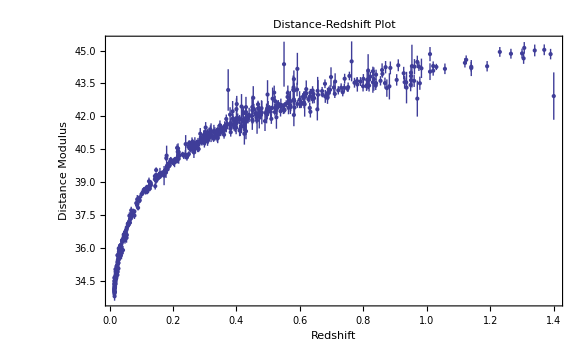

```mathematica
Show[plunion,Frame->True,FrameLabel->{"Redshift","Distance Modulus"},PlotLabel->Style["Distance-Redshift Plot",16,Orange]]
```

### Transition redshift, deceleration parameter, theoretically.

#### Theoretical Function and Values of distance/mag at different redshift.

Distance at redshift z

```mathematica
dz[Ωm0_?NumberQ,Ωd0_?NumberQ,Ωk0_?NumberQ,z_?NumberQ]:=(1+z)NIntegrate[1/hubble[Ωm0,Ωd0,Ωk0,tmp],{tmp,0,z}];
```

Magnitude calculated from distance. Theoretically of cause.

```mathematica
mag[Ωm0_?NumberQ,Ωd0_?NumberQ,Ωk0_?NumberQ,z_?NumberQ]:=5Log[10,c*dz[Ωm0,Ωd0,Ωk0,z]]+25;
```

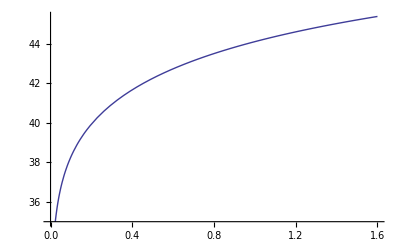

```mathematica
plmagth=Plot[mag[Ωm0w,Ωd0w,0,z],{z,0,1.6}]
```

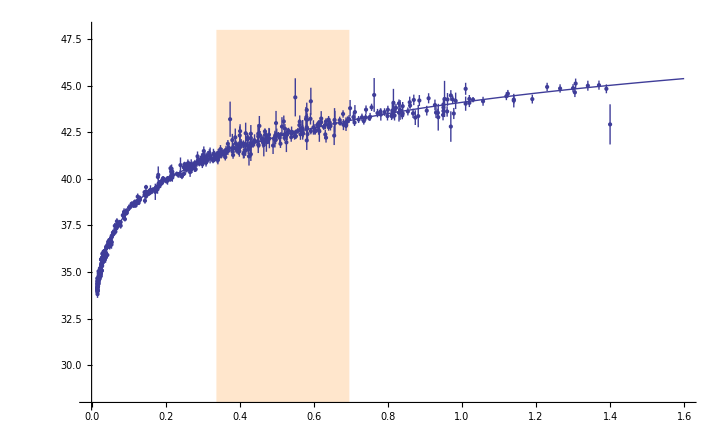

```mathematica
Show[{plunion,plmagth},PlotRange->{{0,1.6},{28,48}},AxesOrigin->{0,28},Prolog->{LightOrange,Rectangle[{0.426-0.089,28},{0.426+0.27,48}]}]
```

#### Deceleration parameter

Deceleration parameter can be ploted with respect to redshift z.
Using flat FRW model. That is Ωk0=0.

```mathematica
pldec[Ωm0v_,color_]:=Plot[q[Ωm0v,1-Ωm0v,0,z],{z,-1,5},PlotRange->{{-1.05,5},{-1.05,0.55}},PlotStyle->color,AxesOrigin->{-1,0}]
```

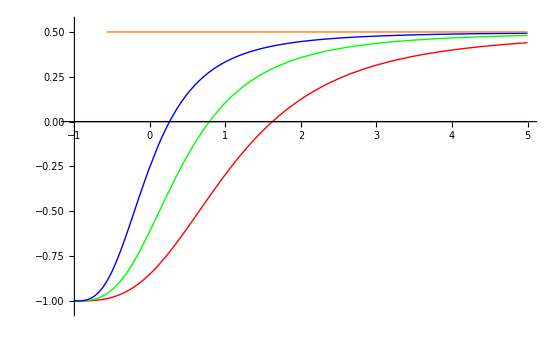

```mathematica
Show[{pldec[0.1,Red],pldec[0.26,Green],pldec[0.5,Blue],pldec[1,Orange],Plot[0,{z,-1,5},PlotStyle->Thick]}]
```

```mathematica
Manipulate[pldec[Ωm0v,{Orange,Thick}],{{Ωm0v,0.26,"Matter Fraction"},0,1}]
```

Plot deceleration parameter with respect to r. This is not related to Ωk0, i.e., the curvature of the spacetime won’t affect this result.

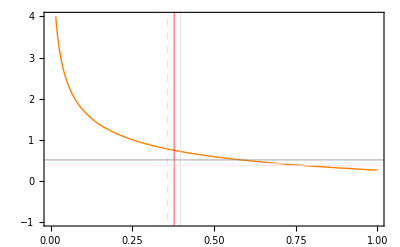

```mathematica
pldecr=Plot[ztrr[r],{r,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}}]
```

In a flat universe, Ωk0=0. Then Ωd0=1-Ωm0.

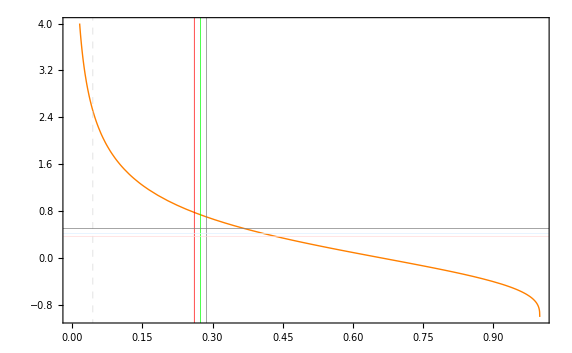

```mathematica
pldecr=Plot[ztr[Ωm0,1-Ωm0],{Ωm0,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}}]
```

### chi square fitting. Using mathematica’s functions.

#### Definations etc

chi square defination with error only.

```mathematica
chi2unionsl[Ωm0_?NumberQ,zt_?NumberQ]:=ParallelSum[(du[[i,2]]-mag[Ωm0,1/2 Ωm0(1+zt)^3,1-Ωm0-1/2 Ωm0(1+zt)^3,du[[i,1]]])^2/du[[i,3]]^2,{i,1,len}]
```

Define a vector/table of  “theory-observation”.

```mathematica
thobtab[Ωm0_,zt_]=ParallelTable[du[[i,2]]-mag[Ωm0,1/2 Ωm0(1+zt)^3,1-Ωm0-1/2 Ωm0(1+zt)^3,du[[i,1]]],{i,1,len}];
```

Import covariance matrix data. “covm” is data with systematic and “covmns” is data without sys.

```mathematica
covm=Import["DATA/UNION2/SCPUnion2_covmat_sys.txt","Table"];
icovm=Inverse[covm];
```

```mathematica
covmns=Import["DATA/UNION2/SCPUnion2_covmat_nosys.txt","Table"];
icovmns=Inverse[covmns];
```

Define chi2 with and without systematic.

```mathematica
chi2union[Ωm0_?NumberQ,zt_?NumberQ]:=thobtab[Ωm0,zt].icovm.thobtab[Ωm0,zt]
```

```mathematica
chi2unionns[Ωm0_?NumberQ,zt_?NumberQ]:=thobtab[Ωm0,zt].icovmns.thobtab[Ωm0,zt]
```

Test the calcuation speed.

```mathematica
chi2union[0.27,0.5]//Timing
```

{8.236,560.12}

```mathematica
chi2unionns[0.27,0.5]//Timing
```

{8.128,735.117}

```mathematica
chi2unionsl[0.27,0.5]//Timing
```

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{0.156,735.121}

#### Find the minimum chi2 for chi2 def. without sys.. AND Export the results to folder DATA/2/

```mathematica
Off[FindMinimum::lstol]
chi2minins=FindMinimum[chi2unionns[x,y],{x,0.15},{y,0.4}]
On[FindMinimum::lstol]
```

{546.166,{x→0.587724,y→0.533675}}

```mathematica
Export["OUTPUT\\2\\chi2unionns_minimum.dat",chi2minins]
```

OUTPUT\2\chi2unionns_minimum.dat

```mathematica
(* chi2minins={546.1663550716052,{x->0.5877241605370803,y->0.5336749032665581}} *)(*Should import what have been exported.*)
```

{546.166,{x→0.587724,y→0.533675}}

Without sys.

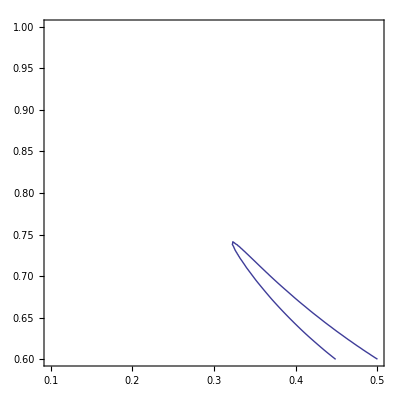

```mathematica
Off[NIntegrate::nlim]
Off[NIntegrate::slwcon]
conchi2ns1s=ContourPlot[{chi2unionns[Ωm0,zt]==chi2minins[[1]]+2.30},{Ωm0,0.1,0.5},{zt,0.6,1.0}]
On[NIntegrate::nlim]
On[NIntegrate::slwcon]
```

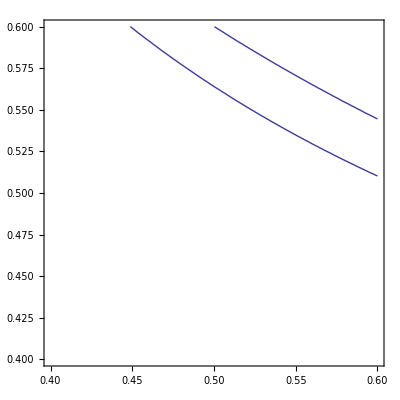

```mathematica
Off[NIntegrate::nlim]
Off[NIntegrate::slwcon]
conchi2ns1s=ContourPlot[{chi2unionns[Ωm0,zt]==chi2minins[[1]]+2.30},{Ωm0,0.3,0.6},{zt,0.4,0.8}]
On[NIntegrate::nlim]
On[NIntegrate::slwcon]
```

```mathematica
conchi2ns1sFF=FullForm[conchi2ns1s];
Export["OUTPUT\\2\\conchi2ns1sFF.dat",conchi2ns1sFF]
Export["OUTPUT\\2\\conchi2ns1s.eps",conchi2ns1s]
```

OUTPUT\2\conchi2ns1sFF.dat

OUTPUT\2\conchi2ns1s.eps

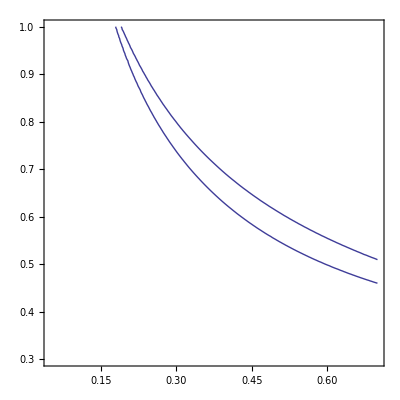

```mathematica
Off[NIntegrate::nlim]
Off[NIntegrate::slwcon]
conchi2ns2s=ContourPlot[{chi2unionns[Ωm0,zt]==chi2minins[[1]]+6.18},{Ωm0,0.05,0.7},{zt,0.3,1.0}]
On[NIntegrate::nlim]
On[NIntegrate::slwcon]
```

```mathematica
conchi2ns2sFF=FullForm[conchi2ns2s];
Export["OUTPUT\\2\\conchi2ns2sFF.dat",conchi2ns2sFF]
Export["OUTPUT\\2\\conchi2ns2s.eps",conchi2ns2s]
```

OUTPUT\2\conchi2ns2sFF.dat

OUTPUT\2\conchi2ns2s.eps

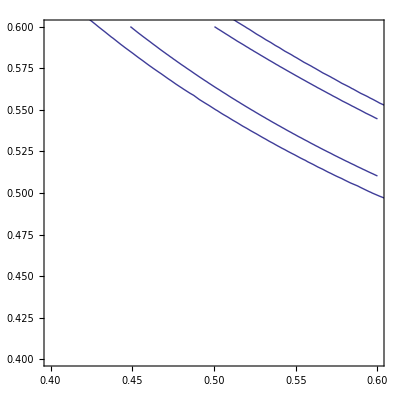

```mathematica
conchi2ns=Show[conchi2ns1s,conchi2ns2s]
```

```mathematica
conchi2nsFF=FullForm[conchi2ns];
Export["OUTPUT\\2\\conchi2nsFF.dat",conchi2nsFF]
Export["OUTPUT\\2\\conchi2ns.eps",conchins2]
```

OUTPUT\2\conchi2nsFF.dat

OUTPUT\2\conchi2ns.eps

#### With Systematic in data. Find the minimum of chi2.

```mathematica
Off[FindMinimum::lstol]
chi2mini=FindMinimum[chi2union[x,y],{x,0.15},{y,0.4}]
On[FindMinimum::lstol]
```

{530.353,{x→0.601866,y→0.524569}}

```mathematica
Export["OUTPUT\\2\\chi2union_minimum.dat",chi2mini]
```

OUTPUT\2\chi2union_minimum.dat

Plot the contour with confidential level 1σ and 2σ. This is a 2 parameter model. Δχ^2(1σ)=2.30 && Δχ^2(2σ)=6.18 && Δχ^2(3σ)=11.83.

With sys.

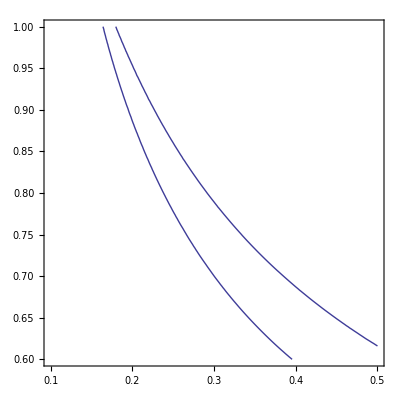

```mathematica
Off[NIntegrate::nlim]
Off[NIntegrate::slwcon]
conchi21s=ContourPlot[{chi2union[Ωm0,zt]==chi2mini[[1]]+2.30},{Ωm0,0.1,0.5},{zt,0.6,1.0}]
On[NIntegrate::nlim]
On[NIntegrate::slwcon]
```

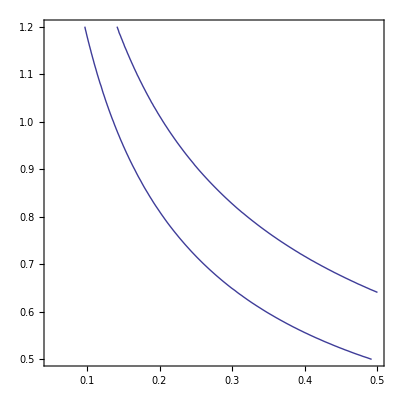

```mathematica
Off[NIntegrate::nlim]
Off[NIntegrate::slwcon]
conchi22s=ContourPlot[{chi2union[Ωm0,zt]==chi2mini[[1]]+6.18},{Ωm0,0.05,0.5},{zt,0.5,1.2}]
On[NIntegrate::nlim]
On[NIntegrate::slwcon]
```

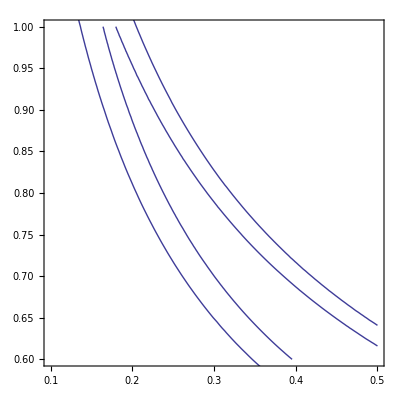

```mathematica
conchi2=Show[conchi21s,conchi22s]
```

```mathematica
Export["OUTPUT\\2\\conchi21s.eps",conchi21s]
Export["OUTPUT\\2\\conchi22s.eps",conchi22s]
Export["OUTPUT\\2\\conchi2.eps",conchi2]
```

OUTPUT\2\conchi21s.eps

OUTPUT\2\conchi22s.eps

OUTPUT\2\conchi2.eps

#### With only error, not the covariance matrix.

```mathematica
chi2minisl=FindMinimum[chi2unionsl[x,y],{x,0.15},{y,0.4}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{546.169,{x→0.587723,y→0.533675}}

```mathematica
chi2unionsl[0.3,0.729]
```

554.376

```mathematica
Export["OUTPUT\\2\\chi2unionsl_nimimum.dat",chi2minisl]
```

OUTPUT\2\chi2unionsl_nimimum.dat

Only error data.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999392671200132}. NIntegrate obtained 0.268826 and 0.0924283 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.996594340002196}. NIntegrate obtained 0.169935 and 0.0126272 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00194}. NIntegrate obtained 10.0159 and 9.81579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00072}. NIntegrate obtained 0.221815 and 0.0104377 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999741179329708}. NIntegrate obtained 0.975752 and 0.76398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

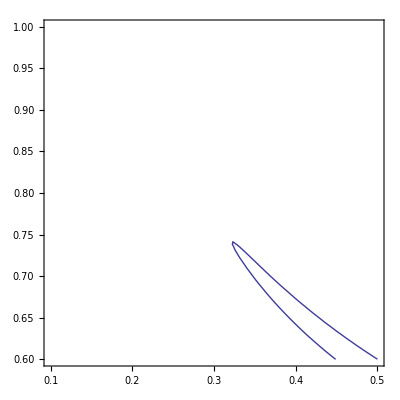

```mathematica
Off[NIntegrate::nlim]
Off[NIntegrate::slwcon]
conchi2sl1s=ContourPlot[{chi2unionsl[Ωm0,zt]==chi2minisl[[1]]+2.30},{Ωm0,0.1,0.5},{zt,0.6,1.0}]
On[NIntegrate::nlim]
On[NIntegrate::slwcon]
```

```mathematica
conchi2sl1sFF=FullForm[conchi2sl1s];
Export["OUTPUT\\2\\conchi2sl1sFF.dat",conchi2sl1sFF]
Export["OUTPUT\\2\\conchi2sl1s.eps",conchi2sl1s]
```

OUTPUT\2\conchi2sl1sFF.dat

OUTPUT\2\conchi2sl1s.eps

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999392671200132}. NIntegrate obtained 0.268826 and 0.0924286 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.996594340002196}. NIntegrate obtained 0.169935 and 0.0126272 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00194}. NIntegrate obtained 10.2448 and 10.0447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00072}. NIntegrate obtained 0.221815 and 0.0104377 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999741179329708}. NIntegrate obtained 0.975972 and 0.764197 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729379}. NIntegrate obtained 0.0226406  - 0.0151167\ ⅈ
 and 0.000809213 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729479}. NIntegrate obtained 0.0226478  - 0.00970953\ ⅈ
 and 0.000585037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729801}. NIntegrate obtained 0.0227497  - 0.0107131\ ⅈ
 and 0.000297855 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727895310736695}. NIntegrate obtained 0.022898  - 0.00530082\ ⅈ
 and 0.000263521 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729407}. NIntegrate obtained 0.0227583  - 0.0137195\ ⅈ
 and 0.000323635 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729664}. NIntegrate obtained 0.0226759  - 0.0153495\ ⅈ
 and 0.000511013 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729714}. NIntegrate obtained 0.0228008  - 0.00654714\ ⅈ
 and 0.000283341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728971}. NIntegrate obtained 0.0229528  - 0.0106155\ ⅈ
 and 0.000310475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730065}. NIntegrate obtained 0.0232789  - 0.00967397\ ⅈ
 and 0.000570962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728971}. NIntegrate obtained 0.0229389  - 0.0109632\ ⅈ
 and 0.000303742 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730204}. NIntegrate obtained 0.0229859  - 0.00836522\ ⅈ
 and 0.000294848 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728023793684329}. NIntegrate obtained 0.0227034  - 0.00508498\ ⅈ
 and 0.000439292 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729925}. NIntegrate obtained 0.0227397  - 0.00874216\ ⅈ
 and 0.000285573 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729125}. NIntegrate obtained 0.0229217  - 0.00652757\ ⅈ
 and 0.00031147 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729125}. NIntegrate obtained 0.022631  - 0.0170253\ ⅈ
 and 0.000554342 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729184}. NIntegrate obtained 0.0228007  - 0.0141872\ ⅈ
 and 0.000315795 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730295}. NIntegrate obtained 0.0230716  - 0.0203231\ ⅈ
 and 0.000457704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728736}. NIntegrate obtained 0.0226874  - 0.0187154\ ⅈ
 and 0.00102592 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.578818}. NIntegrate obtained 0.0170258  - 0.00458388\ ⅈ
 and 0.000239454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.579711}. NIntegrate obtained 0.0184204  - 0.01481\ ⅈ
 and 0.00154763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.578718}. NIntegrate obtained 0.0168847  - 0.011812\ ⅈ
 and 0.000227166 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.578096152598838}. NIntegrate obtained 0.0169711  - 0.00439673\ ⅈ
 and 0.000114893 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.579511}. NIntegrate obtained 0.0169595  - 0.00640251\ ⅈ
 and 0.00017023 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.578805}. NIntegrate obtained 0.0170541  - 0.0123971\ ⅈ
 and 0.000281621 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.57874}. NIntegrate obtained 0.0168277  - 0.00589811\ ⅈ
 and 0.000314438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.578894}. NIntegrate obtained 0.0168791  - 0.010517\ ⅈ
 and 0.000273641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.579479}. NIntegrate obtained 0.0169875  - 0.0124511\ ⅈ
 and 0.000253142 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.579783}. NIntegrate obtained 0.0168657  - 0.0128336\ ⅈ
 and 0.000228302 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.579726}. NIntegrate obtained 0.0169636  - 0.0113014\ ⅈ
 and 0.000179358 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.578801}. NIntegrate obtained 0.0167836  - 0.0104385\ ⅈ
 and 0.000715868 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.578267203147033}. NIntegrate obtained 0.0170356  - 0.00254269\ ⅈ
 and 0.000141866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.578304}. NIntegrate obtained 0.0170258  - 0.00760381\ ⅈ
 and 0.000157481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.578304}. NIntegrate obtained 0.0170258  - 0.00760381\ ⅈ
 and 0.000157481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.577605095123827}. NIntegrate obtained 0.0170797  - 0.00150899\ ⅈ
 and 0.000153309 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.577522813365806}. NIntegrate obtained 0.0169952  - 0.00358882\ ⅈ
 and 0.000103428 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.578519}. NIntegrate obtained 0.0168928  - 0.0114729\ ⅈ
 and 0.000206358 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.578173038428342}. NIntegrate obtained 0.0169554  - 0.00422877\ ⅈ
 and 0.000105222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.579711}. NIntegrate obtained 0.0170047  - 0.0159269\ ⅈ
 and 0.000279425 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.578889}. NIntegrate obtained 0.0168679  - 0.0184122\ ⅈ
 and 0.000483472 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04201}. NIntegrate obtained 0.046681  - 0.0286905\ ⅈ
 and 0.00111129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04086}. NIntegrate obtained 0.0730833  - 0.0411797\ ⅈ
 and 0.00444476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04248}. NIntegrate obtained 0.0741319  - 0.0386558\ ⅈ
 and 0.00205692 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04023099734154}. NIntegrate obtained 0.0467724  - 0.0103686\ ⅈ
 and 0.00134077 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.664965}. NIntegrate obtained 0.0201163  - 0.0144731\ ⅈ
 and 0.000400092 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.666257}. NIntegrate obtained 0.0198728  - 0.0104124\ ⅈ
 and 0.000241823 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.666123}. NIntegrate obtained 0.019801  - 0.00798435\ ⅈ
 and 0.000256771 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.666047}. NIntegrate obtained 0.0197333  - 0.0114496\ ⅈ
 and 0.000269071 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.665423}. NIntegrate obtained 0.0197783  - 0.0136108\ ⅈ
 and 0.000264018 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.666629}. NIntegrate obtained 0.0197691  - 0.0147903\ ⅈ
 and 0.00023862 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.66573}. NIntegrate obtained 0.0197312  - 0.00872993\ ⅈ
 and 0.000267806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.665143}. NIntegrate obtained 0.0197252  - 0.0115353\ ⅈ
 and 0.00026908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.666081}. NIntegrate obtained 0.0198675  - 0.0107254\ ⅈ
 and 0.000265625 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.666244}. NIntegrate obtained 0.0197072  - 0.0118128\ ⅈ
 and 0.00031258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.665261}. NIntegrate obtained 0.0196428  - 0.0106289\ ⅈ
 and 0.000873807 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.665918}. NIntegrate obtained 0.0197586  - 0.00771407\ ⅈ
 and 0.000268514 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.664390163931711}. NIntegrate obtained 0.0198928  - 0.00365894\ ⅈ
 and 0.000225087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.664390163931711}. NIntegrate obtained 0.0198928  - 0.00365894\ ⅈ
 and 0.000225087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.666175}. NIntegrate obtained 0.0197313  - 0.0100839\ ⅈ
 and 0.000267832 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.6643728994821}. NIntegrate obtained 0.0198728  - 0.0030049\ ⅈ
 and 0.000264799 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.665375}. NIntegrate obtained 0.0196357  - 0.0161597\ ⅈ
 and 0.000480495 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.665724}. NIntegrate obtained 0.0196087  - 0.0190426\ ⅈ
 and 0.000529812 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540068}. NIntegrate obtained 0.0153942  - 0.0061713\ ⅈ
 and 0.000249134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.539122490272407}. NIntegrate obtained 0.0154152  - 0.00395859\ ⅈ
 and 0.000291479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.539926}. NIntegrate obtained 0.0154804  - 0.0144529\ ⅈ
 and 0.0002133 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.539122490272407}. NIntegrate obtained 0.0154152  - 0.00395859\ ⅈ
 and 0.000291479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540518}. NIntegrate obtained 0.0153655  - 0.00650454\ ⅈ
 and 0.000720109 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.539853}. NIntegrate obtained 0.0156132  - 0.00722301\ ⅈ
 and 0.000233239 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.53999}. NIntegrate obtained 0.0155528  - 0.0067308\ ⅈ
 and 0.000238002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540808}. NIntegrate obtained 0.015397  - 0.0107489\ ⅈ
 and 0.000224022 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.5393061367485}. NIntegrate obtained 0.0155806  - 0.0018539\ ⅈ
 and 0.000189308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540791}. NIntegrate obtained 0.0154624  - 0.0125134\ ⅈ
 and 0.000254534 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540126}. NIntegrate obtained 0.0157038  - 0.0112286\ ⅈ
 and 0.000342395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.539557856945174964084788182816510015982203185558319091796875}. NIntegrate obtained 0.0155158  - 0.000416116\ ⅈ
 and 0.0000543987 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540202}. NIntegrate obtained 0.0153868  - 0.00496625\ ⅈ
 and 0.000248136 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.539721}. NIntegrate obtained 0.0157585  - 0.00436078\ ⅈ
 and 0.00032637 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540733}. NIntegrate obtained 0.0155778  - 0.00821083\ ⅈ
 and 0.000212201 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540272}. NIntegrate obtained 0.0154616  - 0.00574228\ ⅈ
 and 0.000198538 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540733}. NIntegrate obtained 0.0155778  - 0.00821083\ ⅈ
 and 0.000212201 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540571}. NIntegrate obtained 0.0154893  - 0.0053615\ ⅈ
 and 0.000163228 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540269}. NIntegrate obtained 0.0154447  - 0.0114412\ ⅈ
 and 0.000218232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.539867}. NIntegrate obtained 0.015365  - 0.0155403\ ⅈ
 and 0.000303965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.541037}. NIntegrate obtained 0.0153003  - 0.017784\ ⅈ
 and 0.000517758 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461358}. NIntegrate obtained 0.012906  - 0.00804845\ ⅈ
 and 0.000436919 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.462003}. NIntegrate obtained 0.0130591  - 0.00638625\ ⅈ
 and 0.000117589 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.46093}. NIntegrate obtained 0.0130325  - 0.0038127\ ⅈ
 and 0.000149324 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461154}. NIntegrate obtained 0.0129464  - 0.00366589\ ⅈ
 and 0.000210012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.460848701425832}. NIntegrate obtained 0.0130942  - 0.00323862\ ⅈ
 and 0.000122245 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.462003}. NIntegrate obtained 0.0130591  - 0.00638625\ ⅈ
 and 0.000117589 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.46124}. NIntegrate obtained 0.0129489  - 0.00828289\ ⅈ
 and 0.000197453 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461076}. NIntegrate obtained 0.0130117  - 0.00363925\ ⅈ
 and 0.000132101 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461589}. NIntegrate obtained 0.0130448  - 0.0109826\ ⅈ
 and 0.000205189 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461296}. NIntegrate obtained 0.012905  - 0.00714074\ ⅈ
 and 0.0014989 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461112}. NIntegrate obtained 0.0140579  - 0.0124329\ ⅈ
 and 0.0011698 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461117}. NIntegrate obtained 0.0131781  - 0.00351422\ ⅈ
 and 0.000221122 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.46171}. NIntegrate obtained 0.0129779  - 0.00699761\ ⅈ
 and 0.000171751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461153}. NIntegrate obtained 0.0131942  - 0.00667497\ ⅈ
 and 0.000243643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461213}. NIntegrate obtained 0.0130201  - 0.00461289\ ⅈ
 and 0.000150446 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461217}. NIntegrate obtained 0.0130732  - 0.0033747\ ⅈ
 and 0.00017218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461567}. NIntegrate obtained 0.0134243  - 0.00912762\ ⅈ
 and 0.000490105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.461567}. NIntegrate obtained 0.0134243  - 0.00912762\ ⅈ
 and 0.000490105 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.462175}. NIntegrate obtained 0.0129294  - 0.0117882\ ⅈ
 and 0.000236849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.462172}. NIntegrate obtained 0.013968  - 0.0146736\ ⅈ
 and 0.00104835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.463107}. NIntegrate obtained 0.0133004  - 0.0164554\ ⅈ
 and 0.000342235 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899887}. NIntegrate obtained 0.0297276  - 0.00999648\ ⅈ
 and 0.000553322 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.898877687638025}. NIntegrate obtained 0.0303589  - 0.00672931\ ⅈ
 and 0.000539564 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899668}. NIntegrate obtained 0.0297958  - 0.0103808\ ⅈ
 and 0.000421058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899985}. NIntegrate obtained 0.0299734  - 0.008842\ ⅈ
 and 0.000524926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.898110477493179}. NIntegrate obtained 0.0299142  - 0.0063239\ ⅈ
 and 0.00028857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.900923}. NIntegrate obtained 0.0301997  - 0.00891217\ ⅈ
 and 0.000458449 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899516}. NIntegrate obtained 0.029982  - 0.01222\ ⅈ
 and 0.000396621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.898736685554073}. NIntegrate obtained 0.0303508  - 0.00261156\ ⅈ
 and 0.000395763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.898649158342715}. NIntegrate obtained 0.029762  - 0.00900401\ ⅈ
 and 0.00103543 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.900453}. NIntegrate obtained 0.0296811  - 0.0135477\ ⅈ
 and 0.000859957 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899514}. NIntegrate obtained 0.0298471  - 0.0190773\ ⅈ
 and 0.000393145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.901717}. NIntegrate obtained 0.0297814  - 0.0311368\ ⅈ
 and 0.000797618 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.898537483787344}. NIntegrate obtained 0.0298314  - 0.0083447\ ⅈ
 and 0.000376574 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.900085}. NIntegrate obtained 0.0300289  - 0.0147742\ ⅈ
 and 0.000451681 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.638442}. NIntegrate obtained 0.0189994  - 0.0140424\ ⅈ
 and 0.000603016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637077}. NIntegrate obtained 0.0189934  - 0.0105886\ ⅈ
 and 0.000498873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.636291753200147}. NIntegrate obtained 0.0186821  - 0.0032696\ ⅈ
 and 0.000208438 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.636199646089797}. NIntegrate obtained 0.018801  - 0.00309201\ ⅈ
 and 0.000284174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637526}. NIntegrate obtained 0.0185955  - 0.0113884\ ⅈ
 and 0.000296337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.638001}. NIntegrate obtained 0.0184504  - 0.0134829\ ⅈ
 and 0.000289988 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.636898917056482}. NIntegrate obtained 0.018525  - 0.00135313\ ⅈ
 and 0.000170448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.638308}. NIntegrate obtained 0.0186872  - 0.00903389\ ⅈ
 and 0.000263007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.638268}. NIntegrate obtained 0.018815  - 0.011352\ ⅈ
 and 0.000419637 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637424}. NIntegrate obtained 0.018414  - 0.0119747\ ⅈ
 and 0.00041538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.638333}. NIntegrate obtained 0.0185866  - 0.0100492\ ⅈ
 and 0.000216958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637863}. NIntegrate obtained 0.0185639  - 0.00824822\ ⅈ
 and 0.000250319 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637343}. NIntegrate obtained 0.0184434  - 0.00553592\ ⅈ
 and 0.000322344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637343}. NIntegrate obtained 0.0184434  - 0.00553592\ ⅈ
 and 0.000322344 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637489}. NIntegrate obtained 0.0184036  - 0.00592557\ ⅈ
 and 0.00114941 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637487}. NIntegrate obtained 0.0185642  - 0.0101966\ ⅈ
 and 0.000271642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.636535791525389}. NIntegrate obtained 0.0185648  - 0.0020661\ ⅈ
 and 0.000181986 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637484}. NIntegrate obtained 0.0183833  - 0.0157144\ ⅈ
 and 0.000790807 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.639006}. NIntegrate obtained 0.0184627  - 0.0179441\ ⅈ
 and 0.000280555 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.518272}. NIntegrate obtained 0.0146669  - 0.00660373\ ⅈ
 and 0.000155074 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.51878}. NIntegrate obtained 0.0146048  - 0.00475951\ ⅈ
 and 0.00021904 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.519086}. NIntegrate obtained 0.0149116  - 0.0140191\ ⅈ
 and 0.000384831 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.51878}. NIntegrate obtained 0.0146048  - 0.00475951\ ⅈ
 and 0.00021904 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.51874}. NIntegrate obtained 0.0147061  - 0.00714924\ ⅈ
 and 0.000202495 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.518897}. NIntegrate obtained 0.0147294  - 0.00634414\ ⅈ
 and 0.000206101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.519384}. NIntegrate obtained 0.014776  - 0.00759491\ ⅈ
 and 0.000175227 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.51948}. NIntegrate obtained 0.0147736  - 0.0105779\ ⅈ
 and 0.000216597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.517879458421503}. NIntegrate obtained 0.0146456  - 0.0030591\ ⅈ
 and 0.000156642 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.517712872748572}. NIntegrate obtained 0.0147374  - 0.00350087\ ⅈ
 and 0.000132162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.518752}. NIntegrate obtained 0.0148689  - 0.0122573\ ⅈ
 and 0.000313391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.519534}. NIntegrate obtained 0.0147873  - 0.0112057\ ⅈ
 and 0.000225165 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.51827}. NIntegrate obtained 0.0146733  - 0.00556657\ ⅈ
 and 0.000206858 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.519225}. NIntegrate obtained 0.0146712  - 0.00524931\ ⅈ
 and 0.000138541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.51809036621699156607671887808663768737460486590862274169921875}. NIntegrate obtained 0.0149259  - 0.000499344\ ⅈ
 and 0.000242898 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.519265}. NIntegrate obtained 0.0146225  - 0.00856573\ ⅈ
 and 0.000276123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.519265}. NIntegrate obtained 0.0146225  - 0.00856573\ ⅈ
 and 0.000276123 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.518194}. NIntegrate obtained 0.0146601  - 0.00980403\ ⅈ
 and 0.00391981 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.51955}. NIntegrate obtained 0.0148248  - 0.0112956\ ⅈ
 and 0.00025229 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.519945}. NIntegrate obtained 0.014571  - 0.0152476\ ⅈ
 and 0.000525903 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.518771}. NIntegrate obtained 0.0145706  - 0.0168971\ ⅈ
 and 0.000271958 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.441983}. NIntegrate obtained 0.0124208  - 0.00792549\ ⅈ
 and 0.0000637133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.443077}. NIntegrate obtained 0.012426  - 0.00667935\ ⅈ
 and 0.000102959 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.442785}. NIntegrate obtained 0.012383  - 0.00426407\ ⅈ
 and 0.000127748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.442141}. NIntegrate obtained 0.0123618  - 0.00407987\ ⅈ
 and 0.000129474 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.442375}. NIntegrate obtained 0.0123251  - 0.00452956\ ⅈ
 and 0.000172864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.443077}. NIntegrate obtained 0.012426  - 0.00667935\ ⅈ
 and 0.000102959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.44249}. NIntegrate obtained 0.0123201  - 0.00837171\ ⅈ
 and 0.000188697 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.442633}. NIntegrate obtained 0.0123138  - 0.00445531\ ⅈ
 and 0.000190398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.443308}. NIntegrate obtained 0.0127649  - 0.0108432\ ⅈ
 and 0.00045097 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.442031}. NIntegrate obtained 0.0126762  - 0.00602936\ ⅈ
 and 0.000325532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.442463}. NIntegrate obtained 0.0123355  - 0.0123279\ ⅈ
 and 0.000304682 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.442711}. NIntegrate obtained 0.0125309  - 0.00423721\ ⅈ
 and 0.000225904 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.442087}. NIntegrate obtained 0.0124161  - 0.0071886\ ⅈ
 and 0.000182935 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.442934}. NIntegrate obtained 0.0123967  - 0.00698745\ ⅈ
 and 0.000174357 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.442922}. NIntegrate obtained 0.0123903  - 0.00422154\ ⅈ
 and 0.0000916934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.442782}. NIntegrate obtained 0.0124336  - 0.00921544\ ⅈ
 and 0.000195119 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.442967}. NIntegrate obtained 0.0123752  - 0.0052147\ ⅈ
 and 0.000126075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.442782}. NIntegrate obtained 0.0124336  - 0.00921544\ ⅈ
 and 0.000195119 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.44305}. NIntegrate obtained 0.0122846  - 0.0116326\ ⅈ
 and 0.000235355 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.441940212169249}. NIntegrate obtained 0.0123822  - 0.00211852\ ⅈ
 and 0.000102157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.44225}. NIntegrate obtained 0.0122699  - 0.014643\ ⅈ
 and 0.000287352 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.387300892117225}. NIntegrate obtained 0.0108178  - 0.00087818\ ⅈ
 and 0.0000618786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.387115772041381}. NIntegrate obtained 0.0108304  - 0.00258803\ ⅈ
 and 0.0000551982 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.387306610912258}. NIntegrate obtained 0.0107942  - 0.00138028\ ⅈ
 and 0.000116378 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.387056152693392}. NIntegrate obtained 0.0107488  - 0.00155479\ ⅈ
 and 0.000137406 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.387115123023393}. NIntegrate obtained 0.0108115  - 0.00066693\ ⅈ
 and 0.0000851447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.388001}. NIntegrate obtained 0.0107808  - 0.00355261\ ⅈ
 and 0.000110461 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.386930707462331}. NIntegrate obtained 0.0107491  - 0.00230959\ ⅈ
 and 0.000146347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.387678}. NIntegrate obtained 0.0107123  - 0.00579966\ ⅈ
 and 0.00021606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.387376}. NIntegrate obtained 0.0107981  - 0.00319724\ ⅈ
 and 0.000097441 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.38759}. NIntegrate obtained 0.0107803  - 0.00552091\ ⅈ
 and 0.000129409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.387413}. NIntegrate obtained 0.0108354  - 0.00737002\ ⅈ
 and 0.0001341 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.388001}. NIntegrate obtained 0.0107808  - 0.00355261\ ⅈ
 and 0.000110461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.38749}. NIntegrate obtained 0.0107286  - 0.00879481\ ⅈ
 and 0.000162953 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.388274}. NIntegrate obtained 0.0107959  - 0.00581531\ ⅈ
 and 0.0000929075 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.387445}. NIntegrate obtained 0.0107115  - 0.00722477\ ⅈ
 and 0.000330343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.388213}. NIntegrate obtained 0.0106923  - 0.0121819\ ⅈ
 and 0.000222502 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.387835}. NIntegrate obtained 0.0108373  - 0.00775922\ ⅈ
 and 0.000182365 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.38772}. NIntegrate obtained 0.0111349  - 0.00329199\ ⅈ
 and 0.000395477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.388278}. NIntegrate obtained 0.0108583  - 0.00761037\ ⅈ
 and 0.000158899 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.387492}. NIntegrate obtained 0.0108223  - 0.00565892\ ⅈ
 and 0.000161578 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.386983618010941}. NIntegrate obtained 0.0107593  - 0.00188103\ ⅈ
 and 0.000118524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.388037}. NIntegrate obtained 0.0109858  - 0.00553602\ ⅈ
 and 0.000252801 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.387769}. NIntegrate obtained 0.0110046  - 0.00940929\ ⅈ
 and 0.000328108 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.388862}. NIntegrate obtained 0.0107974  - 0.011424\ ⅈ
 and 0.000126603 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.387454}. NIntegrate obtained 0.0107685  - 0.00449929\ ⅈ
 and 0.000118494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.388461}. NIntegrate obtained 0.0107815  - 0.0138947\ ⅈ
 and 0.000221119 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897993}. NIntegrate obtained 0.0287567  - 0.0092705\ ⅈ
 and 0.000368651 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89645332223946}. NIntegrate obtained 0.0287399  - 0.00694195\ ⅈ
 and 0.00038261 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897758}. NIntegrate obtained 0.0287845  - 0.00973212\ ⅈ
 and 0.000378889 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89811}. NIntegrate obtained 0.0297079  - 0.00831467\ ⅈ
 and 0.00099064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.895584825564055}. NIntegrate obtained 0.0291263  - 0.00604011\ ⅈ
 and 0.000363317 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897169}. NIntegrate obtained 0.0286885  - 0.00881936\ ⅈ
 and 0.000442343 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897543}. NIntegrate obtained 0.0288526  - 0.0115253\ ⅈ
 and 0.000391142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.896625404952081}. NIntegrate obtained 0.0289398  - 0.00297431\ ⅈ
 and 0.000231119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.896546100438719}. NIntegrate obtained 0.0288905  - 0.0077903\ ⅈ
 and 0.000188837 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.898461}. NIntegrate obtained 0.028719  - 0.0124073\ ⅈ
 and 0.00047306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.896464269681151}. NIntegrate obtained 0.0288305  - 0.00795644\ ⅈ
 and 0.000229718 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897287}. NIntegrate obtained 0.0287151  - 0.0177169\ ⅈ
 and 0.00041153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.898021}. NIntegrate obtained 0.0285962  - 0.014698\ ⅈ
 and 0.000878439 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899041}. NIntegrate obtained 0.0286341  - 0.0274792\ ⅈ
 and 0.00077961 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.632758}. NIntegrate obtained 0.0180815  - 0.0139673\ ⅈ
 and 0.000268297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.632214}. NIntegrate obtained 0.0182931  - 0.0104111\ ⅈ
 and 0.000318908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.6307613556392}. NIntegrate obtained 0.0182191  - 0.00351394\ ⅈ
 and 0.000159037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.632493}. NIntegrate obtained 0.0183705  - 0.0111594\ ⅈ
 and 0.000364557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.630942992284383}. NIntegrate obtained 0.01809  - 0.00392184\ ⅈ
 and 0.000310493 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.632517}. NIntegrate obtained 0.018167  - 0.013099\ ⅈ
 and 0.000256416 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.630731816495171}. NIntegrate obtained 0.0181208  - 0.00225806\ ⅈ
 and 0.000223849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.632214}. NIntegrate obtained 0.0187871  - 0.00890017\ ⅈ
 and 0.000718992 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.631549}. NIntegrate obtained 0.018089  - 0.0116142\ ⅈ
 and 0.000449243 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.632338}. NIntegrate obtained 0.0180212  - 0.0118368\ ⅈ
 and 0.000449253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.631997}. NIntegrate obtained 0.018392  - 0.00986105\ ⅈ
 and 0.000348217 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.631957}. NIntegrate obtained 0.0183565  - 0.00816116\ ⅈ
 and 0.000310124 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.631103800388894}. NIntegrate obtained 0.0182307  - 0.00261446\ ⅈ
 and 0.000202475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.6310342155436860079979755067114410849171690642833709716796875}. NIntegrate obtained 0.0183026  - 0.000853269\ ⅈ
 and 0.000120745 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.631976}. NIntegrate obtained 0.0180564  - 0.00570357\ ⅈ
 and 0.000342381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.631976}. NIntegrate obtained 0.0180564  - 0.00570357\ ⅈ
 and 0.000342381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.632706}. NIntegrate obtained 0.0180447  - 0.0104887\ ⅈ
 and 0.000445987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.632177}. NIntegrate obtained 0.0180826  - 0.00522586\ ⅈ
 and 0.000264732 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.631508}. NIntegrate obtained 0.0182079  - 0.0149752\ ⅈ
 and 0.000180305 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.632326}. NIntegrate obtained 0.0180194  - 0.0174948\ ⅈ
 and 0.000372116 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.509795}. NIntegrate obtained 0.0142976  - 0.00670243\ ⅈ
 and 0.000170119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.509874}. NIntegrate obtained 0.0142321  - 0.00509844\ ⅈ
 and 0.000256682 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.509614}. NIntegrate obtained 0.0143622  - 0.0138797\ ⅈ
 and 0.000207197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.509874}. NIntegrate obtained 0.0142321  - 0.00509844\ ⅈ
 and 0.000256682 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.510488}. NIntegrate obtained 0.0145518  - 0.00646226\ ⅈ
 and 0.000311278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.50999}. NIntegrate obtained 0.0143188  - 0.00726319\ ⅈ
 and 0.000185992 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.510429}. NIntegrate obtained 0.0157823  - 0.00758512\ ⅈ
 and 0.00149138 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.510339}. NIntegrate obtained 0.0143466  - 0.0105117\ ⅈ
 and 0.000210293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.508996864783222}. NIntegrate obtained 0.0143767  - 0.00347188\ ⅈ
 and 0.000118176 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.50946}. NIntegrate obtained 0.0143142  - 0.00402869\ ⅈ
 and 0.000176779 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.510276}. NIntegrate obtained 0.0147745  - 0.0120746\ ⅈ
 and 0.000554095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.51003}. NIntegrate obtained 0.0141824  - 0.0115626\ ⅈ
 and 0.000515895 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.51019}. NIntegrate obtained 0.0142073  - 0.00638272\ ⅈ
 and 0.000695168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.510116}. NIntegrate obtained 0.0143508  - 0.00540087\ ⅈ
 and 0.000283087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.509303035562961}. NIntegrate obtained 0.014267  - 0.00209702\ ⅈ
 and 0.000218388 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.509872}. NIntegrate obtained 0.0143815  - 0.0084588\ ⅈ
 and 0.000234652 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.509872}. NIntegrate obtained 0.0143815  - 0.0084588\ ⅈ
 and 0.000234652 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.50995}. NIntegrate obtained 0.0143024  - 0.00614781\ ⅈ
 and 0.000186415 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.509987}. NIntegrate obtained 0.0145411  - 0.0111455\ ⅈ
 and 0.000498468 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.509984}. NIntegrate obtained 0.0142351  - 0.0147297\ ⅈ
 and 0.000445331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.509865}. NIntegrate obtained 0.0143688  - 0.0163665\ ⅈ
 and 0.000233796 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.432295}. NIntegrate obtained 0.0120613  - 0.00788324\ ⅈ
 and 0.000175491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.431944}. NIntegrate obtained 0.012024  - 0.00678056\ ⅈ
 and 0.00017079 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.432151}. NIntegrate obtained 0.0119896  - 0.00459424\ ⅈ
 and 0.000184672 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.432571}. NIntegrate obtained 0.0121203  - 0.00433392\ ⅈ
 and 0.000170921 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.431151157430614}. NIntegrate obtained 0.0120619  - 0.00163323\ ⅈ
 and 0.0000731162 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.431944}. NIntegrate obtained 0.012024  - 0.00678056\ ⅈ
 and 0.00017079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.43249}. NIntegrate obtained 0.0120642  - 0.00829683\ ⅈ
 and 0.000178239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.431955}. NIntegrate obtained 0.012157  - 0.00458071\ ⅈ
 and 0.000200982 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.431151157430614}. NIntegrate obtained 0.0120619  - 0.00163323\ ⅈ
 and 0.0000731162 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.432398}. NIntegrate obtained 0.0121069  - 0.00615325\ ⅈ
 and 0.000186789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.432291}. NIntegrate obtained 0.0120942  - 0.0120867\ ⅈ
 and 0.00036022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.432055}. NIntegrate obtained 0.0120651  - 0.00456584\ ⅈ
 and 0.000165338 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.432852}. NIntegrate obtained 0.0119835  - 0.00758495\ ⅈ
 and 0.000330598 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.432686}. NIntegrate obtained 0.0120093  - 0.00711008\ ⅈ
 and 0.000159036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.431816}. NIntegrate obtained 0.0120003  - 0.00543713\ ⅈ
 and 0.000129207 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.43233}. NIntegrate obtained 0.0120885  - 0.0044404\ ⅈ
 and 0.00028008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.432048}. NIntegrate obtained 0.0123863  - 0.00916202\ ⅈ
 and 0.000443376 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.432048}. NIntegrate obtained 0.0123863  - 0.00916202\ ⅈ
 and 0.000443376 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.431894}. NIntegrate obtained 0.0120675  - 0.0113676\ ⅈ
 and 0.000172279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.431373975452425}. NIntegrate obtained 0.0119922  - 0.0028423\ ⅈ
 and 0.000136161 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.432289}. NIntegrate obtained 0.0119456  - 0.0142394\ ⅈ
 and 0.00021073 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.376202800856682}. NIntegrate obtained 0.010437  - 0.00128474\ ⅈ
 and 0.0000763756 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.376009123817872}. NIntegrate obtained 0.0106091  - 0.000945235\ ⅈ
 and 0.00017913 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.376202800856682}. NIntegrate obtained 0.010437  - 0.00128474\ ⅈ
 and 0.0000763756 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.37609457025982}. NIntegrate obtained 0.0103859  - 0.00215861\ ⅈ
 and 0.000252117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.377162}. NIntegrate obtained 0.0104625  - 0.00306903\ ⅈ
 and 0.0000961604 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.376395465427466}. NIntegrate obtained 0.0104795  - 0.00214493\ ⅈ
 and 0.0000808436 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.377166}. NIntegrate obtained 0.01056  - 0.00274881\ ⅈ
 and 0.000156452 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.376000211738253}. NIntegrate obtained 0.0104254  - 0.00114948\ ⅈ
 and 0.000101867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.376345389956817}. NIntegrate obtained 0.0104456  - 0.00228877\ ⅈ
 and 0.0000822285 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.376661}. NIntegrate obtained 0.0104345  - 0.00358267\ ⅈ
 and 0.00011825 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.376197632852162}. NIntegrate obtained 0.0104405  - 0.00186676\ ⅈ
 and 0.000100681 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.377083}. NIntegrate obtained 0.0103746  - 0.0039999\ ⅈ
 and 0.000286861 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.377043}. NIntegrate obtained 0.0103515  - 0.00615454\ ⅈ
 and 0.000397906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.377063}. NIntegrate obtained 0.0103813  - 0.00576609\ ⅈ
 and 0.000161789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.377393}. NIntegrate obtained 0.0103648  - 0.00896869\ ⅈ
 and 0.00154382 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.377083}. NIntegrate obtained 0.0103746  - 0.0039999\ ⅈ
 and 0.000286861 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.37749}. NIntegrate obtained 0.0105473  - 0.00863859\ ⅈ
 and 0.000184781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.376625}. NIntegrate obtained 0.0105767  - 0.0058041\ ⅈ
 and 0.000224542 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.376741}. NIntegrate obtained 0.0104453  - 0.00698063\ ⅈ
 and 0.000193935 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.378041}. NIntegrate obtained 0.0103902  - 0.0120707\ ⅈ
 and 0.000198266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.376836}. NIntegrate obtained 0.0104303  - 0.00582853\ ⅈ
 and 0.000156196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.377446}. NIntegrate obtained 0.010383  - 0.00796841\ ⅈ
 and 0.000177725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.376904}. NIntegrate obtained 0.010451  - 0.00372099\ ⅈ
 and 0.00013061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.376891}. NIntegrate obtained 0.0104003  - 0.00770747\ ⅈ
 and 0.000149028 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.376092127867603}. NIntegrate obtained 0.0105132  - 0.00249176\ ⅈ
 and 0.00010478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.376483}. NIntegrate obtained 0.0104177  - 0.00581129\ ⅈ
 and 0.000119734 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.377034}. NIntegrate obtained 0.0105023  - 0.00938271\ ⅈ
 and 0.000193048 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.377706}. NIntegrate obtained 0.0103841  - 0.0113037\ ⅈ
 and 0.000168691 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.37679}. NIntegrate obtained 0.0104115  - 0.00473922\ ⅈ
 and 0.000133514 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.376508}. NIntegrate obtained 0.0103482  - 0.0140928\ ⅈ
 and 0.000473512 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.33499}. NIntegrate obtained 0.00919301  - 0.00357014\ ⅈ
 and 0.000269672 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.334721}. NIntegrate obtained 0.00925991  - 0.00335608\ ⅈ
 and 0.000114448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.33499}. NIntegrate obtained 0.00919301  - 0.00357014\ ⅈ
 and 0.000269672 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.334635}. NIntegrate obtained 0.0092913  - 0.00263252\ ⅈ
 and 0.000110525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.33515}. NIntegrate obtained 0.00932455  - 0.00368715\ ⅈ
 and 0.000123124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.33472}. NIntegrate obtained 0.00922782  - 0.00437276\ ⅈ
 and 0.000117278 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.334556}. NIntegrate obtained 0.0092499  - 0.00419225\ ⅈ
 and 0.000111045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.334857}. NIntegrate obtained 0.00939595  - 0.00334367\ ⅈ
 and 0.000218129 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.334906}. NIntegrate obtained 0.00926099  - 0.00254647\ ⅈ
 and 0.000108411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.334932}. NIntegrate obtained 0.00930882  - 0.00284305\ ⅈ
 and 0.000128462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.334818}. NIntegrate obtained 0.00922888  - 0.00390767\ ⅈ
 and 0.000116901 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.335051}. NIntegrate obtained 0.00928564  - 0.00366048\ ⅈ
 and 0.00011836 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.334504}. NIntegrate obtained 0.00945081  - 0.00635987\ ⅈ
 and 0.00019651 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.334953}. NIntegrate obtained 0.00937393  - 0.00618934\ ⅈ
 and 0.000193663 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.335091}. NIntegrate obtained 0.00924702  - 0.00489191\ ⅈ
 and 0.000112776 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.335089}. NIntegrate obtained 0.00918572  - 0.00779065\ ⅈ
 and 0.00017387 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.33499}. NIntegrate obtained 0.00918523  - 0.00885273\ ⅈ
 and 0.000192446 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.334885}. NIntegrate obtained 0.00920246  - 0.00644997\ ⅈ
 and 0.00014627 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.334999}. NIntegrate obtained 0.00934405  - 0.00727147\ ⅈ
 and 0.000180113 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.335658}. NIntegrate obtained 0.0091912  - 0.0116621\ ⅈ
 and 0.000171344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.33518}. NIntegrate obtained 0.00924121  - 0.00637298\ ⅈ
 and 0.000119556 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.334737}. NIntegrate obtained 0.00936113  - 0.00798423\ ⅈ
 and 0.000180609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.335302}. NIntegrate obtained 0.00924453  - 0.004852\ ⅈ
 and 0.0000959422 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.33476}. NIntegrate obtained 0.00916117  - 0.00857994\ ⅈ
 and 0.000691479 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.335091}. NIntegrate obtained 0.00947734  - 0.00395335\ ⅈ
 and 0.000257688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.335078}. NIntegrate obtained 0.00931497  - 0.00626464\ ⅈ
 and 0.000150669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.335439}. NIntegrate obtained 0.00922929  - 0.00943222\ ⅈ
 and 0.000196847 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.334675}. NIntegrate obtained 0.00947082  - 0.0109739\ ⅈ
 and 0.000274159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.335022}. NIntegrate obtained 0.00928019  - 0.00546935\ ⅈ
 and 0.00013736 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.334672}. NIntegrate obtained 0.00928162  - 0.0131778\ ⅈ
 and 0.000178868 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.791899}. NIntegrate obtained 0.0265459  - 0.0148652\ ⅈ
 and 0.000490686 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7902976495498}. NIntegrate obtained 0.0263456  - 0.00680989\ ⅈ
 and 0.00019782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.791877}. NIntegrate obtained 0.0261767  - 0.00909469\ ⅈ
 and 0.000424973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.791564}. NIntegrate obtained 0.0263809  - 0.0132567\ ⅈ
 and 0.000404891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790789}. NIntegrate obtained 0.0263676  - 0.015471\ ⅈ
 and 0.000258269 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.791697}. NIntegrate obtained 0.0262527  - 0.0095176\ ⅈ
 and 0.000360834 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.791119}. NIntegrate obtained 0.0268861  - 0.0087709\ ⅈ
 and 0.000667855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790026345301426}. NIntegrate obtained 0.0262667  - 0.00771304\ ⅈ
 and 0.000318953 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.791235}. NIntegrate obtained 0.026166  - 0.0147683\ ⅈ
 and 0.000438142 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790610814299902}. NIntegrate obtained 0.0264503  - 0.00469966\ ⅈ
 and 0.000233746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790111737892588}. NIntegrate obtained 0.0262908  - 0.00543916\ ⅈ
 and 0.000295273 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790280168358174}. NIntegrate obtained 0.0263238  - 0.00529086\ ⅈ
 and 0.000291115 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.79227}. NIntegrate obtained 0.0262788  - 0.0140876\ ⅈ
 and 0.000323023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790883}. NIntegrate obtained 0.026266  - 0.0174831\ ⅈ
 and 0.000316159 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.792734}. NIntegrate obtained 0.0262555  - 0.0193276\ ⅈ
 and 0.000512855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.792639}. NIntegrate obtained 0.0264847  - 0.0227533\ ⅈ
 and 0.000407153 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.691489}. NIntegrate obtained 0.020845  - 0.0148293\ ⅈ
 and 0.000336691 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.690573}. NIntegrate obtained 0.0209293  - 0.0102165\ ⅈ
 and 0.000226144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.691457}. NIntegrate obtained 0.0208426  - 0.0074153\ ⅈ
 and 0.000357885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.691213}. NIntegrate obtained 0.0210164  - 0.0111209\ ⅈ
 and 0.000296102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.691017}. NIntegrate obtained 0.0209858  - 0.0136519\ ⅈ
 and 0.000307808 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.691461}. NIntegrate obtained 0.0207962  - 0.0152269\ ⅈ
 and 0.000444105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.691629}. NIntegrate obtained 0.0217907  - 0.00788103\ ⅈ
 and 0.000896754 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.692018}. NIntegrate obtained 0.0210074  - 0.0112202\ ⅈ
 and 0.000215243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.69069}. NIntegrate obtained 0.0208519  - 0.0107461\ ⅈ
 and 0.000347527 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.691674}. NIntegrate obtained 0.020978  - 0.0114686\ ⅈ
 and 0.000269776 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.690605}. NIntegrate obtained 0.0210275  - 0.00935922\ ⅈ
 and 0.000232027 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.69102}. NIntegrate obtained 0.020816  - 0.0071862\ ⅈ
 and 0.000465327 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.69099}. NIntegrate obtained 0.0213455  - 0.00793862\ ⅈ
 and 0.000498467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.692075}. NIntegrate obtained 0.0214596  - 0.0139884\ ⅈ
 and 0.000601874 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.691675}. NIntegrate obtained 0.0214878  - 0.00943305\ ⅈ
 and 0.000615852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.691273}. NIntegrate obtained 0.0208594  - 0.0162135\ ⅈ
 and 0.000324474 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.691575}. NIntegrate obtained 0.0208293  - 0.0172838\ ⅈ
 and 0.00035927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.692443}. NIntegrate obtained 0.0208387  - 0.0196395\ ⅈ
 and 0.000385485 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.931529227573594}. NIntegrate obtained 0.0330402  - 0.00772035\ ⅈ
 and 0.000429679 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932321305727351}. NIntegrate obtained 0.0328945  - 0.00221443\ ⅈ
 and 0.000304449 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.931812130070297}. NIntegrate obtained 0.0326097  - 0.00904233\ ⅈ
 and 0.000532266 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932445282818634}. NIntegrate obtained 0.0328477  - 0.00666711\ ⅈ
 and 0.000322098 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933051}. NIntegrate obtained 0.0326109  - 0.0116776\ ⅈ
 and 0.000482249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932058287991264}. NIntegrate obtained 0.0325303  - 0.0117432\ ⅈ
 and 0.00502987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.931957401911503}. NIntegrate obtained 0.0331671  - 0.00901376\ ⅈ
 and 0.000554122 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.931268941713391}. NIntegrate obtained 0.0326652  - 0.00571402\ ⅈ
 and 0.000731464 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932250257774206}. NIntegrate obtained 0.0325945  - 0.0058352\ ⅈ
 and 0.000678887 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.93432}. NIntegrate obtained 0.0326685  - 0.0124828\ ⅈ
 and 0.000424563 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932912}. NIntegrate obtained 0.0327696  - 0.0201881\ ⅈ
 and 0.000427017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932250257774206}. NIntegrate obtained 0.0325945  - 0.0058352\ ⅈ
 and 0.000678887 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933116}. NIntegrate obtained 0.0327069  - 0.0149507\ ⅈ
 and 0.000467402 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933826}. NIntegrate obtained 0.0393825  - 0.039157\ ⅈ
 and 0.00223372 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890415}. NIntegrate obtained 0.0286429  - 0.0107024\ ⅈ
 and 0.00103058 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.888472986324258}. NIntegrate obtained 0.0289427  - 0.0074172\ ⅈ
 and 0.00023854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890118}. NIntegrate obtained 0.0295536  - 0.0100996\ ⅈ
 and 0.000812715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89061}. NIntegrate obtained 0.0292638  - 0.00896244\ ⅈ
 and 0.000576412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.888360823901164}. NIntegrate obtained 0.0293088  - 0.00683173\ ⅈ
 and 0.000445179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889661}. NIntegrate obtained 0.0293033  - 0.00909476\ ⅈ
 and 0.00052358 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889652}. NIntegrate obtained 0.0291128  - 0.0120648\ ⅈ
 and 0.000410243 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889373281494118}. NIntegrate obtained 0.028922  - 0.00421933\ ⅈ
 and 0.000257541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889673}. NIntegrate obtained 0.029801  - 0.00820224\ ⅈ
 and 0.00123941 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890492}. NIntegrate obtained 0.0286749  - 0.0130915\ ⅈ
 and 0.000689797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890607}. NIntegrate obtained 0.0286468  - 0.0187232\ ⅈ
 and 0.000710607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89061}. NIntegrate obtained 0.0294082  - 0.00824067\ ⅈ
 and 0.000766234 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891014}. NIntegrate obtained 0.028931  - 0.0279232\ ⅈ
 and 0.000469467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889763}. NIntegrate obtained 0.0287738  - 0.0147029\ ⅈ
 and 0.000391928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897993}. NIntegrate obtained 0.034354  - 0.0116499\ ⅈ
 and 0.00166416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89645332223946}. NIntegrate obtained 0.0327748  - 0.0087181\ ⅈ
 and 0.000328074 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897758}. NIntegrate obtained 0.0347133  - 0.0123214\ ⅈ
 and 0.00205921 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89811}. NIntegrate obtained 0.0328662  - 0.0109627\ ⅈ
 and 0.000429564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.895584825564055}. NIntegrate obtained 0.0333281  - 0.00767213\ ⅈ
 and 0.000626091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897169}. NIntegrate obtained 0.0331762  - 0.0108958\ ⅈ
 and 0.000636746 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897543}. NIntegrate obtained 0.0324847  - 0.0164478\ ⅈ
 and 0.00139658 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.895495413303089}. NIntegrate obtained 0.0327389  - 0.00423834\ ⅈ
 and 0.000513833 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.896546100438719}. NIntegrate obtained 0.0328848  - 0.010123\ ⅈ
 and 0.00018429 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.898461}. NIntegrate obtained 0.0327371  - 0.0163426\ ⅈ
 and 0.000523046 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89646832268936}. NIntegrate obtained 0.0327889  - 0.0102276\ ⅈ
 and 0.000307559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897287}. NIntegrate obtained 0.0332337  - 0.024881\ ⅈ
 and 0.000716366 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.898021}. NIntegrate obtained 0.0328413  - 0.018691\ ⅈ
 and 0.000476958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.22281}. NIntegrate obtained 0.0479875  - 0.0368263\ ⅈ
 and 0.00124139 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.680122}. NIntegrate obtained 0.0207342  - 0.0157796\ ⅈ
 and 0.000491993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.679225}. NIntegrate obtained 0.0212226  - 0.0106457\ ⅈ
 and 0.000423133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.679535}. NIntegrate obtained 0.0209334  - 0.00787051\ ⅈ
 and 0.000278664 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.679469}. NIntegrate obtained 0.0216049  - 0.0116609\ ⅈ
 and 0.00079596 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.680048}. NIntegrate obtained 0.020702  - 0.0161571\ ⅈ
 and 0.00185655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68}. NIntegrate obtained 0.0209588  - 0.0155817\ ⅈ
 and 0.000320401 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.679441}. NIntegrate obtained 0.0207394  - 0.009267\ ⅈ
 and 0.000679044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68026}. NIntegrate obtained 0.0208857  - 0.0118835\ ⅈ
 and 0.00025113 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.679206}. NIntegrate obtained 0.0210513  - 0.0110565\ ⅈ
 and 0.000303674 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.679807}. NIntegrate obtained 0.0208147  - 0.0122278\ ⅈ
 and 0.000332979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.679517}. NIntegrate obtained 0.0208112  - 0.0101305\ ⅈ
 and 0.000305035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.679207}. NIntegrate obtained 0.0214299  - 0.00743196\ ⅈ
 and 0.000594542 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.677984633764252}. NIntegrate obtained 0.0209878  - 0.00243451\ ⅈ
 and 0.000079067 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.678925}. NIntegrate obtained 0.0210045  - 0.0102306\ ⅈ
 and 0.000200034 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.67932}. NIntegrate obtained 0.0215676  - 0.016735\ ⅈ
 and 0.00075152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.679084}. NIntegrate obtained 0.0210066  - 0.0202832\ ⅈ
 and 0.000287038 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.678808186950971633073781408285185534623451530933380126953125}. NIntegrate obtained 0.0208887  - 0.00110289\ ⅈ
 and 0.000281611 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.642231}. NIntegrate obtained 0.0203184  - 0.014986\ ⅈ
 and 0.00124474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.64194}. NIntegrate obtained 0.0192636  - 0.0111468\ ⅈ
 and 0.000216071 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.640011747811172}. NIntegrate obtained 0.019232  - 0.00321904\ ⅈ
 and 0.000114641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.639947425236434}. NIntegrate obtained 0.0193277  - 0.00289468\ ⅈ
 and 0.000297483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.640881}. NIntegrate obtained 0.0190989  - 0.0121474\ ⅈ
 and 0.000390476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641657}. NIntegrate obtained 0.0190629  - 0.0143597\ ⅈ
 and 0.000336628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641355}. NIntegrate obtained 0.0193386  - 0.00940545\ ⅈ
 and 0.0003157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641627}. NIntegrate obtained 0.0191929  - 0.0120531\ ⅈ
 and 0.000343955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641471}. NIntegrate obtained 0.020066  - 0.0113165\ ⅈ
 and 0.000991092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.640815}. NIntegrate obtained 0.0201846  - 0.0121701\ ⅈ
 and 0.00107501 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641501}. NIntegrate obtained 0.0190868  - 0.0106939\ ⅈ
 and 0.000289908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.640816}. NIntegrate obtained 0.0190911  - 0.00875825\ ⅈ
 and 0.000282981 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641368}. NIntegrate obtained 0.019155  - 0.00541484\ ⅈ
 and 0.000227941 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641368}. NIntegrate obtained 0.019155  - 0.00541484\ ⅈ
 and 0.000227941 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.640173583117485}. NIntegrate obtained 0.0191799  - 0.00175424\ ⅈ
 and 0.000161753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.640675}. NIntegrate obtained 0.0191212  - 0.0108191\ ⅈ
 and 0.000243789 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641469}. NIntegrate obtained 0.0190198  - 0.0166143\ ⅈ
 and 0.000500574 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.640246577936834}. NIntegrate obtained 0.0192308  - 0.00496148\ ⅈ
 and 0.000169833 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.641232}. NIntegrate obtained 0.0189621  - 0.0205281\ ⅈ
 and 0.00152234 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814633}. NIntegrate obtained 0.0266951  - 0.0135357\ ⅈ
 and 0.000338928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.812118068717492}. NIntegrate obtained 0.0268616  - 0.00412186\ ⅈ
 and 0.000378349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.812469106868197}. NIntegrate obtained 0.0264802  - 0.00758046\ ⅈ
 and 0.00050249 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.81246705112982}. NIntegrate obtained 0.0264915  - 0.00739329\ ⅈ
 and 0.000411094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.812354785593358}. NIntegrate obtained 0.0265025  - 0.00554196\ ⅈ
 and 0.000346112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.813735}. NIntegrate obtained 0.0263738  - 0.0137105\ ⅈ
 and 0.000738311 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.813501}. NIntegrate obtained 0.0264315  - 0.0121945\ ⅈ
 and 0.000486199 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.813711}. NIntegrate obtained 0.0276043  - 0.0137633\ ⅈ
 and 0.00113039 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.813737}. NIntegrate obtained 0.0265109  - 0.00784041\ ⅈ
 and 0.000469834 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.813041273804915}. NIntegrate obtained 0.0266961  - 0.00202532\ ⅈ
 and 0.000160901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814691}. NIntegrate obtained 0.0266654  - 0.0153957\ ⅈ
 and 0.00034574 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.812792933198204}. NIntegrate obtained 0.0269362  - 0.00160095\ ⅈ
 and 0.000403735 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814536}. NIntegrate obtained 0.0265049  - 0.0127437\ ⅈ
 and 0.000343961 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814789}. NIntegrate obtained 0.0264244  - 0.0168351\ ⅈ
 and 0.00104794 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.813378}. NIntegrate obtained 0.0265494  - 0.0175366\ ⅈ
 and 0.000344817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.814904}. NIntegrate obtained 0.0266668  - 0.0209094\ ⅈ
 and 0.000359872 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.771059}. NIntegrate obtained 0.0241257  - 0.0138081\ ⅈ
 and 0.000285931 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.771628}. NIntegrate obtained 0.0240554  - 0.00735129\ ⅈ
 and 0.000331073 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.771744}. NIntegrate obtained 0.0242802  - 0.00882712\ ⅈ
 and 0.000358708 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.771454}. NIntegrate obtained 0.0239983  - 0.0126657\ ⅈ
 and 0.00040797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.769764213007447}. NIntegrate obtained 0.0244195  - 0.0027532\ ⅈ
 and 0.000360712 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.771688}. NIntegrate obtained 0.0263637  - 0.0138722\ ⅈ
 and 0.00234452 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770963}. NIntegrate obtained 0.0240117  - 0.00935862\ ⅈ
 and 0.000467987 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.771081}. NIntegrate obtained 0.0244039  - 0.00775486\ ⅈ
 and 0.000390269 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.771354}. NIntegrate obtained 0.0239374  - 0.0106367\ ⅈ
 and 0.00132605 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.769820076825826}. NIntegrate obtained 0.0247051  - 0.00597762\ ⅈ
 and 0.000550008 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770093404681282}. NIntegrate obtained 0.0240431  - 0.00716504\ ⅈ
 and 0.000794891 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770454804843333}. NIntegrate obtained 0.0242782  - 0.00632018\ ⅈ
 and 0.00018138 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770751090203611}. NIntegrate obtained 0.0241804  - 0.00351773\ ⅈ
 and 0.00053439 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.770961}. NIntegrate obtained 0.024571  - 0.0154983\ ⅈ
 and 0.00063292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.772599}. NIntegrate obtained 0.0241909  - 0.0196059\ ⅈ
 and 0.000319313 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.77186}. NIntegrate obtained 0.0243275  - 0.0128874\ ⅈ
 and 0.000470707 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.772089}. NIntegrate obtained 0.0239432  - 0.017358\ ⅈ
 and 0.000608795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.612687540681717}. NIntegrate obtained 0.0181315  - 0.00185806\ ⅈ
 and 0.000182912 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.613813}. NIntegrate obtained 0.0181171  - 0.0147349\ ⅈ
 and 0.00028826 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.614382}. NIntegrate obtained 0.0180721  - 0.0112925\ ⅈ
 and 0.00026221 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.6130882125671300903087257427870326864649541676044464111328125}. NIntegrate obtained 0.0180558  - 0.00106002\ ⅈ
 and 0.000153327 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.614052}. NIntegrate obtained 0.0179249  - 0.00525945\ ⅈ
 and 0.000532667 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.614037}. NIntegrate obtained 0.018506  - 0.0119608\ ⅈ
 and 0.00057012 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.61295953657399}. NIntegrate obtained 0.0179825  - 0.00405153\ ⅈ
 and 0.000261853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.61369}. NIntegrate obtained 0.0179874  - 0.0123926\ ⅈ
 and 0.000245917 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.613933}. NIntegrate obtained 0.0182111  - 0.00977028\ ⅈ
 and 0.000313813 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.614573}. NIntegrate obtained 0.0181951  - 0.0107204\ ⅈ
 and 0.000336523 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.614752}. NIntegrate obtained 0.0180297  - 0.0121843\ ⅈ
 and 0.000194082 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.614238}. NIntegrate obtained 0.017992  - 0.00916117\ ⅈ
 and 0.000274315 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.612888514019331}. NIntegrate obtained 0.0181945  - 0.00305477\ ⅈ
 and 0.00023991 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.613001021000409}. NIntegrate obtained 0.0180318  - 0.00426778\ ⅈ
 and 0.000169707 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.612499072745428}. NIntegrate obtained 0.0187796  - 0.00172013\ ⅈ
 and 0.000754244 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.614532}. NIntegrate obtained 0.0180865  - 0.00651905\ ⅈ
 and 0.000135618 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.614532}. NIntegrate obtained 0.0180865  - 0.00651905\ ⅈ
 and 0.000135618 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.613583}. NIntegrate obtained 0.0179924  - 0.00622277\ ⅈ
 and 0.000225014 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.613581}. NIntegrate obtained 0.018925  - 0.0108056\ ⅈ
 and 0.00120231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.613578}. NIntegrate obtained 0.0180702  - 0.0158957\ ⅈ
 and 0.000245177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.614514}. NIntegrate obtained 0.018064  - 0.0184184\ ⅈ
 and 0.000307575 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.593017242616992}. NIntegrate obtained 0.0171674  - 0.0044007\ ⅈ
 and 0.000738063 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.593072206948177}. NIntegrate obtained 0.0173875  - 0.00325811\ ⅈ
 and 0.000223266 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.593584}. NIntegrate obtained 0.0172263  - 0.00576882\ ⅈ
 and 0.000279089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.593905}. NIntegrate obtained 0.017117  - 0.0124688\ ⅈ
 and 0.00045891 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594868}. NIntegrate obtained 0.0172986  - 0.0145299\ ⅈ
 and 0.000256296 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.59374}. NIntegrate obtained 0.0173234  - 0.00488255\ ⅈ
 and 0.000195666 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594929}. NIntegrate obtained 0.0171517  - 0.0118573\ ⅈ
 and 0.000516096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594129}. NIntegrate obtained 0.0171963  - 0.0101011\ ⅈ
 and 0.000263193 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594596}. NIntegrate obtained 0.0171118  - 0.0124879\ ⅈ
 and 0.000469696 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.595041}. NIntegrate obtained 0.0172241  - 0.0123785\ ⅈ
 and 0.000201722 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.593982}. NIntegrate obtained 0.0172793  - 0.0108577\ ⅈ
 and 0.000235295 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.593566}. NIntegrate obtained 0.0178349  - 0.00931475\ ⅈ
 and 0.000630579 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.59271012626863}. NIntegrate obtained 0.0172355  - 0.00319824\ ⅈ
 and 0.000173375 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.59346026653}. NIntegrate obtained 0.0172749  - 0.00446668\ ⅈ
 and 0.000124864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594599}. NIntegrate obtained 0.017685  - 0.00509522\ ⅈ
 and 0.000476933 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594405}. NIntegrate obtained 0.0171729  - 0.00716561\ ⅈ
 and 0.000253282 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.593433577480557}. NIntegrate obtained 0.0172354  - 0.00228228\ ⅈ
 and 0.000160676 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594456}. NIntegrate obtained 0.0173548  - 0.0109427\ ⅈ
 and 0.000276083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.593656}. NIntegrate obtained 0.0172585  - 0.0156332\ ⅈ
 and 0.000202533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.594474}. NIntegrate obtained 0.0172596  - 0.0179089\ ⅈ
 and 0.000331064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.74643}. NIntegrate obtained 0.0229996  - 0.013624\ ⅈ
 and 0.000395551 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.747311}. NIntegrate obtained 0.0228604  - 0.00819139\ ⅈ
 and 0.000244498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745465473977709}. NIntegrate obtained 0.0227155  - 0.0038088\ ⅈ
 and 0.000399169 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.746578}. NIntegrate obtained 0.0229305  - 0.00946067\ ⅈ
 and 0.000355533 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.74586}. NIntegrate obtained 0.0229049  - 0.0125806\ ⅈ
 and 0.000306292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.746856}. NIntegrate obtained 0.022703  - 0.0141019\ ⅈ
 and 0.000362408 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745076820046138}. NIntegrate obtained 0.0239679  - 0.00504529\ ⅈ
 and 0.00117731 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.747448}. NIntegrate obtained 0.0228333  - 0.00967191\ ⅈ
 and 0.00023947 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.746471}. NIntegrate obtained 0.0227072  - 0.00879553\ ⅈ
 and 0.000323026 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745924}. NIntegrate obtained 0.0227704  - 0.0100486\ ⅈ
 and 0.000303166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.746044}. NIntegrate obtained 0.0227219  - 0.00732626\ ⅈ
 and 0.000289974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745051958234921}. NIntegrate obtained 0.0227075  - 0.00306925\ ⅈ
 and 0.000386641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745067152929697}. NIntegrate obtained 0.0230196  - 0.00516008\ ⅈ
 and 0.000334175 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745884}. NIntegrate obtained 0.0231565  - 0.0130212\ ⅈ
 and 0.000422993 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.747316}. NIntegrate obtained 0.0229144  - 0.016387\ ⅈ
 and 0.000345912 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745862}. NIntegrate obtained 0.022954  - 0.00744519\ ⅈ
 and 0.000261972 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.747054}. NIntegrate obtained 0.023313  - 0.0151737\ ⅈ
 and 0.000665829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.745881}. NIntegrate obtained 0.0229761  - 0.0188743\ ⅈ
 and 0.000278345 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.733169}. NIntegrate obtained 0.0218576  - 0.0141013\ ⅈ
 and 0.000714975 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.732721}. NIntegrate obtained 0.0224849  - 0.00838585\ ⅈ
 and 0.000584733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731744494028901}. NIntegrate obtained 0.0219664  - 0.00495892\ ⅈ
 and 0.000295817 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.733157}. NIntegrate obtained 0.0221298  - 0.00970012\ ⅈ
 and 0.000296055 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.733064}. NIntegrate obtained 0.0223495  - 0.0123967\ ⅈ
 and 0.000502588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.733485}. NIntegrate obtained 0.0219736  - 0.0139431\ ⅈ
 and 0.000409654 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731635405457237}. NIntegrate obtained 0.0221194  - 0.00595081\ ⅈ
 and 0.000199646 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.73233}. NIntegrate obtained 0.0218693  - 0.0105117\ ⅈ
 and 0.000768133 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.733346}. NIntegrate obtained 0.0222862  - 0.00888477\ ⅈ
 and 0.000405933 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.732362}. NIntegrate obtained 0.021905  - 0.0103803\ ⅈ
 and 0.000432352 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.733372}. NIntegrate obtained 0.0220047  - 0.00773175\ ⅈ
 and 0.000228402 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.731119307034022}. NIntegrate obtained 0.0222151  - 0.00407949\ ⅈ
 and 0.000263418 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.732175}. NIntegrate obtained 0.0219898  - 0.00604248\ ⅈ
 and 0.000410509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.732895}. NIntegrate obtained 0.0218652  - 0.0133561\ ⅈ
 and 0.000506837 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.732864}. NIntegrate obtained 0.0221185  - 0.0160667\ ⅈ
 and 0.000348105 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.733112}. NIntegrate obtained 0.0222012  - 0.00778871\ ⅈ
 and 0.000323742 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.733109}. NIntegrate obtained 0.0221065  - 0.0150316\ ⅈ
 and 0.000348992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.732521}. NIntegrate obtained 0.0219087  - 0.0185296\ ⅈ
 and 0.000355161 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727485}. NIntegrate obtained 0.021718  - 0.0133732\ ⅈ
 and 0.000524536 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727858}. NIntegrate obtained 0.0219682  - 0.00845656\ ⅈ
 and 0.000706075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728123}. NIntegrate obtained 0.0215532  - 0.0101294\ ⅈ
 and 0.000430052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726502538080117}. NIntegrate obtained 0.0216478  - 0.0051562\ ⅈ
 and 0.0001753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727579}. NIntegrate obtained 0.0214845  - 0.0128198\ ⅈ
 and 0.000534648 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727754}. NIntegrate obtained 0.021699  - 0.0136265\ ⅈ
 and 0.000379539 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726668}. NIntegrate obtained 0.0216899  - 0.006173\ ⅈ
 and 0.000162817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727291}. NIntegrate obtained 0.0215294  - 0.0100019\ ⅈ
 and 0.000375831 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726784}. NIntegrate obtained 0.0217271  - 0.00898928\ ⅈ
 and 0.000225025 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727276}. NIntegrate obtained 0.0214995  - 0.0104657\ ⅈ
 and 0.000485149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727036}. NIntegrate obtained 0.0215342  - 0.00797726\ ⅈ
 and 0.000367481 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726016593861482}. NIntegrate obtained 0.0224908  - 0.00438119\ ⅈ
 and 0.000870808 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726737}. NIntegrate obtained 0.0216119  - 0.00809829\ ⅈ
 and 0.00030315 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727599}. NIntegrate obtained 0.0222183  - 0.0060112\ ⅈ
 and 0.000658917 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727329}. NIntegrate obtained 0.0214804  - 0.0132988\ ⅈ
 and 0.00058903 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727133}. NIntegrate obtained 0.021502  - 0.015177\ ⅈ
 and 0.000430574 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726671}. NIntegrate obtained 0.0216686  - 0.015951\ ⅈ
 and 0.000302631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728068}. NIntegrate obtained 0.0214387  - 0.0189418\ ⅈ
 and 0.0010342 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729379}. NIntegrate obtained 0.021773  - 0.0131282\ ⅈ
 and 0.000659725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729479}. NIntegrate obtained 0.0216052  - 0.00837429\ ⅈ
 and 0.00030907 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728837966275901}. NIntegrate obtained 0.0215826  - 0.00486257\ ⅈ
 and 0.00023599 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729714}. NIntegrate obtained 0.0218169  - 0.00578922\ ⅈ
 and 0.000388008 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729801}. NIntegrate obtained 0.021945  - 0.00942587\ ⅈ
 and 0.000490967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730651}. NIntegrate obtained 0.0217483  - 0.00961157\ ⅈ
 and 0.000239568 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729407}. NIntegrate obtained 0.0227025  - 0.0120518\ ⅈ
 and 0.00117334 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730065}. NIntegrate obtained 0.0214357  - 0.00923216\ ⅈ
 and 0.000524383 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729664}. NIntegrate obtained 0.0223124  - 0.0132904\ ⅈ
 and 0.000951982 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730666}. NIntegrate obtained 0.0217515  - 0.00991139\ ⅈ
 and 0.000242763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730204}. NIntegrate obtained 0.0224043  - 0.00739436\ ⅈ
 and 0.000881379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728023793684329}. NIntegrate obtained 0.0216969  - 0.00428231\ ⅈ
 and 0.000150676 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729925}. NIntegrate obtained 0.0216292  - 0.00772806\ ⅈ
 and 0.00027725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729125}. NIntegrate obtained 0.021639  - 0.00596669\ ⅈ
 and 0.00021245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729125}. NIntegrate obtained 0.0215441  - 0.0147382\ ⅈ
 and 0.000250752 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729184}. NIntegrate obtained 0.0217853  - 0.0125641\ ⅈ
 and 0.000318765 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730295}. NIntegrate obtained 0.0216284  - 0.0176233\ ⅈ
 and 0.000334835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7308}. NIntegrate obtained 0.0214365  - 0.018537\ ⅈ
 and 0.0029735 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.659282}. NIntegrate obtained 0.0201083  - 0.0151264\ ⅈ
 and 0.000340562 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.658151}. NIntegrate obtained 0.019918  - 0.0110494\ ⅈ
 and 0.000232983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.658672}. NIntegrate obtained 0.019826  - 0.00869868\ ⅈ
 and 0.000347489 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.659336}. NIntegrate obtained 0.0203008  - 0.0118583\ ⅈ
 and 0.000490245 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.65811}. NIntegrate obtained 0.0197953  - 0.0150787\ ⅈ
 and 0.000884935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.658989}. NIntegrate obtained 0.0199572  - 0.0154088\ ⅈ
 and 0.000299415 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.658113}. NIntegrate obtained 0.0198775  - 0.00930555\ ⅈ
 and 0.000327213 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.658424}. NIntegrate obtained 0.0200728  - 0.0119095\ ⅈ
 and 0.00033095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.659518}. NIntegrate obtained 0.0199905  - 0.0114627\ ⅈ
 and 0.000116587 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.659463}. NIntegrate obtained 0.0200358  - 0.0122283\ ⅈ
 and 0.000301657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.658925}. NIntegrate obtained 0.019805  - 0.0106685\ ⅈ
 and 0.000475133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.658535}. NIntegrate obtained 0.0199765  - 0.00815739\ ⅈ
 and 0.000286871 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.65710136399657}. NIntegrate obtained 0.0199907  - 0.00440935\ ⅈ
 and 0.000152616 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.65710136399657}. NIntegrate obtained 0.0199907  - 0.00440935\ ⅈ
 and 0.000152616 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.658206}. NIntegrate obtained 0.0201094  - 0.0104433\ ⅈ
 and 0.000298331 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.659398}. NIntegrate obtained 0.0206182  - 0.016417\ ⅈ
 and 0.000770775 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.659045}. NIntegrate obtained 0.0197644  - 0.0199899\ ⅈ
 and 0.000468872 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.657620540718433}. NIntegrate obtained 0.0199455  - 0.00382975\ ⅈ
 and 0.000194617 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790004}. NIntegrate obtained 0.024984  - 0.0140672\ ⅈ
 and 0.000600255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788823019271844}. NIntegrate obtained 0.0250841  - 0.00658272\ ⅈ
 and 0.000370709 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7902}. NIntegrate obtained 0.025161  - 0.00827193\ ⅈ
 and 0.000307968 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.789735}. NIntegrate obtained 0.0250271  - 0.0124524\ ⅈ
 and 0.00043805 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790789}. NIntegrate obtained 0.0252683  - 0.0140483\ ⅈ
 and 0.000285148 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.78944}. NIntegrate obtained 0.0250253  - 0.00860037\ ⅈ
 and 0.000416391 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788333385117198}. NIntegrate obtained 0.0251886  - 0.00708333\ ⅈ
 and 0.000237307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.78936}. NIntegrate obtained 0.0252373  - 0.013269\ ⅈ
 and 0.000313297 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790002}. NIntegrate obtained 0.0252127  - 0.00876155\ ⅈ
 and 0.000338752 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788875356464003}. NIntegrate obtained 0.0254558  - 0.0044572\ ⅈ
 and 0.000369981 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788985225926804}. NIntegrate obtained 0.0251328  - 0.00555292\ ⅈ
 and 0.000496064 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788019515735951}. NIntegrate obtained 0.0253166  - 0.00502158\ ⅈ
 and 0.000243639 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790415}. NIntegrate obtained 0.0256753  - 0.0127168\ ⅈ
 and 0.000637775 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790883}. NIntegrate obtained 0.0253808  - 0.0156849\ ⅈ
 and 0.000390846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790669}. NIntegrate obtained 0.0250533  - 0.0173133\ ⅈ
 and 0.000564071 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790412}. NIntegrate obtained 0.0259586  - 0.0199739\ ⅈ
 and 0.000955683 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.602204245153701}. NIntegrate obtained 0.0176166  - 0.00304475\ ⅈ
 and 0.000179372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.60434}. NIntegrate obtained 0.0177342  - 0.0146494\ ⅈ
 and 0.000280589 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603034}. NIntegrate obtained 0.0175879  - 0.0113762\ ⅈ
 and 0.000233088 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.601750135254527}. NIntegrate obtained 0.0175833  - 0.00278689\ ⅈ
 and 0.000282665 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603818}. NIntegrate obtained 0.0176477  - 0.00537438\ ⅈ
 and 0.000130003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603971}. NIntegrate obtained 0.0176514  - 0.0120802\ ⅈ
 and 0.000216826 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.601924834515372}. NIntegrate obtained 0.0176943  - 0.00454577\ ⅈ
 and 0.0000647164 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603269}. NIntegrate obtained 0.0177254  - 0.00989522\ ⅈ
 and 0.000279675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603518}. NIntegrate obtained 0.0175691  - 0.0123536\ ⅈ
 and 0.000250494 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.602994}. NIntegrate obtained 0.0175032  - 0.0123241\ ⅈ
 and 0.000312238 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603485}. NIntegrate obtained 0.0176298  - 0.0108216\ ⅈ
 and 0.000298318 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603902}. NIntegrate obtained 0.0175751  - 0.0093513\ ⅈ
 and 0.000236783 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.602290795054894}. NIntegrate obtained 0.017539  - 0.00248884\ ⅈ
 and 0.000336621 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603798}. NIntegrate obtained 0.0176188  - 0.00683578\ ⅈ
 and 0.000239419 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.601968467988014}. NIntegrate obtained 0.0177707  - 0.00384933\ ⅈ
 and 0.000241574 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603418}. NIntegrate obtained 0.0175386  - 0.00490617\ ⅈ
 and 0.000257014 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603798}. NIntegrate obtained 0.0176188  - 0.00683578\ ⅈ
 and 0.000239419 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.602507146737974181162182663040738361814874224364757537841796875}. NIntegrate obtained 0.0176213  - 0.000634059\ ⅈ
 and 0.000212349 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.604019}. NIntegrate obtained 0.0175926  - 0.0110522\ ⅈ
 and 0.000214498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603617}. NIntegrate obtained 0.0174744  - 0.0159697\ ⅈ
 and 0.000364614 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.603381}. NIntegrate obtained 0.0174188  - 0.0188534\ ⅈ
 and 0.000781375 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.738852}. NIntegrate obtained 0.0225997  - 0.0135553\ ⅈ
 and 0.000457332 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.739206}. NIntegrate obtained 0.0224625  - 0.00839026\ ⅈ
 and 0.000236486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.736836875620748}. NIntegrate obtained 0.0223613  - 0.00436886\ ⅈ
 and 0.000200423 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.73819}. NIntegrate obtained 0.0223622  - 0.00968923\ ⅈ
 and 0.000285235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.738548}. NIntegrate obtained 0.0225616  - 0.0124486\ ⅈ
 and 0.000393921 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.739215}. NIntegrate obtained 0.0222488  - 0.0141338\ ⅈ
 and 0.000477505 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.736890585299062}. NIntegrate obtained 0.0225711  - 0.00562621\ ⅈ
 and 0.000277438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.739049}. NIntegrate obtained 0.022291  - 0.00985063\ ⅈ
 and 0.000277135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.738268}. NIntegrate obtained 0.0229345  - 0.00871831\ ⅈ
 and 0.00072544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.739143}. NIntegrate obtained 0.0225409  - 0.00998656\ ⅈ
 and 0.000316994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.738124}. NIntegrate obtained 0.0222864  - 0.00756424\ ⅈ
 and 0.000287608 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.737535963586829}. NIntegrate obtained 0.0223531  - 0.00377304\ ⅈ
 and 0.000212512 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.737894}. NIntegrate obtained 0.0222244  - 0.00859954\ ⅈ
 and 0.000922041 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.737408336498337}. NIntegrate obtained 0.0224035  - 0.00575687\ ⅈ
 and 0.000139392 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.739086}. NIntegrate obtained 0.0223143  - 0.0152548\ ⅈ
 and 0.000303668 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.738462}. NIntegrate obtained 0.0222899  - 0.0130966\ ⅈ
 and 0.00031557 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.739201}. NIntegrate obtained 0.0222307  - 0.0187665\ ⅈ
 and 0.000363925 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.739058}. NIntegrate obtained 0.0221928  - 0.0166232\ ⅈ
 and 0.000461365 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727485}. NIntegrate obtained 0.0217139  - 0.0132383\ ⅈ
 and 0.000579647 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727858}. NIntegrate obtained 0.0217331  - 0.00841746\ ⅈ
 and 0.000541966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726502538080117}. NIntegrate obtained 0.0215961  - 0.00508497\ ⅈ
 and 0.000148156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728123}. NIntegrate obtained 0.0217811  - 0.00958114\ ⅈ
 and 0.000346952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727579}. NIntegrate obtained 0.0214373  - 0.0125815\ ⅈ
 and 0.000414052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727754}. NIntegrate obtained 0.0217167  - 0.0134761\ ⅈ
 and 0.000422277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728191}. NIntegrate obtained 0.0218376  - 0.00596064\ ⅈ
 and 0.000350222 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727291}. NIntegrate obtained 0.0214458  - 0.0100519\ ⅈ
 and 0.000440917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728424}. NIntegrate obtained 0.0218085  - 0.0088804\ ⅈ
 and 0.000314433 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727276}. NIntegrate obtained 0.0214197  - 0.0107937\ ⅈ
 and 0.000828295 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727036}. NIntegrate obtained 0.0217349  - 0.00761814\ ⅈ
 and 0.000256252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726016593861482}. NIntegrate obtained 0.0219818  - 0.00438712\ ⅈ
 and 0.000416777 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727599}. NIntegrate obtained 0.0218124  - 0.00599299\ ⅈ
 and 0.000375796 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728331}. NIntegrate obtained 0.0215699  - 0.00796681\ ⅈ
 and 0.000259778 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727329}. NIntegrate obtained 0.0214276  - 0.0131413\ ⅈ
 and 0.00052386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727133}. NIntegrate obtained 0.0214356  - 0.0152686\ ⅈ
 and 0.0005834 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728736}. NIntegrate obtained 0.0214895  - 0.0158944\ ⅈ
 and 0.000502144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728068}. NIntegrate obtained 0.0214397  - 0.0180112\ ⅈ
 and 0.000385791 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844946}. NIntegrate obtained 0.030923  - 0.0146958\ ⅈ
 and 0.00102109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842950496240046}. NIntegrate obtained 0.0300404  - 0.00492115\ ⅈ
 and 0.000308767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844579}. NIntegrate obtained 0.0298409  - 0.0129561\ ⅈ
 and 0.000666888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844274}. NIntegrate obtained 0.0301484  - 0.0152499\ ⅈ
 and 0.000471536 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842704534978019}. NIntegrate obtained 0.030499  - 0.00485247\ ⅈ
 and 0.000601176 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.843735}. NIntegrate obtained 0.0301701  - 0.0140298\ ⅈ
 and 0.000531536 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844614}. NIntegrate obtained 0.0299419  - 0.0121212\ ⅈ
 and 0.000505509 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.843085943215182}. NIntegrate obtained 0.0301831  - 0.00614004\ ⅈ
 and 0.000316186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844281}. NIntegrate obtained 0.0300438  - 0.0174079\ ⅈ
 and 0.00044815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844888}. NIntegrate obtained 0.0302352  - 0.00996946\ ⅈ
 and 0.000297962 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844672}. NIntegrate obtained 0.0319203  - 0.0178322\ ⅈ
 and 0.00197614 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844224}. NIntegrate obtained 0.0300787  - 0.0133763\ ⅈ
 and 0.00044368 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.843849}. NIntegrate obtained 0.0301945  - 0.0262197\ ⅈ
 and 0.000561307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842793125523538}. NIntegrate obtained 0.0299361  - 0.00422941\ ⅈ
 and 0.000415142 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844345}. NIntegrate obtained 0.0300768  - 0.0203956\ ⅈ
 and 0.00047391 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755903}. NIntegrate obtained 0.0242839  - 0.0149195\ ⅈ
 and 0.000343538 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755417}. NIntegrate obtained 0.0241623  - 0.00868687\ ⅈ
 and 0.000326834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.754986740718516}. NIntegrate obtained 0.0248104  - 0.00247016\ ⅈ
 and 0.000637977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756645}. NIntegrate obtained 0.0240935  - 0.0103762\ ⅈ
 and 0.000465257 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756829}. NIntegrate obtained 0.0242175  - 0.0136182\ ⅈ
 and 0.000292419 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756407}. NIntegrate obtained 0.0241973  - 0.0152951\ ⅈ
 and 0.000349854 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.754329443765261}. NIntegrate obtained 0.0242195  - 0.00488521\ ⅈ
 and 0.000222421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755846}. NIntegrate obtained 0.024314  - 0.0100468\ ⅈ
 and 0.00038744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756315}. NIntegrate obtained 0.0244149  - 0.00892455\ ⅈ
 and 0.00039145 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756096}. NIntegrate obtained 0.0243567  - 0.0104224\ ⅈ
 and 0.000398905 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755548}. NIntegrate obtained 0.0241256  - 0.00748766\ ⅈ
 and 0.00035653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.75523369692180862024211140948182219290174543857574462890625}. NIntegrate obtained 0.0243681  - 0.000726846\ ⅈ
 and 0.000111123 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755296532795729}. NIntegrate obtained 0.0242034  - 0.00524228\ ⅈ
 and 0.000394057 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.757016}. NIntegrate obtained 0.0242131  - 0.0142447\ ⅈ
 and 0.000261307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755573}. NIntegrate obtained 0.0240332  - 0.0202927\ ⅈ
 and 0.00205274 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755425}. NIntegrate obtained 0.024186  - 0.00773639\ ⅈ
 and 0.000274555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.757015}. NIntegrate obtained 0.0243949  - 0.0168196\ ⅈ
 and 0.00040902 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.757014}. NIntegrate obtained 0.0250235  - 0.0211691\ ⅈ
 and 0.000919353 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.84684}. NIntegrate obtained 0.0288137  - 0.0131426\ ⅈ
 and 0.000508035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.845963889884529}. NIntegrate obtained 0.0287901  - 0.00416733\ ⅈ
 and 0.00019251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846407}. NIntegrate obtained 0.0295079  - 0.0109015\ ⅈ
 and 0.00085535 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.845150300646344}. NIntegrate obtained 0.0287126  - 0.00427789\ ⅈ
 and 0.000319346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.847485}. NIntegrate obtained 0.0285975  - 0.012953\ ⅈ
 and 0.000519926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846431}. NIntegrate obtained 0.0285308  - 0.0116796\ ⅈ
 and 0.00108351 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846184}. NIntegrate obtained 0.0289218  - 0.0136249\ ⅈ
 and 0.000358899 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.845555855555704}. NIntegrate obtained 0.0287198  - 0.00554989\ ⅈ
 and 0.00032425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846254}. NIntegrate obtained 0.0285604  - 0.0162672\ ⅈ
 and 0.000885289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846656}. NIntegrate obtained 0.0285262  - 0.00962922\ ⅈ
 and 0.000931224 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846664}. NIntegrate obtained 0.0290793  - 0.0158352\ ⅈ
 and 0.000548599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846076}. NIntegrate obtained 0.0290014  - 0.0221917\ ⅈ
 and 0.000504947 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846079}. NIntegrate obtained 0.0292582  - 0.0119304\ ⅈ
 and 0.000676186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.846409}. NIntegrate obtained 0.0289554  - 0.0178325\ ⅈ
 and 0.000435068 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.845031030895954}. NIntegrate obtained 0.0287733  - 0.00322677\ ⅈ
 and 0.000242086 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.70854}. NIntegrate obtained 0.0215971  - 0.0151245\ ⅈ
 and 0.000482227 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708405}. NIntegrate obtained 0.0216269  - 0.0100676\ ⅈ
 and 0.000404866 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.707991}. NIntegrate obtained 0.0216572  - 0.0111498\ ⅈ
 and 0.000329651 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.709298}. NIntegrate obtained 0.0216969  - 0.0142124\ ⅈ
 and 0.000630457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708653}. NIntegrate obtained 0.02177  - 0.0150208\ ⅈ
 and 0.000314381 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.707849}. NIntegrate obtained 0.0219094  - 0.00642219\ ⅈ
 and 0.000284461 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708386}. NIntegrate obtained 0.0216856  - 0.00755569\ ⅈ
 and 0.00032307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708815}. NIntegrate obtained 0.0220905  - 0.0108882\ ⅈ
 and 0.00044783 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708737}. NIntegrate obtained 0.0218247  - 0.0101767\ ⅈ
 and 0.000292209 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708627}. NIntegrate obtained 0.0226771  - 0.0111489\ ⅈ
 and 0.00102296 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708028}. NIntegrate obtained 0.0217878  - 0.0089571\ ⅈ
 and 0.000344036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708738}. NIntegrate obtained 0.021693  - 0.00619076\ ⅈ
 and 0.000311905 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.707612}. NIntegrate obtained 0.0219881  - 0.00918085\ ⅈ
 and 0.000321086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.709203}. NIntegrate obtained 0.0217709  - 0.0163328\ ⅈ
 and 0.000273931 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.707769}. NIntegrate obtained 0.0216736  - 0.00772194\ ⅈ
 and 0.000401394 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708029}. NIntegrate obtained 0.0221757  - 0.0196825\ ⅈ
 and 0.000579429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708774}. NIntegrate obtained 0.0216042  - 0.014504\ ⅈ
 and 0.00058032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.708091}. NIntegrate obtained 0.0216361  - 0.0176078\ ⅈ
 and 0.000360219 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.678227}. NIntegrate obtained 0.0205722  - 0.014542\ ⅈ
 and 0.000351697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.677604}. NIntegrate obtained 0.0203512  - 0.0102851\ ⅈ
 and 0.000275352 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676555}. NIntegrate obtained 0.0203229  - 0.00769915\ ⅈ
 and 0.000200582 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.677791}. NIntegrate obtained 0.0202427  - 0.0114188\ ⅈ
 and 0.000263522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.67822}. NIntegrate obtained 0.0203335  - 0.0137309\ ⅈ
 and 0.000193504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.67809}. NIntegrate obtained 0.0206457  - 0.0147136\ ⅈ
 and 0.000443929 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.677918}. NIntegrate obtained 0.0203145  - 0.00851154\ ⅈ
 and 0.000223722 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676901}. NIntegrate obtained 0.0202456  - 0.0114185\ ⅈ
 and 0.000272203 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.677565}. NIntegrate obtained 0.0202406  - 0.0107566\ ⅈ
 and 0.000277406 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.678112}. NIntegrate obtained 0.0204558  - 0.011608\ ⅈ
 and 0.000209935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.677933}. NIntegrate obtained 0.0205162  - 0.00958009\ ⅈ
 and 0.0002863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.67773}. NIntegrate obtained 0.021023  - 0.00721724\ ⅈ
 and 0.000759122 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.6761009415077}. NIntegrate obtained 0.0206275  - 0.0024919\ ⅈ
 and 0.000379803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.6761009415077}. NIntegrate obtained 0.0206275  - 0.0024919\ ⅈ
 and 0.000379803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.677331}. NIntegrate obtained 0.0202665  - 0.00985422\ ⅈ
 and 0.000273944 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.677328}. NIntegrate obtained 0.0203656  - 0.0158763\ ⅈ
 and 0.000312244 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676857}. NIntegrate obtained 0.0203859  - 0.0189041\ ⅈ
 and 0.000366586 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676026403054025}. NIntegrate obtained 0.0202524  - 0.00174635\ ⅈ
 and 0.00033095 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966187677943943}. NIntegrate obtained 0.0359185  - 0.00381113\ ⅈ
 and 0.00116512 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.965165897847799}. NIntegrate obtained 0.0358553  - 0.00538954\ ⅈ
 and 0.00068496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966044217811552}. NIntegrate obtained 0.0359224  - 0.00993946\ ⅈ
 and 0.000417242 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966026448296926}. NIntegrate obtained 0.0359201  - 0.00603891\ ⅈ
 and 0.000427714 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968212}. NIntegrate obtained 0.0363939  - 0.0143884\ ⅈ
 and 0.000629128 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96588213014707}. NIntegrate obtained 0.0357891  - 0.0123926\ ⅈ
 and 0.00157968 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96631}. NIntegrate obtained 0.0360509  - 0.0215937\ ⅈ
 and 0.000372424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968612}. NIntegrate obtained 0.0486773  - 0.0417035\ ⅈ
 and 0.00336558 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911793931741257}. NIntegrate obtained 0.0309378  - 0.0105645\ ⅈ
 and 0.00142396 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911797558525506}. NIntegrate obtained 0.0312076  - 0.0057302\ ⅈ
 and 0.00030279 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.913039}. NIntegrate obtained 0.0309668  - 0.00976646\ ⅈ
 and 0.000425421 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911254344947957}. NIntegrate obtained 0.0318766  - 0.00811162\ ⅈ
 and 0.000944223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911296764569253}. NIntegrate obtained 0.0316392  - 0.00477325\ ⅈ
 and 0.000769391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911099759142374}. NIntegrate obtained 0.0312553  - 0.0082816\ ⅈ
 and 0.00037147 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.913324}. NIntegrate obtained 0.0309206  - 0.0121328\ ⅈ
 and 0.000415357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911362099966331}. NIntegrate obtained 0.0308104  - 0.00808855\ ⅈ
 and 0.000969366 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911084232408199}. NIntegrate obtained 0.0309543  - 0.00741642\ ⅈ
 and 0.000335772 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911084232408199}. NIntegrate obtained 0.0309543  - 0.00741642\ ⅈ
 and 0.000335772 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.912406}. NIntegrate obtained 0.0328022  - 0.0124928\ ⅈ
 and 0.00187701 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.912472}. NIntegrate obtained 0.0307901  - 0.0153649\ ⅈ
 and 0.000595701 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.912873}. NIntegrate obtained 0.0308825  - 0.0195756\ ⅈ
 and 0.000468061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.91242}. NIntegrate obtained 0.0309974  - 0.0336882\ ⅈ
 and 0.000440329 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892309}. NIntegrate obtained 0.0292264  - 0.0098854\ ⅈ
 and 0.000335608 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891795658226788}. NIntegrate obtained 0.0292103  - 0.00744734\ ⅈ
 and 0.000294279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892028}. NIntegrate obtained 0.0292895  - 0.0104723\ ⅈ
 and 0.000238665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892485}. NIntegrate obtained 0.0291151  - 0.00936502\ ⅈ
 and 0.000437016 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891903511725921}. NIntegrate obtained 0.0292405  - 0.00689997\ ⅈ
 and 0.000259381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.893415}. NIntegrate obtained 0.0298678  - 0.00902871\ ⅈ
 and 0.000746873 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.893598}. NIntegrate obtained 0.0291857  - 0.0123611\ ⅈ
 and 0.000375444 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891889269403545}. NIntegrate obtained 0.0292543  - 0.00403401\ ⅈ
 and 0.000228595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891574080214676}. NIntegrate obtained 0.0293819  - 0.00841237\ ⅈ
 and 0.000183681 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892484}. NIntegrate obtained 0.029053  - 0.0132504\ ⅈ
 and 0.000997969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891567518882545}. NIntegrate obtained 0.0291664  - 0.00869977\ ⅈ
 and 0.000443381 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892834}. NIntegrate obtained 0.0290153  - 0.0190835\ ⅈ
 and 0.000711456 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.893892}. NIntegrate obtained 0.0292693  - 0.0147647\ ⅈ
 and 0.000480083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89369}. NIntegrate obtained 0.0312104  - 0.0287625\ ⅈ
 and 0.00212154 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892309}. NIntegrate obtained 0.0285536  - 0.0100477\ ⅈ
 and 0.000610093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890667378840697}. NIntegrate obtained 0.0287376  - 0.00734812\ ⅈ
 and 0.000242148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892028}. NIntegrate obtained 0.0285041  - 0.0112236\ ⅈ
 and 0.00125548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892485}. NIntegrate obtained 0.0293823  - 0.0087414\ ⅈ
 and 0.000756711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890706826584079}. NIntegrate obtained 0.0286848  - 0.00678723\ ⅈ
 and 0.000321493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891538}. NIntegrate obtained 0.0285835  - 0.00932524\ ⅈ
 and 0.000496466 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891625}. NIntegrate obtained 0.028698  - 0.0119565\ ⅈ
 and 0.000384822 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890642433863855}. NIntegrate obtained 0.0285904  - 0.00469315\ ⅈ
 and 0.000870033 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890629026757406}. NIntegrate obtained 0.0286449  - 0.00855092\ ⅈ
 and 0.000525944 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892484}. NIntegrate obtained 0.028773  - 0.0124055\ ⅈ
 and 0.000562565 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892834}. NIntegrate obtained 0.0285944  - 0.0181792\ ⅈ
 and 0.000546967 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890632382738203}. NIntegrate obtained 0.0286352  - 0.00868735\ ⅈ
 and 0.000698308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891827}. NIntegrate obtained 0.0285087  - 0.0149888\ ⅈ
 and 0.000907365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89369}. NIntegrate obtained 0.0288928  - 0.0273245\ ⅈ
 and 0.000295325 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.833579}. NIntegrate obtained 0.0286443  - 0.0140568\ ⅈ
 and 0.000435164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.831924834092734}. NIntegrate obtained 0.0286609  - 0.00580107\ ⅈ
 and 0.000324657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.83361}. NIntegrate obtained 0.0290435  - 0.0118717\ ⅈ
 and 0.000686228 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.832813}. NIntegrate obtained 0.0291587  - 0.0145414\ ⅈ
 and 0.000710328 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.831696566202724}. NIntegrate obtained 0.0290696  - 0.00587066\ ⅈ
 and 0.000553772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.832226895204141}. NIntegrate obtained 0.028981  - 0.00285505\ ⅈ
 and 0.000521539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.83436}. NIntegrate obtained 0.0291736  - 0.0133907\ ⅈ
 and 0.000757233 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.83244327761086}. NIntegrate obtained 0.0286632  - 0.00678441\ ⅈ
 and 0.000310383 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.834418}. NIntegrate obtained 0.0288161  - 0.0162755\ ⅈ
 and 0.000456228 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.834283}. NIntegrate obtained 0.0283878  - 0.0129626\ ⅈ
 and 0.00303953 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.833091}. NIntegrate obtained 0.0287075  - 0.0128644\ ⅈ
 and 0.000570517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.834711}. NIntegrate obtained 0.028586  - 0.0172679\ ⅈ
 and 0.000325691 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.834023}. NIntegrate obtained 0.0292203  - 0.0186897\ ⅈ
 and 0.000848604 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.834943}. NIntegrate obtained 0.0285841  - 0.0237321\ ⅈ
 and 0.000307937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.832529760064262}. NIntegrate obtained 0.0322477  - 0.00514732\ ⅈ
 and 0.00370049 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897993}. NIntegrate obtained 0.0343714  - 0.0127569\ ⅈ
 and 0.000469571 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897657727930604}. NIntegrate obtained 0.0344503  - 0.00897984\ ⅈ
 and 0.000467104 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899668}. NIntegrate obtained 0.0341722  - 0.013765\ ⅈ
 and 0.00034486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89811}. NIntegrate obtained 0.0340563  - 0.0119297\ ⅈ
 and 0.000489971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899516}. NIntegrate obtained 0.0347901  - 0.0163768\ ⅈ
 and 0.000836044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897709501447017}. NIntegrate obtained 0.0340373  - 0.00431425\ ⅈ
 and 0.000605669 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897591654857042}. NIntegrate obtained 0.0339674  - 0.0118231\ ⅈ
 and 0.00123273 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.896840898311878}. NIntegrate obtained 0.0347815  - 0.00811766\ ⅈ
 and 0.000773196 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899046}. NIntegrate obtained 0.0338695  - 0.0124889\ ⅈ
 and 0.000802417 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.898461}. NIntegrate obtained 0.0344598  - 0.0172722\ ⅈ
 and 0.000686966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899514}. NIntegrate obtained 0.0374681  - 0.0292586\ ⅈ
 and 0.00344434 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.897494943633473}. NIntegrate obtained 0.0340429  - 0.0109831\ ⅈ
 and 0.000429981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.898021}. NIntegrate obtained 0.0344928  - 0.0206099\ ⅈ
 and 0.000563841 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.899041}. NIntegrate obtained 0.0525208  - 0.0359643\ ⅈ
 and 0.0013243 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.765376}. NIntegrate obtained 0.0241725  - 0.0146857\ ⅈ
 and 0.000441217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.765143}. NIntegrate obtained 0.0244119  - 0.00775995\ ⅈ
 and 0.000327823 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.765034}. NIntegrate obtained 0.0241454  - 0.010342\ ⅈ
 and 0.000941284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.76597}. NIntegrate obtained 0.0244388  - 0.0129807\ ⅈ
 and 0.000350985 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.765957}. NIntegrate obtained 0.0242514  - 0.0148267\ ⅈ
 and 0.000386755 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.76431341544518}. NIntegrate obtained 0.0242933  - 0.00377598\ ⅈ
 and 0.000265347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.765924}. NIntegrate obtained 0.0254824  - 0.00936269\ ⅈ
 and 0.00122174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.766159}. NIntegrate obtained 0.0243966  - 0.00843114\ ⅈ
 and 0.000249175 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.766268}. NIntegrate obtained 0.0242879  - 0.0102246\ ⅈ
 and 0.000336689 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.764437883961469}. NIntegrate obtained 0.0245344  - 0.00649294\ ⅈ
 and 0.000290488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.765925}. NIntegrate obtained 0.0242559  - 0.00709902\ ⅈ
 and 0.000344705 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.764173748998026}. NIntegrate obtained 0.0243276  - 0.00384157\ ⅈ
 and 0.000275208 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.766294}. NIntegrate obtained 0.0242269  - 0.0139214\ ⅈ
 and 0.00039377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.765896}. NIntegrate obtained 0.0245787  - 0.0175415\ ⅈ
 and 0.000474468 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.764987}. NIntegrate obtained 0.0248011  - 0.00675691\ ⅈ
 and 0.000718433 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.764984}. NIntegrate obtained 0.024333  - 0.0163338\ ⅈ
 and 0.000501641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.76592}. NIntegrate obtained 0.024329  - 0.0206089\ ⅈ
 and 0.000373135 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.623286}. NIntegrate obtained 0.0184342  - 0.0154076\ ⅈ
 and 0.000375052 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.622487}. NIntegrate obtained 0.018443  - 0.0124611\ ⅈ
 and 0.00136689 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621741245771783}. NIntegrate obtained 0.0185362  - 0.00452733\ ⅈ
 and 0.000201315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.622426}. NIntegrate obtained 0.0186059  - 0.0123129\ ⅈ
 and 0.000200211 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.623376}. NIntegrate obtained 0.0186671  - 0.0142632\ ⅈ
 and 0.000301482 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.622141725006495}. NIntegrate obtained 0.018518  - 0.00483065\ ⅈ
 and 0.000313843 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.621630188545756}. NIntegrate obtained 0.0185178  - 0.00335731\ ⅈ
 and 0.000232657 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.623074}. NIntegrate obtained 0.018435  - 0.0102566\ ⅈ
 and 0.000445139 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.623151}. NIntegrate obtained 0.0184202  - 0.0127155\ ⅈ
 and 0.000492643 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.623862}. NIntegrate obtained 0.0186386  - 0.0125439\ ⅈ
 and 0.00021203 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.622493}. NIntegrate obtained 0.0184595  - 0.0112902\ ⅈ
 and 0.000456651 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.622289566471686}. NIntegrate obtained 0.0186238  - 0.00230279\ ⅈ
 and 0.0000838365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.623098}. NIntegrate obtained 0.0185057  - 0.00917376\ ⅈ
 and 0.000259272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.622002558506625}. NIntegrate obtained 0.0184952  - 0.0039282\ ⅈ
 and 0.000335136 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.622583}. NIntegrate obtained 0.0189564  - 0.00614423\ ⅈ
 and 0.000490056 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.622583}. NIntegrate obtained 0.0189564  - 0.00614423\ ⅈ
 and 0.000490056 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.622069930592019}. NIntegrate obtained 0.018689  - 0.00242712\ ⅈ
 and 0.000210521 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.62288}. NIntegrate obtained 0.0186232  - 0.00584685\ ⅈ
 and 0.000239408 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.623144}. NIntegrate obtained 0.0184736  - 0.0111911\ ⅈ
 and 0.000318232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.623539}. NIntegrate obtained 0.0191518  - 0.0162319\ ⅈ
 and 0.000704545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.62342}. NIntegrate obtained 0.0183739  - 0.0197138\ ⅈ
 and 0.000670653 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727485}. NIntegrate obtained 0.0228687  - 0.0155748\ ⅈ
 and 0.000677187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727858}. NIntegrate obtained 0.0229251  - 0.00971956\ ⅈ
 and 0.000576073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728123}. NIntegrate obtained 0.0229956  - 0.0110134\ ⅈ
 and 0.000272264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727579}. NIntegrate obtained 0.0231372  - 0.0139985\ ⅈ
 and 0.000365402 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726502538080117}. NIntegrate obtained 0.0230759  - 0.00561951\ ⅈ
 and 0.000162665 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727754}. NIntegrate obtained 0.0228581  - 0.0159059\ ⅈ
 and 0.000532511 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728191}. NIntegrate obtained 0.0233777  - 0.00672693\ ⅈ
 and 0.000428611 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727291}. NIntegrate obtained 0.0231821  - 0.0109123\ ⅈ
 and 0.000366098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726784}. NIntegrate obtained 0.0230754  - 0.0101577\ ⅈ
 and 0.000190265 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727276}. NIntegrate obtained 0.0231006  - 0.011299\ ⅈ
 and 0.000314232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727036}. NIntegrate obtained 0.0230701  - 0.00861386\ ⅈ
 and 0.000264849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726016593861482}. NIntegrate obtained 0.0229289  - 0.00531076\ ⅈ
 and 0.000390852 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727599}. NIntegrate obtained 0.02297  - 0.00691233\ ⅈ
 and 0.000303056 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728331}. NIntegrate obtained 0.0230345  - 0.00918347\ ⅈ
 and 0.000302624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727329}. NIntegrate obtained 0.0231141  - 0.0145394\ ⅈ
 and 0.000364141 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727133}. NIntegrate obtained 0.0231454  - 0.0170372\ ⅈ
 and 0.000331614 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728068}. NIntegrate obtained 0.0231245  - 0.0211355\ ⅈ
 and 0.000394325 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728736}. NIntegrate obtained 0.0229523  - 0.0186038\ ⅈ
 and 0.000472914 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.680122}. NIntegrate obtained 0.0208821  - 0.0149929\ ⅈ
 and 0.00028119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.680846}. NIntegrate obtained 0.0206911  - 0.0105518\ ⅈ
 and 0.00027841 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.681025}. NIntegrate obtained 0.0208368  - 0.00765362\ ⅈ
 and 0.000290987 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.681147}. NIntegrate obtained 0.0207892  - 0.0115122\ ⅈ
 and 0.000276548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.680048}. NIntegrate obtained 0.0206756  - 0.0141869\ ⅈ
 and 0.000286914 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68}. NIntegrate obtained 0.0209149  - 0.0152595\ ⅈ
 and 0.000299233 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.680964}. NIntegrate obtained 0.0206353  - 0.00865647\ ⅈ
 and 0.000352845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68026}. NIntegrate obtained 0.0208368  - 0.0115364\ ⅈ
 and 0.000273754 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.680846}. NIntegrate obtained 0.0206699  - 0.0109457\ ⅈ
 and 0.00029718 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.681502}. NIntegrate obtained 0.0207743  - 0.0118788\ ⅈ
 and 0.000219928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.681101}. NIntegrate obtained 0.0208683  - 0.009716\ ⅈ
 and 0.000303046 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.680684}. NIntegrate obtained 0.020568  - 0.00806717\ ⅈ
 and 0.000773851 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.680519}. NIntegrate obtained 0.0205598  - 0.0107128\ ⅈ
 and 0.000797297 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.679784915954942}. NIntegrate obtained 0.0207084  - 0.0022546\ ⅈ
 and 0.000194515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.679784915954942}. NIntegrate obtained 0.0207084  - 0.0022546\ ⅈ
 and 0.000194515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.67990632274519784142220897582564731465026852674782276153564453125}. NIntegrate obtained 0.0208597  - 0.000155787\ ⅈ
 and 0.0000657305 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.681312}. NIntegrate obtained 0.020659  - 0.0165307\ ⅈ
 and 0.000297739 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68131}. NIntegrate obtained 0.0210803  - 0.0195742\ ⅈ
 and 0.000528243 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.700961}. NIntegrate obtained 0.0217809  - 0.0151793\ ⅈ
 and 0.00025242 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701921}. NIntegrate obtained 0.0216633  - 0.0102425\ ⅈ
 and 0.000320639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701889}. NIntegrate obtained 0.0218354  - 0.00687445\ ⅈ
 and 0.000294125 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.70128}. NIntegrate obtained 0.0216891  - 0.0113674\ ⅈ
 and 0.000286647 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701985}. NIntegrate obtained 0.0215361  - 0.0145885\ ⅈ
 and 0.000991199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701012}. NIntegrate obtained 0.022162  - 0.0153413\ ⅈ
 and 0.000530051 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.702293}. NIntegrate obtained 0.0217991  - 0.00791238\ ⅈ
 and 0.000226227 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.702096}. NIntegrate obtained 0.0215565  - 0.012142\ ⅈ
 and 0.00082541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.702174}. NIntegrate obtained 0.0217838  - 0.0105627\ ⅈ
 and 0.000259232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701846}. NIntegrate obtained 0.022044  - 0.0115472\ ⅈ
 and 0.000477403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701692}. NIntegrate obtained 0.0216881  - 0.00938193\ ⅈ
 and 0.000287996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701355}. NIntegrate obtained 0.0215736  - 0.00687337\ ⅈ
 and 0.000457711 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701668}. NIntegrate obtained 0.0217083  - 0.00792824\ ⅈ
 and 0.00027803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701352}. NIntegrate obtained 0.0217324  - 0.0145161\ ⅈ
 and 0.000320409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701898}. NIntegrate obtained 0.0215684  - 0.0180729\ ⅈ
 and 0.000397154 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701237}. NIntegrate obtained 0.0216548  - 0.00966092\ ⅈ
 and 0.000292976 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701234}. NIntegrate obtained 0.022285  - 0.0165981\ ⅈ
 and 0.000825848 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.701349}. NIntegrate obtained 0.0215409  - 0.0206888\ ⅈ
 and 0.000476089 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.72559}. NIntegrate obtained 0.0227521  - 0.0142577\ ⅈ
 and 0.000811369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726237}. NIntegrate obtained 0.0221598  - 0.00932658\ ⅈ
 and 0.000553151 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.72514694422219}. NIntegrate obtained 0.0223676  - 0.00535627\ ⅈ
 and 0.000215363 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726446}. NIntegrate obtained 0.024638  - 0.0101963\ ⅈ
 and 0.00246409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.725751}. NIntegrate obtained 0.0225118  - 0.0131333\ ⅈ
 and 0.000372023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.725844}. NIntegrate obtained 0.0221223  - 0.0149982\ ⅈ
 and 0.000547847 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726668}. NIntegrate obtained 0.022405  - 0.00645357\ ⅈ
 and 0.000278812 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.725612}. NIntegrate obtained 0.0221816  - 0.0106488\ ⅈ
 and 0.000431444 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726784}. NIntegrate obtained 0.0225126  - 0.00948278\ ⅈ
 and 0.000351486 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.72558}. NIntegrate obtained 0.0238029  - 0.0106261\ ⅈ
 and 0.00156609 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.725452}. NIntegrate obtained 0.0221968  - 0.00885494\ ⅈ
 and 0.000697874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.725031241790103}. NIntegrate obtained 0.0227387  - 0.00472648\ ⅈ
 and 0.000513384 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726737}. NIntegrate obtained 0.022463  - 0.0083889\ ⅈ
 and 0.000312249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727133}. NIntegrate obtained 0.0221515  - 0.0164726\ ⅈ
 and 0.000598514 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726074}. NIntegrate obtained 0.0224066  - 0.00648617\ ⅈ
 and 0.000319818 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.725842}. NIntegrate obtained 0.0226005  - 0.0193403\ ⅈ
 and 0.000467982 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.725474}. NIntegrate obtained 0.0221975  - 0.0140231\ ⅈ
 and 0.00040847 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.726671}. NIntegrate obtained 0.0229123  - 0.0168727\ ⅈ
 and 0.000826599 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.744536}. NIntegrate obtained 0.023102  - 0.0147216\ ⅈ
 and 0.000457692 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.744069}. NIntegrate obtained 0.023196  - 0.00862885\ ⅈ
 and 0.000260071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.742184829817551}. NIntegrate obtained 0.0237109  - 0.00392953\ ⅈ
 and 0.000624277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.743223}. NIntegrate obtained 0.0231868  - 0.0100179\ ⅈ
 and 0.000296113 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.744032}. NIntegrate obtained 0.0232082  - 0.0131415\ ⅈ
 and 0.000308453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.743036}. NIntegrate obtained 0.0231326  - 0.0147397\ ⅈ
 and 0.000327591 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.742689357408245}. NIntegrate obtained 0.0231912  - 0.00568776\ ⅈ
 and 0.000141847 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.744088}. NIntegrate obtained 0.0231197  - 0.0101578\ ⅈ
 and 0.000275133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.74319}. NIntegrate obtained 0.0231343  - 0.00917038\ ⅈ
 and 0.000291954 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.744229}. NIntegrate obtained 0.0230671  - 0.0107414\ ⅈ
 and 0.000373242 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.742876}. NIntegrate obtained 0.0233192  - 0.00755165\ ⅈ
 and 0.000274082 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.741874941976105}. NIntegrate obtained 0.0232767  - 0.00321988\ ⅈ
 and 0.000239159 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.744269}. NIntegrate obtained 0.0231803  - 0.00798619\ ⅈ
 and 0.00020436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.74225394945941}. NIntegrate obtained 0.0233926  - 0.00555826\ ⅈ
 and 0.000325508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.744028}. NIntegrate obtained 0.0231476  - 0.0137039\ ⅈ
 and 0.000352308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.74307}. NIntegrate obtained 0.0231794  - 0.0161152\ ⅈ
 and 0.000294036 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.743187}. NIntegrate obtained 0.0247055  - 0.0171584\ ⅈ
 and 0.0016223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.743654}. NIntegrate obtained 0.0230989  - 0.0199994\ ⅈ
 and 0.000352217 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.854419}. NIntegrate obtained 0.028418  - 0.0122379\ ⅈ
 and 0.000320899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.853980412093246}. NIntegrate obtained 0.0282845  - 0.00285796\ ⅈ
 and 0.00063155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.855548}. NIntegrate obtained 0.0283494  - 0.0101565\ ⅈ
 and 0.00036387 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.855735}. NIntegrate obtained 0.0315649  - 0.0124237\ ⅈ
 and 0.00340135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.854048121079009}. NIntegrate obtained 0.0293539  - 0.00245998\ ⅈ
 and 0.000954149 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.854985}. NIntegrate obtained 0.0281952  - 0.012009\ ⅈ
 and 0.000589947 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.855513}. NIntegrate obtained 0.0282882  - 0.0098483\ ⅈ
 and 0.000392074 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.854229428280471}. NIntegrate obtained 0.0288508  - 0.00392203\ ⅈ
 and 0.000506451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.856117}. NIntegrate obtained 0.0285966  - 0.0143044\ ⅈ
 and 0.000370507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.854000172696254}. NIntegrate obtained 0.0284185  - 0.00799407\ ⅈ
 and 0.000208376 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.854633}. NIntegrate obtained 0.0284562  - 0.0148299\ ⅈ
 and 0.00035442 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.855356}. NIntegrate obtained 0.0284626  - 0.0109371\ ⅈ
 and 0.000400189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.854982}. NIntegrate obtained 0.0285761  - 0.0203875\ ⅈ
 and 0.000830953 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.854667}. NIntegrate obtained 0.0285407  - 0.0165949\ ⅈ
 and 0.0004048 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.856229}. NIntegrate obtained 0.0285816  - 0.0337305\ ⅈ
 and 0.000757303 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.884731}. NIntegrate obtained 0.0304361  - 0.0115853\ ⅈ
 and 0.000436847 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.883756982026176}. NIntegrate obtained 0.0305807  - 0.00902182\ ⅈ
 and 0.000272108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.884387}. NIntegrate obtained 0.0306571  - 0.0119806\ ⅈ
 and 0.000343131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.884102938856879141840509894745281371797318570315837860107421875}. NIntegrate obtained 0.0306187  - 0.00111943\ ⅈ
 and 0.000172041 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.884985}. NIntegrate obtained 0.0304417  - 0.0108124\ ⅈ
 and 0.000456086 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.883861937256404}. NIntegrate obtained 0.0304167  - 0.00872079\ ⅈ
 and 0.000617239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.885907}. NIntegrate obtained 0.0304646  - 0.0110062\ ⅈ
 and 0.000396179 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.885707}. NIntegrate obtained 0.031101  - 0.0139003\ ⅈ
 and 0.00116433 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.884202167693088}. NIntegrate obtained 0.0305454  - 0.00559157\ ⅈ
 and 0.000450245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.885966}. NIntegrate obtained 0.0308862  - 0.00974694\ ⅈ
 and 0.000464941 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.885044}. NIntegrate obtained 0.0306315  - 0.00983028\ ⅈ
 and 0.000439313 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.884515}. NIntegrate obtained 0.0304342  - 0.0149429\ ⅈ
 and 0.00045759 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.885634}. NIntegrate obtained 0.0304316  - 0.0170639\ ⅈ
 and 0.000454435 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.886154}. NIntegrate obtained 0.031402  - 0.0214143\ ⅈ
 and 0.000980946 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.885662}. NIntegrate obtained 0.037941  - 0.0386268\ ⅈ
 and 0.000882557 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.573975}. NIntegrate obtained 0.0169881  - 0.00471475\ ⅈ
 and 0.000448029 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574028}. NIntegrate obtained 0.0165969  - 0.0146278\ ⅈ
 and 0.000252414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.573854}. NIntegrate obtained 0.0165167  - 0.0117276\ ⅈ
 and 0.000281646 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.57374}. NIntegrate obtained 0.016588  - 0.00580854\ ⅈ
 and 0.000204525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574324}. NIntegrate obtained 0.0166902  - 0.010302\ ⅈ
 and 0.000256667 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.57444}. NIntegrate obtained 0.0166993  - 0.0122358\ ⅈ
 and 0.000250545 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574151}. NIntegrate obtained 0.0165198  - 0.00487028\ ⅈ
 and 0.00036769 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574394}. NIntegrate obtained 0.0166369  - 0.00643413\ ⅈ
 and 0.000245258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574697}. NIntegrate obtained 0.0164985  - 0.0139422\ ⅈ
 and 0.0014812 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.573772}. NIntegrate obtained 0.0168076  - 0.012178\ ⅈ
 and 0.000323543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.57339}. NIntegrate obtained 0.0169034  - 0.0110715\ ⅈ
 and 0.00035348 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574371}. NIntegrate obtained 0.0165104  - 0.00997221\ ⅈ
 and 0.000369393 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574278}. NIntegrate obtained 0.0165361  - 0.00776309\ ⅈ
 and 0.000243767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574278}. NIntegrate obtained 0.0165361  - 0.00776309\ ⅈ
 and 0.000243767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.573084675446894}. NIntegrate obtained 0.0165839  - 0.00394742\ ⅈ
 and 0.000170876 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.573201298858311}. NIntegrate obtained 0.0166205  - 0.00304394\ ⅈ
 and 0.000128061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.573737}. NIntegrate obtained 0.0167683  - 0.011178\ ⅈ
 and 0.00029684 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.572933285205603}. NIntegrate obtained 0.0186618  - 0.0020651\ ⅈ
 and 0.00207268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.57374}. NIntegrate obtained 0.0166404  - 0.00435483\ ⅈ
 and 0.00026072 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.573734}. NIntegrate obtained 0.0165072  - 0.0157556\ ⅈ
 and 0.000399817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.574435}. NIntegrate obtained 0.016519  - 0.017939\ ⅈ
 and 0.000475979 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.649809}. NIntegrate obtained 0.0193615  - 0.0147552\ ⅈ
 and 0.000270183 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.650046}. NIntegrate obtained 0.0194214  - 0.010894\ ⅈ
 and 0.000274493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.64837831787935}. NIntegrate obtained 0.0193085  - 0.00237678\ ⅈ
 and 0.000188167 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.6481209897387}. NIntegrate obtained 0.0193724  - 0.00194168\ ⅈ
 and 0.000185987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.64927}. NIntegrate obtained 0.0198546  - 0.0116166\ ⅈ
 and 0.000736823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.64897}. NIntegrate obtained 0.0192883  - 0.0139441\ ⅈ
 and 0.000263802 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.648972}. NIntegrate obtained 0.0196519  - 0.00906688\ ⅈ
 and 0.000426586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.650026}. NIntegrate obtained 0.0194765  - 0.0117564\ ⅈ
 and 0.0003854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.649674}. NIntegrate obtained 0.0195523  - 0.0110852\ ⅈ
 and 0.000355169 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.649291}. NIntegrate obtained 0.0205912  - 0.0118652\ ⅈ
 and 0.00153478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.649421}. NIntegrate obtained 0.0195426  - 0.0101525\ ⅈ
 and 0.000356476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.649676}. NIntegrate obtained 0.0193456  - 0.00827653\ ⅈ
 and 0.000213449 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.648285213969422}. NIntegrate obtained 0.0193097  - 0.00512009\ ⅈ
 and 0.000244829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.648285213969422}. NIntegrate obtained 0.0193097  - 0.00512009\ ⅈ
 and 0.000244829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.648644}. NIntegrate obtained 0.0210389  - 0.0103259\ ⅈ
 and 0.00174121 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.649437}. NIntegrate obtained 0.0208217  - 0.0158569\ ⅈ
 and 0.00160559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.650139}. NIntegrate obtained 0.0199175  - 0.0187059\ ⅈ
 and 0.000701318 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.647885734609205}. NIntegrate obtained 0.0193564  - 0.0044174\ ⅈ
 and 0.000176828 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.627075}. NIntegrate obtained 0.0182403  - 0.014894\ ⅈ
 and 0.000432568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.62735}. NIntegrate obtained 0.0185865  - 0.0109216\ ⅈ
 and 0.000441512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.625971952409187}. NIntegrate obtained 0.0188565  - 0.0040699\ ⅈ
 and 0.000503322 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.625673483500282}. NIntegrate obtained 0.0183569  - 0.00416487\ ⅈ
 and 0.00020875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.627459}. NIntegrate obtained 0.0182553  - 0.0121554\ ⅈ
 and 0.000429217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.627032}. NIntegrate obtained 0.0182254  - 0.0143074\ ⅈ
 and 0.000616119 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.6262115228665}. NIntegrate obtained 0.0183954  - 0.00277908\ ⅈ
 and 0.000177085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.627644}. NIntegrate obtained 0.018467  - 0.00947888\ ⅈ
 and 0.000222349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.62651}. NIntegrate obtained 0.0184611  - 0.0118388\ ⅈ
 and 0.000209155 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.627252}. NIntegrate obtained 0.0182677  - 0.0122808\ ⅈ
 and 0.000352607 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.627245}. NIntegrate obtained 0.0183493  - 0.0105077\ ⅈ
 and 0.000253146 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.627527}. NIntegrate obtained 0.0183009  - 0.00891825\ ⅈ
 and 0.000308992 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.626608}. NIntegrate obtained 0.0184449  - 0.00586817\ ⅈ
 and 0.000202192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.626278342553694}. NIntegrate obtained 0.0184984  - 0.00156192\ ⅈ
 and 0.000129035 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.626608}. NIntegrate obtained 0.0184449  - 0.00586817\ ⅈ
 and 0.000202192 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.625575021596634}. NIntegrate obtained 0.0188945  - 0.00315905\ ⅈ
 and 0.000517661 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.626352040465034}. NIntegrate obtained 0.0184168  - 0.00197272\ ⅈ
 and 0.000120237 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.626864}. NIntegrate obtained 0.018281  - 0.0057945\ ⅈ
 and 0.000364691 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.627925}. NIntegrate obtained 0.0184744  - 0.0106458\ ⅈ
 and 0.000166328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.627523}. NIntegrate obtained 0.0184289  - 0.01566\ ⅈ
 and 0.000288481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.627873}. NIntegrate obtained 0.0182852  - 0.0183879\ ⅈ
 and 0.000312036 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.636547}. NIntegrate obtained 0.0187481  - 0.0148628\ ⅈ
 and 0.000405816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637077}. NIntegrate obtained 0.0187107  - 0.0111258\ ⅈ
 and 0.000321212 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.636291753200147}. NIntegrate obtained 0.0188195  - 0.00349438\ ⅈ
 and 0.000167276 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.636199646089797}. NIntegrate obtained 0.0188763  - 0.00325232\ ⅈ
 and 0.000190001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637526}. NIntegrate obtained 0.0186607  - 0.0123605\ ⅈ
 and 0.000666473 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.636260144050847}. NIntegrate obtained 0.018836  - 0.00141322\ ⅈ
 and 0.000152004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.638001}. NIntegrate obtained 0.0189823  - 0.01377\ ⅈ
 and 0.000305033 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.636785}. NIntegrate obtained 0.0196459  - 0.00925646\ ⅈ
 and 0.000879431 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.636588}. NIntegrate obtained 0.0188791  - 0.0118248\ ⅈ
 and 0.000238624 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637424}. NIntegrate obtained 0.0188401  - 0.0120236\ ⅈ
 and 0.0002754 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.636749}. NIntegrate obtained 0.0189237  - 0.0103307\ ⅈ
 and 0.000251499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637863}. NIntegrate obtained 0.0187972  - 0.00868806\ ⅈ
 and 0.000204024 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.635659408811539}. NIntegrate obtained 0.0188902  - 0.00219414\ ⅈ
 and 0.000148107 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637343}. NIntegrate obtained 0.0187326  - 0.00562291\ ⅈ
 and 0.000272744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637489}. NIntegrate obtained 0.0187303  - 0.00528406\ ⅈ
 and 0.000327418 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637487}. NIntegrate obtained 0.0186858  - 0.0108491\ ⅈ
 and 0.0004164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637484}. NIntegrate obtained 0.0186676  - 0.0161089\ ⅈ
 and 0.000574907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.636779}. NIntegrate obtained 0.0187349  - 0.0186488\ ⅈ
 and 0.000284989 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685805}. NIntegrate obtained 0.0203466  - 0.0140346\ ⅈ
 and 0.000293483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68571}. NIntegrate obtained 0.0206656  - 0.00972038\ ⅈ
 and 0.000473238 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685496}. NIntegrate obtained 0.020208  - 0.00732094\ ⅈ
 and 0.000316356 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685535}. NIntegrate obtained 0.0202384  - 0.00800505\ ⅈ
 and 0.00033499 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68618}. NIntegrate obtained 0.0202032  - 0.0113335\ ⅈ
 and 0.000571764 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685532}. NIntegrate obtained 0.0204134  - 0.0130705\ ⅈ
 and 0.000324947 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685731}. NIntegrate obtained 0.020199  - 0.0144303\ ⅈ
 and 0.000328196 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685299}. NIntegrate obtained 0.0215686  - 0.0107118\ ⅈ
 and 0.00133608 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685768}. NIntegrate obtained 0.0201596  - 0.0106624\ ⅈ
 and 0.000560654 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.684893}. NIntegrate obtained 0.0207019  - 0.0110402\ ⅈ
 and 0.000464441 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685853}. NIntegrate obtained 0.0203936  - 0.00910248\ ⅈ
 and 0.000309269 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685113}. NIntegrate obtained 0.0202676  - 0.00687187\ ⅈ
 and 0.000284158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68429993272937}. NIntegrate obtained 0.0203201  - 0.00120513\ ⅈ
 and 0.000177256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.6853}. NIntegrate obtained 0.0201674  - 0.00970138\ ⅈ
 and 0.000459796 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685297}. NIntegrate obtained 0.0203236  - 0.0153522\ ⅈ
 and 0.000290399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.684888}. NIntegrate obtained 0.0201836  - 0.00952348\ ⅈ
 and 0.00169729 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.685764}. NIntegrate obtained 0.020656  - 0.0181122\ ⅈ
 and 0.00051704 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.818422}. NIntegrate obtained 0.0270217  - 0.0124953\ ⅈ
 and 0.00112429 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.81797579403861}. NIntegrate obtained 0.0261701  - 0.00339987\ ⅈ
 and 0.000175227 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.817910458991901}. NIntegrate obtained 0.0260478  - 0.006528\ ⅈ
 and 0.000192947 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.818985}. NIntegrate obtained 0.0259178  - 0.0112182\ ⅈ
 and 0.000611782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.819442}. NIntegrate obtained 0.0265917  - 0.0128555\ ⅈ
 and 0.000678935 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.817837584083586}. NIntegrate obtained 0.026006  - 0.00677181\ ⅈ
 and 0.000332134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.817679026598346}. NIntegrate obtained 0.0261244  - 0.0046302\ ⅈ
 and 0.000209789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.81936}. NIntegrate obtained 0.0261498  - 0.0121339\ ⅈ
 and 0.000361376 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.817255925954665}. NIntegrate obtained 0.0260491  - 0.00714335\ ⅈ
 and 0.00022049 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.818637}. NIntegrate obtained 0.0262376  - 0.014274\ ⅈ
 and 0.000442079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.818375}. NIntegrate obtained 0.0264299  - 0.00927819\ ⅈ
 and 0.000510776 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.818773}. NIntegrate obtained 0.0258773  - 0.0150623\ ⅈ
 and 0.000461281 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.818247}. NIntegrate obtained 0.0258994  - 0.0121262\ ⅈ
 and 0.000490295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.819357}. NIntegrate obtained 0.0263405  - 0.0192131\ ⅈ
 and 0.000549844 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.819571}. NIntegrate obtained 0.0270952  - 0.0160755\ ⅈ
 and 0.00116065 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.817917881615918}. NIntegrate obtained 0.0260413  - 0.00606461\ ⅈ
 and 0.000221532 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.801372}. NIntegrate obtained 0.0303167  - 0.012548\ ⅈ
 and 0.0055006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.799280946704821}. NIntegrate obtained 0.0250073  - 0.00516678\ ⅈ
 and 0.00018274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800266}. NIntegrate obtained 0.0250909  - 0.00717879\ ⅈ
 and 0.000394548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.801198}. NIntegrate obtained 0.0247548  - 0.00786894\ ⅈ
 and 0.000573201 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800704}. NIntegrate obtained 0.0247572  - 0.0114216\ ⅈ
 and 0.000369945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.80034}. NIntegrate obtained 0.0250938  - 0.0128963\ ⅈ
 and 0.00042076 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.79931687844678}. NIntegrate obtained 0.0249465  - 0.00603012\ ⅈ
 and 0.000150334 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.80061}. NIntegrate obtained 0.0252494  - 0.0121346\ ⅈ
 and 0.00054781 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800174}. NIntegrate obtained 0.0247899  - 0.00796121\ ⅈ
 and 0.00033467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.79925104694616}. NIntegrate obtained 0.0248557  - 0.00333374\ ⅈ
 and 0.000250508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.799398147159266}. NIntegrate obtained 0.0249093  - 0.00385483\ ⅈ
 and 0.000266601 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.799589419234957}. NIntegrate obtained 0.0260485  - 0.00363447\ ⅈ
 and 0.001206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.801548}. NIntegrate obtained 0.02519  - 0.0118771\ ⅈ
 and 0.00036799 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800844}. NIntegrate obtained 0.0248407  - 0.0146149\ ⅈ
 and 0.000346128 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.800991}. NIntegrate obtained 0.0252771  - 0.0157518\ ⅈ
 and 0.000673602 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.801545}. NIntegrate obtained 0.0248473  - 0.0187174\ ⅈ
 and 0.000313329 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.80895}. NIntegrate obtained 0.0253842  - 0.0128146\ ⅈ
 and 0.000228994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.806176650770277}. NIntegrate obtained 0.0254841  - 0.00452209\ ⅈ
 and 0.000265175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.807023607026203}. NIntegrate obtained 0.0253058  - 0.00743127\ ⅈ
 and 0.000487616 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.808017}. NIntegrate obtained 0.0300035  - 0.0110078\ ⅈ
 and 0.00478478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.807981}. NIntegrate obtained 0.0255081  - 0.0129411\ ⅈ
 and 0.000399002 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.808651}. NIntegrate obtained 0.0253396  - 0.00765791\ ⅈ
 and 0.000272953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.807103227619988}. NIntegrate obtained 0.0254184  - 0.00714315\ ⅈ
 and 0.000221308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.806685104290535}. NIntegrate obtained 0.0254997  - 0.00544404\ ⅈ
 and 0.000300763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.807070346457511}. NIntegrate obtained 0.0254646  - 0.00182357\ ⅈ
 and 0.000178879 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.80811}. NIntegrate obtained 0.0252178  - 0.0124884\ ⅈ
 and 0.000411263 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.806278669265493}. NIntegrate obtained 0.0258321  - 0.00284847\ ⅈ
 and 0.000532153 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.806375859994001}. NIntegrate obtained 0.0253735  - 0.00281701\ ⅈ
 and 0.000241486 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.807114}. NIntegrate obtained 0.0256309  - 0.011901\ ⅈ
 and 0.00024542 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.808812}. NIntegrate obtained 0.0256112  - 0.0146106\ ⅈ
 and 0.000411683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.807185}. NIntegrate obtained 0.0257029  - 0.0160531\ ⅈ
 and 0.000439665 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.808224}. NIntegrate obtained 0.0251002  - 0.0202163\ ⅈ
 and 0.00133076 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10248149473384}. NIntegrate obtained 0.0469096  - 0.0125128\ ⅈ
 and 0.000691762 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10508}. NIntegrate obtained 0.0655606  - 0.0408006\ ⅈ
 and 0.00198878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10492}. NIntegrate obtained 0.0655213  - 0.0415878\ ⅈ
 and 0.00197505 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11133949235745}. NIntegrate obtained 0.0502194  - 0.0126657\ ⅈ
 and 0.000609124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.24154}. NIntegrate obtained 0.0730199  - 0.0407446\ ⅈ
 and 0.00278809 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11306}. NIntegrate obtained 0.0733171  - 0.0420275\ ⅈ
 and 0.00231631 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.674438}. NIntegrate obtained 0.0195667  - 0.0139701\ ⅈ
 and 0.000326983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.674362}. NIntegrate obtained 0.0201839  - 0.00972659\ ⅈ
 and 0.000735842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.674436}. NIntegrate obtained 0.0196215  - 0.0108219\ ⅈ
 and 0.000237239 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675064}. NIntegrate obtained 0.0197737  - 0.00728467\ ⅈ
 and 0.000282648 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.674564}. NIntegrate obtained 0.0199884  - 0.012783\ ⅈ
 and 0.00042701 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.67427}. NIntegrate obtained 0.0195845  - 0.0142853\ ⅈ
 and 0.000419884 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.674871}. NIntegrate obtained 0.0197796  - 0.00797387\ ⅈ
 and 0.000287023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675221}. NIntegrate obtained 0.0200511  - 0.0106373\ ⅈ
 and 0.000496937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.674284}. NIntegrate obtained 0.0196458  - 0.0102424\ ⅈ
 and 0.000205592 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.674721}. NIntegrate obtained 0.0198051  - 0.0109269\ ⅈ
 and 0.000301675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.674765}. NIntegrate obtained 0.0195283  - 0.00957698\ ⅈ
 and 0.000481361 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.674777}. NIntegrate obtained 0.01961  - 0.00712436\ ⅈ
 and 0.000259247 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.674164133779874}. NIntegrate obtained 0.0196985  - 0.00280547\ ⅈ
 and 0.000130002 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675737}. NIntegrate obtained 0.0197488  - 0.00939206\ ⅈ
 and 0.000158486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675336}. NIntegrate obtained 0.0197074  - 0.0149092\ ⅈ
 and 0.000291471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.674631}. NIntegrate obtained 0.0198982  - 0.0175123\ ⅈ
 and 0.000375721 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.674164133779874}. NIntegrate obtained 0.0196985  - 0.00280547\ ⅈ
 and 0.000130002 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.673707486593829}. NIntegrate obtained 0.0196569  - 0.00186184\ ⅈ
 and 0.000187342 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.793794}. NIntegrate obtained 0.0242992  - 0.0126808\ ⅈ
 and 0.000274481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.79283815466448}. NIntegrate obtained 0.0243938  - 0.00552605\ ⅈ
 and 0.000216411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.795233}. NIntegrate obtained 0.0244427  - 0.00744103\ ⅈ
 and 0.00024647 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.79522}. NIntegrate obtained 0.0244746  - 0.011129\ ⅈ
 and 0.000311703 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.79461}. NIntegrate obtained 0.0251859  - 0.0126515\ ⅈ
 and 0.00105068 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794479}. NIntegrate obtained 0.0247299  - 0.00736078\ ⅈ
 and 0.000532546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.793570837058508}. NIntegrate obtained 0.0245377  - 0.00624226\ ⅈ
 and 0.000212377 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.795088}. NIntegrate obtained 0.0243962  - 0.00795003\ ⅈ
 and 0.00027614 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794985}. NIntegrate obtained 0.0243121  - 0.012183\ ⅈ
 and 0.000308612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.793527414132393}. NIntegrate obtained 0.0245549  - 0.00369334\ ⅈ
 and 0.000316272 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.793549787565442}. NIntegrate obtained 0.0269014  - 0.00427863\ ⅈ
 and 0.00258143 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.792578490395839}. NIntegrate obtained 0.0246081  - 0.00427091\ ⅈ
 and 0.000284737 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794867}. NIntegrate obtained 0.0244996  - 0.0142376\ ⅈ
 and 0.000395034 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794126}. NIntegrate obtained 0.0241812  - 0.0121663\ ⅈ
 and 0.000518891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794798}. NIntegrate obtained 0.0242264  - 0.0157072\ ⅈ
 and 0.000608625 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794865}. NIntegrate obtained 0.0241946  - 0.018384\ ⅈ
 and 0.000418253 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.799477}. NIntegrate obtained 0.0248392  - 0.0120653\ ⅈ
 and 0.000654387 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.797081710191838}. NIntegrate obtained 0.0244852  - 0.005069\ ⅈ
 and 0.000252999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.798588}. NIntegrate obtained 0.0244716  - 0.00701286\ ⅈ
 and 0.000358035 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.798876}. NIntegrate obtained 0.0244215  - 0.010787\ ⅈ
 and 0.000360089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.79843}. NIntegrate obtained 0.0245098  - 0.0124222\ ⅈ
 and 0.000382132 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.799518}. NIntegrate obtained 0.0241682  - 0.00817073\ ⅈ
 and 0.00102376 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.797347551829462}. NIntegrate obtained 0.0242566  - 0.00599405\ ⅈ
 and 0.000244751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.798735}. NIntegrate obtained 0.0241004  - 0.0124447\ ⅈ
 and 0.000710882 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.798479}. NIntegrate obtained 0.0241756  - 0.00785445\ ⅈ
 and 0.000365844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.796996388167657}. NIntegrate obtained 0.0242766  - 0.00334723\ ⅈ
 and 0.000224677 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.797050807374567}. NIntegrate obtained 0.0242184  - 0.00415522\ ⅈ
 and 0.000504302 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.797247479378519}. NIntegrate obtained 0.0243486  - 0.00377073\ ⅈ
 and 0.000288752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.799692}. NIntegrate obtained 0.0241906  - 0.0117679\ ⅈ
 and 0.000397713 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.798851}. NIntegrate obtained 0.0241937  - 0.0141185\ ⅈ
 and 0.000371994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.798927}. NIntegrate obtained 0.0242743  - 0.0152315\ ⅈ
 and 0.00046434 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.799318}. NIntegrate obtained 0.0242856  - 0.0177666\ ⅈ
 and 0.000349942 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.795688}. NIntegrate obtained 0.0242931  - 0.0123627\ ⅈ
 and 0.00032964 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.793877921567909}. NIntegrate obtained 0.0243229  - 0.00538974\ ⅈ
 and 0.000234898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.795233}. NIntegrate obtained 0.0241181  - 0.00763956\ ⅈ
 and 0.000441326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.79522}. NIntegrate obtained 0.0247426  - 0.0109067\ ⅈ
 and 0.000603235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.79461}. NIntegrate obtained 0.0242531  - 0.0128849\ ⅈ
 and 0.000377484 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.796159}. NIntegrate obtained 0.0243936  - 0.00737687\ ⅈ
 and 0.000259486 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794496301454073}. NIntegrate obtained 0.0242015  - 0.0069995\ ⅈ
 and 0.000885505 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794985}. NIntegrate obtained 0.0245882  - 0.0118995\ ⅈ
 and 0.000468813 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.795088}. NIntegrate obtained 0.0242651  - 0.00785875\ ⅈ
 and 0.00028868 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.793527414132393}. NIntegrate obtained 0.0242637  - 0.00373029\ ⅈ
 and 0.000215412 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.793549787565442}. NIntegrate obtained 0.0243377  - 0.00427611\ ⅈ
 and 0.000198952 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794316768695536}. NIntegrate obtained 0.0242003  - 0.00486074\ ⅈ
 and 0.000710775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794867}. NIntegrate obtained 0.0241402  - 0.014459\ ⅈ
 and 0.000397777 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794865}. NIntegrate obtained 0.0240801  - 0.0189247\ ⅈ
 and 0.000997074 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.795981}. NIntegrate obtained 0.0246086  - 0.0114928\ ⅈ
 and 0.0004853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794798}. NIntegrate obtained 0.0244634  - 0.0153497\ ⅈ
 and 0.000681774 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.793794}. NIntegrate obtained 0.0262156  - 0.014251\ ⅈ
 and 0.000458108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.79283815466448}. NIntegrate obtained 0.0258653  - 0.00658461\ ⅈ
 and 0.000465057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.793555}. NIntegrate obtained 0.0281602  - 0.00826193\ ⅈ
 and 0.00222111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.793392}. NIntegrate obtained 0.0280213  - 0.0126376\ ⅈ
 and 0.00209901 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.79461}. NIntegrate obtained 0.0264384  - 0.0145819\ ⅈ
 and 0.000669891 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794479}. NIntegrate obtained 0.0258027  - 0.0090978\ ⅈ
 and 0.000688383 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.793115240279902}. NIntegrate obtained 0.0260888  - 0.00710839\ ⅈ
 and 0.000164895 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.793393}. NIntegrate obtained 0.0258221  - 0.00954755\ ⅈ
 and 0.000609223 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794985}. NIntegrate obtained 0.0259597  - 0.0140927\ ⅈ
 and 0.000253247 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.792362384529386}. NIntegrate obtained 0.0259687  - 0.0043166\ ⅈ
 and 0.000318371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.792395027355737}. NIntegrate obtained 0.0260543  - 0.00494022\ ⅈ
 and 0.000284557 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794126}. NIntegrate obtained 0.0257626  - 0.0139803\ ⅈ
 and 0.000673327 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794798}. NIntegrate obtained 0.0257693  - 0.0185156\ ⅈ
 and 0.000878622 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.792578490395839}. NIntegrate obtained 0.0262099  - 0.00476061\ ⅈ
 and 0.000385039 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794867}. NIntegrate obtained 0.0261676  - 0.0165023\ ⅈ
 and 0.000396306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794865}. NIntegrate obtained 0.0269308  - 0.0214293\ ⅈ
 and 0.0010853 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.761586}. NIntegrate obtained 0.0251824  - 0.0153542\ ⅈ
 and 0.000505356 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.761901}. NIntegrate obtained 0.0248611  - 0.00859443\ ⅈ
 and 0.000260684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.761678}. NIntegrate obtained 0.0251741  - 0.0100886\ ⅈ
 and 0.000454898 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.760485}. NIntegrate obtained 0.0250686  - 0.0139822\ ⅈ
 and 0.000470028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.762137}. NIntegrate obtained 0.0247895  - 0.0160882\ ⅈ
 and 0.000362311 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.760001235331164}. NIntegrate obtained 0.0249853  - 0.00150208\ ⅈ
 and 0.000232665 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.76039017898141}. NIntegrate obtained 0.0249164  - 0.00451277\ ⅈ
 and 0.000175032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.760885}. NIntegrate obtained 0.0248023  - 0.0103828\ ⅈ
 and 0.000343767 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.761182}. NIntegrate obtained 0.0249492  - 0.0106462\ ⅈ
 and 0.000560176 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.761237}. NIntegrate obtained 0.0259598  - 0.0089225\ ⅈ
 and 0.00121191 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.760318802527034}. NIntegrate obtained 0.02498  - 0.00719857\ ⅈ
 and 0.000349603 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.761138}. NIntegrate obtained 0.0249539  - 0.0075578\ ⅈ
 and 0.000343249 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7618}. NIntegrate obtained 0.0252013  - 0.00743942\ ⅈ
 and 0.000435293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.761}. NIntegrate obtained 0.0248477  - 0.0176294\ ⅈ
 and 0.000505132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.761467}. NIntegrate obtained 0.0251493  - 0.0224533\ ⅈ
 and 0.000514868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.75969377730997}. NIntegrate obtained 0.0250567  - 0.00442888\ ⅈ
 and 0.000320204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.760727}. NIntegrate obtained 0.0248399  - 0.0147087\ ⅈ
 and 0.000309009 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.761767}. NIntegrate obtained 0.0246602  - 0.0197854\ ⅈ
 and 0.000820148 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606642412776922}. NIntegrate obtained 0.0180742  - 0.00259104\ ⅈ
 and 0.000233091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.608129}. NIntegrate obtained 0.0178438  - 0.0151313\ ⅈ
 and 0.000482697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.607897}. NIntegrate obtained 0.018565  - 0.0113956\ ⅈ
 and 0.000720659 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606929475640487}. NIntegrate obtained 0.0178726  - 0.00285703\ ⅈ
 and 0.000810674 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.607656}. NIntegrate obtained 0.0179553  - 0.00518861\ ⅈ
 and 0.00021899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.607326}. NIntegrate obtained 0.0178414  - 0.0125902\ ⅈ
 and 0.000350574 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606767789647367}. NIntegrate obtained 0.0178897  - 0.00448715\ ⅈ
 and 0.000256903 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.608604}. NIntegrate obtained 0.0178546  - 0.0128525\ ⅈ
 and 0.000356278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.607839}. NIntegrate obtained 0.0183192  - 0.00996545\ ⅈ
 and 0.000480873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.608034}. NIntegrate obtained 0.0178898  - 0.0123909\ ⅈ
 and 0.000258197 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.608237}. NIntegrate obtained 0.0179793  - 0.0109757\ ⅈ
 and 0.000356694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.608332}. NIntegrate obtained 0.0179768  - 0.00932402\ ⅈ
 and 0.000204683 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.607069850702292}. NIntegrate obtained 0.0180379  - 0.00159986\ ⅈ
 and 0.000136437 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.607823}. NIntegrate obtained 0.0178659  - 0.00688625\ ⅈ
 and 0.00027187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606803516323881}. NIntegrate obtained 0.0179414  - 0.003765\ ⅈ
 and 0.000151309 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.606627372285023}. NIntegrate obtained 0.0179219  - 0.00472681\ ⅈ
 and 0.000185065 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.607823}. NIntegrate obtained 0.0178659  - 0.00688625\ ⅈ
 and 0.00027187 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.608271}. NIntegrate obtained 0.0178603  - 0.00701793\ ⅈ
 and 0.000591543 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.607206}. NIntegrate obtained 0.017917  - 0.0112452\ ⅈ
 and 0.000273655 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.607601}. NIntegrate obtained 0.0178132  - 0.0163922\ ⅈ
 and 0.000367856 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.607834}. NIntegrate obtained 0.0181461  - 0.0186368\ ⅈ
 and 0.000405468 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.712329}. NIntegrate obtained 0.0216681  - 0.0142361\ ⅈ
 and 0.000338519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.711647}. NIntegrate obtained 0.0217838  - 0.0093806\ ⅈ
 and 0.000282671 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.71232}. NIntegrate obtained 0.0215715  - 0.00615403\ ⅈ
 and 0.000273346 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.713024}. NIntegrate obtained 0.0216213  - 0.0106197\ ⅈ
 and 0.000269156 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.712957}. NIntegrate obtained 0.0216009  - 0.00722876\ ⅈ
 and 0.000191523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.712954}. NIntegrate obtained 0.0215262  - 0.0133635\ ⅈ
 and 0.000321826 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.712473}. NIntegrate obtained 0.0214342  - 0.014894\ ⅈ
 and 0.000495404 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.712174}. NIntegrate obtained 0.0215372  - 0.0106893\ ⅈ
 and 0.000300064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.712018}. NIntegrate obtained 0.0217781  - 0.00974667\ ⅈ
 and 0.000339484 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.712018}. NIntegrate obtained 0.021705  - 0.0108495\ ⅈ
 and 0.000304579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.71278}. NIntegrate obtained 0.0215829  - 0.0086568\ ⅈ
 and 0.000323328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.711023710771283}. NIntegrate obtained 0.0215492  - 0.00587274\ ⅈ
 and 0.000269884 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.712345}. NIntegrate obtained 0.0215813  - 0.00716654\ ⅈ
 and 0.000271396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.712485}. NIntegrate obtained 0.0214929  - 0.0138176\ ⅈ
 and 0.000526022 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.712394}. NIntegrate obtained 0.0216002  - 0.00883027\ ⅈ
 and 0.000333602 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.71222}. NIntegrate obtained 0.0271034  - 0.0166291\ ⅈ
 and 0.0055852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.713187}. NIntegrate obtained 0.0218223  - 0.0156821\ ⅈ
 and 0.000362115 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.712482}. NIntegrate obtained 0.0216833  - 0.0189872\ ⅈ
 and 0.000587129 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.663071}. NIntegrate obtained 0.0199083  - 0.0149762\ ⅈ
 and 0.000259257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.663014}. NIntegrate obtained 0.0198934  - 0.0108444\ ⅈ
 and 0.000251427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.663142}. NIntegrate obtained 0.0198437  - 0.00844799\ ⅈ
 and 0.000357367 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.664369}. NIntegrate obtained 0.0198979  - 0.0121134\ ⅈ
 and 0.000455651 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.663595}. NIntegrate obtained 0.020046  - 0.0138996\ ⅈ
 and 0.000313117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.662809}. NIntegrate obtained 0.0200064  - 0.0151742\ ⅈ
 and 0.00017622 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.664207}. NIntegrate obtained 0.0202173  - 0.00885614\ ⅈ
 and 0.000331597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.663463}. NIntegrate obtained 0.0198969  - 0.0117711\ ⅈ
 and 0.000283177 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.662799}. NIntegrate obtained 0.0199909  - 0.0111338\ ⅈ
 and 0.00020911 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.662854}. NIntegrate obtained 0.0198748  - 0.0123053\ ⅈ
 and 0.000409189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.663677}. NIntegrate obtained 0.0199588  - 0.0100608\ ⅈ
 and 0.000266708 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.662965}. NIntegrate obtained 0.0198529  - 0.00821641\ ⅈ
 and 0.000482585 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.662505050688452}. NIntegrate obtained 0.0199556  - 0.00398727\ ⅈ
 and 0.000193782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.662505050688452}. NIntegrate obtained 0.0199556  - 0.00398727\ ⅈ
 and 0.000193782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.662987}. NIntegrate obtained 0.0198568  - 0.0104787\ ⅈ
 and 0.000497618 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.663383}. NIntegrate obtained 0.0200147  - 0.0161752\ ⅈ
 and 0.000296949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.663498}. NIntegrate obtained 0.0201613  - 0.0191282\ ⅈ
 and 0.000397617 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.662417029698017}. NIntegrate obtained 0.0199345  - 0.0034931\ ⅈ
 and 0.000210606 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564725393174239}. NIntegrate obtained 0.0164244  - 0.00147238\ ⅈ
 and 0.000185776 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.565742}. NIntegrate obtained 0.0163029  - 0.00491288\ ⅈ
 and 0.00018557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.565498}. NIntegrate obtained 0.0161679  - 0.00593707\ ⅈ
 and 0.000829234 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.565439}. NIntegrate obtained 0.0162896  - 0.00663836\ ⅈ
 and 0.000204061 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564725393174239}. NIntegrate obtained 0.0164244  - 0.00147238\ ⅈ
 and 0.000185776 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.56645}. NIntegrate obtained 0.0162793  - 0.0145466\ ⅈ
 and 0.000212997 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.56499}. NIntegrate obtained 0.0163167  - 0.00606817\ ⅈ
 and 0.000171565 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.565183}. NIntegrate obtained 0.0163778  - 0.0103495\ ⅈ
 and 0.000220357 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.566041}. NIntegrate obtained 0.0162273  - 0.012338\ ⅈ
 and 0.000265997 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.566221}. NIntegrate obtained 0.0161842  - 0.0126818\ ⅈ
 and 0.000315883 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.56547}. NIntegrate obtained 0.0161488  - 0.0116468\ ⅈ
 and 0.000564215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.565512}. NIntegrate obtained 0.0162638  - 0.00979307\ ⅈ
 and 0.000373225 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564538975188804}. NIntegrate obtained 0.0162154  - 0.00401068\ ⅈ
 and 0.00052893 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.564624188912764}. NIntegrate obtained 0.0162257  - 0.00314823\ ⅈ
 and 0.000277001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.566228}. NIntegrate obtained 0.016342  - 0.00783887\ ⅈ
 and 0.0000799313 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.565373}. NIntegrate obtained 0.0162381  - 0.00483876\ ⅈ
 and 0.000214235 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.566228}. NIntegrate obtained 0.016342  - 0.00783887\ ⅈ
 and 0.0000799313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.565303}. NIntegrate obtained 0.0167369  - 0.00416969\ ⅈ
 and 0.000570993 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.565769}. NIntegrate obtained 0.016233  - 0.0113249\ ⅈ
 and 0.000238738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.565765}. NIntegrate obtained 0.0163127  - 0.0154448\ ⅈ
 and 0.000265116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.565529}. NIntegrate obtained 0.0162552  - 0.0176618\ ⅈ
 and 0.000369786 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.833579}. NIntegrate obtained 0.0271155  - 0.0124603\ ⅈ
 and 0.000374162 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.832893314691213}. NIntegrate obtained 0.0270364  - 0.00532608\ ⅈ
 and 0.00027774 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.833130145041099}. NIntegrate obtained 0.0269955  - 0.00533542\ ⅈ
 and 0.000240519 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.83361}. NIntegrate obtained 0.0274247  - 0.0105959\ ⅈ
 and 0.000571306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.834723}. NIntegrate obtained 0.0268446  - 0.0132848\ ⅈ
 and 0.000499364 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.833233128414911}. NIntegrate obtained 0.0270612  - 0.00290023\ ⅈ
 and 0.00023917 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.83244327761086}. NIntegrate obtained 0.0270265  - 0.00611687\ ⅈ
 and 0.000270372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.83436}. NIntegrate obtained 0.027256  - 0.011876\ ⅈ
 and 0.000491415 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.834418}. NIntegrate obtained 0.0272531  - 0.0142691\ ⅈ
 and 0.000482699 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.834283}. NIntegrate obtained 0.0271822  - 0.00876656\ ⅈ
 and 0.000419848 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.834711}. NIntegrate obtained 0.027377  - 0.0147048\ ⅈ
 and 0.000553737 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.834943}. NIntegrate obtained 0.02678  - 0.0207134\ ⅈ
 and 0.000940002 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.833142477385122}. NIntegrate obtained 0.027139  - 0.00467762\ ⅈ
 and 0.000233189 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.834946}. NIntegrate obtained 0.0271186  - 0.0114814\ ⅈ
 and 0.0004166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.834023}. NIntegrate obtained 0.0268263  - 0.0167434\ ⅈ
 and 0.000493491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.680122}. NIntegrate obtained 0.0198888  - 0.0145876\ ⅈ
 and 0.000652966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.680846}. NIntegrate obtained 0.0201188  - 0.00984463\ ⅈ
 and 0.000260828 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.681147}. NIntegrate obtained 0.0199402  - 0.0116995\ ⅈ
 and 0.000877108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.680048}. NIntegrate obtained 0.0202558  - 0.0130083\ ⅈ
 and 0.000338554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68}. NIntegrate obtained 0.0200491  - 0.0142244\ ⅈ
 and 0.00024931 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.681025}. NIntegrate obtained 0.020028  - 0.00738337\ ⅈ
 and 0.000248363 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.680964}. NIntegrate obtained 0.0201599  - 0.00797422\ ⅈ
 and 0.000285475 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68026}. NIntegrate obtained 0.0205856  - 0.0107374\ ⅈ
 and 0.000623373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.680846}. NIntegrate obtained 0.0200804  - 0.0102064\ ⅈ
 and 0.000259732 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.679807}. NIntegrate obtained 0.0200723  - 0.0111594\ ⅈ
 and 0.000207763 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.681101}. NIntegrate obtained 0.0200062  - 0.00935617\ ⅈ
 and 0.000230986 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.680684}. NIntegrate obtained 0.0199887  - 0.00706178\ ⅈ
 and 0.000259177 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.678897323303773}. NIntegrate obtained 0.0202376  - 0.00204674\ ⅈ
 and 0.000217324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.678897323303773}. NIntegrate obtained 0.0202376  - 0.00204674\ ⅈ
 and 0.000217324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.680519}. NIntegrate obtained 0.0199402  - 0.00959538\ ⅈ
 and 0.000336995 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.6796579812160102184608913289398657298079342581331729888916015625}. NIntegrate obtained 0.0201466  - 0.000403285\ ⅈ
 and 0.0000766059 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.681312}. NIntegrate obtained 0.0200366  - 0.015289\ ⅈ
 and 0.000248044 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.68131}. NIntegrate obtained 0.020205  - 0.0179714\ ⅈ
 and 0.000351219 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11543927510595}. NIntegrate obtained 0.0472584  - 0.0106671\ ⅈ
 and 0.000640027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11578}. NIntegrate obtained 0.0656159  - 0.0412138\ ⅈ
 and 0.00287845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11578}. NIntegrate obtained 0.0665656  - 0.0413879\ ⅈ
 and 0.00288143 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.795688}. NIntegrate obtained 0.0246372  - 0.0125868\ ⅈ
 and 0.00031403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794931898994393}. NIntegrate obtained 0.0247178  - 0.00537007\ ⅈ
 and 0.000305394 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.79691}. NIntegrate obtained 0.0247803  - 0.00738759\ ⅈ
 and 0.000341147 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.797048}. NIntegrate obtained 0.0247534  - 0.0112128\ ⅈ
 and 0.000325108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.79652}. NIntegrate obtained 0.0250038  - 0.0127798\ ⅈ
 and 0.000724414 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.796159}. NIntegrate obtained 0.0254306  - 0.00732112\ ⅈ
 and 0.000996009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794496301454073}. NIntegrate obtained 0.0246261  - 0.00622718\ ⅈ
 and 0.000182572 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.79686}. NIntegrate obtained 0.0244985  - 0.0123155\ ⅈ
 and 0.000314964 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.796783}. NIntegrate obtained 0.0247722  - 0.00788013\ ⅈ
 and 0.000360674 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794689974264155}. NIntegrate obtained 0.0245535  - 0.00361988\ ⅈ
 and 0.00025998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.794711672294809}. NIntegrate obtained 0.0246397  - 0.00421725\ ⅈ
 and 0.000283271 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.79490043563762}. NIntegrate obtained 0.0244904  - 0.00468767\ ⅈ
 and 0.000526325 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.795981}. NIntegrate obtained 0.0252956  - 0.0116682\ ⅈ
 and 0.00086033 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.796859}. NIntegrate obtained 0.0243391  - 0.0204511\ ⅈ
 and 0.00593603 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.796862}. NIntegrate obtained 0.0247854  - 0.0156274\ ⅈ
 and 0.000706574 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.797092}. NIntegrate obtained 0.0243928  - 0.0187036\ ⅈ
 and 0.000422826 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676333}. NIntegrate obtained 0.0194986  - 0.014001\ ⅈ
 and 0.000457312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675983}. NIntegrate obtained 0.0195428  - 0.00994112\ ⅈ
 and 0.000379373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676555}. NIntegrate obtained 0.0196012  - 0.00737609\ ⅈ
 and 0.000235908 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676114}. NIntegrate obtained 0.0197461  - 0.0105912\ ⅈ
 and 0.000288249 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676392}. NIntegrate obtained 0.0196356  - 0.0128078\ ⅈ
 and 0.000272816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.67618}. NIntegrate obtained 0.0196559  - 0.0138419\ ⅈ
 and 0.000288532 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676394}. NIntegrate obtained 0.0195885  - 0.00806457\ ⅈ
 and 0.000260481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676901}. NIntegrate obtained 0.0196858  - 0.0107109\ ⅈ
 and 0.000200649 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675924}. NIntegrate obtained 0.0201516  - 0.00993974\ ⅈ
 and 0.000586918 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676416}. NIntegrate obtained 0.020141  - 0.0107902\ ⅈ
 and 0.000591634 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676349}. NIntegrate obtained 0.0201657  - 0.00897602\ ⅈ
 and 0.000602689 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676254}. NIntegrate obtained 0.019841  - 0.00687754\ ⅈ
 and 0.00032335 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675137507609347}. NIntegrate obtained 0.0200109  - 0.0024938\ ⅈ
 and 0.000399535 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675137507609347}. NIntegrate obtained 0.0200109  - 0.0024938\ ⅈ
 and 0.000399535 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675737}. NIntegrate obtained 0.0195229  - 0.00967398\ ⅈ
 and 0.000476421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.677328}. NIntegrate obtained 0.0196707  - 0.0150898\ ⅈ
 and 0.000190185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.676857}. NIntegrate obtained 0.019537  - 0.0176411\ ⅈ
 and 0.000338501 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.675293863178751}. NIntegrate obtained 0.019679  - 0.00168143\ ⅈ
 and 0.000124915 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.931529227573594}. NIntegrate obtained 0.0347379  - 0.00937941\ ⅈ
 and 0.000471916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.931464666195105}. NIntegrate obtained 0.0347865  - 0.00293052\ ⅈ
 and 0.000266851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.9312181942888}. NIntegrate obtained 0.0349529  - 0.0098307\ ⅈ
 and 0.000354876 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.931088404236851}. NIntegrate obtained 0.0345345  - 0.00795145\ ⅈ
 and 0.000553566 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933051}. NIntegrate obtained 0.034433  - 0.0139346\ ⅈ
 and 0.000990791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930709855137506}. NIntegrate obtained 0.0345141  - 0.00815038\ ⅈ
 and 0.000612096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930845229347617}. NIntegrate obtained 0.0345246  - 0.0109754\ ⅈ
 and 0.000685074 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.931268941713391}. NIntegrate obtained 0.0345899  - 0.00612468\ ⅈ
 and 0.000447246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930894544452462}. NIntegrate obtained 0.0345123  - 0.00645477\ ⅈ
 and 0.000619927 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932328}. NIntegrate obtained 0.034548  - 0.0141613\ ⅈ
 and 0.000546277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930894544452462}. NIntegrate obtained 0.0345123  - 0.00645477\ ⅈ
 and 0.000619927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932912}. NIntegrate obtained 0.0357392  - 0.0236872\ ⅈ
 and 0.00128002 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933116}. NIntegrate obtained 0.0344116  - 0.0182026\ ⅈ
 and 0.0011719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933826}. NIntegrate obtained 0.0500558  - 0.0377335\ ⅈ
 and 0.00149771 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.791899}. NIntegrate obtained 0.0265459  - 0.0148652\ ⅈ
 and 0.000490686 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7902976495498}. NIntegrate obtained 0.0263456  - 0.00680989\ ⅈ
 and 0.00019782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.791877}. NIntegrate obtained 0.0261767  - 0.00909469\ ⅈ
 and 0.000424973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.791564}. NIntegrate obtained 0.0263809  - 0.0132567\ ⅈ
 and 0.000404891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790789}. NIntegrate obtained 0.0263676  - 0.015471\ ⅈ
 and 0.000258269 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.791697}. NIntegrate obtained 0.0262527  - 0.0095176\ ⅈ
 and 0.000360834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790610814299902}. NIntegrate obtained 0.0264503  - 0.00469966\ ⅈ
 and 0.000233746 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.791119}. NIntegrate obtained 0.0268861  - 0.0087709\ ⅈ
 and 0.000667855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790111737892588}. NIntegrate obtained 0.0262908  - 0.00543916\ ⅈ
 and 0.000295273 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790026345301426}. NIntegrate obtained 0.0262667  - 0.00771304\ ⅈ
 and 0.000318953 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.791235}. NIntegrate obtained 0.026166  - 0.0147683\ ⅈ
 and 0.000438142 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790280168358174}. NIntegrate obtained 0.0263238  - 0.00529086\ ⅈ
 and 0.000291115 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.79227}. NIntegrate obtained 0.0262788  - 0.0140876\ ⅈ
 and 0.000323023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790883}. NIntegrate obtained 0.026266  - 0.0174831\ ⅈ
 and 0.000316159 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.792734}. NIntegrate obtained 0.0262555  - 0.0193276\ ⅈ
 and 0.000512855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.792639}. NIntegrate obtained 0.0264847  - 0.0227533\ ⅈ
 and 0.000407153 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890415}. NIntegrate obtained 0.0286429  - 0.0107024\ ⅈ
 and 0.00103058 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.888472986324258}. NIntegrate obtained 0.0289427  - 0.0074172\ ⅈ
 and 0.00023854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890118}. NIntegrate obtained 0.0295536  - 0.0100996\ ⅈ
 and 0.000812715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89061}. NIntegrate obtained 0.0292638  - 0.00896244\ ⅈ
 and 0.000576412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.888360823901164}. NIntegrate obtained 0.0293088  - 0.00683173\ ⅈ
 and 0.000445179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889661}. NIntegrate obtained 0.0293033  - 0.00909476\ ⅈ
 and 0.00052358 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889652}. NIntegrate obtained 0.0291128  - 0.0120648\ ⅈ
 and 0.000410243 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889373281494118}. NIntegrate obtained 0.028922  - 0.00421933\ ⅈ
 and 0.000257541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889673}. NIntegrate obtained 0.029801  - 0.00820224\ ⅈ
 and 0.00123941 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890492}. NIntegrate obtained 0.0286749  - 0.0130915\ ⅈ
 and 0.000689797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890607}. NIntegrate obtained 0.0286468  - 0.0187232\ ⅈ
 and 0.000710607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89061}. NIntegrate obtained 0.0294082  - 0.00824067\ ⅈ
 and 0.000766234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891014}. NIntegrate obtained 0.028931  - 0.0279232\ ⅈ
 and 0.000469467 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889763}. NIntegrate obtained 0.0287738  - 0.0147029\ ⅈ
 and 0.000391928 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790004}. NIntegrate obtained 0.024984  - 0.0140672\ ⅈ
 and 0.000600255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788823019271844}. NIntegrate obtained 0.0250841  - 0.00658272\ ⅈ
 and 0.000370709 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.7902}. NIntegrate obtained 0.025161  - 0.00827193\ ⅈ
 and 0.000307968 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.789735}. NIntegrate obtained 0.0250271  - 0.0124524\ ⅈ
 and 0.00043805 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.78944}. NIntegrate obtained 0.0250253  - 0.00860037\ ⅈ
 and 0.000416391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790789}. NIntegrate obtained 0.0252683  - 0.0140483\ ⅈ
 and 0.000285148 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788333385117198}. NIntegrate obtained 0.0251886  - 0.00708333\ ⅈ
 and 0.000237307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.78936}. NIntegrate obtained 0.0252373  - 0.013269\ ⅈ
 and 0.000313297 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790002}. NIntegrate obtained 0.0252127  - 0.00876155\ ⅈ
 and 0.000338752 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788875356464003}. NIntegrate obtained 0.0254558  - 0.0044572\ ⅈ
 and 0.000369981 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788985225926804}. NIntegrate obtained 0.0251328  - 0.00555292\ ⅈ
 and 0.000496064 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.788019515735951}. NIntegrate obtained 0.0253166  - 0.00502158\ ⅈ
 and 0.000243639 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790883}. NIntegrate obtained 0.0253808  - 0.0156849\ ⅈ
 and 0.000390846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790415}. NIntegrate obtained 0.0256753  - 0.0127168\ ⅈ
 and 0.000637775 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790412}. NIntegrate obtained 0.0259586  - 0.0199739\ ⅈ
 and 0.000955683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.790669}. NIntegrate obtained 0.0250533  - 0.0173133\ ⅈ
 and 0.000564071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844946}. NIntegrate obtained 0.030923  - 0.0146958\ ⅈ
 and 0.00102109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842950496240046}. NIntegrate obtained 0.0300404  - 0.00492115\ ⅈ
 and 0.000308767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844579}. NIntegrate obtained 0.0298409  - 0.0129561\ ⅈ
 and 0.000666888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844274}. NIntegrate obtained 0.0301484  - 0.0152499\ ⅈ
 and 0.000471536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842704534978019}. NIntegrate obtained 0.030499  - 0.00485247\ ⅈ
 and 0.000601176 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.843735}. NIntegrate obtained 0.0301701  - 0.0140298\ ⅈ
 and 0.000531536 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.843085943215182}. NIntegrate obtained 0.0301831  - 0.00614004\ ⅈ
 and 0.000316186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844614}. NIntegrate obtained 0.0299419  - 0.0121212\ ⅈ
 and 0.000505509 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844281}. NIntegrate obtained 0.0300438  - 0.0174079\ ⅈ
 and 0.00044815 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844888}. NIntegrate obtained 0.0302352  - 0.00996946\ ⅈ
 and 0.000297962 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844672}. NIntegrate obtained 0.0319203  - 0.0178322\ ⅈ
 and 0.00197614 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.843849}. NIntegrate obtained 0.0301945  - 0.0262197\ ⅈ
 and 0.000561307 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844224}. NIntegrate obtained 0.0300787  - 0.0133763\ ⅈ
 and 0.00044368 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.842793125523538}. NIntegrate obtained 0.0299361  - 0.00422941\ ⅈ
 and 0.000415142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.844345}. NIntegrate obtained 0.0300768  - 0.0203956\ ⅈ
 and 0.00047391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755903}. NIntegrate obtained 0.0242839  - 0.0149195\ ⅈ
 and 0.000343538 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755417}. NIntegrate obtained 0.0241623  - 0.00868687\ ⅈ
 and 0.000326834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.754986740718516}. NIntegrate obtained 0.0248104  - 0.00247016\ ⅈ
 and 0.000637977 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756645}. NIntegrate obtained 0.0240935  - 0.0103762\ ⅈ
 and 0.000465257 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756829}. NIntegrate obtained 0.0242175  - 0.0136182\ ⅈ
 and 0.000292419 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756407}. NIntegrate obtained 0.0241973  - 0.0152951\ ⅈ
 and 0.000349854 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.754329443765261}. NIntegrate obtained 0.0242195  - 0.00488521\ ⅈ
 and 0.000222421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755846}. NIntegrate obtained 0.024314  - 0.0100468\ ⅈ
 and 0.00038744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756315}. NIntegrate obtained 0.0244149  - 0.00892455\ ⅈ
 and 0.00039145 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.756096}. NIntegrate obtained 0.0243567  - 0.0104224\ ⅈ
 and 0.000398905 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755548}. NIntegrate obtained 0.0241256  - 0.00748766\ ⅈ
 and 0.00035653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.75523369692180862024211140948182219290174543857574462890625}. NIntegrate obtained 0.0243681  - 0.000726846\ ⅈ
 and 0.000111123 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755425}. NIntegrate obtained 0.024186  - 0.00773639\ ⅈ
 and 0.000274555 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755296532795729}. NIntegrate obtained 0.0242034  - 0.00524228\ ⅈ
 and 0.000394057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.757016}. NIntegrate obtained 0.0242131  - 0.0142447\ ⅈ
 and 0.000261307 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.757015}. NIntegrate obtained 0.0243949  - 0.0168196\ ⅈ
 and 0.00040902 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.755573}. NIntegrate obtained 0.0240332  - 0.0202927\ ⅈ
 and 0.00205274 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.757014}. NIntegrate obtained 0.0250235  - 0.0211691\ ⅈ
 and 0.000919353 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966187677943943}. NIntegrate obtained 0.0359185  - 0.00381113\ ⅈ
 and 0.00116512 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.965165897847799}. NIntegrate obtained 0.0358553  - 0.00538954\ ⅈ
 and 0.00068496 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966026448296926}. NIntegrate obtained 0.0359201  - 0.00603891\ ⅈ
 and 0.000427714 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966044217811552}. NIntegrate obtained 0.0359224  - 0.00993946\ ⅈ
 and 0.000417242 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96588213014707}. NIntegrate obtained 0.0357891  - 0.0123926\ ⅈ
 and 0.00157968 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96631}. NIntegrate obtained 0.0360509  - 0.0215937\ ⅈ
 and 0.000372424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968612}. NIntegrate obtained 0.0486773  - 0.0417035\ ⅈ
 and 0.00336558 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968212}. NIntegrate obtained 0.0363939  - 0.0143884\ ⅈ
 and 0.000629128 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911793931741257}. NIntegrate obtained 0.0309378  - 0.0105645\ ⅈ
 and 0.00142396 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911797558525506}. NIntegrate obtained 0.0312076  - 0.0057302\ ⅈ
 and 0.00030279 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.913039}. NIntegrate obtained 0.0309668  - 0.00976646\ ⅈ
 and 0.000425421 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911254344947957}. NIntegrate obtained 0.0318766  - 0.00811162\ ⅈ
 and 0.000944223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911296764569253}. NIntegrate obtained 0.0316392  - 0.00477325\ ⅈ
 and 0.000769391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911099759142374}. NIntegrate obtained 0.0312553  - 0.0082816\ ⅈ
 and 0.00037147 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.913324}. NIntegrate obtained 0.0309206  - 0.0121328\ ⅈ
 and 0.000415357 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911362099966331}. NIntegrate obtained 0.0308104  - 0.00808855\ ⅈ
 and 0.000969366 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911084232408199}. NIntegrate obtained 0.0309543  - 0.00741642\ ⅈ
 and 0.000335772 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.912406}. NIntegrate obtained 0.0328022  - 0.0124928\ ⅈ
 and 0.00187701 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.912873}. NIntegrate obtained 0.0308825  - 0.0195756\ ⅈ
 and 0.000468061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.911084232408199}. NIntegrate obtained 0.0309543  - 0.00741642\ ⅈ
 and 0.000335772 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.91242}. NIntegrate obtained 0.0309974  - 0.0336882\ ⅈ
 and 0.000440329 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.912472}. NIntegrate obtained 0.0307901  - 0.0153649\ ⅈ
 and 0.000595701 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892309}. NIntegrate obtained 0.0292264  - 0.0098854\ ⅈ
 and 0.000335608 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891795658226788}. NIntegrate obtained 0.0292103  - 0.00744734\ ⅈ
 and 0.000294279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892028}. NIntegrate obtained 0.0292895  - 0.0104723\ ⅈ
 and 0.000238665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892485}. NIntegrate obtained 0.0291151  - 0.00936502\ ⅈ
 and 0.000437016 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891903511725921}. NIntegrate obtained 0.0292405  - 0.00689997\ ⅈ
 and 0.000259381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.893415}. NIntegrate obtained 0.0298678  - 0.00902871\ ⅈ
 and 0.000746873 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.893598}. NIntegrate obtained 0.0291857  - 0.0123611\ ⅈ
 and 0.000375444 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891889269403545}. NIntegrate obtained 0.0292543  - 0.00403401\ ⅈ
 and 0.000228595 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891574080214676}. NIntegrate obtained 0.0293819  - 0.00841237\ ⅈ
 and 0.000183681 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892484}. NIntegrate obtained 0.029053  - 0.0132504\ ⅈ
 and 0.000997969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892834}. NIntegrate obtained 0.0290153  - 0.0190835\ ⅈ
 and 0.000711456 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89369}. NIntegrate obtained 0.0312104  - 0.0287625\ ⅈ
 and 0.00212154 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891567518882545}. NIntegrate obtained 0.0291664  - 0.00869977\ ⅈ
 and 0.000443381 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.893892}. NIntegrate obtained 0.0292693  - 0.0147647\ ⅈ
 and 0.000480083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892309}. NIntegrate obtained 0.0285536  - 0.0100477\ ⅈ
 and 0.000610093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890667378840697}. NIntegrate obtained 0.0287376  - 0.00734812\ ⅈ
 and 0.000242148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892028}. NIntegrate obtained 0.0285041  - 0.0112236\ ⅈ
 and 0.00125548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892485}. NIntegrate obtained 0.0293823  - 0.0087414\ ⅈ
 and 0.000756711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890706826584079}. NIntegrate obtained 0.0286848  - 0.00678723\ ⅈ
 and 0.000321493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891538}. NIntegrate obtained 0.0285835  - 0.00932524\ ⅈ
 and 0.000496466 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891625}. NIntegrate obtained 0.028698  - 0.0119565\ ⅈ
 and 0.000384822 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890642433863855}. NIntegrate obtained 0.0285904  - 0.00469315\ ⅈ
 and 0.000870033 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890629026757406}. NIntegrate obtained 0.0286449  - 0.00855092\ ⅈ
 and 0.000525944 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892484}. NIntegrate obtained 0.028773  - 0.0124055\ ⅈ
 and 0.000562565 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.892834}. NIntegrate obtained 0.0285944  - 0.0181792\ ⅈ
 and 0.000546967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890632382738203}. NIntegrate obtained 0.0286352  - 0.00868735\ ⅈ
 and 0.000698308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89369}. NIntegrate obtained 0.0288928  - 0.0273245\ ⅈ
 and 0.000295325 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.891827}. NIntegrate obtained 0.0285087  - 0.0149888\ ⅈ
 and 0.000907365 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540068}. NIntegrate obtained 0.0153942  - 0.0061713\ ⅈ
 and 0.000249134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.539122490272407}. NIntegrate obtained 0.0154152  - 0.00395859\ ⅈ
 and 0.000291479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.539122490272407}. NIntegrate obtained 0.0154152  - 0.00395859\ ⅈ
 and 0.000291479 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540518}. NIntegrate obtained 0.0153655  - 0.00650454\ ⅈ
 and 0.000720109 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.539853}. NIntegrate obtained 0.0156132  - 0.00722301\ ⅈ
 and 0.000233239 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.539926}. NIntegrate obtained 0.0154804  - 0.0144529\ ⅈ
 and 0.0002133 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.53999}. NIntegrate obtained 0.0155528  - 0.0067308\ ⅈ
 and 0.000238002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540808}. NIntegrate obtained 0.015397  - 0.0107489\ ⅈ
 and 0.000224022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.539557856945174964084788182816510015982203185558319091796875}. NIntegrate obtained 0.0155158  - 0.000416116\ ⅈ
 and 0.0000543987 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.5393061367485}. NIntegrate obtained 0.0155806  - 0.0018539\ ⅈ
 and 0.000189308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540202}. NIntegrate obtained 0.0153868  - 0.00496625\ ⅈ
 and 0.000248136 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.539721}. NIntegrate obtained 0.0157585  - 0.00436078\ ⅈ
 and 0.00032637 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540272}. NIntegrate obtained 0.0154616  - 0.00574228\ ⅈ
 and 0.000198538 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540791}. NIntegrate obtained 0.0154624  - 0.0125134\ ⅈ
 and 0.000254534 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540126}. NIntegrate obtained 0.0157038  - 0.0112286\ ⅈ
 and 0.000342395 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540733}. NIntegrate obtained 0.0155778  - 0.00821083\ ⅈ
 and 0.000212201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540733}. NIntegrate obtained 0.0155778  - 0.00821083\ ⅈ
 and 0.000212201 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540571}. NIntegrate obtained 0.0154893  - 0.0053615\ ⅈ
 and 0.000163228 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.540269}. NIntegrate obtained 0.0154447  - 0.0114412\ ⅈ
 and 0.000218232 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.539867}. NIntegrate obtained 0.015365  - 0.0155403\ ⅈ
 and 0.000303965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.541037}. NIntegrate obtained 0.0153003  - 0.017784\ ⅈ
 and 0.000517758 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.638442}. NIntegrate obtained 0.0189994  - 0.0140424\ ⅈ
 and 0.000603016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637077}. NIntegrate obtained 0.0189934  - 0.0105886\ ⅈ
 and 0.000498873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.636291753200147}. NIntegrate obtained 0.0186821  - 0.0032696\ ⅈ
 and 0.000208438 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.636199646089797}. NIntegrate obtained 0.018801  - 0.00309201\ ⅈ
 and 0.000284174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637526}. NIntegrate obtained 0.0185955  - 0.0113884\ ⅈ
 and 0.000296337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.638001}. NIntegrate obtained 0.0184504  - 0.0134829\ ⅈ
 and 0.000289988 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.636898917056482}. NIntegrate obtained 0.018525  - 0.00135313\ ⅈ
 and 0.000170448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.638308}. NIntegrate obtained 0.0186872  - 0.00903389\ ⅈ
 and 0.000263007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.638268}. NIntegrate obtained 0.018815  - 0.011352\ ⅈ
 and 0.000419637 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637424}. NIntegrate obtained 0.018414  - 0.0119747\ ⅈ
 and 0.00041538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.638333}. NIntegrate obtained 0.0185866  - 0.0100492\ ⅈ
 and 0.000216958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637863}. NIntegrate obtained 0.0185639  - 0.00824822\ ⅈ
 and 0.000250319 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637343}. NIntegrate obtained 0.0184434  - 0.00553592\ ⅈ
 and 0.000322344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637343}. NIntegrate obtained 0.0184434  - 0.00553592\ ⅈ
 and 0.000322344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.636535791525389}. NIntegrate obtained 0.0185648  - 0.0020661\ ⅈ
 and 0.000181986 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637487}. NIntegrate obtained 0.0185642  - 0.0101966\ ⅈ
 and 0.000271642 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637489}. NIntegrate obtained 0.0184036  - 0.00592557\ ⅈ
 and 0.00114941 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.637484}. NIntegrate obtained 0.0183833  - 0.0157144\ ⅈ
 and 0.000790807 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.639006}. NIntegrate obtained 0.0184627  - 0.0179441\ ⅈ
 and 0.000280555 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729379}. NIntegrate obtained 0.0226406  - 0.0151167\ ⅈ
 and 0.000809213 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729479}. NIntegrate obtained 0.0226478  - 0.00970953\ ⅈ
 and 0.000585037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729801}. NIntegrate obtained 0.0227497  - 0.0107131\ ⅈ
 and 0.000297855 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729407}. NIntegrate obtained 0.0227583  - 0.0137195\ ⅈ
 and 0.000323635 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729664}. NIntegrate obtained 0.0226759  - 0.0153495\ ⅈ
 and 0.000511013 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.727895310736695}. NIntegrate obtained 0.022898  - 0.00530082\ ⅈ
 and 0.000263521 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729714}. NIntegrate obtained 0.0228008  - 0.00654714\ ⅈ
 and 0.000283341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728971}. NIntegrate obtained 0.0229528  - 0.0106155\ ⅈ
 and 0.000310475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730065}. NIntegrate obtained 0.0232789  - 0.00967397\ ⅈ
 and 0.000570962 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728971}. NIntegrate obtained 0.0229389  - 0.0109632\ ⅈ
 and 0.000303742 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730204}. NIntegrate obtained 0.0229859  - 0.00836522\ ⅈ
 and 0.000294848 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728023793684329}. NIntegrate obtained 0.0227034  - 0.00508498\ ⅈ
 and 0.000439292 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729925}. NIntegrate obtained 0.0227397  - 0.00874216\ ⅈ
 and 0.000285573 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729125}. NIntegrate obtained 0.0229217  - 0.00652757\ ⅈ
 and 0.00031147 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729125}. NIntegrate obtained 0.022631  - 0.0170253\ ⅈ
 and 0.000554342 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.729184}. NIntegrate obtained 0.0228007  - 0.0141872\ ⅈ
 and 0.000315795 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.730295}. NIntegrate obtained 0.0230716  - 0.0203231\ ⅈ
 and 0.000457704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.728736}. NIntegrate obtained 0.0226874  - 0.0187154\ ⅈ
 and 0.00102592 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.824106}. NIntegrate obtained 0.0289867  - 0.0152623\ ⅈ
 and 0.000342509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.823789261996143}. NIntegrate obtained 0.0288321  - 0.00313982\ ⅈ
 and 0.000352393 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.823811953303835}. NIntegrate obtained 0.0294806  - 0.00692935\ ⅈ
 and 0.000665152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.82447}. NIntegrate obtained 0.0288522  - 0.0131438\ ⅈ
 and 0.000423314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.825172}. NIntegrate obtained 0.0286108  - 0.0166414\ ⅈ
 and 0.00100562 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.823664377271299}. NIntegrate obtained 0.0290505  - 0.00707333\ ⅈ
 and 0.000353287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.823106755094809}. NIntegrate obtained 0.0288756  - 0.00470331\ ⅈ
 and 0.000318766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.824985}. NIntegrate obtained 0.028794  - 0.0147245\ ⅈ
 and 0.000427217 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.823925803557111}. NIntegrate obtained 0.0289083  - 0.00809166\ ⅈ
 and 0.00020258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.824555}. NIntegrate obtained 0.0289966  - 0.017579\ ⅈ
 and 0.000462859 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.825445}. NIntegrate obtained 0.0291176  - 0.0108795\ ⅈ
 and 0.000444389 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.82475}. NIntegrate obtained 0.0287442  - 0.0183867\ ⅈ
 and 0.000458194 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.825669}. NIntegrate obtained 0.0290445  - 0.0140023\ ⅈ
 and 0.000410919 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.826037}. NIntegrate obtained 0.0293425  - 0.0257028\ ⅈ
 and 0.000636738 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.825765}. NIntegrate obtained 0.0287016  - 0.0209633\ ⅈ
 and 0.000618593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.82355067436381}. NIntegrate obtained 0.0287054  - 0.00711981\ ⅈ
 and 0.000712092 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.873364}. NIntegrate obtained 0.0328451  - 0.0147118\ ⅈ
 and 0.000472259 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.873829}. NIntegrate obtained 0.0340312  - 0.0115574\ ⅈ
 and 0.00123449 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.872926}. NIntegrate obtained 0.0333224  - 0.0151977\ ⅈ
 and 0.000766029 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.871569316120848}. NIntegrate obtained 0.0327509  - 0.00577632\ ⅈ
 and 0.000817382 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.873735}. NIntegrate obtained 0.0328356  - 0.0139302\ ⅈ
 and 0.000381317 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.871878613543743}. NIntegrate obtained 0.032792  - 0.0113825\ ⅈ
 and 0.000604906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.872768}. NIntegrate obtained 0.0326562  - 0.0141642\ ⅈ
 and 0.000584747 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.873871}. NIntegrate obtained 0.0331539  - 0.0180483\ ⅈ
 and 0.000522872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.871505128635979}. NIntegrate obtained 0.0327842  - 0.0086939\ ⅈ
 and 0.000578309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.872991}. NIntegrate obtained 0.0325903  - 0.0132849\ ⅈ
 and 0.000702608 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.872562}. NIntegrate obtained 0.0326996  - 0.0191199\ ⅈ
 and 0.000508701 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.872056}. NIntegrate obtained 0.032902  - 0.0130404\ ⅈ
 and 0.000325308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.872795}. NIntegrate obtained 0.0339336  - 0.0320198\ ⅈ
 and 0.00138016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.873247}. NIntegrate obtained 0.0330148  - 0.0219747\ ⅈ
 and 0.000576412 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.872283}. NIntegrate obtained 0.0508684  - 0.035491\ ⅈ
 and 0.00116048 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.90936}. NIntegrate obtained 0.0399395  - 0.0134941\ ⅈ
 and 0.00332098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906942258829615}. NIntegrate obtained 0.036666  - 0.0128492\ ⅈ
 and 0.000564514 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.907291616717683}. NIntegrate obtained 0.0366396  - 0.00813905\ ⅈ
 and 0.000658195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906497840175552}. NIntegrate obtained 0.0367565  - 0.00914847\ ⅈ
 and 0.0004195 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.907361602272602}. NIntegrate obtained 0.0369812  - 0.0126467\ ⅈ
 and 0.000316876 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.909219}. NIntegrate obtained 0.0365744  - 0.0151911\ ⅈ
 and 0.000674144 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.909379}. NIntegrate obtained 0.0370771  - 0.0184621\ ⅈ
 and 0.000620981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.907698972973428}. NIntegrate obtained 0.0369193  - 0.0110604\ ⅈ
 and 0.000289545 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.907465357748501}. NIntegrate obtained 0.0366099  - 0.0118288\ ⅈ
 and 0.000927379 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.907465357748501}. NIntegrate obtained 0.0366099  - 0.0118288\ ⅈ
 and 0.000927379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908343}. NIntegrate obtained 0.0369337  - 0.0243601\ ⅈ
 and 0.000641744 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908422}. NIntegrate obtained 0.0363875  - 0.0227326\ ⅈ
 and 0.00310132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10090961757228}. NIntegrate obtained 0.0472964  - 0.035132\ ⅈ
 and 0.00232314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.909744}. NIntegrate obtained 0.0615347  - 0.0347834\ ⅈ
 and 0.00382552 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.93344989682106}. NIntegrate obtained 0.0407537  - 0.0124402\ ⅈ
 and 0.000425008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.9337742465872676720338441125335293691023252904415130615234375}. NIntegrate obtained 0.0408182  - 0.0028819\ ⅈ
 and 0.000323513 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933003425819774}. NIntegrate obtained 0.040912  - 0.0136585\ ⅈ
 and 0.00063259 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933810532929029}. NIntegrate obtained 0.0409249  - 0.0103278\ ⅈ
 and 0.000366888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933416579988237}. NIntegrate obtained 0.0406555  - 0.0105915\ ⅈ
 and 0.000587782 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935023}. NIntegrate obtained 0.0413592  - 0.0188488\ ⅈ
 and 0.00101335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933086480295668}. NIntegrate obtained 0.0415676  - 0.0143847\ ⅈ
 and 0.000989591 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932613529434164}. NIntegrate obtained 0.0408399  - 0.00767289\ ⅈ
 and 0.000439965 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933596262341892}. NIntegrate obtained 0.0407313  - 0.00797671\ ⅈ
 and 0.0005202 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.93432}. NIntegrate obtained 0.0404306  - 0.0214208\ ⅈ
 and 0.000892368 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933596262341892}. NIntegrate obtained 0.0407313  - 0.00797671\ ⅈ
 and 0.0005202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935139}. NIntegrate obtained 0.0559981  - 0.0351589\ ⅈ
 and 0.00156739 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935181}. NIntegrate obtained 0.0403848  - 0.0291072\ ⅈ
 and 0.00102998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933826}. NIntegrate obtained 0.0658091  - 0.0387948\ ⅈ
 and 0.00499793 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.951876578990505}. NIntegrate obtained 0.0442713  - 0.0123173\ ⅈ
 and 0.00272207 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.952711551536266}. NIntegrate obtained 0.0457075  - 0.012052\ ⅈ
 and 0.00109631 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.952266432474184}. NIntegrate obtained 0.0446789  - 0.00619229\ ⅈ
 and 0.000629929 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.952012654501952}. NIntegrate obtained 0.0449214  - 0.0198532\ ⅈ
 and 0.000639451 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.95210719796569}. NIntegrate obtained 0.0448812  - 0.00645129\ ⅈ
 and 0.00067338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.952016428304026}. NIntegrate obtained 0.0451497  - 0.0131484\ ⅈ
 and 0.000881578 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.954242}. NIntegrate obtained 0.0463948  - 0.0219283\ ⅈ
 and 0.00200446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05092}. NIntegrate obtained 0.0640036  - 0.03557\ ⅈ
 and 0.00192877 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05156}. NIntegrate obtained 0.0742828  - 0.036301\ ⅈ
 and 0.00217878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.953761}. NIntegrate obtained 0.0502495  - 0.0400314\ ⅈ
 and 0.00580637 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966187677943943}. NIntegrate obtained 0.0485418  - 0.00543903\ ⅈ
 and 0.000680101 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.965165897847799}. NIntegrate obtained 0.0487894  - 0.00950038\ ⅈ
 and 0.000764047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966044217811552}. NIntegrate obtained 0.0497187  - 0.0205991\ ⅈ
 and 0.00136408 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966026448296926}. NIntegrate obtained 0.0502777  - 0.0111204\ ⅈ
 and 0.00188307 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96588213014707}. NIntegrate obtained 0.0488373  - 0.0245623\ ⅈ
 and 0.000794984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03533}. NIntegrate obtained 0.0745417  - 0.0353149\ ⅈ
 and 0.00372411 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0342274682342}. NIntegrate obtained 0.0602588  - 0.0359475\ ⅈ
 and 0.00187439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03551}. NIntegrate obtained 0.0839934  - 0.0344279\ ⅈ
 and 0.00253955 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.9756743730366962742174552492002703729667700827121734619140625}. NIntegrate obtained 0.0534372  - 0.00403605\ ⅈ
 and 0.0010147 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97536729276141}. NIntegrate obtained 0.0535296  - 0.0219515\ ⅈ
 and 0.00149801 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.975644391014709}. NIntegrate obtained 0.0530217  - 0.00851497\ ⅈ
 and 0.000681626 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97560901204731}. NIntegrate obtained 0.0538703  - 0.0281155\ ⅈ
 and 0.00172748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.977443}. NIntegrate obtained 0.0805668  - 0.0350991\ ⅈ
 and 0.00351767 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97647}. NIntegrate obtained 0.0694868  - 0.03502\ ⅈ
 and 0.00222282 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.976639}. NIntegrate obtained 0.0920559  - 0.0338537\ ⅈ
 and 0.00528185 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982446498185749}. NIntegrate obtained 0.0567231  - 0.0243757\ ⅈ
 and 0.00127057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.98293575918345055253411146622966043651103973388671875}. NIntegrate obtained 0.0632125  - 0.0351262\ ⅈ
 and 0.00182149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984123}. NIntegrate obtained 0.100429  - 0.0333645\ ⅈ
 and 0.0155793 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984728}. NIntegrate obtained 0.0773265  - 0.0349883\ ⅈ
 and 0.00244745 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984666}. NIntegrate obtained 0.100301  - 0.0335824\ ⅈ
 and 0.00482557 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.986789159524883}. NIntegrate obtained 0.0605014  - 0.0284669\ ⅈ
 and 0.00144596 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01178308450382}. NIntegrate obtained 0.0735643  - 0.0348342\ ⅈ
 and 0.00318255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01307}. NIntegrate obtained 0.0955139  - 0.0345076\ ⅈ
 and 0.00361335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01099875071961}. NIntegrate obtained 0.0848607  - 0.0364982\ ⅈ
 and 0.00390135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.990018}. NIntegrate obtained 0.103553  - 0.0430027\ ⅈ
 and 0.0103207 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.9911292214231036644400685275968498899601399898529052734375}. NIntegrate obtained 0.0733325  - 0.0333864\ ⅈ
 and 0.00458589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0079698249925}. NIntegrate obtained 0.0837496  - 0.0331637\ ⅈ
 and 0.00489527 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993029}. NIntegrate obtained 0.103641  - 0.0345767\ ⅈ
 and 0.00331928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.990945714267663}. NIntegrate obtained 0.0950617  - 0.0339689\ ⅈ
 and 0.00467372 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.992694}. NIntegrate obtained 0.115815  - 0.0330696\ ⅈ
 and 0.00489217 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06205}. NIntegrate obtained 0.0567298  - 0.037487\ ⅈ
 and 0.00386556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.0837305  - 0.0390534\ ⅈ
 and 0.00233705 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14021}. NIntegrate obtained 0.0849709  - 0.0388849\ ⅈ
 and 0.00201214 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12030911774898}. NIntegrate obtained 0.0752607  - 0.0397814\ ⅈ
 and 0.00202188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08099}. NIntegrate obtained 0.102412  - 0.0371718\ ⅈ
 and 0.00452549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12121}. NIntegrate obtained 0.0999828  - 0.0392885\ ⅈ
 and 0.00357411 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11215740540871}. NIntegrate obtained 0.0876576  - 0.0402564\ ⅈ
 and 0.00373229 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1131}. NIntegrate obtained 0.117819  - 0.0364544\ ⅈ
 and 0.0111272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08863}. NIntegrate obtained 0.120466  - 0.035185\ ⅈ
 and 0.0101103 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1040678822651}. NIntegrate obtained 0.11034  - 0.0389346\ ⅈ
 and 0.00527476 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10775}. NIntegrate obtained 0.13632  - 0.0357163\ ⅈ
 and 0.00942196 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09678}. NIntegrate obtained 0.136965  - 0.0349412\ ⅈ
 and 0.00651505 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.9799442487048599693955086564756129519082605838775634765625}. NIntegrate obtained 0.0360499  - 0.00217874\ ⅈ
 and 0.000503486 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97958259195752}. NIntegrate obtained 0.0365171  - 0.00730777\ ⅈ
 and 0.00116357 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.979546198067079}. NIntegrate obtained 0.0355257  - 0.00878513\ ⅈ
 and 0.000414977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.981896}. NIntegrate obtained 0.0356282  - 0.0188801\ ⅈ
 and 0.00056347 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.980599}. NIntegrate obtained 0.0353719  - 0.0126847\ ⅈ
 and 0.000477827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.98199}. NIntegrate obtained 0.0419977  - 0.0436134\ ⅈ
 and 0.00438863 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05092}. NIntegrate obtained 0.0423462  - 0.0191028\ ⅈ
 and 0.000905727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05156}. NIntegrate obtained 0.0597266  - 0.0402128\ ⅈ
 and 0.00161386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04968472555874}. NIntegrate obtained 0.0439814  - 0.00464211\ ⅈ
 and 0.00130637 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05062}. NIntegrate obtained 0.0614348  - 0.0401242\ ⅈ
 and 0.00172287 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07824498054481}. NIntegrate obtained 0.0476957  - 0.0179325\ ⅈ
 and 0.000820459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.22549}. NIntegrate obtained 0.0692768  - 0.0417115\ ⅈ
 and 0.00318443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08049}. NIntegrate obtained 0.0697804  - 0.041739\ ⅈ
 and 0.0024262 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09935335922101}. NIntegrate obtained 0.0527479  - 0.0170047\ ⅈ
 and 0.00126706 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09972}. NIntegrate obtained 0.0852015  - 0.0394995\ ⅈ
 and 0.00897387 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20265}. NIntegrate obtained 0.079875  - 0.0399\ ⅈ
 and 0.00184628 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11380162560234}. NIntegrate obtained 0.056362  - 0.0163177\ ⅈ
 and 0.00113419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11578}. NIntegrate obtained 0.0883374  - 0.0395934\ ⅈ
 and 0.00267545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18637}. NIntegrate obtained 0.0889136  - 0.0406637\ ⅈ
 and 0.00296438 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12504000362627}. NIntegrate obtained 0.0610892  - 0.014877\ ⅈ
 and 0.00135181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12648}. NIntegrate obtained 0.0974206  - 0.0414654\ ⅈ
 and 0.00376606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17551}. NIntegrate obtained 0.0986726  - 0.0408951\ ⅈ
 and 0.00552705 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13447619600686}. NIntegrate obtained 0.0681492  - 0.0102777\ ⅈ
 and 0.00146847 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16662}. NIntegrate obtained 0.110036  - 0.0387115\ ⅈ
 and 0.00426086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16736}. NIntegrate obtained 0.110754  - 0.0393352\ ⅈ
 and 0.00373074 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14254}. NIntegrate obtained 0.1256  - 0.038941\ ⅈ
 and 0.00537395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14293}. NIntegrate obtained 0.126228  - 0.039155\ ⅈ
 and 0.00636719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1435}. NIntegrate obtained 0.118203  - 0.0367068\ ⅈ
 and 0.00800779 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.812739}. NIntegrate obtained 0.0274662  - 0.0141738\ ⅈ
 and 0.000527188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.810925744956092}. NIntegrate obtained 0.0271266  - 0.00463997\ ⅈ
 and 0.000439133 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.811054751667185}. NIntegrate obtained 0.0272751  - 0.00752849\ ⅈ
 and 0.000203839 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.811673}. NIntegrate obtained 0.0271804  - 0.0124404\ ⅈ
 and 0.000389485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.810624636506613}. NIntegrate obtained 0.0272036  - 0.0075645\ ⅈ
 and 0.000287531 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.811801}. NIntegrate obtained 0.0268433  - 0.0159132\ ⅈ
 and 0.00130955 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.810049843636535}. NIntegrate obtained 0.0270602  - 0.00598542\ ⅈ
 and 0.000364213 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.81186}. NIntegrate obtained 0.0269642  - 0.0139497\ ⅈ
 and 0.000440823 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.812041}. NIntegrate obtained 0.0270035  - 0.00831023\ ⅈ
 and 0.000396476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.810886538615481}. NIntegrate obtained 0.027545  - 0.00246393\ ⅈ
 and 0.000457062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.812719}. NIntegrate obtained 0.0270445  - 0.0163432\ ⅈ
 and 0.000341827 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.810356231846309}. NIntegrate obtained 0.0270106  - 0.00326085\ ⅈ
 and 0.000993303 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.812797}. NIntegrate obtained 0.0272644  - 0.0166651\ ⅈ
 and 0.000390912 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.812678}. NIntegrate obtained 0.027069  - 0.0223713\ ⅈ
 and 0.00039422 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.812681}. NIntegrate obtained 0.0272581  - 0.0131867\ ⅈ
 and 0.000373277 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.811314}. NIntegrate obtained 0.027327  - 0.0184089\ ⅈ
 and 0.000411297 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.877153}. NIntegrate obtained 0.031525  - 0.0131443\ ⅈ
 and 0.000302474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.875657}. NIntegrate obtained 0.0316336  - 0.0101271\ ⅈ
 and 0.000466728 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.876747}. NIntegrate obtained 0.0321065  - 0.0134302\ ⅈ
 and 0.000814157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.874562054037612}. NIntegrate obtained 0.031808  - 0.0037622\ ⅈ
 and 0.000487461 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.87561}. NIntegrate obtained 0.0314125  - 0.0123421\ ⅈ
 and 0.000394806 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.87467202515515}. NIntegrate obtained 0.0316335  - 0.00963227\ ⅈ
 and 0.000359582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.876522}. NIntegrate obtained 0.0311984  - 0.0132228\ ⅈ
 and 0.00102325 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.875844}. NIntegrate obtained 0.0313446  - 0.0160907\ ⅈ
 and 0.000480122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.875215572573797}. NIntegrate obtained 0.0314667  - 0.00712266\ ⅈ
 and 0.000293161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.876698}. NIntegrate obtained 0.03199  - 0.0111528\ ⅈ
 and 0.000733301 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.876547}. NIntegrate obtained 0.0321409  - 0.0164017\ ⅈ
 and 0.000890252 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.875766}. NIntegrate obtained 0.0312513  - 0.0119016\ ⅈ
 and 0.000666009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.875312}. NIntegrate obtained 0.0317874  - 0.0191983\ ⅈ
 and 0.00039939 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.877248}. NIntegrate obtained 0.0332996  - 0.024776\ ⅈ
 and 0.00196222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.877635}. NIntegrate obtained 0.0466107  - 0.0364598\ ⅈ
 and 0.00226762 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.924189944957248}. NIntegrate obtained 0.0362644  - 0.0105669\ ⅈ
 and 0.000486633 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.923717055608937}. NIntegrate obtained 0.0364236  - 0.00498701\ ⅈ
 and 0.000539741 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.92394742618267}. NIntegrate obtained 0.0361364  - 0.0116979\ ⅈ
 and 0.000393945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.924469528718829}. NIntegrate obtained 0.036215  - 0.0093264\ ⅈ
 and 0.000336365 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.924565521823887}. NIntegrate obtained 0.0362131  - 0.00333956\ ⅈ
 and 0.000384118 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.92478902148973}. NIntegrate obtained 0.0363642  - 0.00947813\ ⅈ
 and 0.000323321 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.92516}. NIntegrate obtained 0.0361138  - 0.0151747\ ⅈ
 and 0.000486511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.924461413505027}. NIntegrate obtained 0.0363151  - 0.00758175\ ⅈ
 and 0.000409408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.924083339877685}. NIntegrate obtained 0.0361948  - 0.0077038\ ⅈ
 and 0.00049663 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.926351}. NIntegrate obtained 0.0357567  - 0.0175293\ ⅈ
 and 0.00151645 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.926232}. NIntegrate obtained 0.0356597  - 0.0332313\ ⅈ
 and 0.0037574 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.924083339877685}. NIntegrate obtained 0.0361948  - 0.0077038\ ⅈ
 and 0.00049663 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.925799}. NIntegrate obtained 0.0549253  - 0.0375581\ ⅈ
 and 0.00206195 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.924859}. NIntegrate obtained 0.036196  - 0.0199891\ ⅈ
 and 0.00054951 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963286834240277}. NIntegrate obtained 0.0412413  - 0.00500111\ ⅈ
 and 0.000426067 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963157956119988}. NIntegrate obtained 0.0422362  - 0.00709539\ ⅈ
 and 0.000973823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963230881259758}. NIntegrate obtained 0.0410726  - 0.00880193\ ⅈ
 and 0.000682289 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963531145274}. NIntegrate obtained 0.0433367  - 0.0134765\ ⅈ
 and 0.00214653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963621730713903}. NIntegrate obtained 0.0412733  - 0.0157554\ ⅈ
 and 0.000411928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.964083}. NIntegrate obtained 0.041731  - 0.020879\ ⅈ
 and 0.000818364 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11543927510595}. NIntegrate obtained 0.0498699  - 0.0372118\ ⅈ
 and 0.00158612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11846}. NIntegrate obtained 0.0666828  - 0.0360956\ ⅈ
 and 0.00225857 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.996745968125028}. NIntegrate obtained 0.0482293  - 0.01017\ ⅈ
 and 0.000948797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.996314233473825}. NIntegrate obtained 0.0495341  - 0.0235319\ ⅈ
 and 0.00136232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.996559349223149}. NIntegrate obtained 0.047993  - 0.0165261\ ⅈ
 and 0.00409811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.997482}. NIntegrate obtained 0.0657888  - 0.0370218\ ⅈ
 and 0.00220707 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08099}. NIntegrate obtained 0.0826545  - 0.0355744\ ⅈ
 and 0.0038682 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01056122989074}. NIntegrate obtained 0.0534415  - 0.0103754\ ⅈ
 and 0.00128258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01307}. NIntegrate obtained 0.0769455  - 0.0373116\ ⅈ
 and 0.00303111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06494}. NIntegrate obtained 0.090098  - 0.0374401\ ⅈ
 and 0.00271913 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01099875071961}. NIntegrate obtained 0.0533826  - 0.028413\ ⅈ
 and 0.00121229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05315}. NIntegrate obtained 0.0929243  - 0.0361551\ ⅈ
 and 0.00332425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05156}. NIntegrate obtained 0.106517  - 0.0366312\ ⅈ
 and 0.00383214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05334}. NIntegrate obtained 0.105755  - 0.0387495\ ⅈ
 and 0.00537935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02368399259141}. NIntegrate obtained 0.0719826  - 0.035809\ ⅈ
 and 0.00271553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04647}. NIntegrate obtained 0.134969  - 0.0330322\ ⅈ
 and 0.0296601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04621}. NIntegrate obtained 0.11937  - 0.0367101\ ⅈ
 and 0.00748803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04452792119443}. NIntegrate obtained 0.0870398  - 0.0390655\ ⅈ
 and 0.00368006 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04519}. NIntegrate obtained 0.123232  - 0.034141\ ⅈ
 and 0.00543453 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984607795860544}. NIntegrate obtained 0.0362213  - 0.00702841\ ⅈ
 and 0.00033629 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.985024394669938}. NIntegrate obtained 0.0382485  - 0.00821078\ ⅈ
 and 0.00231245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.986349}. NIntegrate obtained 0.0357715  - 0.0195922\ ⅈ
 and 0.000732366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.986792}. NIntegrate obtained 0.0357932  - 0.0129627\ ⅈ
 and 0.000781152 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.987342}. NIntegrate obtained 0.0443473  - 0.0405734\ ⅈ
 and 0.0011792 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06873}. NIntegrate obtained 0.0461729  - 0.0186836\ ⅈ
 and 0.00108257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.22816}. NIntegrate obtained 0.0681477  - 0.0394666\ ⅈ
 and 0.00224682 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06963}. NIntegrate obtained 0.0681358  - 0.0400441\ ⅈ
 and 0.00144315 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11707345334296}. NIntegrate obtained 0.0592931  - 0.0210865\ ⅈ
 and 0.00390949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17197}. NIntegrate obtained 0.095802  - 0.0398597\ ⅈ
 and 0.00202108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17279}. NIntegrate obtained 0.0994947  - 0.0385279\ ⅈ
 and 0.00454545 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14789}. NIntegrate obtained 0.165922  - 0.0344154\ ⅈ
 and 0.0119969 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14564}. NIntegrate obtained 0.169203  - 0.035242\ ⅈ
 and 0.0131555 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1483}. NIntegrate obtained 0.157229  - 0.0349384\ ⅈ
 and 0.0111953 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10566748003126}. NIntegrate obtained 0.047068  - 0.0115868\ ⅈ
 and 0.000738526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10775}. NIntegrate obtained 0.0633661  - 0.0419127\ ⅈ
 and 0.00185458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.28681}. NIntegrate obtained 0.0651494  - 0.0414808\ ⅈ
 and 0.00208172 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.23351}. NIntegrate obtained 0.0884643  - 0.0418707\ ⅈ
 and 0.00537389 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.23252}. NIntegrate obtained 0.0886973  - 0.0408132\ ⅈ
 and 0.00288599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.155570198803}. NIntegrate obtained 0.0585128  - 0.0380782\ ⅈ
 and 0.00078645 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1693}. NIntegrate obtained 0.0984021  - 0.0438277\ ⅈ
 and 0.00542904 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.21894}. NIntegrate obtained 0.0985038  - 0.0438266\ ⅈ
 and 0.00605456 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.2170821639368}. NIntegrate obtained 0.0769232  - 0.0409937\ ⅈ
 and 0.0024462 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18}. NIntegrate obtained 0.114651  - 0.0399114\ ⅈ
 and 0.00433826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20808}. NIntegrate obtained 0.113248  - 0.0422395\ ⅈ
 and 0.004896 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20701875480239}. NIntegrate obtained 0.0917133  - 0.0500948\ ⅈ
 and 0.0108069 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20408}. NIntegrate obtained 0.122226  - 0.0424867\ ⅈ
 and 0.00690643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20537}. NIntegrate obtained 0.126119  - 0.0422889\ ⅈ
 and 0.00836665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20260999847654}. NIntegrate obtained 0.101351  - 0.0436903\ ⅈ
 and 0.00501142 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971231467924733}. NIntegrate obtained 0.0467254  - 0.00574937\ ⅈ
 and 0.00102681 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971406213693754}. NIntegrate obtained 0.0458034  - 0.00811931\ ⅈ
 and 0.00065513 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971270287618257}. NIntegrate obtained 0.045562  - 0.0171581\ ⅈ
 and 0.00140136 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.972341}. NIntegrate obtained 0.045522  - 0.028673\ ⅈ
 and 0.000904606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971209159687706}. NIntegrate obtained 0.0455964  - 0.0190995\ ⅈ
 and 0.000941376 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97299}. NIntegrate obtained 0.0633504  - 0.0362164\ ⅈ
 and 0.00218362 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06762}. NIntegrate obtained 0.075918  - 0.0374582\ ⅈ
 and 0.00251467 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999392671200132}. NIntegrate obtained 0.0564891  - 0.0123488\ ⅈ
 and 0.00103166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03724509342223}. NIntegrate obtained 0.0719799  - 0.036078\ ⅈ
 and 0.00228723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999486774043696}. NIntegrate obtained 0.056204  - 0.019163\ ⅈ
 and 0.0011471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00194}. NIntegrate obtained 0.0866205  - 0.0357056\ ⅈ
 and 0.00240397 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03818}. NIntegrate obtained 0.096527  - 0.0444879\ ⅈ
 and 0.011783 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0075982789029276740118412636348921296303160488605499267578125}. NIntegrate obtained 0.0634115  - 0.00685952\ ⅈ
 and 0.00107936 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00661474008666}. NIntegrate obtained 0.0628953  - 0.0197681\ ⅈ
 and 0.0015027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00862}. NIntegrate obtained 0.100341  - 0.0348839\ ⅈ
 and 0.00545308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00771754966926}. NIntegrate obtained 0.0883978  - 0.0344844\ ⅈ
 and 0.00431034 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03015}. NIntegrate obtained 0.111201  - 0.0361385\ ⅈ
 and 0.00616284 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01056122989074}. NIntegrate obtained 0.068329  - 0.0193249\ ⅈ
 and 0.00210795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02643}. NIntegrate obtained 0.108267  - 0.033767\ ⅈ
 and 0.00529052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02748}. NIntegrate obtained 0.118066  - 0.036276\ ⅈ
 and 0.00678998 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01099344644443}. NIntegrate obtained 0.0934726  - 0.0381769\ ⅈ
 and 0.00337084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984607795860544}. NIntegrate obtained 0.0371503  - 0.00796455\ ⅈ
 and 0.000549872 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.985024394669938}. NIntegrate obtained 0.0373942  - 0.00888664\ ⅈ
 and 0.000477098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.986349}. NIntegrate obtained 0.0368396  - 0.0219696\ ⅈ
 and 0.00134582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.986792}. NIntegrate obtained 0.0388565  - 0.0129285\ ⅈ
 and 0.00179378 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.987342}. NIntegrate obtained 0.0500501  - 0.0398737\ ⅈ
 and 0.00147228 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02643}. NIntegrate obtained 0.0418609  - 0.0216958\ ⅈ
 and 0.000558677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.22816}. NIntegrate obtained 0.0619124  - 0.0383655\ ⅈ
 and 0.00292675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02619}. NIntegrate obtained 0.0612822  - 0.0393786\ ⅈ
 and 0.00144914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02368399259141}. NIntegrate obtained 0.0420143  - 0.0101967\ ⅈ
 and 0.00067369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05315}. NIntegrate obtained 0.0466119  - 0.0225274\ ⅈ
 and 0.000753746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05284574802758}. NIntegrate obtained 0.0461232  - 0.00490211\ ⅈ
 and 0.000873612 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05424}. NIntegrate obtained 0.0710154  - 0.0396581\ ⅈ
 and 0.00429259 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05334}. NIntegrate obtained 0.0705393  - 0.0396264\ ⅈ
 and 0.00191945 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0733545571294}. NIntegrate obtained 0.0507699  - 0.0246088\ ⅈ
 and 0.00081336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07564}. NIntegrate obtained 0.0797916  - 0.0385526\ ⅈ
 and 0.00239727 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07506}. NIntegrate obtained 0.0793133  - 0.0408692\ ⅈ
 and 0.00320913 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0889584292982}. NIntegrate obtained 0.055522  - 0.0286016\ ⅈ
 and 0.00206377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.089223  - 0.0390279\ ⅈ
 and 0.00268903 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.0930969  - 0.0381542\ ⅈ
 and 0.00539537 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10090961757228}. NIntegrate obtained 0.0617777  - 0.034935\ ⅈ
 and 0.00169768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14254}. NIntegrate obtained 0.103476  - 0.0376665\ ⅈ
 and 0.00367108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14293}. NIntegrate obtained 0.103409  - 0.0390129\ ⅈ
 and 0.00296047 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11379510770954}. NIntegrate obtained 0.0942066  - 0.0378658\ ⅈ
 and 0.00522702 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13183}. NIntegrate obtained 0.126173  - 0.0368162\ ⅈ
 and 0.00770183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11578}. NIntegrate obtained 0.129383  - 0.0370819\ ⅈ
 and 0.00885145 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13146958876579}. NIntegrate obtained 0.057061  - 0.00863228\ ⅈ
 and 0.000590599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13451}. NIntegrate obtained 0.0889296  - 0.0398052\ ⅈ
 and 0.00292831 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20808}. NIntegrate obtained 0.0926062  - 0.0395015\ ⅈ
 and 0.00510328 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14521}. NIntegrate obtained 0.0992872  - 0.0391517\ ⅈ
 and 0.00447147 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14564}. NIntegrate obtained 0.103281  - 0.0385454\ ⅈ
 and 0.00599855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19295701792847}. NIntegrate obtained 0.0805686  - 0.0426601\ ⅈ
 and 0.00425828 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18535}. NIntegrate obtained 0.111263  - 0.0391861\ ⅈ
 and 0.00361055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18637}. NIntegrate obtained 0.107983  - 0.0459746\ ⅈ
 and 0.00982194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15312977920302}. NIntegrate obtained 0.0941129  - 0.0418713\ ⅈ
 and 0.00337388 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17732}. NIntegrate obtained 0.129987  - 0.0393553\ ⅈ
 and 0.00635694 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17822}. NIntegrate obtained 0.129967  - 0.04089\ ⅈ
 and 0.00714056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17492883161122}. NIntegrate obtained 0.112511  - 0.0561747\ ⅈ
 and 0.020105 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.942158254514662}. NIntegrate obtained 0.0387703  - 0.00936835\ ⅈ
 and 0.000517715 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941808558496393}. NIntegrate obtained 0.0387641  - 0.010753\ ⅈ
 and 0.000528665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.942063418382356}. NIntegrate obtained 0.039548  - 0.00701189\ ⅈ
 and 0.000928275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.942914}. NIntegrate obtained 0.038932  - 0.0152258\ ⅈ
 and 0.000575335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941673323388228}. NIntegrate obtained 0.0394718  - 0.00724917\ ⅈ
 and 0.000849945 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941467538206612}. NIntegrate obtained 0.0426357  - 0.0112699\ ⅈ
 and 0.00382678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.942432170818581}. NIntegrate obtained 0.0390946  - 0.00427695\ ⅈ
 and 0.0003718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.942346990469245}. NIntegrate obtained 0.038704  - 0.00502215\ ⅈ
 and 0.000561975 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.944281}. NIntegrate obtained 0.0397483  - 0.0163575\ ⅈ
 and 0.00111163 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.942346990469245}. NIntegrate obtained 0.038704  - 0.00502215\ ⅈ
 and 0.000561975 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.944045}. NIntegrate obtained 0.0445516  - 0.0374557\ ⅈ
 and 0.00153852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.943439}. NIntegrate obtained 0.0387897  - 0.021402\ ⅈ
 and 0.000652477 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.944529}. NIntegrate obtained 0.0618726  - 0.0359762\ ⅈ
 and 0.00198847 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973261157626936}. NIntegrate obtained 0.0440447  - 0.00490525\ ⅈ
 and 0.000540158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.972676233455178}. NIntegrate obtained 0.0442878  - 0.00654239\ ⅈ
 and 0.000657044 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973299134093417}. NIntegrate obtained 0.0442267  - 0.0140163\ ⅈ
 and 0.000351276 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973071057603445}. NIntegrate obtained 0.0437808  - 0.0203525\ ⅈ
 and 0.0043993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0889584292982}. NIntegrate obtained 0.058922  - 0.0359876\ ⅈ
 and 0.00167108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.974405}. NIntegrate obtained 0.0436346  - 0.024589\ ⅈ
 and 0.00135282 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973963}. NIntegrate obtained 0.070904  - 0.0382132\ ⅈ
 and 0.00390611 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999392671200132}. NIntegrate obtained 0.0513907  - 0.0101401\ ⅈ
 and 0.00115123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999486774043696}. NIntegrate obtained 0.0513391  - 0.0147361\ ⅈ
 and 0.00123972 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06205}. NIntegrate obtained 0.0750219  - 0.0360334\ ⅈ
 and 0.00316904 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999741179329708}. NIntegrate obtained 0.0547564  - 0.0304064\ ⅈ
 and 0.00326464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00072}. NIntegrate obtained 0.0892603  - 0.0346553\ ⅈ
 and 0.00421754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01236752679044}. NIntegrate obtained 0.058738  - 0.0108571\ ⅈ
 and 0.000753353 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04869}. NIntegrate obtained 0.0887851  - 0.0354011\ ⅈ
 and 0.00333206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04888}. NIntegrate obtained 0.0996026  - 0.0373479\ ⅈ
 and 0.005522 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01234098462298}. NIntegrate obtained 0.069863  - 0.0364577\ ⅈ
 and 0.0019844 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.017574499486124986989687979388463645591400563716888427734375}. NIntegrate obtained 0.0637926  - 0.00611065\ ⅈ
 and 0.00114761 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01975}. NIntegrate obtained 0.0957531  - 0.0361648\ ⅈ
 and 0.00340275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01945}. NIntegrate obtained 0.109946  - 0.0354911\ ⅈ
 and 0.00674319 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01787947068313}. NIntegrate obtained 0.0798425  - 0.0360512\ ⅈ
 and 0.00205087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03979}. NIntegrate obtained 0.103963  - 0.0425041\ ⅈ
 and 0.008221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03818}. NIntegrate obtained 0.12251  - 0.0350314\ ⅈ
 and 0.00792779 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02147683987281}. NIntegrate obtained 0.0894874  - 0.0359275\ ⅈ
 and 0.00225725 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02347}. NIntegrate obtained 0.117187  - 0.037323\ ⅈ
 and 0.00765723 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03533}. NIntegrate obtained 0.118252  - 0.0346216\ ⅈ
 and 0.0102762 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03422143111817}. NIntegrate obtained 0.100795  - 0.0373262\ ⅈ
 and 0.00411817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03551}. NIntegrate obtained 0.129573  - 0.034861\ ⅈ
 and 0.0060321 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02619}. NIntegrate obtained 0.128632  - 0.035249\ ⅈ
 and 0.00717914 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.951876578990505}. NIntegrate obtained 0.0410155  - 0.00841695\ ⅈ
 and 0.000237028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.951319480421448}. NIntegrate obtained 0.0411373  - 0.00978496\ ⅈ
 and 0.000667662 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.951116451661876}. NIntegrate obtained 0.0416017  - 0.00509446\ ⅈ
 and 0.000902799 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.950907284181512}. NIntegrate obtained 0.0411208  - 0.00557235\ ⅈ
 and 0.000523068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.950648516950323}. NIntegrate obtained 0.0412045  - 0.0108697\ ⅈ
 and 0.000546592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.950954476053239}. NIntegrate obtained 0.0406856  - 0.016844\ ⅈ
 and 0.00125233 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.953761}. NIntegrate obtained 0.0409552  - 0.0231451\ ⅈ
 and 0.000538293 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.95225}. NIntegrate obtained 0.0412095  - 0.0170165\ ⅈ
 and 0.000739876 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.952951}. NIntegrate obtained 0.0535307  - 0.0357225\ ⅈ
 and 0.00373021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1024}. NIntegrate obtained 0.0648045  - 0.0378509\ ⅈ
 and 0.00289916 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.974156236112553}. NIntegrate obtained 0.0454782  - 0.00401353\ ⅈ
 and 0.000630634 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973903616649608}. NIntegrate obtained 0.045258  - 0.00681406\ ⅈ
 and 0.000642315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973988502467738}. NIntegrate obtained 0.0458914  - 0.0142528\ ⅈ
 and 0.000896677 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97647}. NIntegrate obtained 0.0534144  - 0.0253835\ ⅈ
 and 0.00818729 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97433122621418}. NIntegrate obtained 0.045206  - 0.0171556\ ⅈ
 and 0.00079996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.975217}. NIntegrate obtained 0.0621383  - 0.036445\ ⅈ
 and 0.00166549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.976639}. NIntegrate obtained 0.0742311  - 0.0372666\ ⅈ
 and 0.0025516 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.991129221423104}. NIntegrate obtained 0.0503267  - 0.0129419\ ⅈ
 and 0.00090562 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.992173691237093}. NIntegrate obtained 0.0501564  - 0.0168801\ ⅈ
 and 0.00105677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.991986176272474}. NIntegrate obtained 0.0502599  - 0.0337215\ ⅈ
 and 0.00119741 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993029}. NIntegrate obtained 0.071776  - 0.0367121\ ⅈ
 and 0.00228475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05959}. NIntegrate obtained 0.0871498  - 0.0355266\ ⅈ
 and 0.00521303 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0068603165736608241222216353349949713447131216526031494140625}. NIntegrate obtained 0.0573966  - 0.00702374\ ⅈ
 and 0.000953509 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00661474008666}. NIntegrate obtained 0.056718  - 0.0207683\ ⅈ
 and 0.00641735 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04424}. NIntegrate obtained 0.0889801  - 0.0343239\ ⅈ
 and 0.00574255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00875}. NIntegrate obtained 0.101236  - 0.034623\ ⅈ
 and 0.00502869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00708120806166}. NIntegrate obtained 0.0715243  - 0.0363099\ ⅈ
 and 0.00126191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01294079476813}. NIntegrate obtained 0.0622767  - 0.0148155\ ⅈ
 and 0.00219499 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03756}. NIntegrate obtained 0.0976665  - 0.0344786\ ⅈ
 and 0.00377173 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0141}. NIntegrate obtained 0.107858  - 0.0364684\ ⅈ
 and 0.00435466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03574266682763}. NIntegrate obtained 0.083732  - 0.0345465\ ⅈ
 and 0.00384847 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03119057943074}. NIntegrate obtained 0.0947724  - 0.0659342\ ⅈ
 and 0.0349636 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.018212280426457398870010440106170790386386215686798095703125}. NIntegrate obtained 0.0695195  - 0.00757311\ ⅈ
 and 0.00105395 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01975}. NIntegrate obtained 0.116903  - 0.0346217\ ⅈ
 and 0.0151952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03283}. NIntegrate obtained 0.12319  - 0.0337074\ ⅈ
 and 0.00546985 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02197}. NIntegrate obtained 0.124679  - 0.0316327\ ⅈ
 and 0.00887802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02213}. NIntegrate obtained 0.134737  - 0.031971\ ⅈ
 and 0.0075858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02816430552707}. NIntegrate obtained 0.109943  - 0.0324752\ ⅈ
 and 0.00777357 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03162}. NIntegrate obtained 0.13196  - 0.0370186\ ⅈ
 and 0.00772363 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940787241780985}. NIntegrate obtained 0.0412402  - 0.00833122\ ⅈ
 and 0.00412395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941148452671131}. NIntegrate obtained 0.037827  - 0.00977044\ ⅈ
 and 0.000634463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940693434394067}. NIntegrate obtained 0.0372094  - 0.0068588\ ⅈ
 and 0.000461552 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940295739804229}. NIntegrate obtained 0.0376805  - 0.00709224\ ⅈ
 and 0.00045169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.942914}. NIntegrate obtained 0.0368446  - 0.0153948\ ⅈ
 and 0.00162809 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941467538206612}. NIntegrate obtained 0.0373838  - 0.0105031\ ⅈ
 and 0.00043104 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941355046268751}. NIntegrate obtained 0.0373334  - 0.00417171\ ⅈ
 and 0.000422157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941208988623731}. NIntegrate obtained 0.0375175  - 0.00436565\ ⅈ
 and 0.00054767 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.942289}. NIntegrate obtained 0.0375351  - 0.0148673\ ⅈ
 and 0.000691928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941208988623731}. NIntegrate obtained 0.0375175  - 0.00436565\ ⅈ
 and 0.00054767 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941818}. NIntegrate obtained 0.0372451  - 0.0291294\ ⅈ
 and 0.000467311 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.943439}. NIntegrate obtained 0.0385257  - 0.0188161\ ⅈ
 and 0.00154541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941854}. NIntegrate obtained 0.0566817  - 0.0373456\ ⅈ
 and 0.00134195 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.9753279965531985976241735603053939485107548534870147705078125}. NIntegrate obtained 0.0424323  - 0.0028053\ ⅈ
 and 0.000560012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.975081149085545}. NIntegrate obtained 0.041924  - 0.00512395\ ⅈ
 and 0.000532186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97536729276141}. NIntegrate obtained 0.0423114  - 0.0115534\ ⅈ
 and 0.000750877 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97433122621418}. NIntegrate obtained 0.0422416  - 0.0135212\ ⅈ
 and 0.000489234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.977443}. NIntegrate obtained 0.0484343  - 0.0371238\ ⅈ
 and 0.00141083 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97647}. NIntegrate obtained 0.0420402  - 0.0192827\ ⅈ
 and 0.000783976 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12916}. NIntegrate obtained 0.0654691  - 0.0391169\ ⅈ
 and 0.0030463 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0006537668526}. NIntegrate obtained 0.0470206  - 0.00707967\ ⅈ
 and 0.000624294 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00094238203125}. NIntegrate obtained 0.0486846  - 0.0100371\ ⅈ
 and 0.00185139 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09935335922101}. NIntegrate obtained 0.0813596  - 0.0369587\ ⅈ
 and 0.0221242 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00091903094652}. NIntegrate obtained 0.0467154  - 0.0230761\ ⅈ
 and 0.00308492 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0034}. NIntegrate obtained 0.0759386  - 0.0391804\ ⅈ
 and 0.00300687 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0242}. NIntegrate obtained 0.078859  - 0.0358952\ ⅈ
 and 0.00500461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07832}. NIntegrate obtained 0.090538  - 0.0374148\ ⅈ
 and 0.00297095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02368399259141}. NIntegrate obtained 0.0544053  - 0.0220341\ ⅈ
 and 0.000772507 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07777}. NIntegrate obtained 0.0930942  - 0.0361189\ ⅈ
 and 0.00288507 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03270905110673}. NIntegrate obtained 0.0609578  - 0.0229049\ ⅈ
 and 0.0020975 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03533}. NIntegrate obtained 0.087523  - 0.0367956\ ⅈ
 and 0.00321079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03551}. NIntegrate obtained 0.105758  - 0.0342899\ ⅈ
 and 0.00679279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03433}. NIntegrate obtained 0.103295  - 0.0364392\ ⅈ
 and 0.00326627 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05983}. NIntegrate obtained 0.106328  - 0.0366403\ ⅈ
 and 0.00533525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04353}. NIntegrate obtained 0.117947  - 0.0386072\ ⅈ
 and 0.010238 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04168724614315}. NIntegrate obtained 0.0691125  - 0.0313134\ ⅈ
 and 0.00129134 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04248}. NIntegrate obtained 0.124298  - 0.0342574\ ⅈ
 and 0.00794722 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04869}. NIntegrate obtained 0.128657  - 0.0349814\ ⅈ
 and 0.00753515 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04888}. NIntegrate obtained 0.141836  - 0.0480607\ ⅈ
 and 0.0238123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05334}. NIntegrate obtained 0.141265  - 0.0375437\ ⅈ
 and 0.00865772 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04589906283024}. NIntegrate obtained 0.0991196  - 0.0366474\ ⅈ
 and 0.00354353 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973261157626936}. NIntegrate obtained 0.0420879  - 0.00388963\ ⅈ
 and 0.000487132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.972676233455178}. NIntegrate obtained 0.0421461  - 0.00574511\ ⅈ
 and 0.00059795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.972624380451286}. NIntegrate obtained 0.0426841  - 0.0118966\ ⅈ
 and 0.00101926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973071057603445}. NIntegrate obtained 0.0415698  - 0.0157919\ ⅈ
 and 0.00196781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.974405}. NIntegrate obtained 0.0419599  - 0.0198112\ ⅈ
 and 0.000752268 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.975217}. NIntegrate obtained 0.0485036  - 0.0383909\ ⅈ
 and 0.00306855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973963}. NIntegrate obtained 0.0664269  - 0.0370482\ ⅈ
 and 0.00150298 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0242}. NIntegrate obtained 0.0785194  - 0.0378568\ ⅈ
 and 0.00334723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0248}. NIntegrate obtained 0.0926515  - 0.0386813\ ⅈ
 and 0.00560295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02347}. NIntegrate obtained 0.0947875  - 0.0364675\ ⅈ
 and 0.0028071 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02221310520498}. NIntegrate obtained 0.0583159  - 0.0233885\ ⅈ
 and 0.00307566 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03088}. NIntegrate obtained 0.0896611  - 0.0373648\ ⅈ
 and 0.00370646 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03283}. NIntegrate obtained 0.102238  - 0.0396035\ ⅈ
 and 0.00919486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03042617844019}. NIntegrate obtained 0.0603351  - 0.0285521\ ⅈ
 and 0.00138504 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03162}. NIntegrate obtained 0.10613  - 0.0355711\ ⅈ
 and 0.00323484 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03756}. NIntegrate obtained 0.110228  - 0.0343774\ ⅈ
 and 0.00948308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03818}. NIntegrate obtained 0.119814  - 0.0339658\ ⅈ
 and 0.00616161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05605}. NIntegrate obtained 0.116193  - 0.0385502\ ⅈ
 and 0.00551733 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03725107628141}. NIntegrate obtained 0.0929299  - 0.0339726\ ⅈ
 and 0.0230882 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04791}. NIntegrate obtained 0.15716 and 1.65864×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04724}. NIntegrate obtained 0.157485 and 1.93128×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05315}. NIntegrate obtained 0.110783  - 0.0396878\ ⅈ
 and 0.0112705 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04086}. NIntegrate obtained 0.128181  - 0.0336443\ ⅈ
 and 0.00691681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03874868346882}. NIntegrate obtained 0.0856437  - 0.0359862\ ⅈ
 and 0.00369725 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05334}. NIntegrate obtained 0.125147  - 0.0378406\ ⅈ
 and 0.00644036 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.22013}. NIntegrate obtained 0.0903249  - 0.0419459\ ⅈ
 and 0.00335132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.0953897  - 0.0400578\ ⅈ
 and 0.00610914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15434531392161}. NIntegrate obtained 0.0710362  - 0.0404893\ ⅈ
 and 0.00266669 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17197}. NIntegrate obtained 0.111378  - 0.0398919\ ⅈ
 and 0.00358123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17279}. NIntegrate obtained 0.115801  - 0.0389095\ ⅈ
 and 0.00642723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20172630042345}. NIntegrate obtained 0.0924326  - 0.0408825\ ⅈ
 and 0.00292731 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19338}. NIntegrate obtained 0.140607  - 0.0375277\ ⅈ
 and 0.0112604 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18365}. NIntegrate obtained 0.138379  - 0.0405416\ ⅈ
 and 0.00525131 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19123113612813}. NIntegrate obtained 0.121214  - 0.0387749\ ⅈ
 and 0.00539769 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14254}. NIntegrate obtained 0.089275  - 0.0410386\ ⅈ
 and 0.00272131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14293}. NIntegrate obtained 0.0907788  - 0.0403859\ ⅈ
 and 0.00283025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1435}. NIntegrate obtained 0.0748482  - 0.0398192\ ⅈ
 and 0.00522766 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19605}. NIntegrate obtained 0.103837  - 0.0403558\ ⅈ
 and 0.00449934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.106817  - 0.038818\ ⅈ
 and 0.00477808 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19469551861138}. NIntegrate obtained 0.0870516  - 0.0406409\ ⅈ
 and 0.00276089 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17197}. NIntegrate obtained 0.143067  - 0.0382262\ ⅈ
 and 0.00759977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18094}. NIntegrate obtained 0.158133  - 0.0347198\ ⅈ
 and 0.0170968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17881408933138}. NIntegrate obtained 0.127988  - 0.0490316\ ⅈ
 and 0.0144283 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.93344989682106}. NIntegrate obtained 0.0368141  - 0.00979425\ ⅈ
 and 0.000282757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.93344274516747848501052597924854126176796853542327880859375}. NIntegrate obtained 0.0367151  - 0.00268697\ ⅈ
 and 0.00038735 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933003425819774}. NIntegrate obtained 0.0365606  - 0.0111393\ ⅈ
 and 0.000591956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932445282818634}. NIntegrate obtained 0.0367837  - 0.00817442\ ⅈ
 and 0.000417914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935023}. NIntegrate obtained 0.0373436  - 0.0143709\ ⅈ
 and 0.000880421 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933416579988237}. NIntegrate obtained 0.0365877  - 0.00883601\ ⅈ
 and 0.000620817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933086480295668}. NIntegrate obtained 0.036799  - 0.0114421\ ⅈ
 and 0.000442994 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932613529434164}. NIntegrate obtained 0.0366854  - 0.00621478\ ⅈ
 and 0.000447095 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932250257774206}. NIntegrate obtained 0.0368263  - 0.0064534\ ⅈ
 and 0.000367552 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.93432}. NIntegrate obtained 0.0364536  - 0.0161118\ ⅈ
 and 0.000725956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932250257774206}. NIntegrate obtained 0.0368263  - 0.0064534\ ⅈ
 and 0.000367552 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935139}. NIntegrate obtained 0.0367779  - 0.0295685\ ⅈ
 and 0.000592133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935181}. NIntegrate obtained 0.0364864  - 0.0200108\ ⅈ
 and 0.000692831 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933826}. NIntegrate obtained 0.056387  - 0.0370489\ ⅈ
 and 0.00162511 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961112783758284}. NIntegrate obtained 0.0405593  - 0.00768082\ ⅈ
 and 0.0006166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96102391470002}. NIntegrate obtained 0.0420379  - 0.00494541\ ⅈ
 and 0.00139365 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961821760902764}. NIntegrate obtained 0.0407945  - 0.00867623\ ⅈ
 and 0.000482239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961687501259395}. NIntegrate obtained 0.0410667  - 0.0135337\ ⅈ
 and 0.000485786 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.962019}. NIntegrate obtained 0.0405131  - 0.0212323\ ⅈ
 and 0.000818412 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961438522368308}. NIntegrate obtained 0.0406046  - 0.0153823\ ⅈ
 and 0.000555479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12348482554701}. NIntegrate obtained 0.0481228  - 0.0368222\ ⅈ
 and 0.0014062 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96326}. NIntegrate obtained 0.0635646  - 0.0391983\ ⅈ
 and 0.00333237 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982446498185749}. NIntegrate obtained 0.0445816  - 0.0120223\ ⅈ
 and 0.000736994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982254324812189}. NIntegrate obtained 0.0444706  - 0.0146757\ ⅈ
 and 0.000879791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984123}. NIntegrate obtained 0.0588486  - 0.0361491\ ⅈ
 and 0.00200769 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984728}. NIntegrate obtained 0.0444947  - 0.0222938\ ⅈ
 and 0.000819087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984666}. NIntegrate obtained 0.0733315  - 0.0360787\ ⅈ
 and 0.00196652 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998087767884732}. NIntegrate obtained 0.049093  - 0.00865217\ ⅈ
 and 0.000858964 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998024614568484}. NIntegrate obtained 0.0490379  - 0.0123581\ ⅈ
 and 0.000914177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999709}. NIntegrate obtained 0.0670684  - 0.0441798\ ⅈ
 and 0.0108275 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998576636631956}. NIntegrate obtained 0.0491139  - 0.0239526\ ⅈ
 and 0.000432433 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00072}. NIntegrate obtained 0.0801904  - 0.0373768\ ⅈ
 and 0.00237092 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0098608617244849658151507193482032676001836080104112625122070313}. NIntegrate obtained 0.0531362  - 0.00100375\ ⅈ
 and 0.000246836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00928764814271}. NIntegrate obtained 0.0524618  - 0.0109419\ ⅈ
 and 0.00140522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00967461383175}. NIntegrate obtained 0.052931  - 0.026806\ ⅈ
 and 0.00103134 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01084}. NIntegrate obtained 0.0749729  - 0.03677\ ⅈ
 and 0.00254671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01142}. NIntegrate obtained 0.0891221  - 0.0359869\ ⅈ
 and 0.00256793 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01787947068313}. NIntegrate obtained 0.0586519  - 0.0326962\ ⅈ
 and 0.00197356 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.017574499486124986989687979388463645591400563716888427734375}. NIntegrate obtained 0.0569848  - 0.00523916\ ⅈ
 and 0.000764894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01975}. NIntegrate obtained 0.0833854  - 0.0397637\ ⅈ
 and 0.00700268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01945}. NIntegrate obtained 0.0962738  - 0.0372065\ ⅈ
 and 0.00354575 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0242}. NIntegrate obtained 0.0906623  - 0.040518\ ⅈ
 and 0.00628591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0248}. NIntegrate obtained 0.107648  - 0.0347257\ ⅈ
 and 0.00400156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02368399259141}. NIntegrate obtained 0.0708903  - 0.0363327\ ⅈ
 and 0.00223388 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05334}. NIntegrate obtained 0.106684  - 0.0352647\ ⅈ
 and 0.00356527 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02865}. NIntegrate obtained 0.101287  - 0.0356771\ ⅈ
 and 0.00449322 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03015}. NIntegrate obtained 0.114777  - 0.0346862\ ⅈ
 and 0.00680058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0289}. NIntegrate obtained 0.113194  - 0.0381573\ ⅈ
 and 0.00508773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02816430552707}. NIntegrate obtained 0.0796995  - 0.0426967\ ⅈ
 and 0.00839343 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03311}. NIntegrate obtained 0.110808  - 0.0424672\ ⅈ
 and 0.0142988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04621}. NIntegrate obtained 0.125113  - 0.0351946\ ⅈ
 and 0.00912725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04519}. NIntegrate obtained 0.125709  - 0.0340582\ ⅈ
 and 0.00541912 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03119057943074}. NIntegrate obtained 0.0915167  - 0.0349467\ ⅈ
 and 0.00405236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03533}. NIntegrate obtained 0.118524  - 0.0432796\ ⅈ
 and 0.0116701 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03551}. NIntegrate obtained 0.135647  - 0.034973\ ⅈ
 and 0.0101153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04248}. NIntegrate obtained 0.133251  - 0.0386179\ ⅈ
 and 0.0118061 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04095905891496}. NIntegrate obtained 0.103776  - 0.0356739\ ⅈ
 and 0.00471738 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03756}. NIntegrate obtained 0.140956  - 0.0367198\ ⅈ
 and 0.0116932 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03874868346882}. NIntegrate obtained 0.123509  - 0.0389618\ ⅈ
 and 0.0122129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04086}. NIntegrate obtained 0.161144  - 0.0313762\ ⅈ
 and 0.0157937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03976}. NIntegrate obtained 0.161146  - 0.0334012\ ⅈ
 and 0.0156837 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.905571}. NIntegrate obtained 0.0331448  - 0.0103523\ ⅈ
 and 0.00112131 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.903904738638297}. NIntegrate obtained 0.0321329  - 0.00733456\ ⅈ
 and 0.000406054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.905399}. NIntegrate obtained 0.0320285  - 0.0115576\ ⅈ
 and 0.000545726 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.903877521793178}. NIntegrate obtained 0.0326519  - 0.00962276\ ⅈ
 and 0.000515365 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.904628953774997}. NIntegrate obtained 0.0322422  - 0.0066038\ ⅈ
 and 0.000257742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.903827759326988}. NIntegrate obtained 0.0321847  - 0.00998406\ ⅈ
 and 0.000330729 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.905434}. NIntegrate obtained 0.0320446  - 0.0139963\ ⅈ
 and 0.000523939 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.904544813236013561623394263477848653565160930156707763671875}. NIntegrate obtained 0.0325093  - 0.000623408\ ⅈ
 and 0.000249115 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.904181709035493}. NIntegrate obtained 0.0322705  - 0.00863216\ ⅈ
 and 0.000359976 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906429}. NIntegrate obtained 0.0320899  - 0.014821\ ⅈ
 and 0.000473321 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.90455755068953}. NIntegrate obtained 0.0322589  - 0.0088683\ ⅈ
 and 0.000221801 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906193}. NIntegrate obtained 0.032123  - 0.0225562\ ⅈ
 and 0.000474334 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906278}. NIntegrate obtained 0.0320206  - 0.0174271\ ⅈ
 and 0.00056927 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.28168}. NIntegrate obtained 0.0467961  - 0.0378406\ ⅈ
 and 0.00438162 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.955947614719822}. NIntegrate obtained 0.0367685  - 0.00603176\ ⅈ
 and 0.000507118 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.955524552490431}. NIntegrate obtained 0.0367192  - 0.00735352\ ⅈ
 and 0.000623416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.956226980233181}. NIntegrate obtained 0.0370015  - 0.00278729\ ⅈ
 and 0.000331735 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.956343530142623}. NIntegrate obtained 0.0370168  - 0.00325558\ ⅈ
 and 0.0002612 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.95618307694712}. NIntegrate obtained 0.0377277  - 0.00778884\ ⅈ
 and 0.000973805 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.955287219605492}. NIntegrate obtained 0.037738  - 0.0115787\ ⅈ
 and 0.000906422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.956257926729439}. NIntegrate obtained 0.0368002  - 0.0130903\ ⅈ
 and 0.000551938 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.95789}. NIntegrate obtained 0.0374768  - 0.0163145\ ⅈ
 and 0.000895154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.957404}. NIntegrate obtained 0.0375132  - 0.0243542\ ⅈ
 and 0.000978448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.957908}. NIntegrate obtained 0.0536454  - 0.0379772\ ⅈ
 and 0.0013412 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995373647906441}. NIntegrate obtained 0.0422258  - 0.00673586\ ⅈ
 and 0.000635123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.99509403123875}. NIntegrate obtained 0.0419435  - 0.00927489\ ⅈ
 and 0.000848805 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.997482}. NIntegrate obtained 0.0416303  - 0.0288023\ ⅈ
 and 0.00128605 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995206813057697}. NIntegrate obtained 0.0419387  - 0.0163717\ ⅈ
 and 0.000742228 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998045}. NIntegrate obtained 0.0636198  - 0.0389814\ ⅈ
 and 0.00209147 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03088}. NIntegrate obtained 0.056599  - 0.0374788\ ⅈ
 and 0.00192758 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03015}. NIntegrate obtained 0.0760409  - 0.0397803\ ⅈ
 and 0.00447789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02816430552707}. NIntegrate obtained 0.0482645  - 0.0133746\ ⅈ
 and 0.000780106 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0289}. NIntegrate obtained 0.077358  - 0.0399142\ ⅈ
 and 0.00497919 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06428}. NIntegrate obtained 0.0876745  - 0.0379426\ ⅈ
 and 0.00349607 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06494}. NIntegrate obtained 0.108013  - 0.0376814\ ⅈ
 and 0.00603208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09406}. NIntegrate obtained 0.105798  - 0.0391047\ ⅈ
 and 0.00530716 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06875885928584}. NIntegrate obtained 0.100184  - 0.0373428\ ⅈ
 and 0.00402816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08902}. NIntegrate obtained 0.116572  - 0.0387607\ ⅈ
 and 0.00548576 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08863}. NIntegrate obtained 0.117795  - 0.0382401\ ⅈ
 and 0.00497757 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07454893676458}. NIntegrate obtained 0.121742  - 0.0419263\ ⅈ
 and 0.00973416 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07564}. NIntegrate obtained 0.145246  - 0.0339172\ ⅈ
 and 0.00788399 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0832}. NIntegrate obtained 0.216835  - 0.0329387\ ⅈ
 and 0.076426 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.974156236112553}. NIntegrate obtained 0.0515292  - 0.00635244\ ⅈ
 and 0.000967203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973903616649608}. NIntegrate obtained 0.0515718  - 0.00946975\ ⅈ
 and 0.000925174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973988502467738}. NIntegrate obtained 0.0513847  - 0.0225973\ ⅈ
 and 0.0011363 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97433122621418}. NIntegrate obtained 0.0517635  - 0.0275902\ ⅈ
 and 0.00108391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02865}. NIntegrate obtained 0.0794917  - 0.0345749\ ⅈ
 and 0.00305977 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02516712841495}. NIntegrate obtained 0.0675818  - 0.0353617\ ⅈ
 and 0.00207641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02748}. NIntegrate obtained 0.0877776  - 0.0497219\ ⅈ
 and 0.0174677 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.99256023680559035682335888850502669811248779296875}. NIntegrate obtained 0.0751094  - 0.0360599\ ⅈ
 and 0.00348068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00661474008666}. NIntegrate obtained 0.0866786  - 0.0337584\ ⅈ
 and 0.00433447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00862}. NIntegrate obtained 0.10784  - 0.0344839\ ⅈ
 and 0.00374496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.99250832968136}. NIntegrate obtained 0.0985454  - 0.0354101\ ⅈ
 and 0.00222793 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00875}. NIntegrate obtained 0.115663  - 0.0540644\ ⅈ
 and 0.0216888 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.99256023680559}. NIntegrate obtained 0.0799409  - 0.0358295\ ⅈ
 and 0.00262132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0881797  - 0.0363208\ ⅈ
 and 0.00325545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112048  - 0.0326794\ ⅈ
 and 0.00559123 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.120331  - 0.0356858\ ⅈ
 and 0.00586572 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00580707204553}. NIntegrate obtained 0.102079  - 0.0344875\ ⅈ
 and 0.00282985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800371  - 0.0370382\ ⅈ
 and 0.00293632 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0920942  - 0.0355345\ ⅈ
 and 0.00598656 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112296  - 0.0329005\ ⅈ
 and 0.00511318 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.10093  - 0.035788\ ⅈ
 and 0.00286567 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119927  - 0.0367865\ ⅈ
 and 0.00640135 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800088  - 0.0371613\ ⅈ
 and 0.00302761 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918461  - 0.0355741\ ⅈ
 and 0.00578177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329101\ ⅈ
 and 0.00510445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368124\ ⅈ
 and 0.0064161 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358266\ ⅈ
 and 0.00288223 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371638\ ⅈ
 and 0.00302957 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918416  - 0.0355749\ ⅈ
 and 0.00577806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510428 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358273\ ⅈ
 and 0.00288257 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.0064164 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96529992116373}. NIntegrate obtained 0.0461512  - 0.00504124\ ⅈ
 and 0.000630184 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.965165897847799}. NIntegrate obtained 0.0459655  - 0.00904387\ ⅈ
 and 0.000944173 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.964778959290511}. NIntegrate obtained 0.0461855  - 0.018293\ ⅈ
 and 0.000621925 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.9646336877811}. NIntegrate obtained 0.04945  - 0.0101509\ ⅈ
 and 0.00344719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96588213014707}. NIntegrate obtained 0.0465137  - 0.0205986\ ⅈ
 and 0.000549235 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05537}. NIntegrate obtained 0.06557  - 0.0358721\ ⅈ
 and 0.00177178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966148}. NIntegrate obtained 0.0511646  - 0.0353447\ ⅈ
 and 0.0017515 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05424}. NIntegrate obtained 0.0782847  - 0.0356362\ ⅈ
 and 0.0013296 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00186364249888}. NIntegrate obtained 0.0668463  - 0.0193067\ ⅈ
 and 0.00171952 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00094238203125}. NIntegrate obtained 0.0815526  - 0.0338409\ ⅈ
 and 0.00455279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00416}. NIntegrate obtained 0.107634  - 0.0397589\ ⅈ
 and 0.010304 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01678}. NIntegrate obtained 0.129453  - 0.0315586\ ⅈ
 and 0.0147349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01507875623226}. NIntegrate obtained 0.0957202  - 0.0370811\ ⅈ
 and 0.00374497 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.860102}. NIntegrate obtained 0.0311502  - 0.0137298\ ⅈ
 and 0.000600571 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.861032}. NIntegrate obtained 0.0305267  - 0.0113516\ ⅈ
 and 0.000459832 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.861465}. NIntegrate obtained 0.0312143  - 0.0141423\ ⅈ
 and 0.000800405 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.859597995098428}. NIntegrate obtained 0.0304377  - 0.0084319\ ⅈ
 and 0.00226732 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.86061}. NIntegrate obtained 0.0307573  - 0.0129742\ ⅈ
 and 0.00044854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.860962}. NIntegrate obtained 0.0303959  - 0.0113595\ ⅈ
 and 0.000799229 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.861507}. NIntegrate obtained 0.0304581  - 0.0135497\ ⅈ
 and 0.000569986 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.859967791710946}. NIntegrate obtained 0.0307374  - 0.00345322\ ⅈ
 and 0.000258185 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.860062}. NIntegrate obtained 0.030688  - 0.0166195\ ⅈ
 and 0.000355569 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.859047064768647}. NIntegrate obtained 0.030586  - 0.00895915\ ⅈ
 and 0.000544571 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.860923}. NIntegrate obtained 0.0312771  - 0.0120933\ ⅈ
 and 0.000868273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.860609}. NIntegrate obtained 0.0306257  - 0.0171572\ ⅈ
 and 0.000497336 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.860861}. NIntegrate obtained 0.0304901  - 0.0197088\ ⅈ
 and 0.000598447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.861662}. NIntegrate obtained 0.030873  - 0.0250334\ ⅈ
 and 0.000755041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.22549}. NIntegrate obtained 0.0445171  - 0.0360869\ ⅈ
 and 0.00177562 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998003344018876}. NIntegrate obtained 0.0518847  - 0.032657\ ⅈ
 and 0.000628716 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998087767884732}. NIntegrate obtained 0.0525699  - 0.0104464\ ⅈ
 and 0.00147198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998024614568484}. NIntegrate obtained 0.0527619  - 0.0146064\ ⅈ
 and 0.00148358 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05983}. NIntegrate obtained 0.0738193  - 0.0369846\ ⅈ
 and 0.00515339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00072}. NIntegrate obtained 0.0887764  - 0.0355484\ ⅈ
 and 0.00404158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0075982789029276740118412636348921296303160488605499267578125}. NIntegrate obtained 0.0560683  - 0.00568354\ ⅈ
 and 0.000790911 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00661474008666}. NIntegrate obtained 0.056182  - 0.0132463\ ⅈ
 and 0.001029 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00862}. NIntegrate obtained 0.0831155  - 0.0370527\ ⅈ
 and 0.00222953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00875}. NIntegrate obtained 0.0955251  - 0.0365858\ ⅈ
 and 0.00407359 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04848009913939}. NIntegrate obtained 0.0659248  - 0.0382368\ ⅈ
 and 0.00241318 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01505764905877}. NIntegrate obtained 0.0612826  - 0.0114387\ ⅈ
 and 0.00152032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04201}. NIntegrate obtained 0.0952404  - 0.0347294\ ⅈ
 and 0.00380476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01678}. NIntegrate obtained 0.117366  - 0.0339954\ ⅈ
 and 0.0124252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04095905891496}. NIntegrate obtained 0.0771018  - 0.0401011\ ⅈ
 and 0.00470682 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02197}. NIntegrate obtained 0.108415  - 0.0358424\ ⅈ
 and 0.0049295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03551}. NIntegrate obtained 0.120689  - 0.0356611\ ⅈ
 and 0.00519344 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02347}. NIntegrate obtained 0.11885  - 0.0430974\ ⅈ
 and 0.0154853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0342274682342}. NIntegrate obtained 0.0941568  - 0.0351276\ ⅈ
 and 0.00451659 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869575}. NIntegrate obtained 0.0294118  - 0.0119063\ ⅈ
 and 0.00031678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.868345}. NIntegrate obtained 0.0292961  - 0.00961821\ ⅈ
 and 0.000377123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869106}. NIntegrate obtained 0.0291777  - 0.0126511\ ⅈ
 and 0.000483677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.867201759832031}. NIntegrate obtained 0.0301118  - 0.00448184\ ⅈ
 and 0.000876038 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.86782554033792859744128080079494935716866166330873966217041015625}. NIntegrate obtained 0.0294802  - 0.000433602\ ⅈ
 and 0.000062603 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.867953}. NIntegrate obtained 0.0292903  - 0.014422\ ⅈ
 and 0.000426893 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.866763094686657}. NIntegrate obtained 0.029352  - 0.00708418\ ⅈ
 and 0.000249239 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.86811}. NIntegrate obtained 0.02925  - 0.011407\ ⅈ
 and 0.000381283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.868228}. NIntegrate obtained 0.0302338  - 0.00892982\ ⅈ
 and 0.000991161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869014}. NIntegrate obtained 0.0308854  - 0.0110764\ ⅈ
 and 0.00166912 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.868578}. NIntegrate obtained 0.0291172  - 0.01529\ ⅈ
 and 0.0006538 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.868342}. NIntegrate obtained 0.0290677  - 0.0222588\ ⅈ
 and 0.00139358 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.868345}. NIntegrate obtained 0.0292751  - 0.0106468\ ⅈ
 and 0.000386621 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869608}. NIntegrate obtained 0.0327469  - 0.0386049\ ⅈ
 and 0.000991231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.869118}. NIntegrate obtained 0.0301455  - 0.016564\ ⅈ
 and 0.000977697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.951876578990505}. NIntegrate obtained 0.035851  - 0.00621428\ ⅈ
 and 0.000337198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.951319480421448}. NIntegrate obtained 0.0355861  - 0.00796334\ ⅈ
 and 0.000702008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.951116451661876}. NIntegrate obtained 0.0356447  - 0.00446922\ ⅈ
 and 0.000584924 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.950907284181512}. NIntegrate obtained 0.0361092  - 0.0042099\ ⅈ
 and 0.000426892 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.950648516950323}. NIntegrate obtained 0.0358901  - 0.00830449\ ⅈ
 and 0.000293946 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.950954476053239}. NIntegrate obtained 0.0359524  - 0.0115469\ ⅈ
 and 0.00025405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.95225}. NIntegrate obtained 0.0356183  - 0.0128272\ ⅈ
 and 0.00058002 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.953761}. NIntegrate obtained 0.0370553  - 0.0157433\ ⅈ
 and 0.00139447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.952951}. NIntegrate obtained 0.0358795  - 0.0230132\ ⅈ
 and 0.000587364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.952557}. NIntegrate obtained 0.0519959  - 0.0379723\ ⅈ
 and 0.00235024 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13211532390293}. NIntegrate obtained 0.0570139  - 0.0388403\ ⅈ
 and 0.00181008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13451}. NIntegrate obtained 0.0816642  - 0.0382155\ ⅈ
 and 0.00244428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04589906283024}. NIntegrate obtained 0.0519454  - 0.00815686\ ⅈ
 and 0.00154445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04791}. NIntegrate obtained 0.0822542  - 0.0377525\ ⅈ
 and 0.00304701 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06428}. NIntegrate obtained 0.0729608  - 0.0378491\ ⅈ
 and 0.00297196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06494}. NIntegrate obtained 0.102896  - 0.0362845\ ⅈ
 and 0.0103709 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11578}. NIntegrate obtained 0.0955609  - 0.0368089\ ⅈ
 and 0.0036834 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09704420863506}. NIntegrate obtained 0.0993356  - 0.0402444\ ⅈ
 and 0.0043235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08099}. NIntegrate obtained 0.122388  - 0.0366282\ ⅈ
 and 0.006412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09949}. NIntegrate obtained 0.119386  - 0.0483855\ ⅈ
 and 0.0130215 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09099}. NIntegrate obtained 0.163752 and 2.69283×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.925371495956218}. NIntegrate obtained 0.0351231  - 0.0097903\ ⅈ
 and 0.000466534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.926169841825073}. NIntegrate obtained 0.0352341  - 0.00434653\ ⅈ
 and 0.00040249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.926110513023367}. NIntegrate obtained 0.034879  - 0.011266\ ⅈ
 and 0.000613372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.925771249870325}. NIntegrate obtained 0.0349597  - 0.00862319\ ⅈ
 and 0.000445159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.926344887100894}. NIntegrate obtained 0.0351643  - 0.0028026\ ⅈ
 and 0.000135917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.925437653082857}. NIntegrate obtained 0.0350508  - 0.00866935\ ⅈ
 and 0.000405926 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.927133}. NIntegrate obtained 0.0348694  - 0.0141434\ ⅈ
 and 0.000554401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.925827682005464}. NIntegrate obtained 0.0354644  - 0.00672794\ ⅈ
 and 0.000740422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.926116243631205}. NIntegrate obtained 0.0349502  - 0.00742438\ ⅈ
 and 0.000451272 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.926116243631205}. NIntegrate obtained 0.0349502  - 0.00742438\ ⅈ
 and 0.000451272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.926923}. NIntegrate obtained 0.0349659  - 0.0182407\ ⅈ
 and 0.000781994 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.926351}. NIntegrate obtained 0.0350102  - 0.0152021\ ⅈ
 and 0.000379964 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.928459}. NIntegrate obtained 0.0348698  - 0.0262608\ ⅈ
 and 0.000935463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20676}. NIntegrate obtained 0.0513525  - 0.0374483\ ⅈ
 and 0.00127038 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01505764905877}. NIntegrate obtained 0.0489576  - 0.0057097\ ⅈ
 and 0.000709167 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10090961757228}. NIntegrate obtained 0.0629733  - 0.0407213\ ⅈ
 and 0.00452529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1024}. NIntegrate obtained 0.0790938  - 0.0418047\ ⅈ
 and 0.00576062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01507875623226}. NIntegrate obtained 0.0488002  - 0.0190199\ ⅈ
 and 0.00101261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03088}. NIntegrate obtained 0.0780681  - 0.0367135\ ⅈ
 and 0.00471573 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08635}. NIntegrate obtained 0.0904546  - 0.0374104\ ⅈ
 and 0.00365027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02966882410412}. NIntegrate obtained 0.0548733  - 0.0182826\ ⅈ
 and 0.000580143 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03162}. NIntegrate obtained 0.0921512  - 0.0361516\ ⅈ
 and 0.00340866 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04424}. NIntegrate obtained 0.0892837  - 0.0426707\ ⅈ
 and 0.0109199 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07297}. NIntegrate obtained 0.107988  - 0.0354788\ ⅈ
 and 0.00531203 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04519}. NIntegrate obtained 0.113081  - 0.0352794\ ⅈ
 and 0.0111738 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04312919634471}. NIntegrate obtained 0.0626035  - 0.0178577\ ⅈ
 and 0.000961917 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.102077  - 0.050395\ ⅈ
 and 0.0197463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06762}. NIntegrate obtained 0.116714  - 0.0380029\ ⅈ
 and 0.00530285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05062}. NIntegrate obtained 0.12237  - 0.0352533\ ⅈ
 and 0.00873141 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0484850199221}. NIntegrate obtained 0.0701146  - 0.0165205\ ⅈ
 and 0.00281193 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05537}. NIntegrate obtained 0.126382  - 0.037149\ ⅈ
 and 0.00808589 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.144656  - 0.0359523\ ⅈ
 and 0.0102781 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06148}. NIntegrate obtained 0.153511  - 0.0303105\ ⅈ
 and 0.0146077 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0544865156439549302991309787103091366589069366455078125}. NIntegrate obtained 0.080357  - 0.0174387\ ⅈ
 and 0.00321402 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0576}. NIntegrate obtained 0.0488429  - 0.0260884\ ⅈ
 and 0.000929919 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05691}. NIntegrate obtained 0.0773811  - 0.0380305\ ⅈ
 and 0.00260403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05877}. NIntegrate obtained 0.0764368  - 0.039663\ ⅈ
 and 0.00213286 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05646836197841574827953337045727266740868799388408660888671875}. NIntegrate obtained 0.049075  - 0.00127483\ ⅈ
 and 0.000285453 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13211532390293}. NIntegrate obtained 0.0690962  - 0.0392639\ ⅈ
 and 0.00236602 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08902}. NIntegrate obtained 0.0986125  - 0.0415761\ ⅈ
 and 0.00607001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13478}. NIntegrate obtained 0.0989143  - 0.0418266\ ⅈ
 and 0.00492356 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09704420863506}. NIntegrate obtained 0.0851259  - 0.0384515\ ⅈ
 and 0.00319516 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09972}. NIntegrate obtained 0.110286  - 0.0408632\ ⅈ
 and 0.00496138 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09949}. NIntegrate obtained 0.112818  - 0.0384116\ ⅈ
 and 0.0037129 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10646535747269}. NIntegrate obtained 0.120106  - 0.0373237\ ⅈ
 and 0.0062031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10775}. NIntegrate obtained 0.15622  - 0.0314498\ ⅈ
 and 0.0170796 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11578}. NIntegrate obtained 0.143909  - 0.0361068\ ⅈ
 and 0.0074048 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01505764905877}. NIntegrate obtained 0.0396214  - 0.00357549\ ⅈ
 and 0.000439009 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01752}. NIntegrate obtained 0.0397775  - 0.0202747\ ⅈ
 and 0.000611778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01678}. NIntegrate obtained 0.0545205  - 0.0401462\ ⅈ
 and 0.00155126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01507875623226}. NIntegrate obtained 0.0395198  - 0.0112106\ ⅈ
 and 0.000617838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06875885928584}. NIntegrate obtained 0.0474299  - 0.0227858\ ⅈ
 and 0.00219068 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07029}. NIntegrate obtained 0.0742713  - 0.0380097\ ⅈ
 and 0.00439725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06963}. NIntegrate obtained 0.0722304  - 0.0407907\ ⅈ
 and 0.00426856 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09330107888984}. NIntegrate obtained 0.0536582  - 0.0224572\ ⅈ
 and 0.00112407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17465}. NIntegrate obtained 0.0855283  - 0.0390479\ ⅈ
 and 0.00472213 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09406}. NIntegrate obtained 0.0871368  - 0.0386404\ ⅈ
 and 0.00303406 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11707345334296}. NIntegrate obtained 0.0650682  - 0.0283915\ ⅈ
 and 0.00375911 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11846}. NIntegrate obtained 0.138677  - 0.0382711\ ⅈ
 and 0.0341401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11849}. NIntegrate obtained 0.108944  - 0.0407286\ ⅈ
 and 0.00675286 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12349104813202}. NIntegrate obtained 0.0760075  - 0.0309546\ ⅈ
 and 0.00257409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14254}. NIntegrate obtained 0.122582  - 0.040418\ ⅈ
 and 0.00635459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14293}. NIntegrate obtained 0.122335  - 0.0412351\ ⅈ
 and 0.00733256 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.969512120264014481637628029009334795773611404001712799072265625}. NIntegrate obtained 0.0344151  - 0.000698264\ ⅈ
 and 0.000117177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968949885130536}. NIntegrate obtained 0.0348589  - 0.00350984\ ⅈ
 and 0.000665992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968626394455032}. NIntegrate obtained 0.0342913  - 0.00849668\ ⅈ
 and 0.000348149 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968764649398051}. NIntegrate obtained 0.0342707  - 0.00477559\ ⅈ
 and 0.000374725 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.969396963442508}. NIntegrate obtained 0.0344523  - 0.00939849\ ⅈ
 and 0.000382864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970277}. NIntegrate obtained 0.0342021  - 0.0127889\ ⅈ
 and 0.000471219 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970764}. NIntegrate obtained 0.0348518  - 0.018301\ ⅈ
 and 0.000823806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971287}. NIntegrate obtained 0.0344589  - 0.0378969\ ⅈ
 and 0.000953045 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03311}. NIntegrate obtained 0.0418418  - 0.0177882\ ⅈ
 and 0.00217292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03283}. NIntegrate obtained 0.0529133  - 0.0403382\ ⅈ
 and 0.00163786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03119057943074}. NIntegrate obtained 0.0396348  - 0.00924524\ ⅈ
 and 0.00133859 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.29496}. NIntegrate obtained 0.0544384  - 0.0404388\ ⅈ
 and 0.00120264 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08411028587824}. NIntegrate obtained 0.0472479  - 0.0174372\ ⅈ
 and 0.000580585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.23351}. NIntegrate obtained 0.0681856  - 0.041783\ ⅈ
 and 0.0024689 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08592}. NIntegrate obtained 0.069405  - 0.0412207\ ⅈ
 and 0.00239237 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10566748003126}. NIntegrate obtained 0.0532327  - 0.0152514\ ⅈ
 and 0.00127399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10775}. NIntegrate obtained 0.0794932  - 0.0395807\ ⅈ
 and 0.00229167 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10763}. NIntegrate obtained 0.079976  - 0.0404443\ ⅈ
 and 0.0020828 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12348482554701}. NIntegrate obtained 0.0574768  - 0.0139244\ ⅈ
 and 0.00108384 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1907}. NIntegrate obtained 0.0903262  - 0.0401431\ ⅈ
 and 0.00240019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19179}. NIntegrate obtained 0.0911528  - 0.0400107\ ⅈ
 and 0.00257772 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1372891464844925124393071325101800539414398372173309326171875}. NIntegrate obtained 0.064311  - 0.0102677\ ⅈ
 and 0.00420362 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17732}. NIntegrate obtained 0.102711  - 0.0411629\ ⅈ
 and 0.00549305 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17822}. NIntegrate obtained 0.10683  - 0.0391054\ ⅈ
 and 0.0031821 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.163973  - 0.037199\ ⅈ
 and 0.0111515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15922}. NIntegrate obtained 0.156925  - 0.0466604\ ⅈ
 and 0.0151941 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15809307479751}. NIntegrate obtained 0.148707  - 0.0369059\ ⅈ
 and 0.00845065 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1040678822651}. NIntegrate obtained 0.047598  - 0.0133071\ ⅈ
 and 0.00059084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10508}. NIntegrate obtained 0.0677433  - 0.0403406\ ⅈ
 and 0.00228628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.26238}. NIntegrate obtained 0.0678432  - 0.042277\ ⅈ
 and 0.00211544 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12504000362627}. NIntegrate obtained 0.05247  - 0.00934243\ ⅈ
 and 0.000759045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.23887}. NIntegrate obtained 0.0777255  - 0.0408484\ ⅈ
 and 0.00194881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12664}. NIntegrate obtained 0.0773869  - 0.0421302\ ⅈ
 and 0.00266142 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14521}. NIntegrate obtained 0.0862369  - 0.0416074\ ⅈ
 and 0.00249514 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14293}. NIntegrate obtained 0.0888037  - 0.040087\ ⅈ
 and 0.00278274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1435}. NIntegrate obtained 0.0706234  - 0.0405215\ ⅈ
 and 0.0060049 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20943}. NIntegrate obtained 0.0954398  - 0.0410296\ ⅈ
 and 0.00329257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.0969653  - 0.0418028\ ⅈ
 and 0.00507294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20701875480239}. NIntegrate obtained 0.0803969  - 0.0393046\ ⅈ
 and 0.00475046 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16394}. NIntegrate obtained 0.108653  - 0.0386534\ ⅈ
 and 0.00499836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19994}. NIntegrate obtained 0.108813  - 0.0392312\ ⅈ
 and 0.00408175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19819550960083}. NIntegrate obtained 0.089122  - 0.0416942\ ⅈ
 and 0.00326763 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19338}. NIntegrate obtained 0.12065  - 0.0390334\ ⅈ
 and 0.00805472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17008}. NIntegrate obtained 0.122142  - 0.0395875\ ⅈ
 and 0.00470888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19123113612813}. NIntegrate obtained 0.102191  - 0.0395967\ ⅈ
 and 0.00402979 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17732}. NIntegrate obtained 0.138575  - 0.039703\ ⅈ
 and 0.00704267 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17822}. NIntegrate obtained 0.144783  - 0.0386595\ ⅈ
 and 0.00968793 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17492883161122}. NIntegrate obtained 0.121021  - 0.0442196\ ⅈ
 and 0.00860641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.86768}. NIntegrate obtained 0.0314395  - 0.0145144\ ⅈ
 and 0.000650151 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.868345}. NIntegrate obtained 0.0328277  - 0.0110342\ ⅈ
 and 0.00128093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.867196}. NIntegrate obtained 0.0314468  - 0.0155637\ ⅈ
 and 0.000946918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.865933121463832}. NIntegrate obtained 0.0317392  - 0.00552743\ ⅈ
 and 0.000345666 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.86811}. NIntegrate obtained 0.0321705  - 0.0130879\ ⅈ
 and 0.000738759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.868228}. NIntegrate obtained 0.0316346  - 0.010755\ ⅈ
 and 0.000436733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.86693015818536784821042584514572126863640733063220977783203125}. NIntegrate obtained 0.0317407  - 0.00133355\ ⅈ
 and 0.000172012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.867137}. NIntegrate obtained 0.0319197  - 0.013307\ ⅈ
 and 0.000446161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.867953}. NIntegrate obtained 0.0313651  - 0.0181277\ ⅈ
 and 0.00118879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.866763094686657}. NIntegrate obtained 0.0316646  - 0.00828284\ ⅈ
 and 0.000321284 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.868578}. NIntegrate obtained 0.0316035  - 0.0179267\ ⅈ
 and 0.000420048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.868345}. NIntegrate obtained 0.0321822  - 0.012283\ ⅈ
 and 0.000710532 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.868342}. NIntegrate obtained 0.0324684  - 0.0270686\ ⅈ
 and 0.0010897 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.867054}. NIntegrate obtained 0.031512  - 0.0211951\ ⅈ
 and 0.000818479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18803}. NIntegrate obtained 0.0468257  - 0.0376891\ ⅈ
 and 0.00202432 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.938076359554235}. NIntegrate obtained 0.0400308  - 0.0104657\ ⅈ
 and 0.000602851 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.937937241363388}. NIntegrate obtained 0.0399993  - 0.0119384\ ⅈ
 and 0.000545109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.937938211033552}. NIntegrate obtained 0.039504  - 0.0104734\ ⅈ
 and 0.00213578 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.937534670608273}. NIntegrate obtained 0.0398425  - 0.00893459\ ⅈ
 and 0.000681244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.938969}. NIntegrate obtained 0.0400205  - 0.0169612\ ⅈ
 and 0.000583345 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.937773381984497}. NIntegrate obtained 0.0396979  - 0.0132758\ ⅈ
 and 0.000755902 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.937807219527337}. NIntegrate obtained 0.039951  - 0.00579138\ ⅈ
 and 0.000463983 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.938795425238114}. NIntegrate obtained 0.0400747  - 0.00615343\ ⅈ
 and 0.00056721 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.938795425238114}. NIntegrate obtained 0.0400747  - 0.00615343\ ⅈ
 and 0.00056721 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940297}. NIntegrate obtained 0.0408397  - 0.0181572\ ⅈ
 and 0.00125964 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.93931}. NIntegrate obtained 0.0395086  - 0.0248018\ ⅈ
 and 0.000917871 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.939592}. NIntegrate obtained 0.0507779  - 0.0398513\ ⅈ
 and 0.00517467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.939178}. NIntegrate obtained 0.0637898  - 0.0366053\ ⅈ
 and 0.00157724 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97794470342431613824242140828313374356639542384073138236999511719}. NIntegrate obtained 0.0486929  - 0.000751553\ ⅈ
 and 0.000257184 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.977255815003098}. NIntegrate obtained 0.0485263  - 0.0058449\ ⅈ
 and 0.000642717 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.976759920772966}. NIntegrate obtained 0.0482205  - 0.0168196\ ⅈ
 and 0.000853347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.978534}. NIntegrate obtained 0.0534998  - 0.0360599\ ⅈ
 and 0.00153988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.976904261414796}. NIntegrate obtained 0.0488255  - 0.0192932\ ⅈ
 and 0.000795619 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05315}. NIntegrate obtained 0.0682435  - 0.0389349\ ⅈ
 and 0.00444471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.979315}. NIntegrate obtained 0.0805597  - 0.0369101\ ⅈ
 and 0.00339273 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0006537668526}. NIntegrate obtained 0.0596644  - 0.014024\ ⅈ
 and 0.00112178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02816430552707}. NIntegrate obtained 0.0800656  - 0.0361673\ ⅈ
 and 0.00240734 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999486774043696}. NIntegrate obtained 0.0611941  - 0.0221249\ ⅈ
 and 0.00161244 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00194}. NIntegrate obtained 0.0949184  - 0.0346803\ ⅈ
 and 0.00520501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03015}. NIntegrate obtained 0.103319  - 0.0365095\ ⅈ
 and 0.00390912 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.008229807088943101589517681304641882888972759246826171875}. NIntegrate obtained 0.0689567  - 0.00908667\ ⅈ
 and 0.000759372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0079698249925}. NIntegrate obtained 0.0679344  - 0.030166\ ⅈ
 and 0.00220394 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0207556717315}. NIntegrate obtained 0.100425  - 0.0338256\ ⅈ
 and 0.00444056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02197}. NIntegrate obtained 0.11021  - 0.0340731\ ⅈ
 and 0.00469295 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00875}. NIntegrate obtained 0.123551  - 0.0328461\ ⅈ
 and 0.00611176 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01178308450382}. NIntegrate obtained 0.100985  - 0.0344941\ ⅈ
 and 0.00602737 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01752}. NIntegrate obtained 0.1339  - 0.0356516\ ⅈ
 and 0.0130412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01234098462298}. NIntegrate obtained 0.124342  - 0.0362544\ ⅈ
 and 0.00609 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0141}. NIntegrate obtained 0.143302  - 0.0516745\ ⅈ
 and 0.0231012 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916389574025757}. NIntegrate obtained 0.0368427  - 0.0140897\ ⅈ
 and 0.00151697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.915834352192256}. NIntegrate obtained 0.0369125  - 0.00745214\ ⅈ
 and 0.00055592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.91686}. NIntegrate obtained 0.0367718  - 0.0143875\ ⅈ
 and 0.00134462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.915831583626772}. NIntegrate obtained 0.0373176  - 0.011097\ ⅈ
 and 0.000593946 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.91652709452519}. NIntegrate obtained 0.0372279  - 0.00598998\ ⅈ
 and 0.000322367 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.915614986705067}. NIntegrate obtained 0.0368713  - 0.0120943\ ⅈ
 and 0.000819468 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917269}. NIntegrate obtained 0.0375693  - 0.0172207\ ⅈ
 and 0.00086874 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916458971119384}. NIntegrate obtained 0.0377129  - 0.00939296\ ⅈ
 and 0.00085308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916127799350843}. NIntegrate obtained 0.0374107  - 0.00954523\ ⅈ
 and 0.000637757 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.918383}. NIntegrate obtained 0.0368368  - 0.0192029\ ⅈ
 and 0.000738148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916127799350843}. NIntegrate obtained 0.0374107  - 0.00954523\ ⅈ
 and 0.000637757 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917326}. NIntegrate obtained 0.044846  - 0.0361655\ ⅈ
 and 0.00151778 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.918665}. NIntegrate obtained 0.0371174  - 0.0233643\ ⅈ
 and 0.000321218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11578}. NIntegrate obtained 0.0583417  - 0.0365008\ ⅈ
 and 0.00223714 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.949101839344539}. NIntegrate obtained 0.0420491  - 0.00935874\ ⅈ
 and 0.000624985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.948546311816292}. NIntegrate obtained 0.0421276  - 0.0111472\ ⅈ
 and 0.000600358 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.948677482345884}. NIntegrate obtained 0.04255  - 0.00630164\ ⅈ
 and 0.000778889 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.948388985513021}. NIntegrate obtained 0.0417825  - 0.00938246\ ⅈ
 and 0.00267513 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.949293117608382}. NIntegrate obtained 0.0422047  - 0.0122061\ ⅈ
 and 0.000605064 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.949393681503783}. NIntegrate obtained 0.0420019  - 0.0178959\ ⅈ
 and 0.000564639 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.94922353134506710459032674531698603459517471492290496826171875}. NIntegrate obtained 0.0422453  - 0.00135848\ ⅈ
 and 0.000204404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.950258}. NIntegrate obtained 0.0416808  - 0.0197304\ ⅈ
 and 0.000987702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.94922353134506710459032674531698603459517471492290496826171875}. NIntegrate obtained 0.0422453  - 0.00135848\ ⅈ
 and 0.000204404 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.950724}. NIntegrate obtained 0.0565454  - 0.036004\ ⅈ
 and 0.00143016 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.949632}. NIntegrate obtained 0.0419826  - 0.026723\ ⅈ
 and 0.000638256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.949881}. NIntegrate obtained 0.0685206  - 0.0366912\ ⅈ
 and 0.00154247 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97679457915355961451255029093232451486983336508274078369140625}. NIntegrate obtained 0.0489895  - 0.00260217\ ⅈ
 and 0.000447372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.976201195961914}. NIntegrate obtained 0.0491495  - 0.00635477\ ⅈ
 and 0.000803814 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.976759920772966}. NIntegrate obtained 0.0484198  - 0.0188597\ ⅈ
 and 0.00195472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.976904261414796}. NIntegrate obtained 0.0490653  - 0.0203334\ ⅈ
 and 0.000581711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.977443}. NIntegrate obtained 0.06943  - 0.0371615\ ⅈ
 and 0.00326887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.978534}. NIntegrate obtained 0.0552282  - 0.036672\ ⅈ
 and 0.00228258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.979315}. NIntegrate obtained 0.0823676  - 0.0358894\ ⅈ
 and 0.00224181 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.988240059523695}. NIntegrate obtained 0.053044  - 0.0170093\ ⅈ
 and 0.00108274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.987850210447717}. NIntegrate obtained 0.0528444  - 0.0222381\ ⅈ
 and 0.00137811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03756}. NIntegrate obtained 0.0793303  - 0.0361791\ ⅈ
 and 0.00253497 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03574266682763}. NIntegrate obtained 0.0687524  - 0.0344379\ ⅈ
 and 0.00391476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03818}. NIntegrate obtained 0.0899246  - 0.0403349\ ⅈ
 and 0.00735816 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.996745968125028}. NIntegrate obtained 0.0594248  - 0.0152839\ ⅈ
 and 0.00156496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.996559349223149}. NIntegrate obtained 0.0579763  - 0.0252376\ ⅈ
 and 0.00239346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02865}. NIntegrate obtained 0.0904097  - 0.0350617\ ⅈ
 and 0.00369852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0266611082701}. NIntegrate obtained 0.0789675  - 0.035473\ ⅈ
 and 0.00259657 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998045}. NIntegrate obtained 0.108034  - 0.0329719\ ⅈ
 and 0.0102079 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00510610347976}. NIntegrate obtained 0.0667045  - 0.0145857\ ⅈ
 and 0.00196486 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00522326496311154887808303470819737412966787815093994140625}. NIntegrate obtained 0.0708316  - 0.0358481\ ⅈ
 and 0.00213119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00639}. NIntegrate obtained 0.107339  - 0.035386\ ⅈ
 and 0.00502389 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00607}. NIntegrate obtained 0.117092  - 0.0391139\ ⅈ
 and 0.0075516 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01931271990931}. NIntegrate obtained 0.0981999  - 0.0334655\ ⅈ
 and 0.00667286 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00992535703564}. NIntegrate obtained 0.104661  - 0.0322956\ ⅈ
 and 0.00784764 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01084}. NIntegrate obtained 0.140027  - 0.0312671\ ⅈ
 and 0.0157468 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00967461383175}. NIntegrate obtained 0.118365  - 0.0363519\ ⅈ
 and 0.00658008 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01142}. NIntegrate obtained 0.140229  - 0.0398993\ ⅈ
 and 0.0142201 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890415}. NIntegrate obtained 0.0324364  - 0.0136005\ ⅈ
 and 0.00108379 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.888472986324258}. NIntegrate obtained 0.0329649  - 0.0093249\ ⅈ
 and 0.000427623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890118}. NIntegrate obtained 0.0336484  - 0.0130774\ ⅈ
 and 0.0011306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89061}. NIntegrate obtained 0.0336563  - 0.0115238\ ⅈ
 and 0.00108352 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.888360823901164}. NIntegrate obtained 0.0326534  - 0.00891088\ ⅈ
 and 0.000398397 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889661}. NIntegrate obtained 0.0325091  - 0.0122594\ ⅈ
 and 0.000617702 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889652}. NIntegrate obtained 0.0324351  - 0.0169955\ ⅈ
 and 0.00121728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.888091035037534}. NIntegrate obtained 0.0325673  - 0.00605733\ ⅈ
 and 0.000832308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889673}. NIntegrate obtained 0.0325518  - 0.0109804\ ⅈ
 and 0.000738455 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890492}. NIntegrate obtained 0.0324523  - 0.0173393\ ⅈ
 and 0.000912447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89061}. NIntegrate obtained 0.0397849  - 0.0105566\ ⅈ
 and 0.00713885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890607}. NIntegrate obtained 0.032362  - 0.0302872\ ⅈ
 and 0.00417372 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889763}. NIntegrate obtained 0.0326206  - 0.0196046\ ⅈ
 and 0.000486768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20408}. NIntegrate obtained 0.0483117  - 0.0366416\ ⅈ
 and 0.00143028 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930264953090477}. NIntegrate obtained 0.0369515  - 0.0101553\ ⅈ
 and 0.000477873 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930530460674364}. NIntegrate obtained 0.0367819  - 0.00363566\ ⅈ
 and 0.000442977 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930633222763036}. NIntegrate obtained 0.0369638  - 0.0113585\ ⅈ
 and 0.000319091 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.929741374539028}. NIntegrate obtained 0.0369974  - 0.0087004\ ⅈ
 and 0.000380784 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930709855137506}. NIntegrate obtained 0.0367695  - 0.0090563\ ⅈ
 and 0.000454558 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.931078}. NIntegrate obtained 0.0367902  - 0.0153166\ ⅈ
 and 0.000584327 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930845229347617}. NIntegrate obtained 0.0367604  - 0.0124179\ ⅈ
 and 0.00053899 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.929914655458302}. NIntegrate obtained 0.0378378  - 0.00654045\ ⅈ
 and 0.00108149 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930894544452462}. NIntegrate obtained 0.0373753  - 0.00685575\ ⅈ
 and 0.000651016 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930894544452462}. NIntegrate obtained 0.0373753  - 0.00685575\ ⅈ
 and 0.000651016 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932328}. NIntegrate obtained 0.036744  - 0.0163286\ ⅈ
 and 0.000561454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.931052}. NIntegrate obtained 0.0366757  - 0.0208478\ ⅈ
 and 0.000813797 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932912}. NIntegrate obtained 0.0366008  - 0.0322631\ ⅈ
 and 0.00100839 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15324}. NIntegrate obtained 0.0565169  - 0.0370979\ ⅈ
 and 0.00131187 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96102391470002}. NIntegrate obtained 0.0408279  - 0.00571249\ ⅈ
 and 0.000583487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961112783758284}. NIntegrate obtained 0.0407473  - 0.00829977\ ⅈ
 and 0.000791891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.960409647339565}. NIntegrate obtained 0.0409855  - 0.00887151\ ⅈ
 and 0.000646152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961083389561009}. NIntegrate obtained 0.0414517  - 0.0138155\ ⅈ
 and 0.000584461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.960369866905252}. NIntegrate obtained 0.0412788  - 0.0155345\ ⅈ
 and 0.000395411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961857}. NIntegrate obtained 0.0500204  - 0.0362946\ ⅈ
 and 0.00211318 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.962019}. NIntegrate obtained 0.0411017  - 0.0209831\ ⅈ
 and 0.000704157 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96326}. NIntegrate obtained 0.065075  - 0.0366529\ ⅈ
 and 0.00145076 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982446498185749}. NIntegrate obtained 0.0465225  - 0.0115785\ ⅈ
 and 0.00168287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982254324812189}. NIntegrate obtained 0.0451742  - 0.0143167\ ⅈ
 and 0.000595974 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984728}. NIntegrate obtained 0.0446487  - 0.0231257\ ⅈ
 and 0.00114 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09330107888984}. NIntegrate obtained 0.0584554  - 0.0374547\ ⅈ
 and 0.00228655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984666}. NIntegrate obtained 0.0755485  - 0.0356243\ ⅈ
 and 0.00399179 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998087767884732}. NIntegrate obtained 0.049307  - 0.00872467\ ⅈ
 and 0.000688235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998024614568484}. NIntegrate obtained 0.0509705  - 0.0121935\ ⅈ
 and 0.00201362 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07699393236017}. NIntegrate obtained 0.0669648  - 0.0382682\ ⅈ
 and 0.0030348 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998581216232191}. NIntegrate obtained 0.0487167  - 0.0301246\ ⅈ
 and 0.00601191 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07832}. NIntegrate obtained 0.0826595  - 0.0355957\ ⅈ
 and 0.00260946 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00928764814271}. NIntegrate obtained 0.0535164  - 0.0098261\ ⅈ
 and 0.000728528 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.0759485  - 0.0366715\ ⅈ
 and 0.00259625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01142}. NIntegrate obtained 0.0897819  - 0.0377197\ ⅈ
 and 0.0039093 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00967461383175}. NIntegrate obtained 0.0530686  - 0.0275817\ ⅈ
 and 0.00103406 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.018212280426457398870010440106170790386386215686798095703125}. NIntegrate obtained 0.0576271  - 0.0043222\ ⅈ
 and 0.000707767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0576}. NIntegrate obtained 0.0837177  - 0.0370863\ ⅈ
 and 0.00300244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01945}. NIntegrate obtained 0.102324  - 0.0356111\ ⅈ
 and 0.00825413 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01787947068313}. NIntegrate obtained 0.057788  - 0.0352993\ ⅈ
 and 0.00115255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02368399259141}. NIntegrate obtained 0.071088  - 0.0368882\ ⅈ
 and 0.00279532 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05315}. NIntegrate obtained 0.0922817  - 0.037583\ ⅈ
 and 0.00398696 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05156}. NIntegrate obtained 0.113549  - 0.0345024\ ⅈ
 and 0.00881515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05334}. NIntegrate obtained 0.11026  - 0.0350393\ ⅈ
 and 0.00591675 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04869}. NIntegrate obtained 0.106845  - 0.0340711\ ⅈ
 and 0.00688953 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03015}. NIntegrate obtained 0.116713  - 0.0346988\ ⅈ
 and 0.00751743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04791}. NIntegrate obtained 0.113646  - 0.0410316\ ⅈ
 and 0.00751835 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02816430552707}. NIntegrate obtained 0.0830596  - 0.0353706\ ⅈ
 and 0.00441959 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03311}. NIntegrate obtained 0.109223  - 0.0385916\ ⅈ
 and 0.00613218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03283}. NIntegrate obtained 0.126866  - 0.0336119\ ⅈ
 and 0.00793315 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04312919634471}. NIntegrate obtained 0.0892967  - 0.0459639\ ⅈ
 and 0.0154802 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04519}. NIntegrate obtained 0.130778  - 0.0339281\ ⅈ
 and 0.00872017 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03533}. NIntegrate obtained 0.121372  - 0.0359482\ ⅈ
 and 0.00710586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03551}. NIntegrate obtained 0.134486  - 0.0374634\ ⅈ
 and 0.0099581 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04248}. NIntegrate obtained 0.137518  - 0.0338295\ ⅈ
 and 0.00960573 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03876054536495}. NIntegrate obtained 0.0995161  - 0.0434037\ ⅈ
 and 0.0126621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.936738885127294}. NIntegrate obtained 0.0391562  - 0.010098\ ⅈ
 and 0.000639369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.936678791827128}. NIntegrate obtained 0.0386212  - 0.0121591\ ⅈ
 and 0.000785052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.936559088224705}. NIntegrate obtained 0.039872  - 0.00814289\ ⅈ
 and 0.00137982 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.938969}. NIntegrate obtained 0.0385184  - 0.0171757\ ⅈ
 and 0.00117204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.936546459159061}. NIntegrate obtained 0.0387991  - 0.00600106\ ⅈ
 and 0.000510008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.936242540110019}. NIntegrate obtained 0.0387853  - 0.00648319\ ⅈ
 and 0.000480082 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.93683969487325}. NIntegrate obtained 0.0394603  - 0.0085758\ ⅈ
 and 0.000663217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.936575995765953}. NIntegrate obtained 0.0387188  - 0.0126479\ ⅈ
 and 0.000549712 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.938304}. NIntegrate obtained 0.0388865  - 0.0174174\ ⅈ
 and 0.00064903 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11380162560234}. NIntegrate obtained 0.0485254  - 0.0361732\ ⅈ
 and 0.0021639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.936242540110019}. NIntegrate obtained 0.0387853  - 0.00648319\ ⅈ
 and 0.000480082 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.939178}. NIntegrate obtained 0.0611037  - 0.0374323\ ⅈ
 and 0.00227889 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.93931}. NIntegrate obtained 0.0387785  - 0.022646\ ⅈ
 and 0.000528334 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.9692071846365422206452666653575533928233198821544647216796875}. NIntegrate obtained 0.0451765  - 0.00154673\ ⅈ
 and 0.000623528 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968949885130536}. NIntegrate obtained 0.0443213  - 0.00690172\ ⅈ
 and 0.000748934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968759283783077}. NIntegrate obtained 0.0444708  - 0.00871878\ ⅈ
 and 0.000540951 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968626394455032}. NIntegrate obtained 0.0448038  - 0.0150542\ ⅈ
 and 0.000742739 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968207741507204}. NIntegrate obtained 0.0443611  - 0.0194928\ ⅈ
 and 0.00225278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970764}. NIntegrate obtained 0.0594141  - 0.0379566\ ⅈ
 and 0.0030222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971287}. NIntegrate obtained 0.0740724  - 0.0355203\ ⅈ
 and 0.00195862 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970277}. NIntegrate obtained 0.0450093  - 0.0255671\ ⅈ
 and 0.00104552 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999392671200132}. NIntegrate obtained 0.054504  - 0.0113999\ ⅈ
 and 0.00105595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999486774043696}. NIntegrate obtained 0.0543  - 0.0174155\ ⅈ
 and 0.0013083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00194}. NIntegrate obtained 0.0809428  - 0.0365132\ ⅈ
 and 0.0029815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04453343629125}. NIntegrate obtained 0.0656117  - 0.0364335\ ⅈ
 and 0.00200832 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04621}. NIntegrate obtained 0.0918107  - 0.0402832\ ⅈ
 and 0.00641487 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0075982789029276740118412636348921296303160488605499267578125}. NIntegrate obtained 0.0600692  - 0.00601144\ ⅈ
 and 0.000799511 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0079698249925}. NIntegrate obtained 0.0621885  - 0.0154411\ ⅈ
 and 0.00262448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00862}. NIntegrate obtained 0.0971801  - 0.0333705\ ⅈ
 and 0.00717842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03575470154118}. NIntegrate obtained 0.0741847  - 0.047307\ ⅈ
 and 0.0147721 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00875}. NIntegrate obtained 0.102818  - 0.0383199\ ⅈ
 and 0.00770385 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01505764905877}. NIntegrate obtained 0.0692533  - 0.0134044\ ⅈ
 and 0.00180849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03088}. NIntegrate obtained 0.109679  - 0.0343648\ ⅈ
 and 0.00464433 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03015}. NIntegrate obtained 0.121167  - 0.0340439\ ⅈ
 and 0.0057764 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02816430552707}. NIntegrate obtained 0.102516  - 0.0341104\ ⅈ
 and 0.0111841 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01896609902148783228202633122094766804366372525691986083984375}. NIntegrate obtained 0.0793809  - 0.00821021\ ⅈ
 and 0.00185407 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02643}. NIntegrate obtained 0.127799  - 0.0338697\ ⅈ
 and 0.010505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01945}. NIntegrate obtained 0.136462  - 0.0370714\ ⅈ
 and 0.0127868 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02369574775826}. NIntegrate obtained 0.109938  - 0.0350788\ ⅈ
 and 0.00874024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.989687884102092}. NIntegrate obtained 0.0380248  - 0.00662819\ ⅈ
 and 0.00050364 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.989281429501654}. NIntegrate obtained 0.0381131  - 0.00839879\ ⅈ
 and 0.00043553 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.990803}. NIntegrate obtained 0.0377793  - 0.0212342\ ⅈ
 and 0.00050324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.990921}. NIntegrate obtained 0.0375836  - 0.0137665\ ⅈ
 and 0.00129596 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.992694}. NIntegrate obtained 0.0545836  - 0.0386026\ ⅈ
 and 0.00393486 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03979}. NIntegrate obtained 0.0438309  - 0.0224859\ ⅈ
 and 0.000650861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20943}. NIntegrate obtained 0.0647109  - 0.0399252\ ⅈ
 and 0.00221001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03725107628141}. NIntegrate obtained 0.0435568  - 0.00976866\ ⅈ
 and 0.00147797 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20808}. NIntegrate obtained 0.0656019  - 0.0409943\ ⅈ
 and 0.00335713 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0821145346257}. NIntegrate obtained 0.05408  - 0.0273064\ ⅈ
 and 0.000941679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08367}. NIntegrate obtained 0.0946201  - 0.0376713\ ⅈ
 and 0.0106017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15922}. NIntegrate obtained 0.0891608  - 0.0396971\ ⅈ
 and 0.00420013 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09330107888984}. NIntegrate obtained 0.0586307  - 0.0321693\ ⅈ
 and 0.00136883 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14521}. NIntegrate obtained 0.0981738  - 0.0383638\ ⅈ
 and 0.00299891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09678}. NIntegrate obtained 0.0961559  - 0.0405031\ ⅈ
 and 0.00371069 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10247521122248}. NIntegrate obtained 0.0711457  - 0.045574\ ⅈ
 and 0.00786111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13719}. NIntegrate obtained 0.106471  - 0.0379552\ ⅈ
 and 0.00348822 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10492}. NIntegrate obtained 0.114622  - 0.0364634\ ⅈ
 and 0.00909493 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12802737145362}. NIntegrate obtained 0.0862447  - 0.0407635\ ⅈ
 and 0.00436306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11043}. NIntegrate obtained 0.120831  - 0.0375251\ ⅈ
 and 0.00432335 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11035}. NIntegrate obtained 0.119204  - 0.039097\ ⅈ
 and 0.00620613 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12032830815141}. NIntegrate obtained 0.12102  - 0.0411634\ ⅈ
 and 0.0108468 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11846}. NIntegrate obtained 0.171864  - 0.0310964\ ⅈ
 and 0.0269632 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11849}. NIntegrate obtained 0.148468  - 0.05796\ ⅈ
 and 0.0337813 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04201}. NIntegrate obtained 0.0469587  - 0.0236785\ ⅈ
 and 0.00195787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18803}. NIntegrate obtained 0.0683885  - 0.0411995\ ⅈ
 and 0.00297985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18908}. NIntegrate obtained 0.0692776  - 0.0394566\ ⅈ
 and 0.00220292 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04022513644032}. NIntegrate obtained 0.0454895  - 0.00854991\ ⅈ
 and 0.000284142 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08411028587824}. NIntegrate obtained 0.0576342  - 0.0361617\ ⅈ
 and 0.000912835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08635}. NIntegrate obtained 0.163457  - 0.0371979\ ⅈ
 and 0.0727314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14293}. NIntegrate obtained 0.0980191  - 0.0371109\ ⅈ
 and 0.00557627 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09780756535361}. NIntegrate obtained 0.0824573  - 0.0386914\ ⅈ
 and 0.00217375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09972}. NIntegrate obtained 0.108709  - 0.0379055\ ⅈ
 and 0.00364874 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12935}. NIntegrate obtained 0.106988  - 0.0511319\ ⅈ
 and 0.0161141 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12032830815141}. NIntegrate obtained 0.0938277  - 0.0401711\ ⅈ
 and 0.0062968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10508}. NIntegrate obtained 0.122441  - 0.0377434\ ⅈ
 and 0.00406928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12121}. NIntegrate obtained 0.130343  - 0.0376065\ ⅈ
 and 0.0135609 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11379510770954}. NIntegrate obtained 0.138273  - 0.0378862\ ⅈ
 and 0.00661426 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1131}. NIntegrate obtained 0.174273  - 0.0310772\ ⅈ
 and 0.0239924 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11306}. NIntegrate obtained 0.169236  - 0.0313891\ ⅈ
 and 0.0130678 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916389574025757}. NIntegrate obtained 0.0326944  - 0.00961045\ ⅈ
 and 0.000351311 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.915834352192256}. NIntegrate obtained 0.0325308  - 0.0060855\ ⅈ
 and 0.00060901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916882600334697}. NIntegrate obtained 0.0325724  - 0.0109401\ ⅈ
 and 0.00084881 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.915831583626772}. NIntegrate obtained 0.0327326  - 0.00869529\ ⅈ
 and 0.000358346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.91652709452519}. NIntegrate obtained 0.0326639  - 0.00474641\ ⅈ
 and 0.000275992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916785574859717}. NIntegrate obtained 0.0326793  - 0.008748\ ⅈ
 and 0.000324331 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917269}. NIntegrate obtained 0.0325427  - 0.0131812\ ⅈ
 and 0.000466287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916458971119384}. NIntegrate obtained 0.0327723  - 0.00727683\ ⅈ
 and 0.000405503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916127799350843}. NIntegrate obtained 0.0329421  - 0.0073337\ ⅈ
 and 0.000476797 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916127799350843}. NIntegrate obtained 0.0329421  - 0.0073337\ ⅈ
 and 0.000476797 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.918383}. NIntegrate obtained 0.0326576  - 0.0137176\ ⅈ
 and 0.00044695 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.918665}. NIntegrate obtained 0.0326203  - 0.0164141\ ⅈ
 and 0.000443118 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917326}. NIntegrate obtained 0.0325732  - 0.0219592\ ⅈ
 and 0.000455337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917772}. NIntegrate obtained 0.0428528  - 0.0384745\ ⅈ
 and 0.000860527 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963291108934951}. NIntegrate obtained 0.0375952  - 0.00343625\ ⅈ
 and 0.000689687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963831718758748}. NIntegrate obtained 0.0370102  - 0.00565429\ ⅈ
 and 0.000321782 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963531145274}. NIntegrate obtained 0.0370743  - 0.0104985\ ⅈ
 and 0.000502849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963230881259758}. NIntegrate obtained 0.0369691  - 0.00657377\ ⅈ
 and 0.000446549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963626150006466}. NIntegrate obtained 0.0373011  - 0.011629\ ⅈ
 and 0.000573198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96631}. NIntegrate obtained 0.0394966  - 0.0233037\ ⅈ
 and 0.00278138 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966148}. NIntegrate obtained 0.0376358  - 0.0155002\ ⅈ
 and 0.000854572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.965936}. NIntegrate obtained 0.0524304  - 0.0393211\ ⅈ
 and 0.00190316 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998087767884732}. NIntegrate obtained 0.04155  - 0.0057163\ ⅈ
 and 0.000578889 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998024614568484}. NIntegrate obtained 0.0409226  - 0.00920525\ ⅈ
 and 0.00110723 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999709}. NIntegrate obtained 0.0409764  - 0.0260263\ ⅈ
 and 0.00105596 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998581216232191}. NIntegrate obtained 0.0409943  - 0.0150248\ ⅈ
 and 0.000761194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00072}. NIntegrate obtained 0.0622047  - 0.0379437\ ⅈ
 and 0.00185491 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02643}. NIntegrate obtained 0.0454182  - 0.0295044\ ⅈ
 and 0.000723581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15859}. NIntegrate obtained 0.070569  - 0.0384328\ ⅈ
 and 0.00174821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02368399259141}. NIntegrate obtained 0.0450759  - 0.0139556\ ⅈ
 and 0.00156939 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15922}. NIntegrate obtained 0.0723314  - 0.0375856\ ⅈ
 and 0.00203681 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04424}. NIntegrate obtained 0.0538085  - 0.038724\ ⅈ
 and 0.00125109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13719}. NIntegrate obtained 0.0793353  - 0.0418018\ ⅈ
 and 0.00577306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1375}. NIntegrate obtained 0.0827445  - 0.0373334\ ⅈ
 and 0.00736543 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04169301568031}. NIntegrate obtained 0.0495627  - 0.0101175\ ⅈ
 and 0.00081232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0576}. NIntegrate obtained 0.0661166  - 0.0372965\ ⅈ
 and 0.0026326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05691}. NIntegrate obtained 0.0866394  - 0.0403905\ ⅈ
 and 0.00380813 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.056136076454458861306924533085549455790896899998188018798828125}. NIntegrate obtained 0.0543017  - 0.0022844\ ⅈ
 and 0.000488873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12392}. NIntegrate obtained 0.105306  - 0.0361284\ ⅈ
 and 0.018811 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.0758972  - 0.0371504\ ⅈ
 and 0.00454098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1131}. NIntegrate obtained 0.0955618  - 0.0387332\ ⅈ
 and 0.00392241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.0968071  - 0.0379148\ ⅈ
 and 0.0029627 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07217861148051}. NIntegrate obtained 0.0843599  - 0.0379579\ ⅈ
 and 0.00240962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07297}. NIntegrate obtained 0.104582  - 0.0376798\ ⅈ
 and 0.00315782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10763}. NIntegrate obtained 0.110992  - 0.0350821\ ⅈ
 and 0.00779796 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09935335922101}. NIntegrate obtained 0.0920403  - 0.0386888\ ⅈ
 and 0.0032303 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07832}. NIntegrate obtained 0.112428  - 0.0433324\ ⅈ
 and 0.00956469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1022}. NIntegrate obtained 0.112738  - 0.0389114\ ⅈ
 and 0.00455208 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09629129654468}. NIntegrate obtained 0.102994  - 0.0395184\ ⅈ
 and 0.00658936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08099}. NIntegrate obtained 0.122038  - 0.0381234\ ⅈ
 and 0.00354058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0832}. NIntegrate obtained 0.121659  - 0.0401093\ ⅈ
 and 0.00747796 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09330107888984}. NIntegrate obtained 0.111817  - 0.0363763\ ⅈ
 and 0.00409892 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09705}. NIntegrate obtained 0.128616  - 0.04133\ ⅈ
 and 0.00711925 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09678}. NIntegrate obtained 0.131007  - 0.0379747\ ⅈ
 and 0.00487526 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02197}. NIntegrate obtained 0.0459957  - 0.0338404\ ⅈ
 and 0.000883925 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14521}. NIntegrate obtained 0.0728419  - 0.0621359\ ⅈ
 and 0.0271525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14564}. NIntegrate obtained 0.0747942  - 0.0373179\ ⅈ
 and 0.00322204 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0207556717315}. NIntegrate obtained 0.0458758  - 0.0141124\ ⅈ
 and 0.000693926 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04869}. NIntegrate obtained 0.067879  - 0.0378377\ ⅈ
 and 0.00289767 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04888}. NIntegrate obtained 0.0868046  - 0.0416116\ ⅈ
 and 0.00544719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05062}. NIntegrate obtained 0.0917647  - 0.0363279\ ⅈ
 and 0.00724601 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0484850199221}. NIntegrate obtained 0.0538717  - 0.00874681\ ⅈ
 and 0.000657171 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06205}. NIntegrate obtained 0.0796468  - 0.0390289\ ⅈ
 and 0.00347086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.100076  - 0.0372951\ ⅈ
 and 0.00340983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06148}. NIntegrate obtained 0.103257  - 0.0366519\ ⅈ
 and 0.00571205 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0733545571294}. NIntegrate obtained 0.106543  - 0.0366385\ ⅈ
 and 0.00362699 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08902}. NIntegrate obtained 0.125255  - 0.0373244\ ⅈ
 and 0.00711059 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07506}. NIntegrate obtained 0.122816  - 0.0410803\ ⅈ
 and 0.00781032 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07699393236017}. NIntegrate obtained 0.133123  - 0.0346837\ ⅈ
 and 0.00703499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07832}. NIntegrate obtained 0.144402  - 0.0400577\ ⅈ
 and 0.00892421 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08049}. NIntegrate obtained 0.149738  - 0.0344751\ ⅈ
 and 0.0073234 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940787241780985}. NIntegrate obtained 0.0348592  - 0.00804423\ ⅈ
 and 0.000423853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.94049736761451}. NIntegrate obtained 0.0353486  - 0.00864047\ ⅈ
 and 0.000520519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940693434394067}. NIntegrate obtained 0.0347919  - 0.00651869\ ⅈ
 and 0.000492645 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940941}. NIntegrate obtained 0.0348095  - 0.0123967\ ⅈ
 and 0.00043999 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940218242319917}. NIntegrate obtained 0.0351159  - 0.00381993\ ⅈ
 and 0.00045586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940022809544679}. NIntegrate obtained 0.0350651  - 0.00409291\ ⅈ
 and 0.00041614 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940295739804229}. NIntegrate obtained 0.0351604  - 0.006169\ ⅈ
 and 0.000545857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940022809544679}. NIntegrate obtained 0.0350651  - 0.00409291\ ⅈ
 and 0.00041614 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940219273375005}. NIntegrate obtained 0.034651  - 0.0115793\ ⅈ
 and 0.00235319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941374}. NIntegrate obtained 0.0347356  - 0.0164953\ ⅈ
 and 0.00055911 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.942289}. NIntegrate obtained 0.0352047  - 0.0129271\ ⅈ
 and 0.000634907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941818}. NIntegrate obtained 0.0350328  - 0.0228421\ ⅈ
 and 0.000590732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.25224}. NIntegrate obtained 0.0496873  - 0.0376285\ ⅈ
 and 0.00208674 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982505581669614687606410796671951857206295244395732879638671875}. NIntegrate obtained 0.0393029  - 0.00104749\ ⅈ
 and 0.000203424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982446498185749}. NIntegrate obtained 0.0391037  - 0.00914588\ ⅈ
 and 0.000493833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982248874263756}. NIntegrate obtained 0.0390625  - 0.0112679\ ⅈ
 and 0.000870857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982663}. NIntegrate obtained 0.0389764  - 0.016904\ ⅈ
 and 0.00180861 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984123}. NIntegrate obtained 0.039101  - 0.0249227\ ⅈ
 and 0.000616898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984666}. NIntegrate obtained 0.057624  - 0.0389134\ ⅈ
 and 0.00181902 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01294079476813}. NIntegrate obtained 0.0436062  - 0.00556058\ ⅈ
 and 0.000378476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01307}. NIntegrate obtained 0.0433412  - 0.0280618\ ⅈ
 and 0.000647247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1693}. NIntegrate obtained 0.0663358  - 0.0393758\ ⅈ
 and 0.00296134 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01234098462298}. NIntegrate obtained 0.0433448  - 0.0139484\ ⅈ
 and 0.000636113 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03533}. NIntegrate obtained 0.0472057  - 0.0349817\ ⅈ
 and 0.00192505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03551}. NIntegrate obtained 0.0749764  - 0.0386517\ ⅈ
 and 0.00228979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0342274682342}. NIntegrate obtained 0.0481573  - 0.011034\ ⅈ
 and 0.00093179 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14564}. NIntegrate obtained 0.075809  - 0.038899\ ⅈ
 and 0.00219553 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12802737145362}. NIntegrate obtained 0.0612232  - 0.0389105\ ⅈ
 and 0.00262639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04968938365386}. NIntegrate obtained 0.0520604  - 0.00697062\ ⅈ
 and 0.00071919 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12916}. NIntegrate obtained 0.0885003  - 0.0375239\ ⅈ
 and 0.00654806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05062}. NIntegrate obtained 0.0844012  - 0.0387817\ ⅈ
 and 0.00315189 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06205}. NIntegrate obtained 0.0709541  - 0.0378378\ ⅈ
 and 0.00216115 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.0988499  - 0.0369863\ ⅈ
 and 0.00803492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11849}. NIntegrate obtained 0.0937953  - 0.0376028\ ⅈ
 and 0.00269536 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06875885928584}. NIntegrate obtained 0.080612  - 0.0377016\ ⅈ
 and 0.002967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11043}. NIntegrate obtained 0.100654  - 0.0436654\ ⅈ
 and 0.0110721 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11035}. NIntegrate obtained 0.101743  - 0.0383264\ ⅈ
 and 0.00272598 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10247521122248}. NIntegrate obtained 0.0894736  - 0.0377982\ ⅈ
 and 0.00188273 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07564}. NIntegrate obtained 0.107928  - 0.0407371\ ⅈ
 and 0.00604459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10492}. NIntegrate obtained 0.10933  - 0.0391084\ ⅈ
 and 0.00395275 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07824498054481}. NIntegrate obtained 0.100793  - 0.0362339\ ⅈ
 and 0.00485703 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08099}. NIntegrate obtained 0.119422  - 0.0369285\ ⅈ
 and 0.00646603 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09949}. NIntegrate obtained 0.12404  - 0.0356415\ ⅈ
 and 0.00898823 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0821145346257}. NIntegrate obtained 0.10475  - 0.0414248\ ⅈ
 and 0.00607042 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08367}. NIntegrate obtained 0.125769  - 0.0375865\ ⅈ
 and 0.00639083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0832}. NIntegrate obtained 0.13584  - 0.0353877\ ⅈ
 and 0.01309 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09330107888984}. NIntegrate obtained 0.114765  - 0.0450893\ ⅈ
 and 0.0117125 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09437}. NIntegrate obtained 0.137086  - 0.039099\ ⅈ
 and 0.0109871 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09406}. NIntegrate obtained 0.133456  - 0.0431558\ ⅈ
 and 0.0129292 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.989687884102092}. NIntegrate obtained 0.0365049  - 0.00718437\ ⅈ
 and 0.000985213 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.990723112994799}. NIntegrate obtained 0.0368831  - 0.00776771\ ⅈ
 and 0.000443116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993029}. NIntegrate obtained 0.0375569  - 0.0192207\ ⅈ
 and 0.00105766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.990921}. NIntegrate obtained 0.036886  - 0.0122808\ ⅈ
 and 0.000145228 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.992694}. NIntegrate obtained 0.0461881  - 0.0408669\ ⅈ
 and 0.00154189 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09935335922101}. NIntegrate obtained 0.0537  - 0.0246346\ ⅈ
 and 0.00529661 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09972}. NIntegrate obtained 0.083265  - 0.0445709\ ⅈ
 and 0.0061357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18365}. NIntegrate obtained 0.0857824  - 0.0391819\ ⅈ
 and 0.0022107 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12349104813202}. NIntegrate obtained 0.0656078  - 0.0252553\ ⅈ
 and 0.00622006 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12648}. NIntegrate obtained 0.110875  - 0.0377892\ ⅈ
 and 0.00592281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.11271  - 0.0392961\ ⅈ
 and 0.00677246 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13211532390293}. NIntegrate obtained 0.0760691  - 0.0182306\ ⅈ
 and 0.00205014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13451}. NIntegrate obtained 0.124221  - 0.0446251\ ⅈ
 and 0.00821729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14836}. NIntegrate obtained 0.128438  - 0.0416913\ ⅈ
 and 0.00881686 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1368853947552620916629229075311968699679709970951080322265625}. NIntegrate obtained 0.0861535  - 0.0178478\ ⅈ
 and 0.0016391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14521}. NIntegrate obtained 0.148886  - 0.035899\ ⅈ
 and 0.00831037 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14564}. NIntegrate obtained 0.149891  - 0.0350658\ ⅈ
 and 0.00829003 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00510610347976}. NIntegrate obtained 0.0390132  - 0.00292287\ ⅈ
 and 0.000664566 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00522326496311}. NIntegrate obtained 0.0384918  - 0.00590938\ ⅈ
 and 0.00031855 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00639}. NIntegrate obtained 0.0385596  - 0.019739\ ⅈ
 and 0.000626578 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.28168}. NIntegrate obtained 0.0509942  - 0.0436354\ ⅈ
 and 0.00502366 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00517944927483}. NIntegrate obtained 0.0384139  - 0.0118452\ ⅈ
 and 0.000423286 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04869}. NIntegrate obtained 0.0431689  - 0.0207769\ ⅈ
 and 0.000927856 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04888}. NIntegrate obtained 0.0623492  - 0.0401673\ ⅈ
 and 0.00138812 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04589906283024}. NIntegrate obtained 0.0431254  - 0.00727678\ ⅈ
 and 0.00152414 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04791}. NIntegrate obtained 0.0637889  - 0.0395073\ ⅈ
 and 0.00212415 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07824498054481}. NIntegrate obtained 0.0491979  - 0.0202869\ ⅈ
 and 0.000651901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08099}. NIntegrate obtained 0.0742313  - 0.0400196\ ⅈ
 and 0.00285375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08049}. NIntegrate obtained 0.0763381  - 0.0402123\ ⅈ
 and 0.0039938 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1040678822651}. NIntegrate obtained 0.0563164  - 0.022944\ ⅈ
 and 0.00251411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17197}. NIntegrate obtained 0.0899993  - 0.0397493\ ⅈ
 and 0.00262423 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10763}. NIntegrate obtained 0.0914703  - 0.0468988\ ⅈ
 and 0.00964112 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11707345334296}. NIntegrate obtained 0.0635853  - 0.020957\ ⅈ
 and 0.00134809 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11846}. NIntegrate obtained 0.107307  - 0.036242\ ⅈ
 and 0.00866994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11849}. NIntegrate obtained 0.101107  - 0.0709312\ ⅈ
 and 0.0351166 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12655451028574}. NIntegrate obtained 0.0716996  - 0.0228472\ ⅈ
 and 0.00169601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12916}. NIntegrate obtained 0.120594  - 0.0376655\ ⅈ
 and 0.00462985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12935}. NIntegrate obtained 0.118263  - 0.0442062\ ⅈ
 and 0.00783919 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13211532390293}. NIntegrate obtained 0.0848022  - 0.0264136\ ⅈ
 and 0.00312689 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13451}. NIntegrate obtained 0.161452  - 0.0343406\ ⅈ
 and 0.0253191 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13478}. NIntegrate obtained 0.142583  - 0.0358413\ ⅈ
 and 0.00784797 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.0480882  - 0.0227179\ ⅈ
 and 0.000787177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18803}. NIntegrate obtained 0.0749421  - 0.0386621\ ⅈ
 and 0.00230409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18908}. NIntegrate obtained 0.0751541  - 0.0388745\ ⅈ
 and 0.00265219 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08755000555679}. NIntegrate obtained 0.0544589  - 0.0250945\ ⅈ
 and 0.00103251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16394}. NIntegrate obtained 0.0859483  - 0.0404917\ ⅈ
 and 0.00324474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16465}. NIntegrate obtained 0.0876095  - 0.0418532\ ⅈ
 and 0.00433717 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1121639172668375504515747564937555580399930477142333984375}. NIntegrate obtained 0.0761863  - 0.0387825\ ⅈ
 and 0.00367831 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1131}. NIntegrate obtained 0.114989  - 0.0389803\ ⅈ
 and 0.00291478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1375}. NIntegrate obtained 0.115808  - 0.0415611\ ⅈ
 and 0.00693989 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11543927510595}. NIntegrate obtained 0.087632  - 0.0385271\ ⅈ
 and 0.0039066 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13451}. NIntegrate obtained 0.126168  - 0.0360616\ ⅈ
 and 0.00671922 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13478}. NIntegrate obtained 0.123387  - 0.0398907\ ⅈ
 and 0.00665745 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11870030932905}. NIntegrate obtained 0.0982026  - 0.0380266\ ⅈ
 and 0.00416747 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13183}. NIntegrate obtained 0.138703  - 0.0345668\ ⅈ
 and 0.00977341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12121}. NIntegrate obtained 0.13687  - 0.0366712\ ⅈ
 and 0.0111048 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02865}. NIntegrate obtained 0.040889  - 0.0239833\ ⅈ
 and 0.00351334 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.24422}. NIntegrate obtained 0.0599832  - 0.0390082\ ⅈ
 and 0.00299022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0289}. NIntegrate obtained 0.0606686  - 0.038992\ ⅈ
 and 0.00208631 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0266611082701}. NIntegrate obtained 0.0416714  - 0.00944997\ ⅈ
 and 0.000671976 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0576}. NIntegrate obtained 0.0460591  - 0.0210258\ ⅈ
 and 0.000818396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20943}. NIntegrate obtained 0.0688963  - 0.0395237\ ⅈ
 and 0.00140807 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.056854386973050038034567521538775736189563758671283721923828125}. NIntegrate obtained 0.0461288  - 0.00050542\ ⅈ
 and 0.000153864 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05877}. NIntegrate obtained 0.068823  - 0.0401053\ ⅈ
 and 0.0019269 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07824498054481}. NIntegrate obtained 0.0511901  - 0.0217878\ ⅈ
 and 0.00105287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08099}. NIntegrate obtained 0.0784748  - 0.0388447\ ⅈ
 and 0.00231844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08049}. NIntegrate obtained 0.0777293  - 0.0411318\ ⅈ
 and 0.00307284 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09478692725144}. NIntegrate obtained 0.0558802  - 0.0231861\ ⅈ
 and 0.000925292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16662}. NIntegrate obtained 0.0867159  - 0.0471333\ ⅈ
 and 0.00926914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16736}. NIntegrate obtained 0.0878691  - 0.0411333\ ⅈ
 and 0.0037827 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10566748003126}. NIntegrate obtained 0.0686886  - 0.025203\ ⅈ
 and 0.00829508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10775}. NIntegrate obtained 0.099754  - 0.0391202\ ⅈ
 and 0.00535411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15379}. NIntegrate obtained 0.100139  - 0.0385008\ ⅈ
 and 0.0032225 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11707345334296}. NIntegrate obtained 0.0687644  - 0.0319018\ ⅈ
 and 0.00162795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11846}. NIntegrate obtained 0.119058  - 0.0380501\ ⅈ
 and 0.00836169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14293}. NIntegrate obtained 0.114132  - 0.0397567\ ⅈ
 and 0.0057352 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1372860744084885291534103846089465150726027786731719970703125}. NIntegrate obtained 0.0982847  - 0.0381216\ ⅈ
 and 0.0144866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12381}. NIntegrate obtained 0.123539  - 0.0606412\ ⅈ
 and 0.024308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1375}. NIntegrate obtained 0.128375  - 0.0387848\ ⅈ
 and 0.00657861 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12504000362627}. NIntegrate obtained 0.109347  - 0.0349597\ ⅈ
 and 0.00847043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13451}. NIntegrate obtained 0.140171  - 0.0456801\ ⅈ
 and 0.0156998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13478}. NIntegrate obtained 0.144278  - 0.0383388\ ⅈ
 and 0.00771787 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963291108934951}. NIntegrate obtained 0.0339048  - 0.00288944\ ⅈ
 and 0.000459319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963831718758748}. NIntegrate obtained 0.0349752  - 0.00459212\ ⅈ
 and 0.00138423 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963230881259758}. NIntegrate obtained 0.0337465  - 0.00538317\ ⅈ
 and 0.000445009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963531145274}. NIntegrate obtained 0.034275  - 0.00854262\ ⅈ
 and 0.000834167 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963626150006466}. NIntegrate obtained 0.0334699  - 0.0099364\ ⅈ
 and 0.000420135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.964084}. NIntegrate obtained 0.0334186  - 0.0187132\ ⅈ
 and 0.000665975 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.965936}. NIntegrate obtained 0.0338263  - 0.0336668\ ⅈ
 and 0.000644079 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.964083}. NIntegrate obtained 0.0334474  - 0.0130705\ ⅈ
 and 0.000518969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02197}. NIntegrate obtained 0.0382516  - 0.0179136\ ⅈ
 and 0.000572885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.32302296146845}. NIntegrate obtained 0.0486  - 0.040842\ ⅈ
 and 0.00237497 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0207556717315}. NIntegrate obtained 0.0383754  - 0.00918856\ ⅈ
 and 0.0004818 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02347}. NIntegrate obtained 0.0492695  - 0.0412657\ ⅈ
 and 0.00212444 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.0439056  - 0.0166728\ ⅈ
 and 0.00089431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.27097}. NIntegrate obtained 0.0595125  - 0.0414972\ ⅈ
 and 0.00174171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.0610579  - 0.041054\ ⅈ
 and 0.00182361 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09935335922101}. NIntegrate obtained 0.0501473  - 0.0149432\ ⅈ
 and 0.00101034 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1024}. NIntegrate obtained 0.0759415  - 0.039218\ ⅈ
 and 0.00455858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.2298}. NIntegrate obtained 0.0739462  - 0.0405087\ ⅈ
 and 0.00209211 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13081638856309}. NIntegrate obtained 0.058055  - 0.0149994\ ⅈ
 and 0.00580926 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13183}. NIntegrate obtained 0.0908104  - 0.0407084\ ⅈ
 and 0.00312005 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13207}. NIntegrate obtained 0.0908797  - 0.0538777\ ⅈ
 and 0.0164509 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18}. NIntegrate obtained 0.109686  - 0.0407393\ ⅈ
 and 0.00387698 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14836}. NIntegrate obtained 0.109816  - 0.0427194\ ⅈ
 and 0.00502021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1483}. NIntegrate obtained 0.0950963  - 0.0413648\ ⅈ
 and 0.00318735 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15859}. NIntegrate obtained 0.132042  - 0.0404941\ ⅈ
 and 0.00659662 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17008}. NIntegrate obtained 0.132784  - 0.0428758\ ⅈ
 and 0.00761411 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16825328870106}. NIntegrate obtained 0.127064  - 0.0383761\ ⅈ
 and 0.00804941 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.964331780827065}. NIntegrate obtained 0.0341586  - 0.0026917\ ⅈ
 and 0.000320546 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.965165897847799}. NIntegrate obtained 0.0339304  - 0.00456162\ ⅈ
 and 0.000289072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.9646336877811}. NIntegrate obtained 0.0337576  - 0.00553629\ ⅈ
 and 0.000437252 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.964778959290511}. NIntegrate obtained 0.0341861  - 0.00858745\ ⅈ
 and 0.000548392 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.964745508908517}. NIntegrate obtained 0.0337672  - 0.00991695\ ⅈ
 and 0.000420665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96631}. NIntegrate obtained 0.0344441  - 0.0181713\ ⅈ
 and 0.000846121 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966148}. NIntegrate obtained 0.0338907  - 0.0127283\ ⅈ
 and 0.00048532 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.965936}. NIntegrate obtained 0.0336218  - 0.0358812\ ⅈ
 and 0.000668037 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02197}. NIntegrate obtained 0.03854  - 0.0179072\ ⅈ
 and 0.000525333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02213}. NIntegrate obtained 0.0494059  - 0.040209\ ⅈ
 and 0.00177788 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02076}. NIntegrate obtained 0.0493965  - 0.0416733\ ⅈ
 and 0.00220834 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01931271990931}. NIntegrate obtained 0.0384365  - 0.00937523\ ⅈ
 and 0.000480565 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06205}. NIntegrate obtained 0.0431981  - 0.0170268\ ⅈ
 and 0.000726162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.27365}. NIntegrate obtained 0.0598648  - 0.0398562\ ⅈ
 and 0.00205146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.27324}. NIntegrate obtained 0.0634934  - 0.0400742\ ⅈ
 and 0.00482412 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0889584292982}. NIntegrate obtained 0.0478117  - 0.01587\ ⅈ
 and 0.000788575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.24154}. NIntegrate obtained 0.0795931  - 0.0396741\ ⅈ
 and 0.0115398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09135}. NIntegrate obtained 0.0708055  - 0.0397607\ ⅈ
 and 0.00217495 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11052266743491}. NIntegrate obtained 0.051778  - 0.0164359\ ⅈ
 and 0.00225048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1131}. NIntegrate obtained 0.0791664  - 0.0395194\ ⅈ
 and 0.00321759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11306}. NIntegrate obtained 0.079142  - 0.040573\ ⅈ
 and 0.00278936 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12504000362627}. NIntegrate obtained 0.056339  - 0.0116892\ ⅈ
 and 0.00102258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12648}. NIntegrate obtained 0.0890295  - 0.0388669\ ⅈ
 and 0.00394045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12664}. NIntegrate obtained 0.0879619  - 0.0405202\ ⅈ
 and 0.00244787 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.136456198904923988075854612844750590738840401172637939453125}. NIntegrate obtained 0.0618742  - 0.00611129\ ⅈ
 and 0.000947752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1907}. NIntegrate obtained 0.0961281  - 0.0398611\ ⅈ
 and 0.00287294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1375}. NIntegrate obtained 0.0970627  - 0.0403903\ ⅈ
 and 0.0027694 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18267}. NIntegrate obtained 0.105693  - 0.0394067\ ⅈ
 and 0.00383517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18365}. NIntegrate obtained 0.107931  - 0.0390287\ ⅈ
 and 0.00388173 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.0911047  - 0.040189\ ⅈ
 and 0.00349395 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17732}. NIntegrate obtained 0.117836  - 0.0374505\ ⅈ
 and 0.00596132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15107}. NIntegrate obtained 0.114709  - 0.0423713\ ⅈ
 and 0.00469271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1507}. NIntegrate obtained 0.0996419  - 0.0401146\ ⅈ
 and 0.00378007 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.122707  - 0.0414345\ ⅈ
 and 0.00550548 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17279}. NIntegrate obtained 0.12369  - 0.0552288\ ⅈ
 and 0.0245243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15373275475949}. NIntegrate obtained 0.109621  - 0.0437865\ ⅈ
 and 0.00591226 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1693}. NIntegrate obtained 0.132211  - 0.0462932\ ⅈ
 and 0.0113968 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15922}. NIntegrate obtained 0.145312  - 0.0355266\ ⅈ
 and 0.0136098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.156819282647}. NIntegrate obtained 0.122615  - 0.0393112\ ⅈ
 and 0.0032712 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.858208}. NIntegrate obtained 0.029994  - 0.0136901\ ⅈ
 and 0.00041662 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.85794125101524305876399267845044960267841815948486328125}. NIntegrate obtained 0.0301326  - 0.00111589\ ⅈ
 and 0.000194087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.859204}. NIntegrate obtained 0.0303486  - 0.0108366\ ⅈ
 and 0.000530746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.859555}. NIntegrate obtained 0.0315299  - 0.0137174\ ⅈ
 and 0.0016698 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.8579549701549680942695708107947893950040452182292938232421875}. NIntegrate obtained 0.0302107  - 0.00154452\ ⅈ
 and 0.000233378 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.858735}. NIntegrate obtained 0.030605  - 0.0125359\ ⅈ
 and 0.000711027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.857762556954403}. NIntegrate obtained 0.0300315  - 0.00383513\ ⅈ
 and 0.000347903 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.859146}. NIntegrate obtained 0.0301098  - 0.0104864\ ⅈ
 and 0.000431575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.860062}. NIntegrate obtained 0.0301743  - 0.0161495\ ⅈ
 and 0.000169399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.85800757754823}. NIntegrate obtained 0.0300353  - 0.00867089\ ⅈ
 and 0.000342144 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.859067}. NIntegrate obtained 0.0298672  - 0.012443\ ⅈ
 and 0.000624532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.858796}. NIntegrate obtained 0.0305909  - 0.0186096\ ⅈ
 and 0.000884785 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.858617}. NIntegrate obtained 0.0299176  - 0.0168411\ ⅈ
 and 0.000494441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.859435}. NIntegrate obtained 0.0303106  - 0.0237252\ ⅈ
 and 0.000897935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.858904}. NIntegrate obtained 0.0419774  - 0.0366294\ ⅈ
 and 0.00123976 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.907465}. NIntegrate obtained 0.0339669  - 0.012339\ ⅈ
 and 0.00080964 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906497840175552}. NIntegrate obtained 0.0342313  - 0.00768788\ ⅈ
 and 0.000426205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.907309}. NIntegrate obtained 0.0340271  - 0.0132666\ ⅈ
 and 0.000851914 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906942258829615}. NIntegrate obtained 0.0342977  - 0.0106484\ ⅈ
 and 0.000372137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906619059554758}. NIntegrate obtained 0.0342926  - 0.00690442\ ⅈ
 and 0.000273268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906844382277459}. NIntegrate obtained 0.0341567  - 0.0111052\ ⅈ
 and 0.00035947 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.907406}. NIntegrate obtained 0.0344353  - 0.0153972\ ⅈ
 and 0.000501628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906510131056134}. NIntegrate obtained 0.0340346  - 0.00975938\ ⅈ
 and 0.000563715 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906291671297327}. NIntegrate obtained 0.0343778  - 0.00946428\ ⅈ
 and 0.000484265 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908422}. NIntegrate obtained 0.0345085  - 0.0161556\ ⅈ
 and 0.000663945 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906291671297327}. NIntegrate obtained 0.0343778  - 0.00946428\ ⅈ
 and 0.000484265 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.90842}. NIntegrate obtained 0.0339776  - 0.0274298\ ⅈ
 and 0.000621825 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908343}. NIntegrate obtained 0.0340171  - 0.0196787\ ⅈ
 and 0.00057681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.909744}. NIntegrate obtained 0.0515409  - 0.0366002\ ⅈ
 and 0.00194143 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.943537725980373}. NIntegrate obtained 0.0381963  - 0.00907026\ ⅈ
 and 0.000483898 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.943423591419175}. NIntegrate obtained 0.0382237  - 0.00694102\ ⅈ
 and 0.000467465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.943129460805394}. NIntegrate obtained 0.0384285  - 0.010024\ ⅈ
 and 0.000535827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.943044734443171}. NIntegrate obtained 0.0381085  - 0.00730956\ ⅈ
 and 0.000611419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.942732421533957}. NIntegrate obtained 0.0381375  - 0.0111944\ ⅈ
 and 0.000558242 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.944887}. NIntegrate obtained 0.0392882  - 0.0142561\ ⅈ
 and 0.00129388 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.943454494850397}. NIntegrate obtained 0.0381151  - 0.00470447\ ⅈ
 and 0.000996801 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.943425250029138}. NIntegrate obtained 0.0382513  - 0.00441358\ ⅈ
 and 0.000401157 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.944281}. NIntegrate obtained 0.0384858  - 0.0156827\ ⅈ
 and 0.000649919 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.944045}. NIntegrate obtained 0.0383099  - 0.0351382\ ⅈ
 and 0.00100685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14254}. NIntegrate obtained 0.0589405  - 0.0395664\ ⅈ
 and 0.00480441 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.943425250029138}. NIntegrate obtained 0.0382513  - 0.00441358\ ⅈ
 and 0.000401157 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.945503}. NIntegrate obtained 0.0381139  - 0.020711\ ⅈ
 and 0.000610578 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970121428083075}. NIntegrate obtained 0.0423146  - 0.00560878\ ⅈ
 and 0.000505342 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.969942803968382}. NIntegrate obtained 0.0423511  - 0.0132593\ ⅈ
 and 0.000568991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970100283828616}. NIntegrate obtained 0.0423511  - 0.00717823\ ⅈ
 and 0.000518698 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.969993413680532}. NIntegrate obtained 0.0425201  - 0.0150843\ ⅈ
 and 0.000410448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.972341}. NIntegrate obtained 0.0425992  - 0.0214352\ ⅈ
 and 0.000526902 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970764}. NIntegrate obtained 0.0532235  - 0.0363318\ ⅈ
 and 0.00155501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11043}. NIntegrate obtained 0.0669682  - 0.0399624\ ⅈ
 and 0.00449321 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.988240059523695}. NIntegrate obtained 0.0465225  - 0.0112329\ ⅈ
 and 0.00053738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.989281429501654}. NIntegrate obtained 0.0468125  - 0.0135287\ ⅈ
 and 0.000801042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.990803}. NIntegrate obtained 0.0615245  - 0.0372167\ ⅈ
 and 0.00237251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.990921}. NIntegrate obtained 0.0475527  - 0.0223813\ ⅈ
 and 0.00170682 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08902}. NIntegrate obtained 0.075505  - 0.0374157\ ⅈ
 and 0.00237968 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0030144536333}. NIntegrate obtained 0.0517668  - 0.00664188\ ⅈ
 and 0.001486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00238756588287}. NIntegrate obtained 0.0504826  - 0.0118948\ ⅈ
 and 0.000759205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00332900271874}. NIntegrate obtained 0.0502924  - 0.0257431\ ⅈ
 and 0.000963257 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07217861148051}. NIntegrate obtained 0.0712111  - 0.0365099\ ⅈ
 and 0.00240551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00607}. NIntegrate obtained 0.0854697  - 0.0362456\ ⅈ
 and 0.00199322 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01294528980789}. NIntegrate obtained 0.0547206  - 0.00841407\ ⅈ
 and 0.000905517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01529}. NIntegrate obtained 0.0784987  - 0.0372053\ ⅈ
 and 0.00395206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01234098462298}. NIntegrate obtained 0.0549586  - 0.0287486\ ⅈ
 and 0.000818399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0141}. NIntegrate obtained 0.0934935  - 0.036095\ ⅈ
 and 0.00284147 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02197}. NIntegrate obtained 0.0869646  - 0.036276\ ⅈ
 and 0.00288407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02213}. NIntegrate obtained 0.0995971  - 0.0378262\ ⅈ
 and 0.0040833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05605}. NIntegrate obtained 0.102862  - 0.0350501\ ⅈ
 and 0.00393434 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0544865156439549302991309787103091366589069366455078125}. NIntegrate obtained 0.068353  - 0.0360219\ ⅈ
 and 0.00555418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02643}. NIntegrate obtained 0.094729  - 0.0387779\ ⅈ
 and 0.0067151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02748}. NIntegrate obtained 0.109641  - 0.035169\ ⅈ
 and 0.00418668 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0259069147795}. NIntegrate obtained 0.0758178  - 0.0366403\ ⅈ
 and 0.00170435 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05062}. NIntegrate obtained 0.110618  - 0.0417669\ ⅈ
 and 0.00990443 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03088}. NIntegrate obtained 0.103767  - 0.0364054\ ⅈ
 and 0.00465053 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04621}. NIntegrate obtained 0.119501  - 0.0344408\ ⅈ
 and 0.00574748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04791}. NIntegrate obtained 0.125096  - 0.0325935\ ⅈ
 and 0.0116508 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04453343629125}. NIntegrate obtained 0.0876248  - 0.0389203\ ⅈ
 and 0.00754396 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03311}. NIntegrate obtained 0.112932  - 0.0371867\ ⅈ
 and 0.00607608 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04353}. NIntegrate obtained 0.124865  - 0.0505811\ ⅈ
 and 0.0200077 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03433}. NIntegrate obtained 0.127289  - 0.0366742\ ⅈ
 and 0.00716661 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04169301568031}. NIntegrate obtained 0.0944898  - 0.0585807\ ⅈ
 and 0.0267788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0821145346257}. NIntegrate obtained 0.0635507  - 0.0392164\ ⅈ
 and 0.00264351 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08367}. NIntegrate obtained 0.0932956  - 0.0495353\ ⅈ
 and 0.0133582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1375}. NIntegrate obtained 0.0963474  - 0.03749\ ⅈ
 and 0.00347739 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10566109152171}. NIntegrate obtained 0.116927  - 0.050561\ ⅈ
 and 0.0155635 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1131}. NIntegrate obtained 0.146165  - 0.0344448\ ⅈ
 and 0.00906263 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10763}. NIntegrate obtained 0.144072  - 0.0378442\ ⅈ
 and 0.00971817 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10890000785322}. NIntegrate obtained 0.0544993  - 0.0172534\ ⅈ
 and 0.000483712 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19338}. NIntegrate obtained 0.0844826  - 0.0392548\ ⅈ
 and 0.00265654 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11035}. NIntegrate obtained 0.0850599  - 0.0398896\ ⅈ
 and 0.00269836 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14254}. NIntegrate obtained 0.125897  - 0.0398922\ ⅈ
 and 0.00574808 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15922}. NIntegrate obtained 0.137892  - 0.0362318\ ⅈ
 and 0.0177953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1435}. NIntegrate obtained 0.112956  - 0.0393592\ ⅈ
 and 0.00469018 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.140782  - 0.035429\ ⅈ
 and 0.00962587 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14564}. NIntegrate obtained 0.139523  - 0.0379916\ ⅈ
 and 0.00900834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.128799  - 0.035851\ ⅈ
 and 0.0116935 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.136926  - 0.0379866\ ⅈ
 and 0.00698363 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134158  - 0.0435173\ ⅈ
 and 0.0105343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127459  - 0.0359507\ ⅈ
 and 0.00740494 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380348\ ⅈ
 and 0.00697993 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134139  - 0.0436621\ ⅈ
 and 0.0106481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127358  - 0.0359817\ ⅈ
 and 0.00733886 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.043665\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359823\ ⅈ
 and 0.00733757 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.23084}. NIntegrate obtained 0.0941806  - 0.0420087\ ⅈ
 and 0.00269194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17279}. NIntegrate obtained 0.0971494  - 0.0408761\ ⅈ
 and 0.0040748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.22848169188860925301644277940482652411446906626224517822265625}. NIntegrate obtained 0.0666105  - 0.0419367\ ⅈ
 and 0.00114627 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18267}. NIntegrate obtained 0.103774  - 0.0418911\ ⅈ
 and 0.00351968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.22166}. NIntegrate obtained 0.104754  - 0.0425901\ ⅈ
 and 0.00376274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17961432196009}. NIntegrate obtained 0.0798476  - 0.0413399\ ⅈ
 and 0.0028201 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.21478}. NIntegrate obtained 0.11361  - 0.0421041\ ⅈ
 and 0.00491108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.21351}. NIntegrate obtained 0.119283  - 0.0406296\ ⅈ
 and 0.00714713 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18613776830931}. NIntegrate obtained 0.0921677  - 0.0422141\ ⅈ
 and 0.00287107 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20943}. NIntegrate obtained 0.126562  - 0.0409844\ ⅈ
 and 0.00621414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.2108}. NIntegrate obtained 0.131633  - 0.0411229\ ⅈ
 and 0.00464792 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19123113612813}. NIntegrate obtained 0.1024  - 0.0469724\ ⅈ
 and 0.00886344 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19873}. NIntegrate obtained 0.151189  - 0.0466918\ ⅈ
 and 0.0179773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19722}. NIntegrate obtained 0.145629  - 0.0413625\ ⅈ
 and 0.0112007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20349324529361}. NIntegrate obtained 0.122891  - 0.0457567\ ⅈ
 and 0.00769952 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.95527936343189}. NIntegrate obtained 0.0391436  - 0.00657152\ ⅈ
 and 0.000347205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.955524552490431}. NIntegrate obtained 0.0391336  - 0.00820304\ ⅈ
 and 0.000770805 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.955348375584723}. NIntegrate obtained 0.0390217  - 0.00359365\ ⅈ
 and 0.000458011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.95538437255135}. NIntegrate obtained 0.0396602  - 0.00363441\ ⅈ
 and 0.00073056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.954785117719497}. NIntegrate obtained 0.0391516  - 0.00910759\ ⅈ
 and 0.00051111 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.955287219605492}. NIntegrate obtained 0.0391622  - 0.0133435\ ⅈ
 and 0.000488635 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.956234}. NIntegrate obtained 0.0387749  - 0.0152889\ ⅈ
 and 0.00116427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.957404}. NIntegrate obtained 0.0397586  - 0.032443\ ⅈ
 and 0.00103403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14789}. NIntegrate obtained 0.0602959  - 0.0373367\ ⅈ
 and 0.00136626 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.955825}. NIntegrate obtained 0.0404885  - 0.0192841\ ⅈ
 and 0.00153894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0242}. NIntegrate obtained 0.0775955  - 0.0370553\ ⅈ
 and 0.00181561 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07564}. NIntegrate obtained 0.0913937  - 0.0387702\ ⅈ
 and 0.00343644 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07506}. NIntegrate obtained 0.0915008  - 0.0491306\ ⅈ
 and 0.0150831 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02221310520498}. NIntegrate obtained 0.0565055  - 0.0223667\ ⅈ
 and 0.00201161 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03756}. NIntegrate obtained 0.0957242  - 0.0431454\ ⅈ
 and 0.00922123 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03818}. NIntegrate obtained 0.111811  - 0.0364067\ ⅈ
 and 0.00551212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03705}. NIntegrate obtained 0.11474  - 0.0361166\ ⅈ
 and 0.00497336 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03574266682763}. NIntegrate obtained 0.0652058  - 0.0301455\ ⅈ
 and 0.00167641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05537}. NIntegrate obtained 0.110199  - 0.0339011\ ⅈ
 and 0.00587163 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05691}. NIntegrate obtained 0.124769  - 0.0329979\ ⅈ
 and 0.00823847 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04248}. NIntegrate obtained 0.119138  - 0.0465488\ ⅈ
 and 0.0144697 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0402251364403236923161788496372537338174879550933837890625}. NIntegrate obtained 0.0798442  - 0.0362636\ ⅈ
 and 0.0024741 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.947708400731818}. NIntegrate obtained 0.0385274  - 0.00731822\ ⅈ
 and 0.00139165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.947174025311635}. NIntegrate obtained 0.037222  - 0.0101366\ ⅈ
 and 0.00134824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.947402108316858}. NIntegrate obtained 0.03722  - 0.00755463\ ⅈ
 and 0.00219812 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.94708324320603}. NIntegrate obtained 0.0373876  - 0.00593114\ ⅈ
 and 0.000495803 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.947877046390917}. NIntegrate obtained 0.0376432  - 0.0132785\ ⅈ
 and 0.000497479 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.947951186065135}. NIntegrate obtained 0.0376983  - 0.0096762\ ⅈ
 and 0.000398127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.94783032271649084675967100732663084272644482553005218505859375}. NIntegrate obtained 0.0374664  - 0.00185737\ ⅈ
 and 0.000472405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.94774095540374380004788879006127899629063904285430908203125}. NIntegrate obtained 0.0374335  - 0.0024454\ ⅈ
 and 0.000457824 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.948265}. NIntegrate obtained 0.0371998  - 0.0160448\ ⅈ
 and 0.00172988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.948498}. NIntegrate obtained 0.0383466  - 0.0280064\ ⅈ
 and 0.00106729 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.94774095540374380004788879006127899629063904285430908203125}. NIntegrate obtained 0.0374335  - 0.0024454\ ⅈ
 and 0.000457824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.949632}. NIntegrate obtained 0.0372049  - 0.0192619\ ⅈ
 and 0.000932836 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17465}. NIntegrate obtained 0.0567436  - 0.0380489\ ⅈ
 and 0.00231241 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0075982789029276740118412636348921296303160488605499267578125}. NIntegrate obtained 0.0484988  - 0.0030843\ ⅈ
 and 0.000633665 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0079698249925}. NIntegrate obtained 0.0477796  - 0.00857026\ ⅈ
 and 0.000701778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00862}. NIntegrate obtained 0.0622891  - 0.0367793\ ⅈ
 and 0.00161331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00875}. NIntegrate obtained 0.0786819  - 0.0367156\ ⅈ
 and 0.0027001 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00708120806166}. NIntegrate obtained 0.050858  - 0.0188144\ ⅈ
 and 0.00310052 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08478719217777}. NIntegrate obtained 0.0771531  - 0.0368983\ ⅈ
 and 0.00511622 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0248}. NIntegrate obtained 0.0935971  - 0.0362251\ ⅈ
 and 0.0076846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02368399259141}. NIntegrate obtained 0.0560205  - 0.0188554\ ⅈ
 and 0.00332637 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08592}. NIntegrate obtained 0.0890532  - 0.0372699\ ⅈ
 and 0.00321807 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03756}. NIntegrate obtained 0.08831  - 0.0366873\ ⅈ
 and 0.00312116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03725107628141}. NIntegrate obtained 0.060104  - 0.0200994\ ⅈ
 and 0.00113186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03818}. NIntegrate obtained 0.101631  - 0.0368789\ ⅈ
 and 0.00402614 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07234}. NIntegrate obtained 0.102125  - 0.0370247\ ⅈ
 and 0.00375866 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04424}. NIntegrate obtained 0.0957845  - 0.0388622\ ⅈ
 and 0.00736399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06762}. NIntegrate obtained 0.110839  - 0.0369746\ ⅈ
 and 0.00417751 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04519}. NIntegrate obtained 0.109773  - 0.0455871\ ⅈ
 and 0.0144495 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04312919634471}. NIntegrate obtained 0.0651048  - 0.0216433\ ⅈ
 and 0.000605694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04869}. NIntegrate obtained 0.107045  - 0.0368383\ ⅈ
 and 0.00687924 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04888}. NIntegrate obtained 0.12129  - 0.0397215\ ⅈ
 and 0.00981422 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04721884313188}. NIntegrate obtained 0.0721381  - 0.0221309\ ⅈ
 and 0.00241323 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06148}. NIntegrate obtained 0.122406  - 0.0385219\ ⅈ
 and 0.00797797 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0576}. NIntegrate obtained 0.130614  - 0.03646\ ⅈ
 and 0.010006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05424}. NIntegrate obtained 0.145952  - 0.0365707\ ⅈ
 and 0.00655976 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05334}. NIntegrate obtained 0.145788  - 0.0343196\ ⅈ
 and 0.00997548 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.050823394158977208169558625883155400515533983707427978515625}. NIntegrate obtained 0.0868004  - 0.0367389\ ⅈ
 and 0.00443257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971231467924733}. NIntegrate obtained 0.0395323  - 0.00445767\ ⅈ
 and 0.000259011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971406213693754}. NIntegrate obtained 0.0395586  - 0.00561107\ ⅈ
 and 0.000510076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971270287618257}. NIntegrate obtained 0.0394232  - 0.0111262\ ⅈ
 and 0.000373684 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.972341}. NIntegrate obtained 0.0393859  - 0.0172152\ ⅈ
 and 0.000601284 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971209159687706}. NIntegrate obtained 0.0397753  - 0.0124143\ ⅈ
 and 0.000384665 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97299}. NIntegrate obtained 0.0393123  - 0.0281008\ ⅈ
 and 0.000668408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973963}. NIntegrate obtained 0.0600564  - 0.0376129\ ⅈ
 and 0.00117002 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03756}. NIntegrate obtained 0.071082  - 0.04468\ ⅈ
 and 0.0107193 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03818}. NIntegrate obtained 0.0868685  - 0.0392621\ ⅈ
 and 0.00491041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03574266682763}. NIntegrate obtained 0.0527328  - 0.0157473\ ⅈ
 and 0.00180777 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03705}. NIntegrate obtained 0.091409  - 0.0355626\ ⅈ
 and 0.00566024 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0889584292982}. NIntegrate obtained 0.0840234  - 0.0366857\ ⅈ
 and 0.00572703 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04888}. NIntegrate obtained 0.101137  - 0.0367487\ ⅈ
 and 0.00755309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09135}. NIntegrate obtained 0.104485  - 0.0352562\ ⅈ
 and 0.00899617 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04589906283024}. NIntegrate obtained 0.0578339  - 0.0124815\ ⅈ
 and 0.00115734 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05537}. NIntegrate obtained 0.0927855  - 0.0368652\ ⅈ
 and 0.00264995 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05691}. NIntegrate obtained 0.109964  - 0.0362582\ ⅈ
 and 0.00390661 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05605}. NIntegrate obtained 0.108793  - 0.0378959\ ⅈ
 and 0.0048875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0544865156439549302991309787103091366589069366455078125}. NIntegrate obtained 0.0636803  - 0.00848346\ ⅈ
 and 0.00227633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07217861148051}. NIntegrate obtained 0.113307  - 0.0402369\ ⅈ
 and 0.0076053 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06494}. NIntegrate obtained 0.133358  - 0.034883\ ⅈ
 and 0.00544926 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07506}. NIntegrate obtained 0.129652  - 0.0376644\ ⅈ
 and 0.00692662 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.991129221423104}. NIntegrate obtained 0.0418279  - 0.00795065\ ⅈ
 and 0.000555027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.990723112994799}. NIntegrate obtained 0.0415596  - 0.0101739\ ⅈ
 and 0.000582851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.990945714267663}. NIntegrate obtained 0.0420421  - 0.0160275\ ⅈ
 and 0.00106766 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993029}. NIntegrate obtained 0.0458306  - 0.0285848\ ⅈ
 and 0.00444299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.992694}. NIntegrate obtained 0.0629112  - 0.0388164\ ⅈ
 and 0.00298987 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01599116649776}. NIntegrate obtained 0.0460162  - 0.00414547\ ⅈ
 and 0.000595529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01646801387376}. NIntegrate obtained 0.0460872  - 0.0155519\ ⅈ
 and 0.000507016 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01752}. NIntegrate obtained 0.050694  - 0.0373573\ ⅈ
 and 0.00216109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13719}. NIntegrate obtained 0.0739599  - 0.0369444\ ⅈ
 and 0.00253787 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03533}. NIntegrate obtained 0.0648839  - 0.0370253\ ⅈ
 and 0.0027336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11846}. NIntegrate obtained 0.0819809  - 0.0386981\ ⅈ
 and 0.00266055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0342274682342}. NIntegrate obtained 0.0506316  - 0.0132245\ ⅈ
 and 0.000906456 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11849}. NIntegrate obtained 0.0832345  - 0.0382301\ ⅈ
 and 0.00246047 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05092}. NIntegrate obtained 0.075234  - 0.0370932\ ⅈ
 and 0.00272443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1024}. NIntegrate obtained 0.0924722  - 0.0383228\ ⅈ
 and 0.00491629 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05062}. NIntegrate obtained 0.0991303  - 0.0372778\ ⅈ
 and 0.00931773 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04909066256617}. NIntegrate obtained 0.055921  - 0.0107287\ ⅈ
 and 0.00150407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06205}. NIntegrate obtained 0.0882388  - 0.0451329\ ⅈ
 and 0.00994743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.10786  - 0.0386263\ ⅈ
 and 0.00450699 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06148}. NIntegrate obtained 0.109505  - 0.0369863\ ⅈ
 and 0.00318335 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06873}. NIntegrate obtained 0.104866  - 0.036078\ ⅈ
 and 0.00441328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06762}. NIntegrate obtained 0.11866  - 0.040766\ ⅈ
 and 0.0100015 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.122121  - 0.0369841\ ⅈ
 and 0.00500539 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07102085216516}. NIntegrate obtained 0.12598  - 0.0368567\ ⅈ
 and 0.00593971 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07297}. NIntegrate obtained 0.143328  - 0.0350648\ ⅈ
 and 0.00751578 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08049}. NIntegrate obtained 0.142684  - 0.0401006\ ⅈ
 and 0.0106237 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03756}. NIntegrate obtained 0.0666563  - 0.0378094\ ⅈ
 and 0.00252718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03818}. NIntegrate obtained 0.0851173  - 0.0378126\ ⅈ
 and 0.00262961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03574266682763}. NIntegrate obtained 0.0616696  - 0.0128774\ ⅈ
 and 0.00973457 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03705}. NIntegrate obtained 0.0856949  - 0.0387195\ ⅈ
 and 0.00277825 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09628527513348}. NIntegrate obtained 0.0759364  - 0.0389071\ ⅈ
 and 0.00277243 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09705}. NIntegrate obtained 0.0926451  - 0.0423413\ ⅈ
 and 0.00706618 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04721884313188}. NIntegrate obtained 0.0562796  - 0.0116179\ ⅈ
 and 0.00125599 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09678}. NIntegrate obtained 0.0944643  - 0.0606322\ ⅈ
 and 0.0262807 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0576}. NIntegrate obtained 0.0862752  - 0.0386061\ ⅈ
 and 0.00322803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08902}. NIntegrate obtained 0.102585  - 0.0391022\ ⅈ
 and 0.00441901 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05514743177526018505334171049270253206486813724040985107421875}. NIntegrate obtained 0.0615231  - 0.00515689\ ⅈ
 and 0.0008308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05605}. NIntegrate obtained 0.106399  - 0.0365117\ ⅈ
 and 0.00621866 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06205}. NIntegrate obtained 0.0985198  - 0.0370106\ ⅈ
 and 0.00358296 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.117139  - 0.0361863\ ⅈ
 and 0.00532243 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0832}. NIntegrate obtained 0.117423  - 0.0359121\ ⅈ
 and 0.0045207 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06873}. NIntegrate obtained 0.118765  - 0.0379142\ ⅈ
 and 0.00654641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07832}. NIntegrate obtained 0.136477  - 0.0377682\ ⅈ
 and 0.00559287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06963}. NIntegrate obtained 0.149891  - 0.0341006\ ⅈ
 and 0.0214691 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.882836}. NIntegrate obtained 0.0311668  - 0.011835\ ⅈ
 and 0.00047311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.88311}. NIntegrate obtained 0.0312908  - 0.0110202\ ⅈ
 and 0.00056641 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.881280583748349}. NIntegrate obtained 0.0313912  - 0.00927013\ ⅈ
 and 0.000319955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.88170944433133}. NIntegrate obtained 0.031593  - 0.00848792\ ⅈ
 and 0.000698155 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.88403}. NIntegrate obtained 0.0309135  - 0.0118237\ ⅈ
 and 0.000611451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.882477}. NIntegrate obtained 0.0307859  - 0.0134235\ ⅈ
 and 0.000969979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.8822516283667647938628031401009366163634695112705230712890625}. NIntegrate obtained 0.0311252  - 0.00205678\ ⅈ
 and 0.000100508 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.883734}. NIntegrate obtained 0.0319581  - 0.0145033\ ⅈ
 and 0.00130788 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.8822475794592}. NIntegrate obtained 0.0310831  - 0.00618347\ ⅈ
 and 0.000250277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.882259}. NIntegrate obtained 0.0309993  - 0.0105138\ ⅈ
 and 0.000385039 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.882523}. NIntegrate obtained 0.0308523  - 0.0156556\ ⅈ
 and 0.000477364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.883928}. NIntegrate obtained 0.0320934  - 0.0225278\ ⅈ
 and 0.00125642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.883188}. NIntegrate obtained 0.0307454  - 0.0110425\ ⅈ
 and 0.000826484 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.28168}. NIntegrate obtained 0.0427448  - 0.0373626\ ⅈ
 and 0.0020613 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.88357}. NIntegrate obtained 0.030714  - 0.018691\ ⅈ
 and 0.00111766 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935414700389808}. NIntegrate obtained 0.036415  - 0.00850564\ ⅈ
 and 0.00095627 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935436876257126}. NIntegrate obtained 0.0359941  - 0.00962071\ ⅈ
 and 0.000589604 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935864835669428}. NIntegrate obtained 0.035589  - 0.00748299\ ⅈ
 and 0.000379426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935463743525012}. NIntegrate obtained 0.0358128  - 0.00745083\ ⅈ
 and 0.000295181 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.936996}. NIntegrate obtained 0.0360395  - 0.0130899\ ⅈ
 and 0.000740015 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935979023502955}. NIntegrate obtained 0.0356793  - 0.0105231\ ⅈ
 and 0.000258075 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935899839273582}. NIntegrate obtained 0.03571  - 0.00530264\ ⅈ
 and 0.000290454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935582881711644}. NIntegrate obtained 0.0355133  - 0.00760555\ ⅈ
 and 0.00211316 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.936312}. NIntegrate obtained 0.035339  - 0.0169929\ ⅈ
 and 0.00274989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935582881711644}. NIntegrate obtained 0.0355133  - 0.00760555\ ⅈ
 and 0.00211316 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.937365}. NIntegrate obtained 0.0356833  - 0.0253353\ ⅈ
 and 0.000587594 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.937245}. NIntegrate obtained 0.0355891  - 0.0177408\ ⅈ
 and 0.000556266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.936502}. NIntegrate obtained 0.0520983  - 0.037716\ ⅈ
 and 0.00104661 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.978165404462936}. NIntegrate obtained 0.0407512  - 0.0105735\ ⅈ
 and 0.000490821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97823693041644}. NIntegrate obtained 0.0407415  - 0.00395494\ ⅈ
 and 0.000432196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.978216754796171}. NIntegrate obtained 0.0410125  - 0.0121026\ ⅈ
 and 0.000516044 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.978534}. NIntegrate obtained 0.040695  - 0.0178331\ ⅈ
 and 0.000553742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97967}. NIntegrate obtained 0.0407464  - 0.0307294\ ⅈ
 and 0.000715727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.979315}. NIntegrate obtained 0.0639708  - 0.0372575\ ⅈ
 and 0.00234077 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01294528980789}. NIntegrate obtained 0.0479617  - 0.00575097\ ⅈ
 and 0.000492386 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11380162560234}. NIntegrate obtained 0.0583713  - 0.038257\ ⅈ
 and 0.0029914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01370108805839}. NIntegrate obtained 0.047215  - 0.018567\ ⅈ
 and 0.00161291 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0141}. NIntegrate obtained 0.0770535  - 0.055816\ ⅈ
 and 0.0226373 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03088}. NIntegrate obtained 0.0686097  - 0.0377461\ ⅈ
 and 0.00174021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03015}. NIntegrate obtained 0.0873709  - 0.0359841\ ⅈ
 and 0.00542953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02816430552707}. NIntegrate obtained 0.0514903  - 0.0177463\ ⅈ
 and 0.00170934 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09949}. NIntegrate obtained 0.0871983  - 0.037062\ ⅈ
 and 0.00232507 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04201}. NIntegrate obtained 0.0810028  - 0.0363734\ ⅈ
 and 0.00353275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04086}. NIntegrate obtained 0.105264  - 0.0365816\ ⅈ
 and 0.0118052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04248}. NIntegrate obtained 0.0985957  - 0.0361075\ ⅈ
 and 0.00634727 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03874868346882}. NIntegrate obtained 0.0574682  - 0.0150149\ ⅈ
 and 0.0012427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04869}. NIntegrate obtained 0.112264  - 0.0352806\ ⅈ
 and 0.0237107 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07832}. NIntegrate obtained 0.106401  - 0.0363191\ ⅈ
 and 0.00365458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05062}. NIntegrate obtained 0.106701  - 0.0371615\ ⅈ
 and 0.00407346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04721884313188}. NIntegrate obtained 0.0628484  - 0.0134088\ ⅈ
 and 0.000870502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0576}. NIntegrate obtained 0.108907  - 0.0346079\ ⅈ
 and 0.00541795 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05691}. NIntegrate obtained 0.13341  - 0.034116\ ⅈ
 and 0.0146183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05605}. NIntegrate obtained 0.126254  - 0.0356285\ ⅈ
 and 0.00476951 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05569720875798821386505610409045630149194039404392242431640625}. NIntegrate obtained 0.0708225  - 0.00754591\ ⅈ
 and 0.00182591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03088}. NIntegrate obtained 0.0702188  - 0.0373092\ ⅈ
 and 0.00262508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03015}. NIntegrate obtained 0.0931769  - 0.0363416\ ⅈ
 and 0.0094011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02966882410412}. NIntegrate obtained 0.0533028  - 0.0162375\ ⅈ
 and 0.00108335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03162}. NIntegrate obtained 0.0866348  - 0.0385902\ ⅈ
 and 0.00309283 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0576}. NIntegrate obtained 0.112133  - 0.0380024\ ⅈ
 and 0.00686397 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05959}. NIntegrate obtained 0.127032  - 0.039214\ ⅈ
 and 0.00706574 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05877}. NIntegrate obtained 0.131846  - 0.0372271\ ⅈ
 and 0.0103249 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.137956  - 0.0310989\ ⅈ
 and 0.0143382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06762}. NIntegrate obtained 0.142389  - 0.0371828\ ⅈ
 and 0.00843245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06148}. NIntegrate obtained 0.138066  - 0.045481\ ⅈ
 and 0.021672 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129872  - 0.0335873\ ⅈ
 and 0.00880763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140681  - 0.0478459\ ⅈ
 and 0.0161274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146188  - 0.0377099\ ⅈ
 and 0.0156687 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129796  - 0.0336478\ ⅈ
 and 0.00878827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140652  - 0.0484328\ ⅈ
 and 0.0166461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146128  - 0.0379248\ ⅈ
 and 0.0158128 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.033649\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.048445\ ⅈ
 and 0.016657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0087551379806699784584533841069742265972308814525604248046875}. NIntegrate obtained 0.0447254  - 0.00240181\ ⅈ
 and 0.000540404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0079698249925}. NIntegrate obtained 0.0444565  - 0.0081388\ ⅈ
 and 0.00133522 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01084}. NIntegrate obtained 0.0451173  - 0.0360883\ ⅈ
 and 0.00115151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00836873322239}. NIntegrate obtained 0.0445353  - 0.016113\ ⅈ
 and 0.000825195 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14254}. NIntegrate obtained 0.0707538  - 0.0375191\ ⅈ
 and 0.00153832 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11870030932905}. NIntegrate obtained 0.0604845  - 0.0378863\ ⅈ
 and 0.0014137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12113}. NIntegrate obtained 0.0788805  - 0.038675\ ⅈ
 and 0.0042124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02816430552707}. NIntegrate obtained 0.0489528  - 0.0149859\ ⅈ
 and 0.00111939 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12121}. NIntegrate obtained 0.0787655  - 0.0561804\ ⅈ
 and 0.0206317 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04424}. NIntegrate obtained 0.0701892  - 0.0389073\ ⅈ
 and 0.00311416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10508}. NIntegrate obtained 0.0892701  - 0.0382156\ ⅈ
 and 0.00307319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04519}. NIntegrate obtained 0.0900811  - 0.0380296\ ⅈ
 and 0.00436388 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04312919634471}. NIntegrate obtained 0.0539481  - 0.0124121\ ⅈ
 and 0.00107994 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05537}. NIntegrate obtained 0.0834141  - 0.0376455\ ⅈ
 and 0.00308178 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0917}. NIntegrate obtained 0.102808  - 0.0365393\ ⅈ
 and 0.00392889 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05605}. NIntegrate obtained 0.10141  - 0.0406122\ ⅈ
 and 0.00474127 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0544865156439549302991309787103091366589069366455078125}. NIntegrate obtained 0.0601927  - 0.00615285\ ⅈ
 and 0.00106406 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07951532192908}. NIntegrate obtained 0.110376  - 0.0369919\ ⅈ
 and 0.00326267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08099}. NIntegrate obtained 0.129682  - 0.0339271\ ⅈ
 and 0.00963454 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08049}. NIntegrate obtained 0.124676  - 0.0385964\ ⅈ
 and 0.00597921 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06987652312552}. NIntegrate obtained 0.132317  - 0.0362181\ ⅈ
 and 0.00443715 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07832}. NIntegrate obtained 0.148731  - 0.0356636\ ⅈ
 and 0.00910245 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07777}. NIntegrate obtained 0.146375  - 0.0378352\ ⅈ
 and 0.0108826 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96102391470002}. NIntegrate obtained 0.0468189  - 0.00797712\ ⅈ
 and 0.000960179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961112783758284}. NIntegrate obtained 0.0467428  - 0.0114657\ ⅈ
 and 0.00115248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961083389561009}. NIntegrate obtained 0.0473777  - 0.0205549\ ⅈ
 and 0.000482158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.960409647339565}. NIntegrate obtained 0.0471153  - 0.0124199\ ⅈ
 and 0.000784547 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.962019}. NIntegrate obtained 0.0607869  - 0.0339728\ ⅈ
 and 0.00496099 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961438522368308}. NIntegrate obtained 0.0486567  - 0.0234231\ ⅈ
 and 0.00166675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961857}. NIntegrate obtained 0.0683032  - 0.0364318\ ⅈ
 and 0.0023388 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96326}. NIntegrate obtained 0.0783808  - 0.0474566\ ⅈ
 and 0.0129308 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.9918405821436225601461789125323775806464254856109619140625}. NIntegrate obtained 0.0736126  - 0.0350763\ ⅈ
 and 0.00291269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.990723112994799}. NIntegrate obtained 0.0828327  - 0.0341542\ ⅈ
 and 0.00340113 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993029}. NIntegrate obtained 0.102507  - 0.0371283\ ⅈ
 and 0.00515772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00875}. NIntegrate obtained 0.114423  - 0.0363019\ ⅈ
 and 0.00616677 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00708120806166}. NIntegrate obtained 0.0979004  - 0.0343682\ ⅈ
 and 0.00752574 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0823679  - 0.0340808\ ⅈ
 and 0.00356398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993625544547026}. NIntegrate obtained 0.0894185  - 0.0344935\ ⅈ
 and 0.00284829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.113363  - 0.0321148\ ⅈ
 and 0.00630723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.120965  - 0.0345746\ ⅈ
 and 0.00557578 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00580707204553}. NIntegrate obtained 0.100465  - 0.0397389\ ⅈ
 and 0.00885933 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800772  - 0.0368876\ ⅈ
 and 0.00283077 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.092504  - 0.0354818\ ⅈ
 and 0.00633759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112322  - 0.0328875\ ⅈ
 and 0.00512527 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119937  - 0.0367516\ ⅈ
 and 0.00638156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100954  - 0.0357368\ ⅈ
 and 0.00284452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800095  - 0.0371578\ ⅈ
 and 0.00302497 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918524  - 0.035573\ ⅈ
 and 0.00578683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112278  - 0.0329098\ ⅈ
 and 0.00510468 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.11992  - 0.0368117\ ⅈ
 and 0.0064157 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100914  - 0.0358255\ ⅈ
 and 0.00288177 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371638\ ⅈ
 and 0.00302952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918417  - 0.0355749\ ⅈ
 and 0.00577816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510428 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358273\ ⅈ
 and 0.00288256 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641639 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.974156236112553}. NIntegrate obtained 0.0515292  - 0.00635244\ ⅈ
 and 0.000967203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973903616649608}. NIntegrate obtained 0.0515718  - 0.00946975\ ⅈ
 and 0.000925174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973988502467738}. NIntegrate obtained 0.0513847  - 0.0225973\ ⅈ
 and 0.0011363 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97433122621418}. NIntegrate obtained 0.0517635  - 0.0275902\ ⅈ
 and 0.00108391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02865}. NIntegrate obtained 0.0794917  - 0.0345749\ ⅈ
 and 0.00305977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02748}. NIntegrate obtained 0.0877776  - 0.0497219\ ⅈ
 and 0.0174677 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02516712841495}. NIntegrate obtained 0.0675818  - 0.0353617\ ⅈ
 and 0.00207641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.99256023680559035682335888850502669811248779296875}. NIntegrate obtained 0.0751094  - 0.0360599\ ⅈ
 and 0.00348068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00661474008666}. NIntegrate obtained 0.0866786  - 0.0337584\ ⅈ
 and 0.00433447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.99250832968136}. NIntegrate obtained 0.0985454  - 0.0354101\ ⅈ
 and 0.00222793 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00862}. NIntegrate obtained 0.10784  - 0.0344839\ ⅈ
 and 0.00374496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00875}. NIntegrate obtained 0.115663  - 0.0540644\ ⅈ
 and 0.0216888 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.99256023680559}. NIntegrate obtained 0.0799409  - 0.0358295\ ⅈ
 and 0.00262132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0881797  - 0.0363208\ ⅈ
 and 0.00325545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112048  - 0.0326794\ ⅈ
 and 0.00559123 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.120331  - 0.0356858\ ⅈ
 and 0.00586572 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00580707204553}. NIntegrate obtained 0.102079  - 0.0344875\ ⅈ
 and 0.00282985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800371  - 0.0370382\ ⅈ
 and 0.00293632 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0920942  - 0.0355345\ ⅈ
 and 0.00598656 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112296  - 0.0329005\ ⅈ
 and 0.00511318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119927  - 0.0367865\ ⅈ
 and 0.00640135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.10093  - 0.035788\ ⅈ
 and 0.00286567 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800088  - 0.0371613\ ⅈ
 and 0.00302761 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918461  - 0.0355741\ ⅈ
 and 0.00578177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329101\ ⅈ
 and 0.00510445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368124\ ⅈ
 and 0.0064161 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358266\ ⅈ
 and 0.00288223 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371638\ ⅈ
 and 0.00302957 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918416  - 0.0355749\ ⅈ
 and 0.00577806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358273\ ⅈ
 and 0.00288257 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510428 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.0064164 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0006537668526}. NIntegrate obtained 0.0406924  - 0.00479548\ ⅈ
 and 0.000781369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00094238203125}. NIntegrate obtained 0.0404665  - 0.00741489\ ⅈ
 and 0.00046742 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00194}. NIntegrate obtained 0.0402293  - 0.0229379\ ⅈ
 and 0.000846054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00091903094652}. NIntegrate obtained 0.0400942  - 0.013538\ ⅈ
 and 0.000342238 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.22013}. NIntegrate obtained 0.0585924  - 0.0386194\ ⅈ
 and 0.00132959 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02865}. NIntegrate obtained 0.0439496  - 0.0256599\ ⅈ
 and 0.000858385 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03015}. NIntegrate obtained 0.0670433  - 0.039096\ ⅈ
 and 0.00219236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18365}. NIntegrate obtained 0.0688939  - 0.0379585\ ⅈ
 and 0.00246103 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0266611082701}. NIntegrate obtained 0.0439659  - 0.0117321\ ⅈ
 and 0.000895832 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04869}. NIntegrate obtained 0.0479146  - 0.030067\ ⅈ
 and 0.00165296 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04888}. NIntegrate obtained 0.0756931  - 0.039068\ ⅈ
 and 0.00262822 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15922}. NIntegrate obtained 0.0813463  - 0.0389828\ ⅈ
 and 0.00688716 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04721884313188}. NIntegrate obtained 0.0493419  - 0.00674517\ ⅈ
 and 0.00116626 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06428}. NIntegrate obtained 0.0544914  - 0.0376317\ ⅈ
 and 0.00247729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06494}. NIntegrate obtained 0.085851  - 0.0385416\ ⅈ
 and 0.00253911 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14021}. NIntegrate obtained 0.0865718  - 0.0376988\ ⅈ
 and 0.00288983 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12655451028574}. NIntegrate obtained 0.0681068  - 0.0389542\ ⅈ
 and 0.0019759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12916}. NIntegrate obtained 0.0918241  - 0.0400484\ ⅈ
 and 0.00603048 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07506}. NIntegrate obtained 0.096135  - 0.0366783\ ⅈ
 and 0.00495186 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11870030932905}. NIntegrate obtained 0.0823146  - 0.0366903\ ⅈ
 and 0.00780407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12113}. NIntegrate obtained 0.100887  - 0.0400045\ ⅈ
 and 0.00434003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0832}. NIntegrate obtained 0.101732  - 0.057391\ ⅈ
 and 0.0231489 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11216391726684}. NIntegrate obtained 0.0864741  - 0.0418839\ ⅈ
 and 0.00704847 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08902}. NIntegrate obtained 0.113661  - 0.0362966\ ⅈ
 and 0.00603541 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08863}. NIntegrate obtained 0.111702  - 0.037103\ ⅈ
 and 0.00407192 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09038654287641}. NIntegrate obtained 0.0975118  - 0.0366451\ ⅈ
 and 0.0039844 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11043}. NIntegrate obtained 0.120664  - 0.0355977\ ⅈ
 and 0.00615041 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09135}. NIntegrate obtained 0.125245  - 0.0360823\ ⅈ
 and 0.0117744 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10566748003126}. NIntegrate obtained 0.106133  - 0.0366074\ ⅈ
 and 0.00445107 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10775}. NIntegrate obtained 0.129933  - 0.0374413\ ⅈ
 and 0.00791196 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10763}. NIntegrate obtained 0.127042  - 0.038871\ ⅈ
 and 0.00840365 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09478692725144}. NIntegrate obtained 0.132316  - 0.036709\ ⅈ
 and 0.0196597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10508}. NIntegrate obtained 0.14477  - 0.0342495\ ⅈ
 and 0.0114604 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09678}. NIntegrate obtained 0.140207  - 0.0359444\ ⅈ
 and 0.00754232 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10168741481079}. NIntegrate obtained 0.131007  - 0.0377924\ ⅈ
 and 0.00514259 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09972}. NIntegrate obtained 0.156883  - 0.033127\ ⅈ
 and 0.00985411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09949}. NIntegrate obtained 0.218806  - 0.032569\ ⅈ
 and 0.0668804 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.920746577707831}. NIntegrate obtained 0.0326619  - 0.0094889\ ⅈ
 and 0.000458717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919838001633696}. NIntegrate obtained 0.0328685  - 0.00500692\ ⅈ
 and 0.000230243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.9208252253268}. NIntegrate obtained 0.0328333  - 0.00997157\ ⅈ
 and 0.000330192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.920674592749338}. NIntegrate obtained 0.0325703  - 0.0103742\ ⅈ
 and 0.00229908 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.921215}. NIntegrate obtained 0.0326796  - 0.0129445\ ⅈ
 and 0.00044902 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.920232855659528}. NIntegrate obtained 0.0326163  - 0.00449313\ ⅈ
 and 0.000815092 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.920397054136881}. NIntegrate obtained 0.0327229  - 0.00834838\ ⅈ
 and 0.000386222 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.920419682938304}. NIntegrate obtained 0.0331667  - 0.0066623\ ⅈ
 and 0.000574314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.920056568554246}. NIntegrate obtained 0.0330093  - 0.00686242\ ⅈ
 and 0.000407025 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.920056568554246}. NIntegrate obtained 0.0330093  - 0.00686242\ ⅈ
 and 0.000407025 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.922794}. NIntegrate obtained 0.032743  - 0.0161139\ ⅈ
 and 0.000493654 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.922367}. NIntegrate obtained 0.0355793  - 0.0131238\ ⅈ
 and 0.00293831 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.921779}. NIntegrate obtained 0.032851  - 0.0214562\ ⅈ
 and 0.00049855 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.923123}. NIntegrate obtained 0.043235  - 0.0386504\ ⅈ
 and 0.00181442 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97068180509907}. NIntegrate obtained 0.0373745  - 0.00389847\ ⅈ
 and 0.000351099 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970100283828616}. NIntegrate obtained 0.0374052  - 0.00506905\ ⅈ
 and 0.0005309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.969942803968382}. NIntegrate obtained 0.0377346  - 0.00952492\ ⅈ
 and 0.000723045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970599066685375}. NIntegrate obtained 0.0370472  - 0.0115264\ ⅈ
 and 0.000593045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97299}. NIntegrate obtained 0.0370816  - 0.0229182\ ⅈ
 and 0.000491801 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.972341}. NIntegrate obtained 0.0368796  - 0.0153816\ ⅈ
 and 0.000709675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971287}. NIntegrate obtained 0.0519046  - 0.0414728\ ⅈ
 and 0.00364238 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0072405690375568630863523100771317331236787140369415283203125}. NIntegrate obtained 0.0416847  - 0.00272368\ ⅈ
 and 0.000264749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00661474008666}. NIntegrate obtained 0.0417405  - 0.0061483\ ⅈ
 and 0.000614897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00862}. NIntegrate obtained 0.0442387  - 0.024031\ ⅈ
 and 0.00305709 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00875}. NIntegrate obtained 0.0617875  - 0.0385845\ ⅈ
 and 0.00261964 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00708120806166}. NIntegrate obtained 0.0411722  - 0.0151169\ ⅈ
 and 0.0019717 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03533}. NIntegrate obtained 0.0461033  - 0.0267055\ ⅈ
 and 0.00102591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03551}. NIntegrate obtained 0.0705554  - 0.0384812\ ⅈ
 and 0.00204486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03433}. NIntegrate obtained 0.070541  - 0.0417501\ ⅈ
 and 0.00448188 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03270905110673}. NIntegrate obtained 0.0455  - 0.0114341\ ⅈ
 and 0.00125582 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05315}. NIntegrate obtained 0.0513741  - 0.0312088\ ⅈ
 and 0.00148828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05424}. NIntegrate obtained 0.0794404  - 0.0381777\ ⅈ
 and 0.00204879 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05284574802758}. NIntegrate obtained 0.0506912  - 0.00462812\ ⅈ
 and 0.000842137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05334}. NIntegrate obtained 0.0812169  - 0.0385034\ ⅈ
 and 0.00195056 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06873}. NIntegrate obtained 0.0614337  - 0.0384594\ ⅈ
 and 0.00175776 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06762}. NIntegrate obtained 0.0892213  - 0.0374158\ ⅈ
 and 0.00456919 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13478}. NIntegrate obtained 0.0888171  - 0.0382523\ ⅈ
 and 0.002225 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12348482554701}. NIntegrate obtained 0.0724604  - 0.0387549\ ⅈ
 and 0.00170412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07832}. NIntegrate obtained 0.0961147  - 0.0388434\ ⅈ
 and 0.00311095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07777}. NIntegrate obtained 0.101685  - 0.0371531\ ⅈ
 and 0.00554487 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11625052556875}. NIntegrate obtained 0.0855775  - 0.0376052\ ⅈ
 and 0.00476358 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11846}. NIntegrate obtained 0.122126  - 0.0369422\ ⅈ
 and 0.0211281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11849}. NIntegrate obtained 0.111467  - 0.0365832\ ⅈ
 and 0.00707427 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08824614458975}. NIntegrate obtained 0.0903423  - 0.0396475\ ⅈ
 and 0.00386104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08902}. NIntegrate obtained 0.113443  - 0.0396747\ ⅈ
 and 0.00788241 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11306}. NIntegrate obtained 0.116721  - 0.0368697\ ⅈ
 and 0.00775781 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10727877334713}. NIntegrate obtained 0.104174  - 0.0356239\ ⅈ
 and 0.00666271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11043}. NIntegrate obtained 0.123774  - 0.0380925\ ⅈ
 and 0.00567268 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09406}. NIntegrate obtained 0.120749  - 0.0563634\ ⅈ
 and 0.0235607 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1040678822651}. NIntegrate obtained 0.110337  - 0.0369412\ ⅈ
 and 0.00420057 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10775}. NIntegrate obtained 0.134508  - 0.0366814\ ⅈ
 and 0.00611107 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09678}. NIntegrate obtained 0.131587  - 0.0393765\ ⅈ
 and 0.00642509 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11052266743491}. NIntegrate obtained 0.0551391  - 0.0169773\ ⅈ
 and 0.000698699 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1907}. NIntegrate obtained 0.08966  - 0.0388845\ ⅈ
 and 0.00575477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19179}. NIntegrate obtained 0.085586  - 0.0427417\ ⅈ
 and 0.0042355 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14254}. NIntegrate obtained 0.131183  - 0.0367704\ ⅈ
 and 0.0080367 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15922}. NIntegrate obtained 0.127605  - 0.0398365\ ⅈ
 and 0.00598123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1435}. NIntegrate obtained 0.114127  - 0.0390316\ ⅈ
 and 0.00533237 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.140098  - 0.0356034\ ⅈ
 and 0.0091212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14564}. NIntegrate obtained 0.139007  - 0.0383123\ ⅈ
 and 0.00879003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127578  - 0.0360306\ ⅈ
 and 0.0106419 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13692  - 0.0379926\ ⅈ
 and 0.00698308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134155  - 0.0435353\ ⅈ
 and 0.0105484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127446  - 0.0359546\ ⅈ
 and 0.00739648 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380349\ ⅈ
 and 0.00697992 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134139  - 0.0436624\ ⅈ
 and 0.0106484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127357  - 0.0359818\ ⅈ
 and 0.0073387 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.043665\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359823\ ⅈ
 and 0.00733757 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10890000785322}. NIntegrate obtained 0.0544993  - 0.0172534\ ⅈ
 and 0.000483712 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19338}. NIntegrate obtained 0.0844826  - 0.0392548\ ⅈ
 and 0.00265654 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11035}. NIntegrate obtained 0.0850599  - 0.0398896\ ⅈ
 and 0.00269836 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14254}. NIntegrate obtained 0.125897  - 0.0398922\ ⅈ
 and 0.00574808 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15922}. NIntegrate obtained 0.137892  - 0.0362318\ ⅈ
 and 0.0177953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1435}. NIntegrate obtained 0.112956  - 0.0393592\ ⅈ
 and 0.00469018 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.140782  - 0.035429\ ⅈ
 and 0.00962587 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14564}. NIntegrate obtained 0.139523  - 0.0379916\ ⅈ
 and 0.00900834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.128799  - 0.035851\ ⅈ
 and 0.0116935 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.136926  - 0.0379866\ ⅈ
 and 0.00698363 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134158  - 0.0435173\ ⅈ
 and 0.0105343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127459  - 0.0359507\ ⅈ
 and 0.00740494 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380348\ ⅈ
 and 0.00697993 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134139  - 0.0436621\ ⅈ
 and 0.0106481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127358  - 0.0359817\ ⅈ
 and 0.00733886 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.043665\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359823\ ⅈ
 and 0.00733757 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890415}. NIntegrate obtained 0.0324364  - 0.0136005\ ⅈ
 and 0.00108379 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.888472986324258}. NIntegrate obtained 0.0329649  - 0.0093249\ ⅈ
 and 0.000427623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890118}. NIntegrate obtained 0.0336484  - 0.0130774\ ⅈ
 and 0.0011306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89061}. NIntegrate obtained 0.0336563  - 0.0115238\ ⅈ
 and 0.00108352 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889652}. NIntegrate obtained 0.0324351  - 0.0169955\ ⅈ
 and 0.00121728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.888091035037534}. NIntegrate obtained 0.0325673  - 0.00605733\ ⅈ
 and 0.000832308 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889673}. NIntegrate obtained 0.0325518  - 0.0109804\ ⅈ
 and 0.000738455 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.888360823901164}. NIntegrate obtained 0.0326534  - 0.00891088\ ⅈ
 and 0.000398397 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889661}. NIntegrate obtained 0.0325091  - 0.0122594\ ⅈ
 and 0.000617702 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890492}. NIntegrate obtained 0.0324523  - 0.0173393\ ⅈ
 and 0.000912447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.89061}. NIntegrate obtained 0.0397849  - 0.0105566\ ⅈ
 and 0.00713885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.890607}. NIntegrate obtained 0.032362  - 0.0302872\ ⅈ
 and 0.00417372 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.889763}. NIntegrate obtained 0.0326206  - 0.0196046\ ⅈ
 and 0.000486768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20408}. NIntegrate obtained 0.0483117  - 0.0366416\ ⅈ
 and 0.00143028 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930264953090477}. NIntegrate obtained 0.0369515  - 0.0101553\ ⅈ
 and 0.000477873 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930530460674364}. NIntegrate obtained 0.0367819  - 0.00363566\ ⅈ
 and 0.000442977 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930633222763036}. NIntegrate obtained 0.0369638  - 0.0113585\ ⅈ
 and 0.000319091 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.929741374539028}. NIntegrate obtained 0.0369974  - 0.0087004\ ⅈ
 and 0.000380784 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.931078}. NIntegrate obtained 0.0367902  - 0.0153166\ ⅈ
 and 0.000584327 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.929914655458302}. NIntegrate obtained 0.0378378  - 0.00654045\ ⅈ
 and 0.00108149 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930894544452462}. NIntegrate obtained 0.0373753  - 0.00685575\ ⅈ
 and 0.000651016 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930709855137506}. NIntegrate obtained 0.0367695  - 0.0090563\ ⅈ
 and 0.000454558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930845229347617}. NIntegrate obtained 0.0367604  - 0.0124179\ ⅈ
 and 0.00053899 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932328}. NIntegrate obtained 0.036744  - 0.0163286\ ⅈ
 and 0.000561454 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.930894544452462}. NIntegrate obtained 0.0373753  - 0.00685575\ ⅈ
 and 0.000651016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932912}. NIntegrate obtained 0.0366008  - 0.0322631\ ⅈ
 and 0.00100839 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.931052}. NIntegrate obtained 0.0366757  - 0.0208478\ ⅈ
 and 0.000813797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15324}. NIntegrate obtained 0.0565169  - 0.0370979\ ⅈ
 and 0.00131187 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96102391470002}. NIntegrate obtained 0.0408279  - 0.00571249\ ⅈ
 and 0.000583487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961112783758284}. NIntegrate obtained 0.0407473  - 0.00829977\ ⅈ
 and 0.000791891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961083389561009}. NIntegrate obtained 0.0414517  - 0.0138155\ ⅈ
 and 0.000584461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.960409647339565}. NIntegrate obtained 0.0409855  - 0.00887151\ ⅈ
 and 0.000646152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.960369866905252}. NIntegrate obtained 0.0412788  - 0.0155345\ ⅈ
 and 0.000395411 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961857}. NIntegrate obtained 0.0500204  - 0.0362946\ ⅈ
 and 0.00211318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96326}. NIntegrate obtained 0.065075  - 0.0366529\ ⅈ
 and 0.00145076 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.962019}. NIntegrate obtained 0.0411017  - 0.0209831\ ⅈ
 and 0.000704157 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982446498185749}. NIntegrate obtained 0.0465225  - 0.0115785\ ⅈ
 and 0.00168287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982254324812189}. NIntegrate obtained 0.0451742  - 0.0143167\ ⅈ
 and 0.000595974 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984728}. NIntegrate obtained 0.0446487  - 0.0231257\ ⅈ
 and 0.00114 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09330107888984}. NIntegrate obtained 0.0584554  - 0.0374547\ ⅈ
 and 0.00228655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984666}. NIntegrate obtained 0.0755485  - 0.0356243\ ⅈ
 and 0.00399179 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998087767884732}. NIntegrate obtained 0.049307  - 0.00872467\ ⅈ
 and 0.000688235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998024614568484}. NIntegrate obtained 0.0509705  - 0.0121935\ ⅈ
 and 0.00201362 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07699393236017}. NIntegrate obtained 0.0669648  - 0.0382682\ ⅈ
 and 0.0030348 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07832}. NIntegrate obtained 0.0826595  - 0.0355957\ ⅈ
 and 0.00260946 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998581216232191}. NIntegrate obtained 0.0487167  - 0.0301246\ ⅈ
 and 0.00601191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00928764814271}. NIntegrate obtained 0.0535164  - 0.0098261\ ⅈ
 and 0.000728528 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.0759485  - 0.0366715\ ⅈ
 and 0.00259625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01142}. NIntegrate obtained 0.0897819  - 0.0377197\ ⅈ
 and 0.0039093 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00967461383175}. NIntegrate obtained 0.0530686  - 0.0275817\ ⅈ
 and 0.00103406 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.018212280426457398870010440106170790386386215686798095703125}. NIntegrate obtained 0.0576271  - 0.0043222\ ⅈ
 and 0.000707767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0576}. NIntegrate obtained 0.0837177  - 0.0370863\ ⅈ
 and 0.00300244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01945}. NIntegrate obtained 0.102324  - 0.0356111\ ⅈ
 and 0.00825413 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01787947068313}. NIntegrate obtained 0.057788  - 0.0352993\ ⅈ
 and 0.00115255 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02368399259141}. NIntegrate obtained 0.071088  - 0.0368882\ ⅈ
 and 0.00279532 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05315}. NIntegrate obtained 0.0922817  - 0.037583\ ⅈ
 and 0.00398696 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05156}. NIntegrate obtained 0.113549  - 0.0345024\ ⅈ
 and 0.00881515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05334}. NIntegrate obtained 0.11026  - 0.0350393\ ⅈ
 and 0.00591675 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04869}. NIntegrate obtained 0.106845  - 0.0340711\ ⅈ
 and 0.00688953 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03015}. NIntegrate obtained 0.116713  - 0.0346988\ ⅈ
 and 0.00751743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02816430552707}. NIntegrate obtained 0.0830596  - 0.0353706\ ⅈ
 and 0.00441959 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04791}. NIntegrate obtained 0.113646  - 0.0410316\ ⅈ
 and 0.00751835 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03311}. NIntegrate obtained 0.109223  - 0.0385916\ ⅈ
 and 0.00613218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03283}. NIntegrate obtained 0.126866  - 0.0336119\ ⅈ
 and 0.00793315 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04312919634471}. NIntegrate obtained 0.0892967  - 0.0459639\ ⅈ
 and 0.0154802 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04519}. NIntegrate obtained 0.130778  - 0.0339281\ ⅈ
 and 0.00872017 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03533}. NIntegrate obtained 0.121372  - 0.0359482\ ⅈ
 and 0.00710586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03551}. NIntegrate obtained 0.134486  - 0.0374634\ ⅈ
 and 0.0099581 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04248}. NIntegrate obtained 0.137518  - 0.0338295\ ⅈ
 and 0.00960573 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03876054536495}. NIntegrate obtained 0.0995161  - 0.0434037\ ⅈ
 and 0.0126621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.810844}. NIntegrate obtained 0.0272702  - 0.0142114\ ⅈ
 and 0.000451614 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.809133139172526}. NIntegrate obtained 0.0270411  - 0.00490433\ ⅈ
 and 0.000200235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.808782074187854}. NIntegrate obtained 0.0275659  - 0.00751501\ ⅈ
 and 0.000652145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.809845}. NIntegrate obtained 0.0274564  - 0.0123749\ ⅈ
 and 0.000640355 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.809891}. NIntegrate obtained 0.0279113  - 0.0145159\ ⅈ
 and 0.00106462 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.808836496380031}. NIntegrate obtained 0.0269382  - 0.00785225\ ⅈ
 and 0.000302627 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.810346}. NIntegrate obtained 0.0268186  - 0.00864193\ ⅈ
 and 0.000495261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.8090714892973013771214352285454651791951619088649749755859375}. NIntegrate obtained 0.0270091  - 0.00140076\ ⅈ
 and 0.000197559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.808419616208424}. NIntegrate obtained 0.0271557  - 0.00284316\ ⅈ
 and 0.000287397 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.808910837628975}. NIntegrate obtained 0.0270209  - 0.006007\ ⅈ
 and 0.000208918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.809985}. NIntegrate obtained 0.0268762  - 0.0139314\ ⅈ
 and 0.000436413 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.808448983912594}. NIntegrate obtained 0.0271273  - 0.00265584\ ⅈ
 and 0.000265493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.810804}. NIntegrate obtained 0.0268396  - 0.0170074\ ⅈ
 and 0.000430514 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.810451}. NIntegrate obtained 0.0268725  - 0.0224035\ ⅈ
 and 0.00042757 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.810825}. NIntegrate obtained 0.0274512  - 0.0131604\ ⅈ
 and 0.000602395 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.809249}. NIntegrate obtained 0.0269886  - 0.018606\ ⅈ
 and 0.000423077 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.871469}. NIntegrate obtained 0.0309441  - 0.0134771\ ⅈ
 and 0.000540571 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.872001}. NIntegrate obtained 0.0310423  - 0.0105249\ ⅈ
 and 0.000452481 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.871016}. NIntegrate obtained 0.0311683  - 0.013863\ ⅈ
 and 0.000439593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.870959728143107}. NIntegrate obtained 0.0311207  - 0.00492143\ ⅈ
 and 0.000310756 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.87186}. NIntegrate obtained 0.0314466  - 0.0122275\ ⅈ
 and 0.000621449 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.871861}. NIntegrate obtained 0.0317765  - 0.0096897\ ⅈ
 and 0.000963507 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.872768}. NIntegrate obtained 0.130828  - 0.0123559\ ⅈ
 and 0.105578 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.871898}. NIntegrate obtained 0.0314025  - 0.015816\ ⅈ
 and 0.00058077 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.870899130539236}. NIntegrate obtained 0.031231  - 0.00746957\ ⅈ
 and 0.000221064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.871138}. NIntegrate obtained 0.0311978  - 0.0115527\ ⅈ
 and 0.000345852 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.872562}. NIntegrate obtained 0.0309502  - 0.0169993\ ⅈ
 and 0.000529807 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.872056}. NIntegrate obtained 0.0311579  - 0.0115731\ ⅈ
 and 0.000447878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.872795}. NIntegrate obtained 0.0310419  - 0.0248593\ ⅈ
 and 0.000464063 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.871183}. NIntegrate obtained 0.0313518  - 0.0190251\ ⅈ
 and 0.000436126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.872283}. NIntegrate obtained 0.0452812  - 0.0362255\ ⅈ
 and 0.00205646 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916389574025757}. NIntegrate obtained 0.0350704  - 0.012115\ ⅈ
 and 0.000997315 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917017624672169}. NIntegrate obtained 0.0354453  - 0.00993521\ ⅈ
 and 0.00052429 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917176098534216}. NIntegrate obtained 0.0353905  - 0.00652229\ ⅈ
 and 0.000313297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916882600334697}. NIntegrate obtained 0.0351298  - 0.0124219\ ⅈ
 and 0.000786474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917162118571582}. NIntegrate obtained 0.0356711  - 0.00526684\ ⅈ
 and 0.000420592 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916785574859717}. NIntegrate obtained 0.035041  - 0.0110173\ ⅈ
 and 0.00101589 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917269}. NIntegrate obtained 0.0350597  - 0.0172516\ ⅈ
 and 0.00202228 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916458971119384}. NIntegrate obtained 0.0352698  - 0.00852125\ ⅈ
 and 0.000445191 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916127799350843}. NIntegrate obtained 0.0352738  - 0.00870819\ ⅈ
 and 0.000416744 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916127799350843}. NIntegrate obtained 0.0352738  - 0.00870819\ ⅈ
 and 0.000416744 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.918383}. NIntegrate obtained 0.0355602  - 0.0161265\ ⅈ
 and 0.000671463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.918665}. NIntegrate obtained 0.0353444  - 0.0196942\ ⅈ
 and 0.000569581 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917326}. NIntegrate obtained 0.0351715  - 0.0287784\ ⅈ
 and 0.000508318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917772}. NIntegrate obtained 0.0551089  - 0.0363345\ ⅈ
 and 0.0022876 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.950492324335672}. NIntegrate obtained 0.0390281  - 0.00993028\ ⅈ
 and 0.00240579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.949928631871484}. NIntegrate obtained 0.0396567  - 0.0092083\ ⅈ
 and 0.000502799 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.951116451661876}. NIntegrate obtained 0.0399381  - 0.00504658\ ⅈ
 and 0.000683274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.950907284181512}. NIntegrate obtained 0.0391323  - 0.00655542\ ⅈ
 and 0.00119451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.950648516950323}. NIntegrate obtained 0.0397584  - 0.00998819\ ⅈ
 and 0.000695438 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.950954476053239}. NIntegrate obtained 0.0392067  - 0.0149058\ ⅈ
 and 0.000674992 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.95225}. NIntegrate obtained 0.0391615  - 0.0159072\ ⅈ
 and 0.000695133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.951696}. NIntegrate obtained 0.0391012  - 0.0209953\ ⅈ
 and 0.000734698 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13081638856309}. NIntegrate obtained 0.0454773  - 0.0367635\ ⅈ
 and 0.00210669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.952557}. NIntegrate obtained 0.0615504  - 0.0372122\ ⅈ
 and 0.00177052 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.9756743730366962742174552492002703729667700827121734619140625}. NIntegrate obtained 0.0434111  - 0.00314068\ ⅈ
 and 0.000482393 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.975644391014709}. NIntegrate obtained 0.0435674  - 0.00553933\ ⅈ
 and 0.000405901 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97536729276141}. NIntegrate obtained 0.0443772  - 0.012432\ ⅈ
 and 0.00119383 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97560901204731}. NIntegrate obtained 0.043203  - 0.0156121\ ⅈ
 and 0.000987438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.97647}. NIntegrate obtained 0.0434161  - 0.0217442\ ⅈ
 and 0.00073708 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10248149473384}. NIntegrate obtained 0.0556305  - 0.0363989\ ⅈ
 and 0.00152686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10508}. NIntegrate obtained 0.0708341  - 0.0362355\ ⅈ
 and 0.00195019 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.99256023680559}. NIntegrate obtained 0.047702  - 0.0101147\ ⅈ
 and 0.000677938 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993625544547026}. NIntegrate obtained 0.0474299  - 0.0147238\ ⅈ
 and 0.00141203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.0645325  - 0.0366315\ ⅈ
 and 0.00154108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.048036  - 0.0233731\ ⅈ
 and 0.000649142 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.0802336  - 0.0361683\ ⅈ
 and 0.00324056 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0517171  - 0.00534917\ ⅈ
 and 0.000756879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00522883253918}. NIntegrate obtained 0.0515756  - 0.0113912\ ⅈ
 and 0.00072888 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00862}. NIntegrate obtained 0.0872121  - 0.0361498\ ⅈ
 and 0.0159253 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07029}. NIntegrate obtained 0.0865832  - 0.0366015\ ⅈ
 and 0.00278912 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00643929587246}. NIntegrate obtained 0.0515247  - 0.028106\ ⅈ
 and 0.00214741 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01505764905877}. NIntegrate obtained 0.0563901  - 0.00685425\ ⅈ
 and 0.00104696 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06205}. NIntegrate obtained 0.0809006  - 0.036692\ ⅈ
 and 0.00261958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01507875623226}. NIntegrate obtained 0.0555277  - 0.0306859\ ⅈ
 and 0.00115883 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.0960825  - 0.035719\ ⅈ
 and 0.00373744 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0242}. NIntegrate obtained 0.0947224  - 0.0349136\ ⅈ
 and 0.00622203 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05329057134424}. NIntegrate obtained 0.0693313  - 0.0367192\ ⅈ
 and 0.00287606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05424}. NIntegrate obtained 0.102386  - 0.0371052\ ⅈ
 and 0.00358543 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02347}. NIntegrate obtained 0.104838  - 0.0353621\ ⅈ
 and 0.00338455 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02865}. NIntegrate obtained 0.0991154  - 0.0353537\ ⅈ
 and 0.00369593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04888}. NIntegrate obtained 0.113069  - 0.0348272\ ⅈ
 and 0.0044916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05062}. NIntegrate obtained 0.116216  - 0.0334277\ ⅈ
 and 0.00670606 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0266611082701}. NIntegrate obtained 0.0802386  - 0.0352\ ⅈ
 and 0.00359035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04647}. NIntegrate obtained 0.108273  - 0.0346911\ ⅈ
 and 0.00470878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03283}. NIntegrate obtained 0.124479  - 0.0357839\ ⅈ
 and 0.0115582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04452792119443}. NIntegrate obtained 0.0870298  - 0.0371962\ ⅈ
 and 0.0040124 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03162}. NIntegrate obtained 0.120475  - 0.0362666\ ⅈ
 and 0.00474606 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.858208}. NIntegrate obtained 0.029994  - 0.0136901\ ⅈ
 and 0.00041662 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.85794125101524305876399267845044960267841815948486328125}. NIntegrate obtained 0.0301326  - 0.00111589\ ⅈ
 and 0.000194087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.859204}. NIntegrate obtained 0.0303486  - 0.0108366\ ⅈ
 and 0.000530746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.859555}. NIntegrate obtained 0.0315299  - 0.0137174\ ⅈ
 and 0.0016698 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.8579549701549680942695708107947893950040452182292938232421875}. NIntegrate obtained 0.0302107  - 0.00154452\ ⅈ
 and 0.000233378 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.857762556954403}. NIntegrate obtained 0.0300315  - 0.00383513\ ⅈ
 and 0.000347903 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.858735}. NIntegrate obtained 0.030605  - 0.0125359\ ⅈ
 and 0.000711027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.859146}. NIntegrate obtained 0.0301098  - 0.0104864\ ⅈ
 and 0.000431575 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.860062}. NIntegrate obtained 0.0301743  - 0.0161495\ ⅈ
 and 0.000169399 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.85800757754823}. NIntegrate obtained 0.0300353  - 0.00867089\ ⅈ
 and 0.000342144 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.858617}. NIntegrate obtained 0.0299176  - 0.0168411\ ⅈ
 and 0.000494441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.859067}. NIntegrate obtained 0.0298672  - 0.012443\ ⅈ
 and 0.000624532 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.859435}. NIntegrate obtained 0.0303106  - 0.0237252\ ⅈ
 and 0.000897935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.858796}. NIntegrate obtained 0.0305909  - 0.0186096\ ⅈ
 and 0.000884785 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.858904}. NIntegrate obtained 0.0419774  - 0.0366294\ ⅈ
 and 0.00123976 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.907465}. NIntegrate obtained 0.0339669  - 0.012339\ ⅈ
 and 0.00080964 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906497840175552}. NIntegrate obtained 0.0342313  - 0.00768788\ ⅈ
 and 0.000426205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.907309}. NIntegrate obtained 0.0340271  - 0.0132666\ ⅈ
 and 0.000851914 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906942258829615}. NIntegrate obtained 0.0342977  - 0.0106484\ ⅈ
 and 0.000372137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.907406}. NIntegrate obtained 0.0344353  - 0.0153972\ ⅈ
 and 0.000501628 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906619059554758}. NIntegrate obtained 0.0342926  - 0.00690442\ ⅈ
 and 0.000273268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906510131056134}. NIntegrate obtained 0.0340346  - 0.00975938\ ⅈ
 and 0.000563715 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906844382277459}. NIntegrate obtained 0.0341567  - 0.0111052\ ⅈ
 and 0.00035947 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906291671297327}. NIntegrate obtained 0.0343778  - 0.00946428\ ⅈ
 and 0.000484265 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908422}. NIntegrate obtained 0.0345085  - 0.0161556\ ⅈ
 and 0.000663945 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.906291671297327}. NIntegrate obtained 0.0343778  - 0.00946428\ ⅈ
 and 0.000484265 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.90842}. NIntegrate obtained 0.0339776  - 0.0274298\ ⅈ
 and 0.000621825 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.908343}. NIntegrate obtained 0.0340171  - 0.0196787\ ⅈ
 and 0.00057681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.909744}. NIntegrate obtained 0.0515409  - 0.0366002\ ⅈ
 and 0.00194143 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.943537725980373}. NIntegrate obtained 0.0381963  - 0.00907026\ ⅈ
 and 0.000483898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.943129460805394}. NIntegrate obtained 0.0384285  - 0.010024\ ⅈ
 and 0.000535827 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.943423591419175}. NIntegrate obtained 0.0382237  - 0.00694102\ ⅈ
 and 0.000467465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.944887}. NIntegrate obtained 0.0392882  - 0.0142561\ ⅈ
 and 0.00129388 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.943044734443171}. NIntegrate obtained 0.0381085  - 0.00730956\ ⅈ
 and 0.000611419 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.942732421533957}. NIntegrate obtained 0.0381375  - 0.0111944\ ⅈ
 and 0.000558242 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.943454494850397}. NIntegrate obtained 0.0381151  - 0.00470447\ ⅈ
 and 0.000996801 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.943425250029138}. NIntegrate obtained 0.0382513  - 0.00441358\ ⅈ
 and 0.000401157 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.944281}. NIntegrate obtained 0.0384858  - 0.0156827\ ⅈ
 and 0.000649919 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.944045}. NIntegrate obtained 0.0383099  - 0.0351382\ ⅈ
 and 0.00100685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.943425250029138}. NIntegrate obtained 0.0382513  - 0.00441358\ ⅈ
 and 0.000401157 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14254}. NIntegrate obtained 0.0589405  - 0.0395664\ ⅈ
 and 0.00480441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.945503}. NIntegrate obtained 0.0381139  - 0.020711\ ⅈ
 and 0.000610578 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970121428083075}. NIntegrate obtained 0.0423146  - 0.00560878\ ⅈ
 and 0.000505342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970100283828616}. NIntegrate obtained 0.0423511  - 0.00717823\ ⅈ
 and 0.000518698 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.969942803968382}. NIntegrate obtained 0.0423511  - 0.0132593\ ⅈ
 and 0.000568991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.969993413680532}. NIntegrate obtained 0.0425201  - 0.0150843\ ⅈ
 and 0.000410448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.972341}. NIntegrate obtained 0.0425992  - 0.0214352\ ⅈ
 and 0.000526902 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970764}. NIntegrate obtained 0.0532235  - 0.0363318\ ⅈ
 and 0.00155501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11043}. NIntegrate obtained 0.0669682  - 0.0399624\ ⅈ
 and 0.00449321 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.988240059523695}. NIntegrate obtained 0.0465225  - 0.0112329\ ⅈ
 and 0.00053738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.989281429501654}. NIntegrate obtained 0.0468125  - 0.0135287\ ⅈ
 and 0.000801042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.990803}. NIntegrate obtained 0.0615245  - 0.0372167\ ⅈ
 and 0.00237251 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.990921}. NIntegrate obtained 0.0475527  - 0.0223813\ ⅈ
 and 0.00170682 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08902}. NIntegrate obtained 0.075505  - 0.0374157\ ⅈ
 and 0.00237968 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0030144536333}. NIntegrate obtained 0.0517668  - 0.00664188\ ⅈ
 and 0.001486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00238756588287}. NIntegrate obtained 0.0504826  - 0.0118948\ ⅈ
 and 0.000759205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07217861148051}. NIntegrate obtained 0.0712111  - 0.0365099\ ⅈ
 and 0.00240551 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00332900271874}. NIntegrate obtained 0.0502924  - 0.0257431\ ⅈ
 and 0.000963257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00607}. NIntegrate obtained 0.0854697  - 0.0362456\ ⅈ
 and 0.00199322 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01294528980789}. NIntegrate obtained 0.0547206  - 0.00841407\ ⅈ
 and 0.000905517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01529}. NIntegrate obtained 0.0784987  - 0.0372053\ ⅈ
 and 0.00395206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01234098462298}. NIntegrate obtained 0.0549586  - 0.0287486\ ⅈ
 and 0.000818399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0141}. NIntegrate obtained 0.0934935  - 0.036095\ ⅈ
 and 0.00284147 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02197}. NIntegrate obtained 0.0869646  - 0.036276\ ⅈ
 and 0.00288407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02213}. NIntegrate obtained 0.0995971  - 0.0378262\ ⅈ
 and 0.0040833 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0544865156439549302991309787103091366589069366455078125}. NIntegrate obtained 0.068353  - 0.0360219\ ⅈ
 and 0.00555418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05605}. NIntegrate obtained 0.102862  - 0.0350501\ ⅈ
 and 0.00393434 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02643}. NIntegrate obtained 0.094729  - 0.0387779\ ⅈ
 and 0.0067151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02748}. NIntegrate obtained 0.109641  - 0.035169\ ⅈ
 and 0.00418668 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0259069147795}. NIntegrate obtained 0.0758178  - 0.0366403\ ⅈ
 and 0.00170435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05062}. NIntegrate obtained 0.110618  - 0.0417669\ ⅈ
 and 0.00990443 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04453343629125}. NIntegrate obtained 0.0876248  - 0.0389203\ ⅈ
 and 0.00754396 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03088}. NIntegrate obtained 0.103767  - 0.0364054\ ⅈ
 and 0.00465053 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04621}. NIntegrate obtained 0.119501  - 0.0344408\ ⅈ
 and 0.00574748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04791}. NIntegrate obtained 0.125096  - 0.0325935\ ⅈ
 and 0.0116508 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03311}. NIntegrate obtained 0.112932  - 0.0371867\ ⅈ
 and 0.00607608 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04353}. NIntegrate obtained 0.124865  - 0.0505811\ ⅈ
 and 0.0200077 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03433}. NIntegrate obtained 0.127289  - 0.0366742\ ⅈ
 and 0.00716661 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04169301568031}. NIntegrate obtained 0.0944898  - 0.0585807\ ⅈ
 and 0.0267788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.93344989682106}. NIntegrate obtained 0.0368141  - 0.00979425\ ⅈ
 and 0.000282757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.93344274516747848501052597924854126176796853542327880859375}. NIntegrate obtained 0.0367151  - 0.00268697\ ⅈ
 and 0.00038735 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933003425819774}. NIntegrate obtained 0.0365606  - 0.0111393\ ⅈ
 and 0.000591956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935023}. NIntegrate obtained 0.0373436  - 0.0143709\ ⅈ
 and 0.000880421 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932445282818634}. NIntegrate obtained 0.0367837  - 0.00817442\ ⅈ
 and 0.000417914 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933416579988237}. NIntegrate obtained 0.0365877  - 0.00883601\ ⅈ
 and 0.000620817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933086480295668}. NIntegrate obtained 0.036799  - 0.0114421\ ⅈ
 and 0.000442994 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932613529434164}. NIntegrate obtained 0.0366854  - 0.00621478\ ⅈ
 and 0.000447095 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932250257774206}. NIntegrate obtained 0.0368263  - 0.0064534\ ⅈ
 and 0.000367552 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.93432}. NIntegrate obtained 0.0364536  - 0.0161118\ ⅈ
 and 0.000725956 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.932250257774206}. NIntegrate obtained 0.0368263  - 0.0064534\ ⅈ
 and 0.000367552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935139}. NIntegrate obtained 0.0367779  - 0.0295685\ ⅈ
 and 0.000592133 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.935181}. NIntegrate obtained 0.0364864  - 0.0200108\ ⅈ
 and 0.000692831 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.933826}. NIntegrate obtained 0.056387  - 0.0370489\ ⅈ
 and 0.00162511 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96102391470002}. NIntegrate obtained 0.0420379  - 0.00494541\ ⅈ
 and 0.00139365 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961112783758284}. NIntegrate obtained 0.0405593  - 0.00768082\ ⅈ
 and 0.0006166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961687501259395}. NIntegrate obtained 0.0410667  - 0.0135337\ ⅈ
 and 0.000485786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961821760902764}. NIntegrate obtained 0.0407945  - 0.00867623\ ⅈ
 and 0.000482239 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961438522368308}. NIntegrate obtained 0.0406046  - 0.0153823\ ⅈ
 and 0.000555479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12348482554701}. NIntegrate obtained 0.0481228  - 0.0368222\ ⅈ
 and 0.0014062 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.962019}. NIntegrate obtained 0.0405131  - 0.0212323\ ⅈ
 and 0.000818412 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96326}. NIntegrate obtained 0.0635646  - 0.0391983\ ⅈ
 and 0.00333237 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982446498185749}. NIntegrate obtained 0.0445816  - 0.0120223\ ⅈ
 and 0.000736994 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984728}. NIntegrate obtained 0.0444947  - 0.0222938\ ⅈ
 and 0.000819087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982254324812189}. NIntegrate obtained 0.0444706  - 0.0146757\ ⅈ
 and 0.000879791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984123}. NIntegrate obtained 0.0588486  - 0.0361491\ ⅈ
 and 0.00200769 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984666}. NIntegrate obtained 0.0733315  - 0.0360787\ ⅈ
 and 0.00196652 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998087767884732}. NIntegrate obtained 0.049093  - 0.00865217\ ⅈ
 and 0.000858964 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998024614568484}. NIntegrate obtained 0.0490379  - 0.0123581\ ⅈ
 and 0.000914177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999709}. NIntegrate obtained 0.0670684  - 0.0441798\ ⅈ
 and 0.0108275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998576636631956}. NIntegrate obtained 0.0491139  - 0.0239526\ ⅈ
 and 0.000432433 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00072}. NIntegrate obtained 0.0801904  - 0.0373768\ ⅈ
 and 0.00237092 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0098608617244849658151507193482032676001836080104112625122070313}. NIntegrate obtained 0.0531362  - 0.00100375\ ⅈ
 and 0.000246836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00928764814271}. NIntegrate obtained 0.0524618  - 0.0109419\ ⅈ
 and 0.00140522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00967461383175}. NIntegrate obtained 0.052931  - 0.026806\ ⅈ
 and 0.00103134 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01084}. NIntegrate obtained 0.0749729  - 0.03677\ ⅈ
 and 0.00254671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01142}. NIntegrate obtained 0.0891221  - 0.0359869\ ⅈ
 and 0.00256793 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.017574499486124986989687979388463645591400563716888427734375}. NIntegrate obtained 0.0569848  - 0.00523916\ ⅈ
 and 0.000764894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01975}. NIntegrate obtained 0.0833854  - 0.0397637\ ⅈ
 and 0.00700268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01787947068313}. NIntegrate obtained 0.0586519  - 0.0326962\ ⅈ
 and 0.00197356 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01945}. NIntegrate obtained 0.0962738  - 0.0372065\ ⅈ
 and 0.00354575 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0242}. NIntegrate obtained 0.0906623  - 0.040518\ ⅈ
 and 0.00628591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02368399259141}. NIntegrate obtained 0.0708903  - 0.0363327\ ⅈ
 and 0.00223388 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0248}. NIntegrate obtained 0.107648  - 0.0347257\ ⅈ
 and 0.00400156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05334}. NIntegrate obtained 0.106684  - 0.0352647\ ⅈ
 and 0.00356527 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02865}. NIntegrate obtained 0.101287  - 0.0356771\ ⅈ
 and 0.00449322 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03015}. NIntegrate obtained 0.114777  - 0.0346862\ ⅈ
 and 0.00680058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0289}. NIntegrate obtained 0.113194  - 0.0381573\ ⅈ
 and 0.00508773 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02816430552707}. NIntegrate obtained 0.0796995  - 0.0426967\ ⅈ
 and 0.00839343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03311}. NIntegrate obtained 0.110808  - 0.0424672\ ⅈ
 and 0.0142988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04621}. NIntegrate obtained 0.125113  - 0.0351946\ ⅈ
 and 0.00912725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04519}. NIntegrate obtained 0.125709  - 0.0340582\ ⅈ
 and 0.00541912 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03119057943074}. NIntegrate obtained 0.0915167  - 0.0349467\ ⅈ
 and 0.00405236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03533}. NIntegrate obtained 0.118524  - 0.0432796\ ⅈ
 and 0.0116701 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03551}. NIntegrate obtained 0.135647  - 0.034973\ ⅈ
 and 0.0101153 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04248}. NIntegrate obtained 0.133251  - 0.0386179\ ⅈ
 and 0.0118061 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04095905891496}. NIntegrate obtained 0.103776  - 0.0356739\ ⅈ
 and 0.00471738 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03756}. NIntegrate obtained 0.140956  - 0.0367198\ ⅈ
 and 0.0116932 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04086}. NIntegrate obtained 0.161144  - 0.0313762\ ⅈ
 and 0.0157937 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03874868346882}. NIntegrate obtained 0.123509  - 0.0389618\ ⅈ
 and 0.0122129 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03976}. NIntegrate obtained 0.161146  - 0.0334012\ ⅈ
 and 0.0156837 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.972676233455178}. NIntegrate obtained 0.0350527  - 0.00358663\ ⅈ
 and 0.00168142 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973261157626936}. NIntegrate obtained 0.033468  - 0.00288501\ ⅈ
 and 0.000321878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.972618983339601}. NIntegrate obtained 0.0337481  - 0.00769189\ ⅈ
 and 0.000195927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.974405}. NIntegrate obtained 0.0333139  - 0.0118729\ ⅈ
 and 0.000503879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973071057603445}. NIntegrate obtained 0.033446  - 0.0087084\ ⅈ
 and 0.000328735 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.975217}. NIntegrate obtained 0.034675  - 0.0169481\ ⅈ
 and 0.00133431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.973963}. NIntegrate obtained 0.0332194  - 0.0312326\ ⅈ
 and 0.000626337 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03311}. NIntegrate obtained 0.0392692  - 0.0159545\ ⅈ
 and 0.00139335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03283}. NIntegrate obtained 0.0405339  - 0.0418357\ ⅈ
 and 0.00186383 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.36402932453279}. NIntegrate obtained 0.0447354  - 0.0415742\ ⅈ
 and 0.00103284 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03118454168159}. NIntegrate obtained 0.0380121  - 0.00774906\ ⅈ
 and 0.000472322 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07454893676458}. NIntegrate obtained 0.0426141  - 0.0151053\ ⅈ
 and 0.000486926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07564}. NIntegrate obtained 0.0546935  - 0.042626\ ⅈ
 and 0.00177302 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07506}. NIntegrate obtained 0.0568528  - 0.0416233\ ⅈ
 and 0.0011722 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10566748003126}. NIntegrate obtained 0.0472348  - 0.0123231\ ⅈ
 and 0.000679178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10775}. NIntegrate obtained 0.0647784  - 0.0418049\ ⅈ
 and 0.00219226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10763}. NIntegrate obtained 0.0673603  - 0.0411486\ ⅈ
 and 0.0028606 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12802737145362}. NIntegrate obtained 0.0517838  - 0.00835984\ ⅈ
 and 0.000719551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.24689}. NIntegrate obtained 0.0763584  - 0.040729\ ⅈ
 and 0.00210801 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.24881}. NIntegrate obtained 0.0756603  - 0.0425963\ ⅈ
 and 0.0043916 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14789}. NIntegrate obtained 0.0853963  - 0.0402959\ ⅈ
 and 0.00247156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14836}. NIntegrate obtained 0.0856981  - 0.0415732\ ⅈ
 and 0.00255697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1483}. NIntegrate obtained 0.0600332  - 0.0412321\ ⅈ
 and 0.00164527 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.21746}. NIntegrate obtained 0.0939855  - 0.0407116\ ⅈ
 and 0.00314292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15922}. NIntegrate obtained 0.120622  - 0.0419386\ ⅈ
 and 0.0322781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.21549302425566}. NIntegrate obtained 0.0743825  - 0.0404954\ ⅈ
 and 0.00284576 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20943}. NIntegrate obtained 0.105501  - 0.0396826\ ⅈ
 and 0.00387553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20808}. NIntegrate obtained 0.105814  - 0.0395948\ ⅈ
 and 0.00483458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16613184572853}. NIntegrate obtained 0.0858335  - 0.040184\ ⅈ
 and 0.00292503 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17465}. NIntegrate obtained 0.114047  - 0.0393539\ ⅈ
 and 0.00431506 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20265}. NIntegrate obtained 0.114346  - 0.0409752\ ⅈ
 and 0.0057274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19995930583571}. NIntegrate obtained 0.0942042  - 0.0418047\ ⅈ
 and 0.0026312 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19605}. NIntegrate obtained 0.123829  - 0.0425679\ ⅈ
 and 0.00682032 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19722}. NIntegrate obtained 0.12311  - 0.0415697\ ⅈ
 and 0.00678906 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17646969099823}. NIntegrate obtained 0.106474  - 0.0389397\ ⅈ
 and 0.00453907 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19338}. NIntegrate obtained 0.13689  - 0.0390621\ ⅈ
 and 0.00791754 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19451}. NIntegrate obtained 0.140208  - 0.0382186\ ⅈ
 and 0.00580904 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19123113612813}. NIntegrate obtained 0.118118  - 0.0419662\ ⅈ
 and 0.00844808 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970121428083075}. NIntegrate obtained 0.0333585  - 0.00362551\ ⅈ
 and 0.000394555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970100283828616}. NIntegrate obtained 0.0333786  - 0.0045363\ ⅈ
 and 0.000360473 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.969942803968382}. NIntegrate obtained 0.0333807  - 0.0080575\ ⅈ
 and 0.000377505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.969993413680532}. NIntegrate obtained 0.0334527  - 0.00907117\ ⅈ
 and 0.00026666 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.972341}. NIntegrate obtained 0.033475  - 0.0121186\ ⅈ
 and 0.000311837 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.970764}. NIntegrate obtained 0.0336292  - 0.0173017\ ⅈ
 and 0.000484809 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.971287}. NIntegrate obtained 0.0419385  - 0.0311372\ ⅈ
 and 0.00864857 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03088}. NIntegrate obtained 0.0377686  - 0.0172414\ ⅈ
 and 0.00103681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03015}. NIntegrate obtained 0.0435024  - 0.0409101\ ⅈ
 and 0.00239526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02966882410412}. NIntegrate obtained 0.0384697  - 0.0076009\ ⅈ
 and 0.000493517 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.36005315122568}. NIntegrate obtained 0.0452186  - 0.0424573\ ⅈ
 and 0.00224262 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0733545571294}. NIntegrate obtained 0.0432826  - 0.014704\ ⅈ
 and 0.000740066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.30696798913404}. NIntegrate obtained 0.0550481  - 0.0430297\ ⅈ
 and 0.00267752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07506}. NIntegrate obtained 0.0586303  - 0.0406202\ ⅈ
 and 0.00238726 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10566748003126}. NIntegrate obtained 0.0469458  - 0.0153723\ ⅈ
 and 0.00315895 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10775}. NIntegrate obtained 0.0657393  - 0.0411566\ ⅈ
 and 0.0015311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.27324}. NIntegrate obtained 0.0661051  - 0.0428462\ ⅈ
 and 0.00286674 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12802737145362}. NIntegrate obtained 0.0521731  - 0.00802804\ ⅈ
 and 0.000500191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.24689}. NIntegrate obtained 0.0764754  - 0.0407186\ ⅈ
 and 0.00250404 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.24609}. NIntegrate obtained 0.0765627  - 0.0413968\ ⅈ
 and 0.00217353 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14789}. NIntegrate obtained 0.0846995  - 0.0415889\ ⅈ
 and 0.00168676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.2298}. NIntegrate obtained 0.0857161  - 0.0413823\ ⅈ
 and 0.00285308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1483}. NIntegrate obtained 0.0605848  - 0.0415679\ ⅈ
 and 0.00231868 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15859}. NIntegrate obtained 0.10355  - 0.0398614\ ⅈ
 and 0.0118444 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15922}. NIntegrate obtained 0.0953232  - 0.0410829\ ⅈ
 and 0.00476545 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.21549302425566}. NIntegrate obtained 0.0728579  - 0.0423526\ ⅈ
 and 0.00286605 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20943}. NIntegrate obtained 0.104501  - 0.0407275\ ⅈ
 and 0.00255761 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20808}. NIntegrate obtained 0.104181  - 0.0411732\ ⅈ
 and 0.00378679 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16613184572853}. NIntegrate obtained 0.0835796  - 0.0417193\ ⅈ
 and 0.00252494 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.2014}. NIntegrate obtained 0.113263  - 0.041332\ ⅈ
 and 0.0062766 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20265}. NIntegrate obtained 0.115946  - 0.0393088\ ⅈ
 and 0.00517644 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19995930583571}. NIntegrate obtained 0.103428  - 0.0405052\ ⅈ
 and 0.0118155 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19605}. NIntegrate obtained 0.123673  - 0.0409921\ ⅈ
 and 0.00542804 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19722}. NIntegrate obtained 0.130373  - 0.0363712\ ⅈ
 and 0.0123166 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19469551861138}. NIntegrate obtained 0.103779  - 0.041613\ ⅈ
 and 0.00437103 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18267}. NIntegrate obtained 0.134696  - 0.0423061\ ⅈ
 and 0.0087012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18094}. NIntegrate obtained 0.137083  - 0.0421524\ ⅈ
 and 0.00596606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19123113612813}. NIntegrate obtained 0.11999  - 0.0380951\ ⅈ
 and 0.00646909 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966187677943943}. NIntegrate obtained 0.0336381  - 0.00222673\ ⅈ
 and 0.000365587 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.965165897847799}. NIntegrate obtained 0.0350423  - 0.00406288\ ⅈ
 and 0.00176531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966044217811552}. NIntegrate obtained 0.0332315  - 0.00866871\ ⅈ
 and 0.000448164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966026448296926}. NIntegrate obtained 0.0332301  - 0.0053309\ ⅈ
 and 0.000440096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968212}. NIntegrate obtained 0.0335214  - 0.0122427\ ⅈ
 and 0.000431807 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96588213014707}. NIntegrate obtained 0.0340363  - 0.00914223\ ⅈ
 and 0.000790519 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96631}. NIntegrate obtained 0.0333225  - 0.0179337\ ⅈ
 and 0.000392916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968612}. NIntegrate obtained 0.0344548  - 0.0317034\ ⅈ
 and 0.00127003 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0242}. NIntegrate obtained 0.0377623  - 0.0171747\ ⅈ
 and 0.000596423 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0248}. NIntegrate obtained 0.0445625  - 0.0410309\ ⅈ
 and 0.00125876 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.34813841863461}. NIntegrate obtained 0.0463201  - 0.0417103\ ⅈ
 and 0.00125339 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02221310520498}. NIntegrate obtained 0.0377305  - 0.00912139\ ⅈ
 and 0.00065688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.0421973  - 0.0163396\ ⅈ
 and 0.000856398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06762}. NIntegrate obtained 0.0569187  - 0.0404491\ ⅈ
 and 0.00189831 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.29767}. NIntegrate obtained 0.0593001  - 0.0402842\ ⅈ
 and 0.00222354 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09628527513348}. NIntegrate obtained 0.04847  - 0.0140373\ ⅈ
 and 0.00147417 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.26027}. NIntegrate obtained 0.0679976  - 0.040383\ ⅈ
 and 0.00312268 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.25967}. NIntegrate obtained 0.0679454  - 0.0406925\ ⅈ
 and 0.00180865 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11870030932905}. NIntegrate obtained 0.0515474  - 0.0114968\ ⅈ
 and 0.000776662 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12113}. NIntegrate obtained 0.0767355  - 0.0403953\ ⅈ
 and 0.00188316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12121}. NIntegrate obtained 0.0791625  - 0.0396141\ ⅈ
 and 0.00340786 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13447619600686}. NIntegrate obtained 0.0564855  - 0.0060651\ ⅈ
 and 0.000602067 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13719}. NIntegrate obtained 0.0845591  - 0.041506\ ⅈ
 and 0.00289091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1375}. NIntegrate obtained 0.0863602  - 0.0446439\ ⅈ
 and 0.00902823 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20408}. NIntegrate obtained 0.0938345  - 0.0414515\ ⅈ
 and 0.00309288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14836}. NIntegrate obtained 0.0970807  - 0.0393526\ ⅈ
 and 0.00339036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1483}. NIntegrate obtained 0.080127  - 0.0406758\ ⅈ
 and 0.00777062 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19605}. NIntegrate obtained 0.10169  - 0.0596486\ ⅈ
 and 0.0231891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.106996  - 0.039439\ ⅈ
 and 0.00531136 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19469551861138}. NIntegrate obtained 0.0882086  - 0.0407221\ ⅈ
 and 0.00220127 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1907}. NIntegrate obtained 0.122174  - 0.0396006\ ⅈ
 and 0.0119239 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18908}. NIntegrate obtained 0.116868  - 0.0388206\ ⅈ
 and 0.00451049 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18782353474904}. NIntegrate obtained 0.0988437  - 0.0397097\ ⅈ
 and 0.00356043 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18535}. NIntegrate obtained 0.127568  - 0.0387715\ ⅈ
 and 0.0077511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16736}. NIntegrate obtained 0.128775  - 0.0410447\ ⅈ
 and 0.00771245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16613184572853}. NIntegrate obtained 0.113742  - 0.0374949\ ⅈ
 and 0.00733541 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18}. NIntegrate obtained 0.139515  - 0.0463733\ ⅈ
 and 0.0151657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18094}. NIntegrate obtained 0.140152  - 0.0411869\ ⅈ
 and 0.0071198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17961432196009}. NIntegrate obtained 0.123715  - 0.041966\ ⅈ
 and 0.00479996 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966187677943943}. NIntegrate obtained 0.0335313  - 0.00243393\ ⅈ
 and 0.000287111 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.965165897847799}. NIntegrate obtained 0.0336573  - 0.00423042\ ⅈ
 and 0.000358783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966044217811552}. NIntegrate obtained 0.0342345  - 0.00827186\ ⅈ
 and 0.000788472 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966026448296926}. NIntegrate obtained 0.0347834  - 0.00489822\ ⅈ
 and 0.00131406 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96588213014707}. NIntegrate obtained 0.0336775  - 0.00934868\ ⅈ
 and 0.000378921 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968212}. NIntegrate obtained 0.0335155  - 0.0125303\ ⅈ
 and 0.000388533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968537}. NIntegrate obtained 0.033561  - 0.018274\ ⅈ
 and 0.000357754 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.968612}. NIntegrate obtained 0.033862  - 0.0327683\ ⅈ
 and 0.000604085 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0242}. NIntegrate obtained 0.0387  - 0.0171156\ ⅈ
 and 0.00072887 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0248}. NIntegrate obtained 0.0451011  - 0.041372\ ⅈ
 and 0.00164628 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02368399259141}. NIntegrate obtained 0.0380775  - 0.00875532\ ⅈ
 and 0.000466577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02619}. NIntegrate obtained 0.0503753  - 0.0401522\ ⅈ
 and 0.00388937 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06873}. NIntegrate obtained 0.042719  - 0.0161356\ ⅈ
 and 0.000599743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06762}. NIntegrate obtained 0.0582441  - 0.0401693\ ⅈ
 and 0.00237444 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.29224}. NIntegrate obtained 0.0582657  - 0.0415268\ ⅈ
 and 0.0015932 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09704420863506}. NIntegrate obtained 0.0472754  - 0.014669\ ⅈ
 and 0.000566357 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09972}. NIntegrate obtained 0.0713292  - 0.0398709\ ⅈ
 and 0.00557944 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09949}. NIntegrate obtained 0.06781  - 0.041541\ ⅈ
 and 0.00195463 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11870030932905}. NIntegrate obtained 0.051753  - 0.0115922\ ⅈ
 and 0.000790966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.23351}. NIntegrate obtained 0.0755539  - 0.0425789\ ⅈ
 and 0.00314152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.23252}. NIntegrate obtained 0.0787324  - 0.0398533\ ⅈ
 and 0.00292479 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1355195390269}. NIntegrate obtained 0.0594813  - 0.00520148\ ⅈ
 and 0.00313755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13719}. NIntegrate obtained 0.0858615  - 0.0411664\ ⅈ
 and 0.00213598 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1375}. NIntegrate obtained 0.0869333  - 0.0419848\ ⅈ
 and 0.0055212 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20408}. NIntegrate obtained 0.0931994  - 0.0441904\ ⅈ
 and 0.00616058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20537}. NIntegrate obtained 0.0973987  - 0.0411213\ ⅈ
 and 0.00372746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1483}. NIntegrate obtained 0.0780608  - 0.040637\ ⅈ
 and 0.00319155 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19605}. NIntegrate obtained 0.104182  - 0.0409482\ ⅈ
 and 0.00478611 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19451}. NIntegrate obtained 0.105766  - 0.0428348\ ⅈ
 and 0.00608447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19295701792847}. NIntegrate obtained 0.0882617  - 0.040069\ ⅈ
 and 0.00313877 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16394}. NIntegrate obtained 0.113912  - 0.041791\ ⅈ
 and 0.0044461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18908}. NIntegrate obtained 0.116261  - 0.0398015\ ⅈ
 and 0.00449026 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18782353474904}. NIntegrate obtained 0.100671  - 0.0396144\ ⅈ
 and 0.00383098 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18535}. NIntegrate obtained 0.123679  - 0.0513595\ ⅈ
 and 0.0130736 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16736}. NIntegrate obtained 0.124569  - 0.044018\ ⅈ
 and 0.00822705 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18284060942979}. NIntegrate obtained 0.110329  - 0.0393044\ ⅈ
 and 0.00403111 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18}. NIntegrate obtained 0.13846  - 0.0453847\ ⅈ
 and 0.010323 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18094}. NIntegrate obtained 0.143487  - 0.0379105\ ⅈ
 and 0.00700537 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17803160935314}. NIntegrate obtained 0.124818  - 0.0421477\ ⅈ
 and 0.00510634 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940787241780985}. NIntegrate obtained 0.0348592  - 0.00804423\ ⅈ
 and 0.000423853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.94049736761451}. NIntegrate obtained 0.0353486  - 0.00864047\ ⅈ
 and 0.000520519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940693434394067}. NIntegrate obtained 0.0347919  - 0.00651869\ ⅈ
 and 0.000492645 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940295739804229}. NIntegrate obtained 0.0351604  - 0.006169\ ⅈ
 and 0.000545857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940941}. NIntegrate obtained 0.0348095  - 0.0123967\ ⅈ
 and 0.00043999 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940219273375005}. NIntegrate obtained 0.034651  - 0.0115793\ ⅈ
 and 0.00235319 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940218242319917}. NIntegrate obtained 0.0351159  - 0.00381993\ ⅈ
 and 0.00045586 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940022809544679}. NIntegrate obtained 0.0350651  - 0.00409291\ ⅈ
 and 0.00041614 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.942289}. NIntegrate obtained 0.0352047  - 0.0129271\ ⅈ
 and 0.000634907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.940022809544679}. NIntegrate obtained 0.0350651  - 0.00409291\ ⅈ
 and 0.00041614 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941818}. NIntegrate obtained 0.0350328  - 0.0228421\ ⅈ
 and 0.000590732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.941374}. NIntegrate obtained 0.0347356  - 0.0164953\ ⅈ
 and 0.00055911 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.25224}. NIntegrate obtained 0.0496873  - 0.0376285\ ⅈ
 and 0.00208674 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982505581669614687606410796671951857206295244395732879638671875}. NIntegrate obtained 0.0393029  - 0.00104749\ ⅈ
 and 0.000203424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982446498185749}. NIntegrate obtained 0.0391037  - 0.00914588\ ⅈ
 and 0.000493833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982248874263756}. NIntegrate obtained 0.0390625  - 0.0112679\ ⅈ
 and 0.000870857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984123}. NIntegrate obtained 0.039101  - 0.0249227\ ⅈ
 and 0.000616898 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.982663}. NIntegrate obtained 0.0389764  - 0.016904\ ⅈ
 and 0.00180861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.984666}. NIntegrate obtained 0.057624  - 0.0389134\ ⅈ
 and 0.00181902 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01294079476813}. NIntegrate obtained 0.0436062  - 0.00556058\ ⅈ
 and 0.000378476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01307}. NIntegrate obtained 0.0433412  - 0.0280618\ ⅈ
 and 0.000647247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01234098462298}. NIntegrate obtained 0.0433448  - 0.0139484\ ⅈ
 and 0.000636113 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1693}. NIntegrate obtained 0.0663358  - 0.0393758\ ⅈ
 and 0.00296134 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03533}. NIntegrate obtained 0.0472057  - 0.0349817\ ⅈ
 and 0.00192505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0342274682342}. NIntegrate obtained 0.0481573  - 0.011034\ ⅈ
 and 0.00093179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03551}. NIntegrate obtained 0.0749764  - 0.0386517\ ⅈ
 and 0.00228979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14564}. NIntegrate obtained 0.075809  - 0.038899\ ⅈ
 and 0.00219553 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04968938365386}. NIntegrate obtained 0.0520604  - 0.00697062\ ⅈ
 and 0.00071919 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12802737145362}. NIntegrate obtained 0.0612232  - 0.0389105\ ⅈ
 and 0.00262639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12916}. NIntegrate obtained 0.0885003  - 0.0375239\ ⅈ
 and 0.00654806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05062}. NIntegrate obtained 0.0844012  - 0.0387817\ ⅈ
 and 0.00315189 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06205}. NIntegrate obtained 0.0709541  - 0.0378378\ ⅈ
 and 0.00216115 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.0988499  - 0.0369863\ ⅈ
 and 0.00803492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11849}. NIntegrate obtained 0.0937953  - 0.0376028\ ⅈ
 and 0.00269536 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06875885928584}. NIntegrate obtained 0.080612  - 0.0377016\ ⅈ
 and 0.002967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11043}. NIntegrate obtained 0.100654  - 0.0436654\ ⅈ
 and 0.0110721 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11035}. NIntegrate obtained 0.101743  - 0.0383264\ ⅈ
 and 0.00272598 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10247521122248}. NIntegrate obtained 0.0894736  - 0.0377982\ ⅈ
 and 0.00188273 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07564}. NIntegrate obtained 0.107928  - 0.0407371\ ⅈ
 and 0.00604459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10492}. NIntegrate obtained 0.10933  - 0.0391084\ ⅈ
 and 0.00395275 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07824498054481}. NIntegrate obtained 0.100793  - 0.0362339\ ⅈ
 and 0.00485703 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08099}. NIntegrate obtained 0.119422  - 0.0369285\ ⅈ
 and 0.00646603 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09949}. NIntegrate obtained 0.12404  - 0.0356415\ ⅈ
 and 0.00898823 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0821145346257}. NIntegrate obtained 0.10475  - 0.0414248\ ⅈ
 and 0.00607042 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08367}. NIntegrate obtained 0.125769  - 0.0375865\ ⅈ
 and 0.00639083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0832}. NIntegrate obtained 0.13584  - 0.0353877\ ⅈ
 and 0.01309 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09330107888984}. NIntegrate obtained 0.114765  - 0.0450893\ ⅈ
 and 0.0117125 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09437}. NIntegrate obtained 0.137086  - 0.039099\ ⅈ
 and 0.0109871 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09406}. NIntegrate obtained 0.133456  - 0.0431558\ ⅈ
 and 0.0129292 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.854419}. NIntegrate obtained 0.0283912  - 0.0124295\ ⅈ
 and 0.000423583 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.853058827397034}. NIntegrate obtained 0.0285051  - 0.00251649\ ⅈ
 and 0.000221233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.855548}. NIntegrate obtained 0.0284159  - 0.0104132\ ⅈ
 and 0.000344613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.855735}. NIntegrate obtained 0.0284335  - 0.0131039\ ⅈ
 and 0.000540233 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.85356477748998}. NIntegrate obtained 0.0285145  - 0.00274408\ ⅈ
 and 0.000207211 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.854985}. NIntegrate obtained 0.0285157  - 0.0116814\ ⅈ
 and 0.000398418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.855513}. NIntegrate obtained 0.02836  - 0.0102571\ ⅈ
 and 0.000529733 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.853012163908171}. NIntegrate obtained 0.0283782  - 0.00436484\ ⅈ
 and 0.000420222 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.854144}. NIntegrate obtained 0.0282862  - 0.0158844\ ⅈ
 and 0.00145644 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.853041041905215}. NIntegrate obtained 0.0285797  - 0.00800176\ ⅈ
 and 0.000222241 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.854633}. NIntegrate obtained 0.0282381  - 0.0158885\ ⅈ
 and 0.00100663 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.855356}. NIntegrate obtained 0.0283151  - 0.0115659\ ⅈ
 and 0.000576435 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.854982}. NIntegrate obtained 0.0292327  - 0.0204851\ ⅈ
 and 0.00151522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.854667}. NIntegrate obtained 0.0282432  - 0.0175263\ ⅈ
 and 0.000836286 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.85388235238882191508185022510435402409711969085037708282470703125}. NIntegrate obtained 0.0287096  - 0.000257121\ ⅈ
 and 0.000133502 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917454062393394}. NIntegrate obtained 0.0328151  - 0.00975479\ ⅈ
 and 0.000344415 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917176098534216}. NIntegrate obtained 0.0328849  - 0.0055069\ ⅈ
 and 0.000379906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916882600334697}. NIntegrate obtained 0.0328974  - 0.0103638\ ⅈ
 and 0.000486867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919242}. NIntegrate obtained 0.0335186  - 0.0128457\ ⅈ
 and 0.000850717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916458971119384}. NIntegrate obtained 0.0327894  - 0.00742749\ ⅈ
 and 0.000340896 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917424681310237}. NIntegrate obtained 0.03276  - 0.00767616\ ⅈ
 and 0.00041617 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917017624672169}. NIntegrate obtained 0.032755  - 0.00869883\ ⅈ
 and 0.000418222 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916532170844545}. NIntegrate obtained 0.0329778  - 0.00444834\ ⅈ
 and 0.000361663 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916785574859717}. NIntegrate obtained 0.033654  - 0.00851141\ ⅈ
 and 0.000970741 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.918383}. NIntegrate obtained 0.0327793  - 0.0138015\ ⅈ
 and 0.000473134 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.919553}. NIntegrate obtained 0.0327494  - 0.022194\ ⅈ
 and 0.00042939 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917424681310237}. NIntegrate obtained 0.03276  - 0.00767616\ ⅈ
 and 0.00041617 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.28710400654936}. NIntegrate obtained 0.0439979  - 0.0381784\ ⅈ
 and 0.000986313 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.918665}. NIntegrate obtained 0.0326728  - 0.0165982\ ⅈ
 and 0.000534382 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.964331780827065}. NIntegrate obtained 0.0369365  - 0.00497423\ ⅈ
 and 0.00172445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963837057081683}. NIntegrate obtained 0.037062  - 0.00571327\ ⅈ
 and 0.000414585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.964778959290511}. NIntegrate obtained 0.037846  - 0.0103559\ ⅈ
 and 0.000937574 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.9646336877811}. NIntegrate obtained 0.0369697  - 0.00672682\ ⅈ
 and 0.000528821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.964745508908517}. NIntegrate obtained 0.0371149  - 0.0118385\ ⅈ
 and 0.000418553 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96631}. NIntegrate obtained 0.0370076  - 0.0237337\ ⅈ
 and 0.000599403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966148}. NIntegrate obtained 0.0368268  - 0.0161776\ ⅈ
 and 0.000784905 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.965936}. NIntegrate obtained 0.0535766  - 0.0380968\ ⅈ
 and 0.00158133 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999392671200132}. NIntegrate obtained 0.0411423  - 0.00632182\ ⅈ
 and 0.000891647 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999486774043696}. NIntegrate obtained 0.041058  - 0.0102495\ ⅈ
 and 0.00222192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999741179329708}. NIntegrate obtained 0.0411664  - 0.0157479\ ⅈ
 and 0.00134245 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00194}. NIntegrate obtained 0.0410622  - 0.028271\ ⅈ
 and 0.00255926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18535}. NIntegrate obtained 0.0624786  - 0.0382106\ ⅈ
 and 0.00152414 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02643}. NIntegrate obtained 0.0469911  - 0.0293457\ ⅈ
 and 0.0017303 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02748}. NIntegrate obtained 0.070533  - 0.0388808\ ⅈ
 and 0.00249694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02516712841495}. NIntegrate obtained 0.0462903  - 0.0123325\ ⅈ
 and 0.000874476 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.0730145  - 0.0379305\ ⅈ
 and 0.00294891 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04312919634471}. NIntegrate obtained 0.0513706  - 0.0089583\ ⅈ
 and 0.00174032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04424}. NIntegrate obtained 0.0542201  - 0.0386037\ ⅈ
 and 0.00190779 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13719}. NIntegrate obtained 0.0793703  - 0.0418153\ ⅈ
 and 0.00531271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1375}. NIntegrate obtained 0.0801591  - 0.0384617\ ⅈ
 and 0.00318439 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0576}. NIntegrate obtained 0.0655975  - 0.0394545\ ⅈ
 and 0.00228077 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12381}. NIntegrate obtained 0.0879806  - 0.0383438\ ⅈ
 and 0.0022567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.056703140250844482630164511416381856179214082658290863037109375}. NIntegrate obtained 0.0545866  - 0.00130673\ ⅈ
 and 0.000354486 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05877}. NIntegrate obtained 0.0898658  - 0.0382808\ ⅈ
 and 0.00376014 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.076549  - 0.0376476\ ⅈ
 and 0.00235863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1131}. NIntegrate obtained 0.0993751  - 0.0367556\ ⅈ
 and 0.00542844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11306}. NIntegrate obtained 0.0967476  - 0.0407191\ ⅈ
 and 0.00529464 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1040678822651}. NIntegrate obtained 0.0863631  - 0.0367652\ ⅈ
 and 0.00337252 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10775}. NIntegrate obtained 0.104611  - 0.0396932\ ⅈ
 and 0.0038308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10763}. NIntegrate obtained 0.108346  - 0.0365193\ ⅈ
 and 0.00410529 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09935335922101}. NIntegrate obtained 0.0919515  - 0.0396827\ ⅈ
 and 0.00400003 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1024}. NIntegrate obtained 0.112278  - 0.0444606\ ⅈ
 and 0.0098737 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1022}. NIntegrate obtained 0.115674  - 0.0363756\ ⅈ
 and 0.00403224 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08080512530937}. NIntegrate obtained 0.109046  - 0.0367187\ ⅈ
 and 0.00976242 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09705}. NIntegrate obtained 0.124337  - 0.0367058\ ⅈ
 and 0.00473642 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0832}. NIntegrate obtained 0.123372  - 0.0368239\ ⅈ
 and 0.00472085 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916389574025757}. NIntegrate obtained 0.0326944  - 0.00961045\ ⅈ
 and 0.000351311 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.915834352192256}. NIntegrate obtained 0.0325308  - 0.0060855\ ⅈ
 and 0.00060901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916882600334697}. NIntegrate obtained 0.0325724  - 0.0109401\ ⅈ
 and 0.00084881 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.915831583626772}. NIntegrate obtained 0.0327326  - 0.00869529\ ⅈ
 and 0.000358346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.91652709452519}. NIntegrate obtained 0.0326639  - 0.00474641\ ⅈ
 and 0.000275992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916785574859717}. NIntegrate obtained 0.0326793  - 0.008748\ ⅈ
 and 0.000324331 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917269}. NIntegrate obtained 0.0325427  - 0.0131812\ ⅈ
 and 0.000466287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916458971119384}. NIntegrate obtained 0.0327723  - 0.00727683\ ⅈ
 and 0.000405503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916127799350843}. NIntegrate obtained 0.0329421  - 0.0073337\ ⅈ
 and 0.000476797 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.918383}. NIntegrate obtained 0.0326576  - 0.0137176\ ⅈ
 and 0.00044695 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917326}. NIntegrate obtained 0.0325732  - 0.0219592\ ⅈ
 and 0.000455337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.916127799350843}. NIntegrate obtained 0.0329421  - 0.0073337\ ⅈ
 and 0.000476797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.917772}. NIntegrate obtained 0.0428528  - 0.0384745\ ⅈ
 and 0.000860527 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.918665}. NIntegrate obtained 0.0326203  - 0.0164141\ ⅈ
 and 0.000443118 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963291108934951}. NIntegrate obtained 0.0375952  - 0.00343625\ ⅈ
 and 0.000689687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963831718758748}. NIntegrate obtained 0.0370102  - 0.00565429\ ⅈ
 and 0.000321782 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963531145274}. NIntegrate obtained 0.0370743  - 0.0104985\ ⅈ
 and 0.000502849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963230881259758}. NIntegrate obtained 0.0369691  - 0.00657377\ ⅈ
 and 0.000446549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.963626150006466}. NIntegrate obtained 0.0373011  - 0.011629\ ⅈ
 and 0.000573198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96631}. NIntegrate obtained 0.0394966  - 0.0233037\ ⅈ
 and 0.00278138 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966148}. NIntegrate obtained 0.0376358  - 0.0155002\ ⅈ
 and 0.000854572 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.965936}. NIntegrate obtained 0.0524304  - 0.0393211\ ⅈ
 and 0.00190316 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998581216232191}. NIntegrate obtained 0.0409943  - 0.0150248\ ⅈ
 and 0.000761194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998087767884732}. NIntegrate obtained 0.04155  - 0.0057163\ ⅈ
 and 0.000578889 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.998024614568484}. NIntegrate obtained 0.0409226  - 0.00920525\ ⅈ
 and 0.00110723 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999709}. NIntegrate obtained 0.0409764  - 0.0260263\ ⅈ
 and 0.00105596 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00072}. NIntegrate obtained 0.0622047  - 0.0379437\ ⅈ
 and 0.00185491 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02643}. NIntegrate obtained 0.0454182  - 0.0295044\ ⅈ
 and 0.000723581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15859}. NIntegrate obtained 0.070569  - 0.0384328\ ⅈ
 and 0.00174821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02368399259141}. NIntegrate obtained 0.0450759  - 0.0139556\ ⅈ
 and 0.00156939 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15922}. NIntegrate obtained 0.0723314  - 0.0375856\ ⅈ
 and 0.00203681 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04424}. NIntegrate obtained 0.0538085  - 0.038724\ ⅈ
 and 0.00125109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13719}. NIntegrate obtained 0.0793353  - 0.0418018\ ⅈ
 and 0.00577306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04169301568031}. NIntegrate obtained 0.0495627  - 0.0101175\ ⅈ
 and 0.00081232 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1375}. NIntegrate obtained 0.0827445  - 0.0373334\ ⅈ
 and 0.00736543 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0576}. NIntegrate obtained 0.0661166  - 0.0372965\ ⅈ
 and 0.0026326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05691}. NIntegrate obtained 0.0866394  - 0.0403905\ ⅈ
 and 0.00380813 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.056136076454458861306924533085549455790896899998188018798828125}. NIntegrate obtained 0.0543017  - 0.0022844\ ⅈ
 and 0.000488873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12392}. NIntegrate obtained 0.105306  - 0.0361284\ ⅈ
 and 0.018811 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.0758972  - 0.0371504\ ⅈ
 and 0.00454098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1131}. NIntegrate obtained 0.0955618  - 0.0387332\ ⅈ
 and 0.00392241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.0968071  - 0.0379148\ ⅈ
 and 0.0029627 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07217861148051}. NIntegrate obtained 0.0843599  - 0.0379579\ ⅈ
 and 0.00240962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07297}. NIntegrate obtained 0.104582  - 0.0376798\ ⅈ
 and 0.00315782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10763}. NIntegrate obtained 0.110992  - 0.0350821\ ⅈ
 and 0.00779796 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09935335922101}. NIntegrate obtained 0.0920403  - 0.0386888\ ⅈ
 and 0.0032303 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07832}. NIntegrate obtained 0.112428  - 0.0433324\ ⅈ
 and 0.00956469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1022}. NIntegrate obtained 0.112738  - 0.0389114\ ⅈ
 and 0.00455208 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09629129654468}. NIntegrate obtained 0.102994  - 0.0395184\ ⅈ
 and 0.00658936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08099}. NIntegrate obtained 0.122038  - 0.0381234\ ⅈ
 and 0.00354058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0832}. NIntegrate obtained 0.121659  - 0.0401093\ ⅈ
 and 0.00747796 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09330107888984}. NIntegrate obtained 0.111817  - 0.0363763\ ⅈ
 and 0.00409892 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09705}. NIntegrate obtained 0.128616  - 0.04133\ ⅈ
 and 0.00711925 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09678}. NIntegrate obtained 0.131007  - 0.0379747\ ⅈ
 and 0.00487526 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961112783758284}. NIntegrate obtained 0.0337776  - 0.00483939\ ⅈ
 and 0.000521837 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96102391470002}. NIntegrate obtained 0.0333413  - 0.00376987\ ⅈ
 and 0.000412935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961687501259395}. NIntegrate obtained 0.0335745  - 0.00887649\ ⅈ
 and 0.000276316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961821760902764}. NIntegrate obtained 0.0336785  - 0.00565567\ ⅈ
 and 0.000445598 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.961438522368308}. NIntegrate obtained 0.0336106  - 0.00973012\ ⅈ
 and 0.000393326 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.964084}. NIntegrate obtained 0.0336224  - 0.0181158\ ⅈ
 and 0.00066054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96326}. NIntegrate obtained 0.033837  - 0.0333398\ ⅈ
 and 0.000764593 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.962019}. NIntegrate obtained 0.0333848  - 0.0133147\ ⅈ
 and 0.000634917 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0168323852362712959862545147871060180477797985076904296875}. NIntegrate obtained 0.0379471  - 0.00274061\ ⅈ
 and 0.000459886 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01752}. NIntegrate obtained 0.0378585  - 0.0179035\ ⅈ
 and 0.000553577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.32874074354634}. NIntegrate obtained 0.0465628  - 0.0409991\ ⅈ
 and 0.0012409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01646801387376}. NIntegrate obtained 0.0378415  - 0.0104031\ ⅈ
 and 0.000840435 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05983}. NIntegrate obtained 0.0425406  - 0.0175843\ ⅈ
 and 0.000371818 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.279}. NIntegrate obtained 0.0578622  - 0.0410049\ ⅈ
 and 0.00188322 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05877}. NIntegrate obtained 0.0590284  - 0.0407119\ ⅈ
 and 0.00139381 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08616137860955}. NIntegrate obtained 0.0471084  - 0.0161582\ ⅈ
 and 0.000493788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08902}. NIntegrate obtained 0.0676532  - 0.0405538\ ⅈ
 and 0.00207024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08863}. NIntegrate obtained 0.0690186  - 0.0407541\ ⅈ
 and 0.00163977 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10890000785322}. NIntegrate obtained 0.0515674  - 0.0145133\ ⅈ
 and 0.000625506 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.22013}. NIntegrate obtained 0.0774962  - 0.0404601\ ⅈ
 and 0.00302501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11035}. NIntegrate obtained 0.0833455  - 0.0404746\ ⅈ
 and 0.0085167 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12349104813202}. NIntegrate obtained 0.0560621  - 0.0117348\ ⅈ
 and 0.000895209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20408}. NIntegrate obtained 0.0865371  - 0.0396334\ ⅈ
 and 0.00249844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12664}. NIntegrate obtained 0.125902  - 0.0387048\ ⅈ
 and 0.0412385 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1355195390269}. NIntegrate obtained 0.0601798  - 0.0101859\ ⅈ
 and 0.00327059 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13719}. NIntegrate obtained 0.0942239  - 0.0414652\ ⅈ
 and 0.00325051 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19179}. NIntegrate obtained 0.0991385  - 0.0389822\ ⅈ
 and 0.00781492 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18267}. NIntegrate obtained 0.102478  - 0.042936\ ⅈ
 and 0.00589223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18365}. NIntegrate obtained 0.105054  - 0.0397935\ ⅈ
 and 0.00345229 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.0890379  - 0.0408364\ ⅈ
 and 0.00291436 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15056}. NIntegrate obtained 0.112435  - 0.0404341\ ⅈ
 and 0.00451438 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17822}. NIntegrate obtained 0.11291  - 0.0435401\ ⅈ
 and 0.00789354 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1507}. NIntegrate obtained 0.0992583  - 0.0439502\ ⅈ
 and 0.0103513 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.124025  - 0.0388183\ ⅈ
 and 0.00445282 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17279}. NIntegrate obtained 0.125075  - 0.0413613\ ⅈ
 and 0.00661485 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15313455870315}. NIntegrate obtained 0.108476  - 0.0424585\ ⅈ
 and 0.00516101 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1693}. NIntegrate obtained 0.130767  - 0.0473289\ ⅈ
 and 0.0147153 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17008}. NIntegrate obtained 0.14354  - 0.0352756\ ⅈ
 and 0.0119631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.16825328870106}. NIntegrate obtained 0.119497  - 0.044897\ ⅈ
 and 0.00666455 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.964331780827065}. NIntegrate obtained 0.0341586  - 0.0026917\ ⅈ
 and 0.000320546 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.965165897847799}. NIntegrate obtained 0.0339304  - 0.00456162\ ⅈ
 and 0.000289072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.9646336877811}. NIntegrate obtained 0.0337576  - 0.00553629\ ⅈ
 and 0.000437252 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.964778959290511}. NIntegrate obtained 0.0341861  - 0.00858745\ ⅈ
 and 0.000548392 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.964745508908517}. NIntegrate obtained 0.0337672  - 0.00991695\ ⅈ
 and 0.000420665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.96631}. NIntegrate obtained 0.0344441  - 0.0181713\ ⅈ
 and 0.000846121 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.966148}. NIntegrate obtained 0.0338907  - 0.0127283\ ⅈ
 and 0.00048532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.965936}. NIntegrate obtained 0.0336218  - 0.0358812\ ⅈ
 and 0.000668037 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02197}. NIntegrate obtained 0.03854  - 0.0179072\ ⅈ
 and 0.000525333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02213}. NIntegrate obtained 0.0494059  - 0.040209\ ⅈ
 and 0.00177788 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02076}. NIntegrate obtained 0.0493965  - 0.0416733\ ⅈ
 and 0.00220834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01931271990931}. NIntegrate obtained 0.0384365  - 0.00937523\ ⅈ
 and 0.000480565 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06205}. NIntegrate obtained 0.0431981  - 0.0170268\ ⅈ
 and 0.000726162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.27365}. NIntegrate obtained 0.0598648  - 0.0398562\ ⅈ
 and 0.00205146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.27324}. NIntegrate obtained 0.0634934  - 0.0400742\ ⅈ
 and 0.00482412 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0889584292982}. NIntegrate obtained 0.0478117  - 0.01587\ ⅈ
 and 0.000788575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.24154}. NIntegrate obtained 0.0795931  - 0.0396741\ ⅈ
 and 0.0115398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09135}. NIntegrate obtained 0.0708055  - 0.0397607\ ⅈ
 and 0.00217495 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11052266743491}. NIntegrate obtained 0.051778  - 0.0164359\ ⅈ
 and 0.00225048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1131}. NIntegrate obtained 0.0791664  - 0.0395194\ ⅈ
 and 0.00321759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11306}. NIntegrate obtained 0.079142  - 0.040573\ ⅈ
 and 0.00278936 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12504000362627}. NIntegrate obtained 0.056339  - 0.0116892\ ⅈ
 and 0.00102258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12648}. NIntegrate obtained 0.0890295  - 0.0388669\ ⅈ
 and 0.00394045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12664}. NIntegrate obtained 0.0879619  - 0.0405202\ ⅈ
 and 0.00244787 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.136456198904923988075854612844750590738840401172637939453125}. NIntegrate obtained 0.0618742  - 0.00611129\ ⅈ
 and 0.000947752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1907}. NIntegrate obtained 0.0961281  - 0.0398611\ ⅈ
 and 0.00287294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1375}. NIntegrate obtained 0.0970627  - 0.0403903\ ⅈ
 and 0.0027694 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18267}. NIntegrate obtained 0.105693  - 0.0394067\ ⅈ
 and 0.00383517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.18365}. NIntegrate obtained 0.107931  - 0.0390287\ ⅈ
 and 0.00388173 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.0911047  - 0.040189\ ⅈ
 and 0.00349395 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17732}. NIntegrate obtained 0.117836  - 0.0374505\ ⅈ
 and 0.00596132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15107}. NIntegrate obtained 0.114709  - 0.0423713\ ⅈ
 and 0.00469271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1507}. NIntegrate obtained 0.0996419  - 0.0401146\ ⅈ
 and 0.00378007 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.122707  - 0.0414345\ ⅈ
 and 0.00550548 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17279}. NIntegrate obtained 0.12369  - 0.0552288\ ⅈ
 and 0.0245243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15373275475949}. NIntegrate obtained 0.109621  - 0.0437865\ ⅈ
 and 0.00591226 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1693}. NIntegrate obtained 0.132211  - 0.0462932\ ⅈ
 and 0.0113968 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15922}. NIntegrate obtained 0.145312  - 0.0355266\ ⅈ
 and 0.0136098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.156819282647}. NIntegrate obtained 0.122615  - 0.0393112\ ⅈ
 and 0.0032712 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15324}. NIntegrate obtained 0.0804107  - 0.0414874\ ⅈ
 and 0.00237387 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15379}. NIntegrate obtained 0.0833109  - 0.0408003\ ⅈ
 and 0.00258098 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15311}. NIntegrate obtained 0.0545661  - 0.0310653\ ⅈ
 and 0.00237571 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20943}. NIntegrate obtained 0.127156  - 0.0423672\ ⅈ
 and 0.00698729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20808}. NIntegrate obtained 0.130022  - 0.0424312\ ⅈ
 and 0.00671604 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20701875480239}. NIntegrate obtained 0.105928  - 0.040224\ ⅈ
 and 0.00499978 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20408}. NIntegrate obtained 0.148888  - 0.0397519\ ⅈ
 and 0.00515873 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20537}. NIntegrate obtained 0.149452  - 0.037278\ ⅈ
 and 0.00903841 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20349324529361}. NIntegrate obtained 0.124258  - 0.0454855\ ⅈ
 and 0.0107748 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19873}. NIntegrate obtained 0.151515  - 0.0444561\ ⅈ
 and 0.0159684 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19722}. NIntegrate obtained 0.145679  - 0.0412003\ ⅈ
 and 0.0111088 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20349324529361}. NIntegrate obtained 0.122985  - 0.0449194\ ⅈ
 and 0.00701099 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19873}. NIntegrate obtained 0.151195  - 0.0466307\ ⅈ
 and 0.0179195 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19722}. NIntegrate obtained 0.14563  - 0.0413592\ ⅈ
 and 0.0111988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20349324529361}. NIntegrate obtained 0.122893  - 0.0457374\ ⅈ
 and 0.0076832 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19873}. NIntegrate obtained 0.151189  - 0.0466906\ ⅈ
 and 0.0179761 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19722}. NIntegrate obtained 0.145629  - 0.0413624\ ⅈ
 and 0.0112006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20349324529361}. NIntegrate obtained 0.122892  - 0.0457563\ ⅈ
 and 0.00769919 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19873}. NIntegrate obtained 0.151189  - 0.0466918\ ⅈ
 and 0.0179772 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19722}. NIntegrate obtained 0.145629  - 0.0413625\ ⅈ
 and 0.0112007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20349324529361}. NIntegrate obtained 0.122891  - 0.0457567\ ⅈ
 and 0.00769951 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19873}. NIntegrate obtained 0.151189  - 0.0466918\ ⅈ
 and 0.0179773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19722}. NIntegrate obtained 0.145629  - 0.0413625\ ⅈ
 and 0.0112007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20349324529361}. NIntegrate obtained 0.122891  - 0.0457567\ ⅈ
 and 0.00769952 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19873}. NIntegrate obtained 0.151189  - 0.0466918\ ⅈ
 and 0.0179773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19722}. NIntegrate obtained 0.145629  - 0.0413625\ ⅈ
 and 0.0112007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20349324529361}. NIntegrate obtained 0.122891  - 0.0457567\ ⅈ
 and 0.00769952 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19873}. NIntegrate obtained 0.151189  - 0.0466918\ ⅈ
 and 0.0179773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19722}. NIntegrate obtained 0.145629  - 0.0413625\ ⅈ
 and 0.0112007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20349324529361}. NIntegrate obtained 0.122891  - 0.0457567\ ⅈ
 and 0.00769952 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19873}. NIntegrate obtained 0.151189  - 0.0466918\ ⅈ
 and 0.0179773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19722}. NIntegrate obtained 0.145629  - 0.0413625\ ⅈ
 and 0.0112007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20349324529361}. NIntegrate obtained 0.122891  - 0.0457567\ ⅈ
 and 0.00769952 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0242}. NIntegrate obtained 0.0646583  - 0.0377692\ ⅈ
 and 0.00169041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10508}. NIntegrate obtained 0.0831956  - 0.0364794\ ⅈ
 and 0.00289324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02221310520498}. NIntegrate obtained 0.0498909  - 0.017126\ ⅈ
 and 0.000894386 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.10492}. NIntegrate obtained 0.0824224  - 0.0376853\ ⅈ
 and 0.00204957 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0576}. NIntegrate obtained 0.11052  - 0.0354356\ ⅈ
 and 0.00461917 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05691}. NIntegrate obtained 0.132866  - 0.0337381\ ⅈ
 and 0.0100928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05877}. NIntegrate obtained 0.126669  - 0.0366432\ ⅈ
 and 0.00618769 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05646836197841574827953337045727266740868799388408660888671875}. NIntegrate obtained 0.0724244  - 0.00419595\ ⅈ
 and 0.00090389 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.124478  - 0.048929\ ⅈ
 and 0.0165731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06762}. NIntegrate obtained 0.143445  - 0.0351979\ ⅈ
 and 0.00783969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06148}. NIntegrate obtained 0.140684  - 0.0396247\ ⅈ
 and 0.0129471 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129908  - 0.0335589\ ⅈ
 and 0.00881737 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140695  - 0.047585\ ⅈ
 and 0.0158984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146216  - 0.0376116\ ⅈ
 and 0.015604 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129797  - 0.0336472\ ⅈ
 and 0.00878845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140652  - 0.048427\ ⅈ
 and 0.016641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146129  - 0.0379227\ ⅈ
 and 0.0158114 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.033649\ ⅈ
 and 0.00878791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484449\ ⅈ
 and 0.0166569 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379291\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02966882410412}. NIntegrate obtained 0.0533028  - 0.0162375\ ⅈ
 and 0.00108335 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03088}. NIntegrate obtained 0.0702188  - 0.0373092\ ⅈ
 and 0.00262508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03015}. NIntegrate obtained 0.0931769  - 0.0363416\ ⅈ
 and 0.0094011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03162}. NIntegrate obtained 0.0866348  - 0.0385902\ ⅈ
 and 0.00309283 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0576}. NIntegrate obtained 0.112133  - 0.0380024\ ⅈ
 and 0.00686397 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05959}. NIntegrate obtained 0.127032  - 0.039214\ ⅈ
 and 0.00706574 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05877}. NIntegrate obtained 0.131846  - 0.0372271\ ⅈ
 and 0.0103249 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.137956  - 0.0310989\ ⅈ
 and 0.0143382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06762}. NIntegrate obtained 0.142389  - 0.0371828\ ⅈ
 and 0.00843245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06148}. NIntegrate obtained 0.138066  - 0.045481\ ⅈ
 and 0.021672 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129872  - 0.0335873\ ⅈ
 and 0.00880763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140681  - 0.0478459\ ⅈ
 and 0.0161274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146188  - 0.0377099\ ⅈ
 and 0.0156687 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129796  - 0.0336478\ ⅈ
 and 0.00878827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140652  - 0.0484328\ ⅈ
 and 0.0166461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146128  - 0.0379248\ ⅈ
 and 0.0158128 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.033649\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.048445\ ⅈ
 and 0.016657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00603046878699}. NIntegrate obtained 0.0800082  - 0.0371639\ ⅈ
 and 0.00302961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00591974294948}. NIntegrate obtained 0.0918415  - 0.035575\ ⅈ
 and 0.00577798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995256}. NIntegrate obtained 0.112277  - 0.0329103\ ⅈ
 and 0.00510427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.993573387474752}. NIntegrate obtained 0.100913  - 0.0358274\ ⅈ
 and 0.00288258 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.995369}. NIntegrate obtained 0.119919  - 0.0368129\ ⅈ
 and 0.00641641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.15592}. NIntegrate obtained 0.13688  - 0.0380358\ ⅈ
 and 0.00697987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1565}. NIntegrate obtained 0.134138  - 0.0436651\ ⅈ
 and 0.0106504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1459}. NIntegrate obtained 0.127356  - 0.0359824\ ⅈ
 and 0.00733754 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19873}. NIntegrate obtained 0.151189  - 0.0466918\ ⅈ
 and 0.0179773 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.19722}. NIntegrate obtained 0.145629  - 0.0413625\ ⅈ
 and 0.0112007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20349324529361}. NIntegrate obtained 0.122891  - 0.0457567\ ⅈ
 and 0.00769952 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06651}. NIntegrate obtained 0.129795  - 0.0336491\ ⅈ
 and 0.0087879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.140651  - 0.0484453\ ⅈ
 and 0.0166572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06691}. NIntegrate obtained 0.146127  - 0.0379292\ ⅈ
 and 0.0158158 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20408}. NIntegrate obtained 0.122226  - 0.0424867\ ⅈ
 and 0.00690643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20537}. NIntegrate obtained 0.126119  - 0.0422889\ ⅈ
 and 0.00836665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.20260999847654}. NIntegrate obtained 0.101351  - 0.0436903\ ⅈ
 and 0.00501142 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01056122989074}. NIntegrate obtained 0.068329  - 0.0193249\ ⅈ
 and 0.00210795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02643}. NIntegrate obtained 0.108267  - 0.033767\ ⅈ
 and 0.00529052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02748}. NIntegrate obtained 0.118066  - 0.036276\ ⅈ
 and 0.00678998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01099344644443}. NIntegrate obtained 0.0934726  - 0.0381769\ ⅈ
 and 0.00337084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03533}. NIntegrate obtained 0.118252  - 0.0346216\ ⅈ
 and 0.0102762 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03551}. NIntegrate obtained 0.129573  - 0.034861\ ⅈ
 and 0.0060321 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02619}. NIntegrate obtained 0.128632  - 0.035249\ ⅈ
 and 0.00717914 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03422143111817}. NIntegrate obtained 0.100795  - 0.0373262\ ⅈ
 and 0.00411817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02197}. NIntegrate obtained 0.124679  - 0.0316327\ ⅈ
 and 0.00887802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02213}. NIntegrate obtained 0.134737  - 0.031971\ ⅈ
 and 0.0075858 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02816430552707}. NIntegrate obtained 0.109943  - 0.0324752\ ⅈ
 and 0.00777357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03162}. NIntegrate obtained 0.13196  - 0.0370186\ ⅈ
 and 0.00772363 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05315}. NIntegrate obtained 0.110783  - 0.0396878\ ⅈ
 and 0.0112705 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04086}. NIntegrate obtained 0.128181  - 0.0336443\ ⅈ
 and 0.00691681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05334}. NIntegrate obtained 0.125147  - 0.0378406\ ⅈ
 and 0.00644036 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.03874868346882}. NIntegrate obtained 0.0856437  - 0.0359862\ ⅈ
 and 0.00369725 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07454893676458}. NIntegrate obtained 0.121742  - 0.0419263\ ⅈ
 and 0.00973416 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07564}. NIntegrate obtained 0.145246  - 0.0339172\ ⅈ
 and 0.00788399 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0832}. NIntegrate obtained 0.216835  - 0.0329387\ ⅈ
 and 0.076426 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0544865156439549302991309787103091366589069366455078125}. NIntegrate obtained 0.080357  - 0.0174387\ ⅈ
 and 0.00321402 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05537}. NIntegrate obtained 0.126382  - 0.037149\ ⅈ
 and 0.00808589 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06226}. NIntegrate obtained 0.144656  - 0.0359523\ ⅈ
 and 0.0102781 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06148}. NIntegrate obtained 0.153511  - 0.0303105\ ⅈ
 and 0.0146077 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17732}. NIntegrate obtained 0.138575  - 0.039703\ ⅈ
 and 0.00704267 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17822}. NIntegrate obtained 0.144783  - 0.0386595\ ⅈ
 and 0.00968793 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.17492883161122}. NIntegrate obtained 0.121021  - 0.0442196\ ⅈ
 and 0.00860641 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01178308450382}. NIntegrate obtained 0.100985  - 0.0344941\ ⅈ
 and 0.00602737 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01752}. NIntegrate obtained 0.1339  - 0.0356516\ ⅈ
 and 0.0130412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01234098462298}. NIntegrate obtained 0.124342  - 0.0362544\ ⅈ
 and 0.00609 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0141}. NIntegrate obtained 0.143302  - 0.0516745\ ⅈ
 and 0.0231012 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01896609902148783228202633122094766804366372525691986083984375}. NIntegrate obtained 0.0793809  - 0.00821021\ ⅈ
 and 0.00185407 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02643}. NIntegrate obtained 0.127799  - 0.0338697\ ⅈ
 and 0.010505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.01945}. NIntegrate obtained 0.136462  - 0.0370714\ ⅈ
 and 0.0127868 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.02369574775826}. NIntegrate obtained 0.109938  - 0.0350788\ ⅈ
 and 0.00874024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07699393236017}. NIntegrate obtained 0.133123  - 0.0346837\ ⅈ
 and 0.00703499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07832}. NIntegrate obtained 0.144402  - 0.0400577\ ⅈ
 and 0.00892421 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.08049}. NIntegrate obtained 0.149738  - 0.0344751\ ⅈ
 and 0.0073234 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.1368853947552620916629229075311968699679709970951080322265625}. NIntegrate obtained 0.0861535  - 0.0178478\ ⅈ
 and 0.0016391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14521}. NIntegrate obtained 0.148886  - 0.035899\ ⅈ
 and 0.00831037 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.14564}. NIntegrate obtained 0.149891  - 0.0350658\ ⅈ
 and 0.00829003 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.11870030932905}. NIntegrate obtained 0.0982026  - 0.0380266\ ⅈ
 and 0.00416747 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13183}. NIntegrate obtained 0.138703  - 0.0345668\ ⅈ
 and 0.00977341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12121}. NIntegrate obtained 0.13687  - 0.0366712\ ⅈ
 and 0.0111048 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.12504000362627}. NIntegrate obtained 0.109347  - 0.0349597\ ⅈ
 and 0.00847043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13451}. NIntegrate obtained 0.140171  - 0.0456801\ ⅈ
 and 0.0156998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.13478}. NIntegrate obtained 0.144278  - 0.0383388\ ⅈ
 and 0.00771787 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05537}. NIntegrate obtained 0.110199  - 0.0339011\ ⅈ
 and 0.00587163 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05691}. NIntegrate obtained 0.124769  - 0.0329979\ ⅈ
 and 0.00823847 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.04248}. NIntegrate obtained 0.119138  - 0.0465488\ ⅈ
 and 0.0144697 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0402251364403236923161788496372537338174879550933837890625}. NIntegrate obtained 0.0798442  - 0.0362636\ ⅈ
 and 0.0024741 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.0576}. NIntegrate obtained 0.130614  - 0.03646\ ⅈ
 and 0.010006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05424}. NIntegrate obtained 0.145952  - 0.0365707\ ⅈ
 and 0.00655976 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.05334}. NIntegrate obtained 0.145788  - 0.0343196\ ⅈ
 and 0.00997548 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.050823394158977208169558625883155400515533983707427978515625}. NIntegrate obtained 0.0868004  - 0.0367389\ ⅈ
 and 0.00443257 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.06987652312552}. NIntegrate obtained 0.132317  - 0.0362181\ ⅈ
 and 0.00443715 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07832}. NIntegrate obtained 0.148731  - 0.0356636\ ⅈ
 and 0.00910245 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.07777}. NIntegrate obtained 0.146375  - 0.0378352\ ⅈ
 and 0.0108826 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.09099}. NIntegrate obtained 0.163752 and 2.69283×10^-7 for the integral and error estimates.

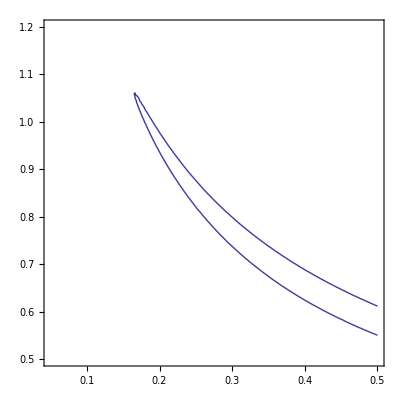

```mathematica
Off[NIntegrate::nlim]
Off[NIntegrate::slwcon]
conchi2sl2s=ContourPlot[{chi2unionsl[Ωm0,zt]==chi2minisl[[1]]+6.18},{Ωm0,0.05,0.5},{zt,0.5,1.2}]
On[NIntegrate::nlim]
On[NIntegrate::slwcon]
```

```mathematica
conchi2sl2sFF=FullForm[conchi2sl2s];
Export["OUTPUT\\2\\conchi2sl2sFF.dat",conchi2sl2sFF]
Export["OUTPUT\\2\\conchi2sl2s.eps",conchi2sl2s]
```

OUTPUT\2\conchi2sl2sFF.dat

OUTPUT\2\conchi2sl2s.eps

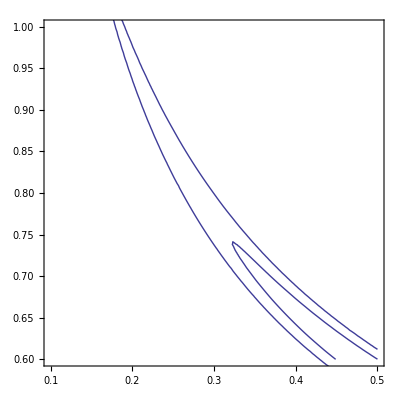

```mathematica
conchi2sl=Show[conchi2sl1s,conchi2sl2s]
```

```mathematica
Export["OUTPUT\\2\\conchi2slFF.dat",conchi2slFF]
Export["OUTPUT\\2\\conchi2sl.eps",conchi2sl]
```

OUTPUT\2\conchi2slFF.dat

OUTPUT\2\conchi2sl.eps

### Perform a grid method

It is unlucky that findminimum doesn’t work. SO I have to use grid method or Monte Carlo method. First try grid method.

The first try was exported to save for future use. Its “OUTPUT \\ 1\\ chi2_table _ 0.15-0.45_ 0.6-0.9.dat”.

A local view of the calculated chi2 data. As you see, the minimum is really hard to distingush. So I decide to write another method to do the calcualtions.

```mathematica
chi2tabtt=Import["OUTPUT\\1\\chi2_table_0.15-0.45_0.6-0.9.dat"];
```

```mathematica
ListPlot3D[chi2tabtt]
```

-Graphics3D-

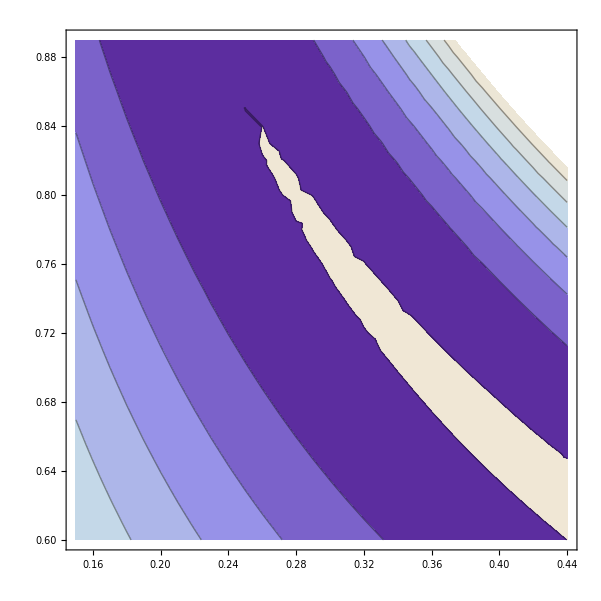

```mathematica
ListContourPlot[chi2tabtt,InterpolationOrder->1]
```

#### Calculate Contour and extract data from contour. Using data extracted from this GRIDING.

Use the data calculated before to determine the minimum of chi2.

```mathematica
chi2data1=Import["OUTPUT\\1\\chi2_table_0.15-0.45_0.6-0.9.dat","Table"];
```

Calculate the length of this table.

```mathematica
lenchi2data1=Length[chi2data1];
```

Reconstruct the table for use of find out the min.

```mathematica
chi2data1chi2=Table[chi2data1[[i]][[3]],{i,1,lenchi2data1}];
```

```mathematica
Min[chi2data1chi2]
```

546.96

Find out at which point chi2 becomes minimum.

```mathematica
chi2min=Select[chi2data1,#[[3]]<546.97&][[1]]
```

{0.44,0.62,546.96}

Plot the contour with confidential level 1σ and 2σ. This is a 2 parameter model. Δχ^2(1σ)=2.30 && Δχ^2(2σ)=6.18 && Δχ^2(3σ)=11.83.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999392671200132}. NIntegrate obtained 0.268826 and 0.0924283 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.996594340002196}. NIntegrate obtained 0.169935 and 0.0126272 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00194}. NIntegrate obtained 10.0159 and 9.81579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00072}. NIntegrate obtained 0.221815 and 0.0104377 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999741179329708}. NIntegrate obtained 0.975752 and 0.76398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999392671200132}. NIntegrate obtained 0.268826 and 0.0924283 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.996594340002196}. NIntegrate obtained 0.169935 and 0.0126272 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00194}. NIntegrate obtained 10.0159 and 9.81579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00072}. NIntegrate obtained 0.221815 and 0.0104377 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999741179329708}. NIntegrate obtained 0.975752 and 0.76398 for the integral and error estimates.

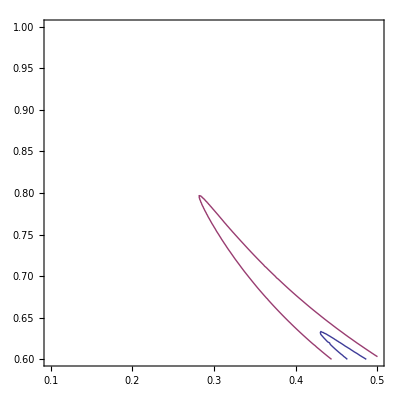

```mathematica
Off[NIntegrate::nlim]
ContourPlot[{chi2union[Ωm0,zt]==chi2min[[3]],chi2union[Ωm0,zt]==chi2min[[3]]+2.30},{Ωm0,0.1,0.5},{zt,0.6,1.0}]
On[NIntegrate::nlim]
```

```mathematica
Off[NIntegrate::slwcon]
Off[NIntegrate::nlim]
ContourPlot[{chi2union[Ωm0,zt]==chi2min[[3]],chi2union[Ωm0,zt]==chi2min[[3]]+2.30,chi2union[Ωm0,zt]==chi2min[[3]]+6.18},{Ωm0,0.05,0.5},{zt,0.5,1.2}]
On[NIntegrate::slwcon]
On[NIntegrate::nlim]
```

```mathematica
Off[NIntegrate::nlim]
ContourPlot[{chi2union[Ωm0,zt]==chi2min[[3]],chi2union[Ωm0,zt]==chi2min[[3]]+2.30,chi2union[Ωm0,zt]==chi2min[[3]]+6.18},{Ωm0,0.05,0.5},{zt,0.5,1.2}]
On[NIntegrate::nlim]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999392671200132}. NIntegrate obtained 0.268826 and 0.0924286 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.996594340002196}. NIntegrate obtained 0.169935 and 0.0126272 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00194}. NIntegrate obtained 10.2448 and 10.0447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00072}. NIntegrate obtained 0.221815 and 0.0104377 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999741179329708}. NIntegrate obtained 0.975972 and 0.764197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
Off[NIntegrate::nlim]
ContourPlot[{chi2union[Ωm0,zt]==chi2min[[3]],chi2union[Ωm0,zt]==chi2min[[3]]+2.30,chi2union[Ωm0,zt]==chi2min[[3]]+6.18,chi2union[Ωm0,zt]==chi2min[[3]]+11.83},{Ωm0,0,0.7},{zt,0.4,1.4}]
On[NIntegrate::nlim]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{546.169,{x→0.587723,y→0.533675}}